# 1. Coxeter Groups

## 1.1 Basics

## 1.1.1 Coxeter Group Data

### 1.1.1.1 Matrices

```mathematica
symmEntry[i_,j_]:=If[i==j,1,If[Abs[i-j]==1,3,2]]
namedQ[M_]:=Head[groupName[M]]==String
raCoxeterGroup[A_]:=Table[Table[If[i==j,1,If[A[[i]][[j]]==1,2,Infinity]],{i,1,Length[A]}],{j,1,Length[A]}](*Gives the Coxeter matrix for the RACG associated to the graph with adjacency matrix A*)
```

#### Finite Groups

```mathematica
typeA[n_]:=
typeA[n]=Table[symmEntry[i,j],{i,1,n},{j,1,n}]
groupName[M_]:="A_"<>ToString[rank[M]]/;M==typeA[rank[M]]

typeB[n_]:=
typeB[n]=Table[If[Or[i==n&&j==n-1,i==n-1&&j==n],4,symmEntry[i,j]],{i,1,n},{j,1,n}]
groupName[M_]:="B_"<>ToString[rank[M]]/;M==typeB[rank[M]]

typeC[n_]:=
typeC[n]=typeB[n]

typeD[n_]:=
typeD[n]=Table[If[Or[i==n&&j==n-2,i==n-2&&j==n],3,If[Or[i==n&&j==n-1,i==n-1&&j==n],2,symmEntry[i,j]]],{i,1,n},{j,1,n}]
groupName[M_]:="D_"<>ToString[rank[M]]/;M==typeD[rank[M]]

E6={{1,3,2,2,2,2},{3,1,3,2,2,2},{2,3,1,3,2,3},{2,2,3,1,3,2},{2,2,2,3,1,2},{2,2,3,2,2,1}};
groupName[E6]="E_6";

E7={{1,3,2,2,2,2,2},{3,1,3,2,2,2,2},{2,3,1,3,2,2,3},{2,2,3,1,3,2,2},{2,2,2,3,1,3,2},{2,2,2,2,3,1,2},{2,2,3,2,2,2,1}};
groupName[E7]="E_7";

E8={{1,3,2,2,2,2,2,2},{3,1,3,2,2,2,2,2},{2,3,1,3,2,2,2,3},{2,2,3,1,3,2,2,2},{2,2,2,3,1,3,2,2},{2,2,2,2,3,1,3,2},{2,2,2,2,2,3,1,2},{2,2,3,2,2,2,2,1}};
groupName[E8]="E_8";

F4={{1,3,2,2},{3,1,4,2},{2,4,1,3},{2,2,3,1}};
G2={{1,6},{6,1}};
groupName[F4]="F_4";

H3={{1,3,2},{3,1,5},{2,5,1}};
groupName[H3]="H_3";

H4={{1,3,2,2},{3,1,3,2},{2,3,1,5},{2,2,5,1}};
groupName[H4]="H_4";

I2[m_]:={{1,m},{m,1}}
groupName[M_]:="I_2("<>ToString[M[[1]][[2]]]<>")"/;M==I2[M[[1]][[2]]]&&Not[MemberQ[{3,4,6},M[[1]][[2]]]]
```

#### Euclidean Groups

```mathematica
ST={{1,4,4},{4,1,2},{4,2,1}};(*symmetry group of square tiling*)
S={{1,Infinity,2,2},{Infinity,1,2,2},{2,2,1,Infinity},{2,2,Infinity,1}};(*D_\infty^2*)
HT={{1,6,3},{6,1,2},{3,2,1}};(*Hexagonal tiling*)
groupName[HT]="HT";
TT={{1,3,3},{3,1,3},{3,3,1}};(*Tiling by equilateral Triangles*)
cube={{1,Infinity,2,2,2,2},{Infinity,1,2,2,2,2},{2,2,1,Infinity,2,2},{2,2,Infinity,1,2,2},{2,2,2,2,1,Infinity},{2,2,2,2,Infinity,1}};(*Tiling of space by cubes*)
```

```mathematica
typeAE[1]={{1,Infinity},{Infinity,1}};
groupName[typeAE[1]]="AE_1";

typeAE[n_]:=typeA[n+1]+Table[Table[If[Or[And[i==1,j==n+1],And[i==n+1,j==1]],1,0],{i,1,n+1}],{j,1,n+1}]/;n>1
groupName[M_]:="AE_"<>ToString[rank[M]-1]/;M==typeAE[rank[M]-1]

typeBE[2]={{1,4,2},{4,1,4},{2,4,1}};
groupName[typeBE[2]]="BE_2";

typeBE[n_]:=Table[If[And[i<n+1,j<n+1],typeB[n][[i]][[j]],If[And[i==n+1,j==n+1],1,If[Or[i==2,j==2],3,2]]],{i,1,n+1},{j,1,n+1}]/;n>2
groupName[M_]:="BE_"<>ToString[rank[M]-1]/;M==typeBE[rank[M]-1]

typeCE[n_]:=typeB[n+1]+Table[If[Or[And[i==1,j==2],And[i==2,j==1]],1,0],{i,1,n+1},{j,1,n+1}]/;n>2
groupName[M_]:="CE_"<>ToString[rank[M]-1]/;M==typeCE[rank[M]-1]

typeDE[n_]:=typeD[n+1]+Table[If[Or[And[i==1,j==2],And[i==2,j==1]],-1,If[Or[And[i==1,j==3],And[i==3,j==1]],1,0]],{i,1,n+1},{j,1,n+1}]/;n>3
groupName[M_]:="DE_"<>ToString[rank[M]-1]/;M==typeDE[rank[M]-1]

EE6=Table[If[And[i<7,j<7],E6[[i]][[j]],If[Or[And[i==7,j==7]],1,If[Or[i==6,j==6],3,2]]],{i,1,7},{j,1,7}];
groupName[EE6]="EE_6";

EE7={{1,3,2,2,2,2,2,2},{3,1,3,2,2,2,2,2},{2,3,1,3,2,2,2,2},{2,2,3,1,3,2,2,3},{2,2,2,3,1,3,2,2},{2,2,2,2,3,1,3,2},{2,2,2,2,2,3,1,2},{2,2,2,3,2,2,2,1}};
groupName[EE7]="EE_7";

EE8={{1,3,2,2,2,2,2,2,2},{3,1,3,2,2,2,2,2,2},{2,3,1,3,2,2,2,2,3},{2,2,3,1,3,2,2,2,2},{2,2,2,3,1,3,2,2,2},{2,2,2,2,3,1,3,2,2},{2,2,2,2,2,3,1,3,2},{2,2,2,2,2,2,3,1,2},{2,2,3,2,2,2,2,2,1}};
groupName[EE8]="EE_8";

FE4={{1,3,2,2,2},{3,1,3,2,2},{2,3,1,4,2},{2,2,4,1,3},{2,2,2,3,1}};
groupName[FE4]="FE_4";

GE2={{1,3,2},{3,1,6},{2,6,1}};
groupName[GE2]="GE_2";
```

#### Hyperbolic Groups

```mathematica
triangle[p_,q_,r_]:={{1,p,r},{p,1,q},{r,q,1}};
groupName[M_]:="triangle("<>ToString[M[[1]][[2]]]<>","<>ToString[M[[1]][[3]]]<>","<>ToString[M[[2]][[3]]]<>")"/;rank[M]==3&&hyperbolicQ[M]
```

#### Right - angled Coxeter groups

```mathematica
free[n_]:=Table[Table[
If[i==j,1,Infinity],
{i,1,n}],
{j,1,n}]
groupName[M_]:="free_"<>ToString[rank[M]]/;M==free[rank[M]]&&rank[M]>1

raPoly[n_]:=Table[
Permute[
Join[{1,2},Table[Infinity,{i,1,n-3}],{2}],
PermutationPower[Cycles[{Table[k,{k,1,n}]}],j-1]],
{j,1,n}]/;n≥4
groupName[M_]:="raPoly_"<>ToString[rank[M]]/;M==raPoly[rank[M]]

bipart[m_,n_]:=Table[Table[
If[i==j,1,If[(i≤n&&j≤n)||(i>n&&j>n),Infinity,2]],
{i,1,n+m}],
{j,1,n+m}]
groupName[M_]:=Module[{m,n},
n=Length[Select[M[[1]],#==2&]];
m=rank[M]-n;
"bipart_("<>ToString[n]<>","<>ToString[m]<>")"/;M==bipart[n,m]&&rank[M]>3
]
```

### 1.1.1.2 Group Size

This can be improved now that we can test for irreducibility, and calculate special subgroups

```mathematica
size[E6]=51840;
size[E7]=2903040;
size[E8]=696729600;
size[F4]=1152;
size[G2]=12;
size[H3]=120;
size[H4]=14400;
size[M_]:=Module[{n},
n=rank[M];
If[n==2,2M[[1]][[2]],
If[M==typeA[n],Factorial[n+1],
If[M==typeB[n],2^n Factorial[n],
If[M==typeD[n],2^(n-1)Factorial[n],Infinity]]]]
]
```

### 1.1.1.3 Maximum Length

This can be improved now that we can test for irreducibility, and calculate special subgroups

```mathematica
maxLength[E6]=36;
maxLength[E7]=63;
maxLength[E8]=120;
maxLength[F4]=24;
maxLength[G2]=6;
maxLength[H3]=15;
maxLength[H4]=60;
maxLength[M_]:=Module[{n},
n=rank[M];
If[n==2,M[[1]][[2]],
If[M==typeA[n],Binomial[n+1,2],
If[M==typeB[n],n^2,
If[M==typeD[n],n^2-n,Infinity]]]]]
```

### 1.1.1.4 Coxeter Number

This can be improved now that we can test for irreducibility, and calculate special subgroups

```mathematica
coxeterNumber[E6]=12;
coxeterNumber[E7]=18;
coxeterNumber[E8]=30;
coxeterNumber[F4]=12;
coxeterNumber[G2]=6;
coxeterNumber[H3]=10;
coxeterNumber[H4]=30;
coxeterNumber[M_]:=Module[{n},
n=rank[M];
If[n==2,M[[1]][[2]],
If[M==typeA[n],n+1,
If[M==typeB[n],2n,
If[M==typeD[n],2n-1,Infinity]]]]]
```

### 1.1.1.5 Group Elements

```mathematica
enumeratedGroups=<|
typeA[3]->6,
typeA[5]->15,
typeA[6]->21,
typeB[5]->25,
typeD[6]->30,
E6->36,
E7->10,
F4->24,
H3->15,
H4->60,
S->66,
HT->66,
TT->66,
typeAE[1]->300,
typeAE[2]->66,
typeAE[3]->25,
typeAE[4]->17,
typeBE[3]->25,
typeBE[4]->15,
typeBE[5]->14,
typeCE[3]->25,
typeCE[4]->15,
typeCE[5]->15,
typeDE[4]->15,
typeDE[5]->11,
EE6->10,
EE7->10,
EE8->9,
FE4->25,
GE2->66,
triangle[2,3,Infinity]->25,
triangle[2,6,Infinity]->16,
triangle[4,4,4]->11,
raPoly[5]->9,
raPoly[6]-> 7,
bipart[3,2]->8,
bipart[3,3]->8
|>;
enumeratedQ[M_,k_]:=If[MemberQ[Keys[enumeratedGroups],M],enumeratedGroups[M]≥ k,False]
enumeratedQ[M_]:=enumeratedQ[M,maxLength[M]]
lengthEnumerated[M_]:=If[MemberQ[Keys[enumeratedGroups],M],enumeratedGroups[M],0]
```

```mathematica
(*ST data (up to length 66) should be recalculated, and HT, TT, S data should be reclassified*)
(*E8 data corrupted, needs to be recomputed*)
(*So far data has been exported, next functions must be written to retrieve it*)
```

```mathematica
elementDirName[M_]:=FileNameJoin[{NotebookDirectory[],"_group_data","group_elements",groupName[M]}]
elementDirExistQ[M_]:=DirectoryQ[elementDirName[M]]
createElementDir[M_]:=CreateDirectory[elementDirName[M]]
exportElementList[M_,{k_}]:=Export[FileNameJoin[{elementDirName[M],ToString[k]<>".mx"}],words[M,{k}]]
exportElementList[M_]:=exportElementList[M,{#}]&/@Range[0,lengthEnumerated[M]]
```

### 1.1.1.6 Smooth Elements

```mathematica
smoothEnumeratedGroups=<|
typeA[3]->6,
typeA[5]->10,
typeA[6]->10,
typeB[5]->10,
typeD[6]->10,
E6->10,
E7->8,
F4->24,
H3->15,
H4->15,
(*ST->20,*)
S->15,
HT->20,
TT->20,
typeAE[1]->15,
typeAE[2]->15,
typeAE[3]->15,
typeAE[4]->10,
typeBE[3]->15,
typeBE[4]->10,
typeBE[5]->8,
typeCE[3]->15,
typeCE[4]->10,
typeCE[5]->8,
typeDE[4]->10,
typeDE[5]->8,
EE6->7,
EE7->6,
EE8->5,
FE4->10,
GE2->10,
triangle[4,4,4]->11
|>;
smoothEnumeratedQ[M_,k_]:=If[MemberQ[Keys[smoothEnumeratedGroups],M],smoothEnumeratedGroups[M]≥ k,False]
smoothEnumeratedQ[M_]:=smoothEnumeratedQ[M,maxLength[M]]
lengthSmoothEnumerated[M_]:=If[MemberQ[Keys[smoothEnumeratedGroups],M],smoothEnumeratedGroups[M],0]
```

```mathematica
(*ST data should be re-incorporated*)
```

```mathematica
smoothDirName[M_]:=FileNameJoin[{NotebookDirectory[],"_group_data","smooth_elements",groupName[M]}]
smoothDirExistQ[M_]:=DirectoryQ[smoothDirName[M]]
createSmoothDir[M_]:=CreateDirectory[smoothDirName[M]]
exportSmoothList[M_,{k_}]:=Export[FileNameJoin[{smoothDirName[M],ToString[k]<>".mx"}],smoothElements[M,{k}]]
exportSmoothList[M_]:=exportSmoothList[M,{#}]&/@Range[0,lengthSmoothEnumerated[M]]
```

### 1.1.1.7 Coxeter Complex Dimension

```mathematica
coxeterDimension[M_]:=Total[coxeterDimension[#[[1]]]&/@specialSubgroups[M]]/;Not[irreducibleQ[M]]
coxeterDimension[M_]:=rank[M]-1/;And[irreducibleQ[M],Or[sphericalQ[M],euclideanQ[M],rank[M]==3]]
coxeterDimension[pent]==2;
coxeterDimension[triangle[4,4,4]]=2;
```

## 1.1.2 Functions

### 1.1.2.1 Diagrams

```mathematica
coxeterAdjacencyMatrix[m_]:=If[m==1||m==2,0,1]
coxeterAdjacencyMatrix[M_List]:=coxeterAdjacencyMatrix[#]&/@ M
coxeterEdges[M_]:=Select[Subsets[Table[i,{i,rank[M]}],{2}],#[[1]]<#[[2]]&& coxeterAdjacencyMatrix[M[[#[[1]]]][[#[[2]]]]]==1&]
coxeterEdgeLabels[M_]:=#[[1]]<-> #[[2]]-> M[[#[[1]]]][[#[[2]]]]&/@coxeterEdges[M]
coxeterDiagram[M_]:=AdjacencyGraph[Table[i,{i,rank[M]}],coxeterAdjacencyMatrix[M],VertexLabels-> "Name",EdgeLabels-> coxeterEdgeLabels[M]]

presentationAdjacencyMatrix[m_]:=If[m==1||m==Infinity,0,1]
presentationAdjacencyMatrix[M_List]:=presentationAdjacencyMatrix[#]&/@ M
presentationEdges[M_]:=Select[Subsets[Table[i,{i,rank[M]}],{2}],#[[1]]<#[[2]]&& presentationAdjacencyMatrix[M[[#[[1]]]][[#[[2]]]]]==1&]
presentationEdgeLabels[M_]:=#[[1]]<-> #[[2]]-> M[[#[[1]]]][[#[[2]]]]&/@presentationEdges[M]
presentationDiagram[M_]:=AdjacencyGraph[Table[i,{i,rank[M]}],presentationAdjacencyMatrix[M],VertexLabels-> "Name",EdgeLabels-> presentationEdgeLabels[M]]
```

### 1.1.2.2 Group Properties

```mathematica
rank[M_]:=Tr[M](*calculates number of generators*)
form[M_]:=Table[Table[-Cos[Pi/M[[i]][[j]]],{j,rank[M]}],{i,rank[M]}] (*gives the canonical bilinear form associated to Coxeter matrix M*)
signature[A_]:={Length[Select[Chop[Eigenvalues[A]],#>0&]],Length[Select[Chop[Eigenvalues[A]],#==0&]],Length[Select[Chop[Eigenvalues[A]],#<0&]]}
euclideanQ[M_]:=signature[N[form[M]]]=={rank[M]-1,1,0}/;irreducibleQ[M]
euclideanQ[M_]:=Fold[And,euclideanQ[#[[1]]]&/@specialSubgroups[M]]/;Not[irreducibleQ[M]]
sphericalQ[M_]:=signature[N[form[M]]]=={rank[M],0,0}
hyperbolicQ[M_]:=signature[N[form[M]]]=={rank[M]-1,0,1}
evenQ[M_]:=Fold[And,Or[EvenQ[#],MemberQ[{1,Infinity},#]]&/@DeleteDuplicates[Flatten[M]]]
rightAngledQ[M_]:=Fold[And,MemberQ[{1,2,Infinity},#]&/@DeleteDuplicates[Flatten[M]]]
```

### 1.1.2.3 Word Manipulations

```mathematica
listToString[w_List]:=StringJoin[Table[ToString[w[[i]]],{i,Length[w]}]] (*converts a word in the form of a list to a string*)
stringToList[w_String]:=Table[StringTake[w,{i}],{i,StringLength[w]}] (*converts a word in the form of a string to a list*)
makeString[w_]:=listToString[w]/;Head[w]==List (*makes word w a string*)
makeString[w_]:=w/;Head[w]==String 
makeList[w_]:=w/;Head[w]==List (*makes word w a list*)
makeList[w_]:=stringToList[w]/;Head[w]==String 
monoidMultiply[v_,w_]:=makeString[Join[makeList[v],makeList[w]]]
inverse[w_String]:=StringReverse[w]
letters[w_]:=DeleteDuplicates[makeList[w]]
firstPosition[w_String,u_String]:=StringPosition[w,u][[1]][[1]]
firstPosition[w_String,uList_List]:=Min[firstPosition[w,#]&/@Complement[uList,{""}]]
```

### 1.1.2.4 Group Elements

```mathematica
coxeterElement[M_]:=makeString[Table[i,{i,1,rank[M]}]]
w[M_,k_]:=makeString[Flatten[Fold[Join,Table[makeList[coxeterElement[M]],{i,1,k}]]]]
longestElement[M_]:=Fold[monoidMultiply,Table[coxeterElement[M],{i,1,coxeterNumber[M]/2}]]/;EvenQ[coxeterNumber[M]]
longestElement[M_]:=braid[{M[[1]][[2]],1,2}]/;rank[M]==2
class[M_,matWord_List,m_]:=#[[2]]&/@Select[matWord,#[[1]]==m&]
deleteRepeatedElements[M_,wList_List]:=Module[{subwords,maxSubwords,list1,matWord,matList,classes,list2,list2old,list2new,pairs,badPairs,extraWords},
matWord={mat[M,#],#}&/@wList;
matList=DeleteDuplicates[#[[1]]&/@matWord];
classes={#,class[M,matWord,#]}&/@matList;
list2=#[[2]][[1]]&/@classes;
list2old=Select[list2,MemberQ[wList,#]&];
list2new=Complement[list2,list2old];
pairs=Outer[List,list2old,list2new]//Flatten[#,1]&;
badPairs=Select[pairs,linWordProblem[M,#[[1]],#[[2]]]&];
extraWords=#[[2]]&/@badPairs;
(*deleteRepeatedElements[M,wList]=*)Complement[list2,extraWords]
]
memberQ[M_,w_,wList_]:=Fold[Or,linWordProblem[M,w,#]&/@wList]
groupMultiply[M_,u_,v_]:=findReduced[M,monoidMultiply[u,v]]
```

### 1.1.2.5 Special Subgroups

```mathematica
generators[M_]:=Table[ToString[i],{i,1,rank[M]}]
generatorsComplement[M_,sList_List]:=Complement[generators[M],sList]
diagramNeighbours[M_,s_String]:=Sort[Select[generators[M],Not[M[[ToExpression[s]]][[ToExpression[#]]]==2]&]]
diagramNeighbours[M_,sList_List]:=Sort[DeleteDuplicates[Flatten[Join[diagramNeighbours[M,#]&/@sList]]]]
connectedComponentUnionQ[M_,sList_List]:=Sort[sList]==diagramNeighbours[M,sList]
irreducibleFactor[M_,s_String]:=If[connectedComponentUnionQ[M,{s}],{s},irreducibleFactor[M,diagramNeighbours[M,s]]]
irreducibleFactor[M_,sList_List]:=If[connectedComponentUnionQ[M,sList],sList,irreducibleFactor[M,diagramNeighbours[M,sList]]]
irreducibleQ[M_]:=irreducibleFactor[M,"1"]==generators[M]
specialSubgroup[M_,sList_List]:={Join[M[[#]]&/@ToExpression[Sort[sList]]][[All,#]]&/@ToExpression[Sort[sList]],Sort[sList]}
convertToSpecialSubgroup[M_,{N_,sList_List},w_String]:=StringReplace[w,Table[sList[[i]]->ToString[i],{i,1,Length[sList]}]]
convertToSpecialSubgroup[M_,{N_,sList_List},wList_List]:=convertToSpecialSubgroup[M,{N,sList},#]&/@wList
convertFromSpecialSubgroup[M_,{N_,sList_List},w_String]:=StringReplace[w,Table[ToString[i]-> sList[[i]],{i,1,Length[sList]}]]
convertFromSpecialSubgroup[M_,{N_,sList_List},wList_List]:=convertFromSpecialSubgroup[M,{N,sList},#]&/@wList
specialSubgroupComplement[M_]:=specialSubgroup[M,generatorsComplement[M,irreducibleFactor[M,"1"]]]
irreducibleFactors[M_]:=If[irreducibleQ[M],{generators[M]},
Join[{irreducibleFactor[M,"1"]},
convertFromSpecialSubgroup[M,specialSubgroupComplement[M],#
]&/@irreducibleFactors[specialSubgroupComplement[M][[1]]]
]
]
specialSubgroups[M_]:=specialSubgroup[M,#]&/@irreducibleFactors[M]
```

### 1.1.2.6 Group Automorphisms

This get’s slow for Coxeter groups of rank greater than n>9 because it calculates all n! possible permutations and checks them.

```mathematica
permuteLabels[M_,perm_List]:=permuteLabels[M,PermutationCycles[perm]]
permuteLabels[M_,perm_Cycles]:=Permute[Transpose[Permute[Transpose[M],InversePermutation[perm]]],InversePermutation[perm]]
diagramAutomorphismQ[M_,perm_]:=M==permuteLabels[M,perm]
permutationToRule[M_,perm_Cycles]:=permutationToRule[M,Permute[Table[i,{i,rank[M]}],InversePermutation[perm]]]
permutationToRule[M_,perm_List]:=Table[ToString[i]-> ToString[perm[[i]]],{i,rank[M]}]
diagramAutomorphisms[M_]:=diagramAutomorphisms[M]=permutationToRule[M,#]&/@Select[Permutations[Table[i,{i,rank[M]}]],diagramAutomorphismQ[M,#]&]
elementAutomorphisms[M_,w_String]:=deleteRepeatedElements[M,Join[{w,inverse[w]},StringReplace[w,#]&/@diagramAutomorphisms[M]]]
automorphismOrbitQ[M_,w_String,u_String]:=Fold[Or,linWordProblem[M,#,u]&/@elementAutomorphisms[M,w]]
automorphismRepresentatives[M_,{}]:={}
automorphismRepresentatives[M_,wList_List]:=Join[{wList[[1]]},automorphismRepresentatives[M,Select[wList,Not[automorphismOrbitQ[M,wList[[1]],#]]&]]]
```

```mathematica
test={{1,5,2,2,2,5,2,2},{5,1,2,2,2,3,2,2},{2,2,1,2,2,2,3,2},{2,2,2,1,2,2,2,2},{2,2,2,2,1,2,3,2},{5,3,2,2,2,1,2,2},{2,2,3,2,3,2,1,3},{2,2,2,2,2,2,3,1}}
```

{{1,5,2,2,2,5,2,2},{5,1,2,2,2,3,2,2},{2,2,1,2,2,2,3,2},{2,2,2,1,2,2,2,2},{2,2,2,2,1,2,3,2},{5,3,2,2,2,1,2,2},{2,2,3,2,3,2,1,3},{2,2,2,2,2,2,3,1}}

### 1.1.2.7 Inversions

```mathematica
makePalindromic[s_String]:=StringJoin[s,StringDrop[StringReverse[s],1]]
inv[M_,w_String]:=Table[Select[reduce[M,makePalindromic[StringTake[findReduced[M,w],k]]],PalindromeQ[#]&,1][[1]],{k,1,coxeterLength[M,w]}]
centralGenerator[w_String]:=StringTake[w,{(StringLength[w]+1)/2}]/;PalindromeQ[w]
conjugatingElement[w_String]:=StringTake[w,(StringLength[w]-1)/2]/;PalindromeQ[w]
```

### 1.1.2.8 Generating sets

```mathematica
randomSubset[set_,{size_}]:=Block[{setSize,randomPerm},
setSize=Length[set];
randomPerm=RandomPermutation[setSize];
Take[Permute[set,randomPerm],size]
]
randomSubsets[set_,{size_},number_]:=Join[{randomSubset[set,{size}]},randomSubsets[set,{size},number-1]]/;number>1
randomSubsets[set_,{size_},1]:={randomSubset[set,{size}]}
findGeneratingSets[M_,elementList_,size_,number_:1]:=Block[{candidate},
candidate=randomSubset[elementList,{size}];
If[
generatingSetQ[M,candidate],
If[
number>1,
Print[candidate];
findGeneratingSets[M,elementList,size,number-1],
candidate
],
findGeneratingSets[M,elementList,size,number]
]
]
(*findGeneratingSet[M_,elementList_,seed_:{}]:=Block[{randomElement,candidate},
randomElement=Take[elementList,{RandomInteger[{1,Length[elementList]}]}][[1]];
candidate=Append[seed,randomElement];
If[
generatingSetQ[M,candidate],
candidate,
findGeneratingSet[M,elementList,candidate]
]
]*)
generatingSetObviouslyStandardQ[M_,wList_]:=cubeCount[nonClosingCompletion[M,setToRose[wList]]][["vertexCount"]]==1
findNonObviouslyStandardGeneratingSet[M_,elementList_,size_,number_:1]:=Block[{candidate},
candidate=findGeneratingSets[M,elementList,size];
If[
Not[generatingSetObviouslyStandardQ[M,candidate]],
If[
number>1,
Print[candidate];
findNonObviouslyStandardGeneratingSet[M,elementList,size,number-1],
candidate
],
findNonObviouslyStandardGeneratingSet[M,elementList,size,number]
]
]
```

## 1.2 Element enumeration

## 1.2.1 Tit’s solution to the word problem

1.2.1.1 Relations

```mathematica
rel[M_]:=Module[{all,depth},
all=Table[{M[[i]][[j]],i,j},{i,1,rank[M]},{j,1,rank[M]}];
depth=If[MemberQ[Flatten[all],Infinity],4,3];
rel[M]=Select[Flatten[all,Depth[all]-depth],Not[#[[1]]==Infinity]&&Not[#[[1]]==1]&]
](*the non-trivial relations on M in the form {m_{ij},i,j}*)
braid[{n_,i_,j_}]:=makeString[Take[Flatten[Table[{i,j},{k,n}]],n] ](*the LHS of the relation for ij*)
inverseBraid[{n_,i_,j_}]:=braid[{n,j,i}] (*the RHS for the relation for ij*)
inverseBraid[b_String]:=inverseBraid[{StringLength[b],StringTake[b,{1}],StringTake[b,{2}]}]
relations[M_]:=braid[#]&/@rel[M](*lists the R/LHS of all braid relations in the group*)
```

1.2.1.2 Type 1 M-move

```mathematica
oneMoveM1[M_,w_]:=StringReplace[makeString[w],x_~~x_->""] 
moveM1[M_,w_]:=Module[{v,n,x,m},
v=makeString[w];
n=StringLength[v];
x=oneMoveM1[M,v];
m=StringLength[x];
If[m==n,x,moveM1[M,x]]
](*performs all Tits moves of type 1 on w which are possible*)
```

1.2.1.3 Type 2 M-move

```mathematica
locate[w_String,b_String]:={b,#}&/@StringPosition[w,b](*produces an indexed list of the positions of all occurences of the substring b in w*)
locateAll[w_String,b_List]:=Fold[Join,locate[w,#]&/@b](*produces an indexed list of the positions of all occurences of the substrings of b in w*)
oneMoveM2[M_,w_String]:=
DeleteDuplicates[Join[{w},Flatten[StringReplaceList[makeString[w],#->inverseBraid[#]]&/@relations[M]]]](*produces a list of all words accessinle form w by a single M2 move, together with w itself*)
oneMoveM2[M_,wList_List]:=DeleteDuplicates[Join[wList,Fold[Join,oneMoveM2[M,#]&/@wList]]]
```

1.2.1.4 Reduction

```mathematica
reducibleQ[w_]:=StringContainsQ[makeString[w],x_~~x_](*returns True if w contains a repeated letter*)
reducibleQ[wList_List]:=Fold[Or,reducibleQ[#]&/@wList]
findReducible[M_,wList_List]:=Select[wList,reducibleQ[#]&,1][[1]](*gives an element of wList which contains a double letter*)
reduce[M_,w_List]:=
reduce[M,w]=reduce[M,makeString[w]]/;Length[w]>1&&Length[w[[1]]]==1(*returs the list of all reduced words for w*)
reduce[M_,w_String]:=
reduce[M,w]=If[reducibleQ[w],reduce[M,moveM1[M,makeString[w]]],reduce[M,oneMoveM2[M,w]]]
reduce[M_,wList_List]:=reduce[M,moveM1[M,findReducible[M,wList]]]/;reducibleQ[wList]
reduce[M_,wList_List]:=Module[{wList2},
wList2=oneMoveM2[M,wList];
If[wList==wList2,wList,reduce[M,oneMoveM2[M,wList]]]
]/;Not[reducibleQ[wList]]&& Not[Length[w]>1&&Length[w[[1]]]==1]
findReduced[M_,w_]:=
findReduced[M,w]=Sort[reduce[M,w]][[1]](*returns a reduced word for w*)
coxeterLength[M_,w_]:=
coxeterLength[M,w]=StringLength[findReduced[M,w]](*calculates the length of the element w*)
```

1.2.1.5 Comparing

```mathematica
titsWordProblem[M_,w_,v_]:=MemberQ[reduce[M,w],findReduced[M,v]](*returns True id w and v express the same element in M*)
```

## 1.2.2 Linear solution to the word problem

```mathematica
e[M_,i_]:=UnitVector[rank[M],i] (*gives the ith standard unit vector*)
mat[M_,w_String]:=
mat[M,w]=If[StringLength[w]==0,
IdentityMatrix[rank[M]],
If[StringLength[w]==1,
Module[{i},
i=ToExpression[w];
ArrayFlatten[{Table[Transpose[{e[M,j]-2form[M][[i]][[j]]e[M,i]}],{j,rank[M]}]}] 
],
Simplify[Dot[mat[M,StringTake[w,-1]],mat[M,StringDrop[w,-1]]]]
]
]
mat[M_,w_List]:=mat[M,makeString[w]]
linWordProblem[M_,u_,v_]:=mat[M,u]==mat[M,v]
```

## 1.2.3 Enumeration by length

```mathematica
class[M_,matWord_List,m_]:=#[[2]]&/@Select[matWord,#[[1]]==m&]
words[M_,0]:={""}
words[M_,k_]:=Module[{subwords,maxSubwords,list1,matWord,matList,classes,list2,list2old,list2new,pairs,badPairs,extraWords},
subwords=words[M,k-1];
maxSubwords=Select[words[M,k-1],StringLength[#]==k-1&];
list1=Join[subwords,Select[Fold[Join,Table[makeString[Join[makeList[#],{i}]],{i,1,rank[M]}]&/@maxSubwords],Not[reducibleQ[#]]&]];
matWord={mat[M,#],#}&/@list1;
matList=DeleteDuplicates[#[[1]]&/@matWord];
classes={#,class[M,matWord,#]}&/@matList;
list2=#[[2]][[1]]&/@classes;
list2old=Select[list2,StringLength[#]<k&];
list2new=Complement[list2,list2old];
pairs=Outer[List,list2old,list2new]//Flatten[#,1]&;
badPairs=Select[pairs,linWordProblem[M,#[[1]],#[[2]]]&];
extraWords=#[[2]]&/@badPairs;
words[M,k]=Complement[list2,extraWords]
]/;Not[enumeratedQ[M,k]]
words[M_,k_]:=Select[words[M,lengthEnumerated[M]],StringLength[#]≤ k&]/;enumeratedQ[M,k]
words[M_,{k_}]:=Select[words[M,k],StringLength[#]==k&]
groupElements[M_]:=words[M,maxLength[M]]/;maxLength[M]<Infinity
lengthIdeal[M_,k_]:=
lengthIdeal[M,k]=If[maxLength[M]≤ k,groupElements[M],If[enumeratedQ[M,k],Select[words[M,lengthEnumerated[M]],StringLength[#]≤k&],words[M,k]]]
```

## 1.3 Visualisation

## 1.3.1 Euclidean geometry

### 1.3.1.1 One Dimensional

```mathematica
euclideanPoints[vertexList_List]:=Point[Join[#,{0}]&/@vertexList]
euclideanReflection[{{x_}},{a_,0}]:={x-(a-x),0}
euclideanLineSegments[vertexList_List,colour_:Gray]:={{Black,PointSize[Medium], euclideanPoints[vertexList]},{colour,Line[{#[[1]],0}&/@vertexList]}}
```

### 1.3.1.2 Two Dimensional

```mathematica
dist[{{x1_,y1_},{x2_,y2_}}]:=Sqrt[(x2-x1)^2+(y2-y1)^2]
euclideanLine[{p1_,p2_}]:=InfiniteLine[{p1,p2}]
euclideanPolygon[vertexList_List, colour_]:={colour,EdgeForm[Thickness[Small]],Polygon[vertexList]}
normalVector[{{x1_,y1_},{x2_,y2_}}]:=RotationTransform[Pi/2][{x1-x2,y1-y2}](*give a vector normal to the line through the two points*)
euclideanReflection[{p1_,p2_},a_]:=ReflectionTransform[normalVector[{p1,p2}],p1][a]
```

### 1.3.1.3 Three Dimensional

Note that euclideanPolyhedron does not output a Graphics3D object.
euclideanReflection does not reflect in affine lines at the moment.

```mathematica
normalVector[{{x1_,y1_,z1_},{x2_,y2_,z2_},{x3_,y3_,z3_}}]:=Cross[{x1,y1,z1}-{x2,y2,z2},{x1,y1,z1}-{x3,y3,z3}]
euclideanPlane[{p1_,p2_,p3_}]:=InfinitePlane[{p1,p2,p3}]
euclideanPolyhedron[vertexList_List,colour_:Gray]:=ConvexHullMesh[vertexList,MeshCellStyle-> {colour,Opacity[.2]}]
euclideanReflection[{p1_,p2_,p3_},a_]:=ReflectionTransform[normalVector[{p1,p2,p3}],p1][a]
```

## 1.3.2 Spherical geometry

### 1.3.2.1 Zero Dimensional

### 1.3.2.2 One Dimensional

```mathematica
bearing[{{xc_,yc_},{x1_,y1_}}]:=Arg[(x1-xc)+I(y1-yc)]
bearing[{normal_,{x1_,y1_,z1_}}]:=bearing[{{0,0},Take[RotationTransform[{normal,{0,0,1}},{0,0,0}][{x1,y1,z1}],2]}]
sphericalLine[{p_}]:=Point[{p,-p}]
sphericalArc[{p1_,p2_},colour_:Gray]:={{Black,PointSize[Medium],Point[{p1,p2}]},{colour,Circle[{0,0},1,bearing[{{0,0},#}]&/@{p1,p2}]}}
sphericalReflection[{p_},a_]:=euclideanReflection[{p,-p},a]
```

### 1.3.2.3 Two Dimensional

It will take more work to make sphericalPolygon output curved portions of the sphere instead of Euclidean polygons.

```mathematica
circle3D[centre_: {0,0,0},radius_: 1,normal_: {0,0,1},angle_: {0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle≥2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
sphericalLine[{p1_,p2_}]:=circle3D[{0,0,0},1,normalVector[{{0,0,0},p1,p2}]]
sphericalLineSegment[{p1_,p2_}]:=circle3D[{0,0,0},1,normalVector[{{0,0,0},p1,p2}],bearing[{normalVector[{{0,0,0},p1,p2}],#}]&/@{p1,p2}]
edgeList[vertexList_List]:=Join[Table[{vertexList[[i]],vertexList[[i+1]]},{i,Length[vertexList]-1}],{{vertexList[[Length[vertexList]]],vertexList[[1]]}}]
sphericalPolygon[vertexList_List,colour_:Gray]:={colour,EdgeForm[Thickness[Large]],Polygon[vertexList]}
sphericalReflection[{p1_,p2_},a_]:=euclideanReflection[{p1,p2,{0,0,0}},a]
```

## 1.3.3 Hyperbolic geometry

```mathematica
kleinToPoincare[{x_,y_}]:=If[{x,y}=={0,0},{0,0},{x/(1+Sqrt[1-x^2-y^2]),y/(1+Sqrt[1-x^2-y^2])}]
poincareToKlein[{x_,y_}]:={2x/(x^2+y^2+1),2y/(x^2+y^2+1)}
poincareToHalfPlane[{x_,y_}]:={Re[#],Im[#]}&/@(Complex[x,y]+I)/(I Complex[x,y]+1)
halfPlaneToPoincare[{x_,y_}]:={Re[#],Im[#]}&/@(Complex[x,y]-I)/(1-I Complex[x,y])
kleinToHalfPlane[{x_,y_}]:=poincareToHalfPlane[kleinToPoincare[{x,y}]]
halfPlaneToKlein[{x_,y_}]:=poincareToKlein[halfPlaneToPoincare[{x,y}]]
```

### 1.3.3.1 Geodesics

```mathematica
line[{{x1_,y1_},{x2_,y2_}}]:=(y-y1)(x2-x1)-(y2-y1)(x-x1)
kleinEndpoints[{p1_,p2_}]:={x,y}/.Solve[line[{p1,p2}]==0 && x^2+y^2==1,{x,y}]
poincareEndpoints[{p1_,p2_}]:=kleinEndpoints[poincareToKlein[#]&/@{p1,p2}]
tangentLine[{x1_,y1_}]:=y1(y-y1)+x1(x-x1)
tangentIntersection[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,{Infinity},{x,y}/.Solve[tangentLine[{x1,y1}]==0&&tangentLine[{x2,y2}]==0,{x,y}]][[1]]
poincareLineCentre[{p1_,p2_}]:=tangentIntersection[poincareEndpoints[{p1,p2}]]
poincareLineRadius[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,Infinity,dist[{poincareLineCentre[{{x1,y1},{x2,y2}}],{x1,y1}}]]
bearingAdjustment[{theta1_,theta2_}]:=Module[{delta,n},
delta=theta2-theta1;
n=Floor[delta/Pi];
{theta1,theta2-n Pi}
](*this insures the angular difference between the pair of bearings is less than Pi*)
poincareLineBearings[{p1_,p2_}]:=bearingAdjustment[bearing[{poincareLineCentre[{p1,p2}],#}]&/@{p1,p2}]
poincareEndpointBearings[{p1_,p2_}]:=bearing[{poincareLineCentre[{p1,p2}],#}]&/@poincareEndpoints[{p1,p2}]
```

### 1.3.3.2 Triangles

```mathematica
circle3Centre[theta_]:=1/(Sqrt[(Tan[theta])^2+1])
circle3Radius[theta_,a_]:=Cos[theta]+Sqrt[(Cos[theta])^2+a^2-1]
vertexA[theta1_,theta2_]:={Sin[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]],Cos[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]]}
vertexB[theta1_,theta2_]:={circle3Centre[theta1],Sqrt[1-(circle3Centre[theta1])^2]}
vertexC[theta1_,theta2_]:={2circle3Centre[theta1]-Sin[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]],Cos[ArcSin[circle3Radius[theta2,circle3Centre[theta1]] Sin[theta2]]/circle3Centre[theta1]]}
halfPlaneHypTriangle[{theta1_,theta2_,theta3_}]:=If[theta1==theta2,{vertexB[theta3,theta1],vertexA[theta3,theta1],vertexC[theta3,theta1]},
If[theta2==theta3,{vertexC[theta1,theta2],vertexB[theta1,theta2],vertexA[theta1,theta2]},
If[theta1==theta3,{vertexA[theta2,theta1],vertexC[theta2,theta1],vertexB[theta2,theta1]},
Failure["Invalid angles","You must choose at east two angles the same"]
]
]
]
barycentre[{theta1_,theta2_,theta3_}]:=Module[{phi1,phi2},
phi1=If[Select[{theta1,theta2,theta3},#==theta1&]=={theta1},theta1,
If[Select[{theta1,theta2,theta3},#==theta2&]=={theta2},theta2,
theta3
]
];
phi2=If[theta1==phi,theta2,theta1];
{circle3Centre[phi1,phi2],Sqrt[circle3Radius[phi2,circle3Centre[phi1]]/Sqrt[1-circle3Centre[phi1]]]}
]
centredHalfPlaneHypTriangle[{theta1_,theta2_,theta3_}]:=(#-barycentre[{theta1,theta2,theta3}][[1]])/barycentre[{theta1,theta2,theta3}][[2]]&/@halfPlaneHypTriangle[{theta1,theta2,theta3}]
poincareHypTriangle[{theta1_,theta2_,theta3_}]:=halfPlaneToPoincare[#]&/@centredHalfPlaneHypTriangle[{theta1,theta2,theta3}]
```

```mathematica
Select[{2,2,3},#==2&]
```

{2,2}

### 1.3.3.3 Poincare Disc

```mathematica
poincareLine[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,
Line[poincareEndpoints[{{x1,y1},{x2,y2}}]],
Circle[poincareLineCentre[{{x1,y1},{x2,y2}}],poincareLineRadius[{{x1,y1},{x2,y2}}],poincareEndpointBearings[{{x1,y1},{x2,y2}}]]
]
poincareLineSegment[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,
Line[{{x1,y1},{x2,y2}}],
Circle[poincareLineCentre[{{x1,y1},{x2,y2}}],poincareLineRadius[{{x1,y1},{x2,y2}}],poincareLineBearings[{{x1,y1},{x2,y2}}]]
]
BezierCircleArcSmallAngle[{x_,y_},r_,{θ1_,θ2_}]:=Module[{α,p0,p1,p2,p3},α=4/3 Tan[(θ2-θ1)/4];
p0={x,y}+r {Cos[θ1],Sin[θ1]};
p3={x,y}+r {Cos[θ2],Sin[θ2]};
p1=p0+α r {-Sin[θ1],Cos[θ1]};
p2=p3+α r {Sin[θ2],-Cos[θ2]};
BezierCurve[{p0,p1,p2,p3}]](*This produces a Bezier curve which closely approximates Circle[{x,y},r,{θ1,θ2}] up to θ2-θ1=Pi/2. This is required to use FilledCurve below*)
BezierCircleArc[{x_,y_},r_,{θ1_,θ2_}]:=BezierCircleArcSmallAngle[{x,y},r,#]&/@Table[{θ1+i(θ2-θ1)/50,θ1+(i+1)(θ2-θ1)/50},{i,0,49}]
poincareLineSegmentApprox[{{x1_,y1_},{x2_,y2_}}]:=If[y1 x2==y2 x1,
{Line[{{x1,y1},{x2,y2}}]},
BezierCircleArc[poincareLineCentre[{{x1,y1},{x2,y2}}],poincareLineRadius[{{x1,y1},{x2,y2}}],poincareLineBearings[{{x1,y1},{x2,y2}}]]
]
poincarePolygon[vertexList_List,colour_:Gray]:={colour,EdgeForm[Thickness[Small]],FilledCurve[Fold[Join,poincareLineSegmentApprox[#]&/@edgeList[vertexList]]]}
poincareReflection[{{x1_,y1_},{x2_,y2_}},a_]:=If[y1 x2==y2 x1,
euclideanReflection[{{x1,y1},{x2,y2}},a],
(poincareLineRadius[{{x1,y1},{x2,y2}}]^2 (a-poincareLineCentre[{{x1,y1},{x2,y2}}]))/(dist[{poincareLineCentre[{{x1,y1},{x2,y2}}],a}]^2)+poincareLineCentre[{{x1,y1},{x2,y2}}]
]
```

### 1.3.3.4 Klein Disc

```mathematica
kleinLine[{p1_,p2_}]:=Line[kleinEndpoints[{p1,p2}]]
kleinLineSegment[{p1_,p2_}]:=Line[{p1,p2}]
kleinPolygon[vertexList_List,colour_:Gray]:={colour,EdgeForm[Thickness[Small]],Polygon[vertexList]}
kleinReflection[{p1_,p2_},a_]:=poincareToKlein[poincareReflection[{kleinToPoincare[p1],kleinToPoincare[p2]},kleinToPoincare[a]]]
absolute=Circle[];
```

## 1.3.4 Chambers

chamberBarycentre could be improved for hyperbolic chambers.

```mathematica
chamberVertices[M_,w_]:=transformation[M,w,#]&/@chamberVertices[M,""]
chamber[M_,w_,colour_:Gray]:=euclideanLineSegments[chamberVertices[M,w],colour]/;And[euclideanQ[M],Length[chamberVertices[M,w][[1]]]==1]
chamber[M_,w_,colour_:Gray]:=If[sphericalQ[M],sphericalArc[chamberVertices[M,w],colour],
If[euclideanQ[M],euclideanPolygon[chamberVertices[M,w],colour],
If[hyperbolicQ[M],poincarePolygon[chamberVertices[M,w],colour],
"Cannot show chamber for this type of group"
]
]
]/;Length[chamberVertices[M,w][[1]]]==2
chamber[M_,w_,colour_:Gray]:=If[sphericalQ[M],sphericalPolygon[chamberVertices[M,w],colour],
If[euclideanQ[M],euclideanPolyhedron[chamberVertices[M,w],colour],
"Cannot show chamber for this type of group"
]
]/;Length[chamberVertices[M,w][[1]]]==3
chamberBarycentre[M_,w_]:=If[sphericalQ[M],Normalize[Mean[chamberVertices[M,w]]],
If[euclideanQ[M],Mean[chamberVertices[M,w]],
If[hyperbolicQ[M],Mean[chamberVertices[M,w]],
"Cannot compute barycentre for this type of group"
]
]
]
showChambers[M_,wList_List,colour_]:=Graphics[chamber[M,#,colour]&/@wList,Frame->False]/;And[euclideanQ[M],Length[chamberVertices[M,wList[[1]]][[1]]]==1]
showChambers[M_,wList_List,colour_]:=Graphics[chamber[M,#,colour]&/@wList,Frame->False]/;Length[chamberVertices[M,""][[1]]]==2
showChambers[M_,wList_List,colour_]:=If[euclideanQ[M],Show[chamber[M,#,colour]&/@wList],
Graphics3D[chamber[M,#,colour]&/@wList,Boxed->False]
]/;Length[chamberVertices[M,""][[1]]]==3
```

### 1.3.4.1 Group data

Chamber vertices listed so that the first and second vertices define the wall labelled “1”, the second and third define the wall labelled “2”, and so on. If this is not possible, the vertices must be labelled cyclically, and this correspondence can be defined manually using the function wallGeneratorPairs in the next section.

```mathematica
chamberVertices[typeA[3],""]={{-1/(√6),-1/(√2),1/(√3)},{0,0,1},{-(2 √2)/3,0,1/3}};
chamberVertices[typeB[3],""]={{-1/(√2),-1/(√2),0},{-1/(√3),-1/(√3),-1/(√3)},{-1,0,0}};
phi=(1+Sqrt[5])/2;
chamberVertices[H3,""]={{1/2 √(1/2 (3+√5)),1/(√(2 (3+√5))),(1+√5)/(2 √(2 (3+√5)))},{1/(√3),1/(√3),1/(√3)},{(2+√5) √(2/(25+11 √5)),0,(3+√5)/(√(50+22 √5))}};
chamberVertices[M_,""]:={{0,1},Normalize[{Tan[Pi/M[[1]][[2]]],1}]}/;And[rank[M]==2,Not[M[[1]][[2]]==Infinity]]
chamberVertices[typeAE[1],""]={{0},{1}};
chamberVertices[ST,""]={{0,0},{1,1},{1,0}};
chamberVertices[S,""]={{0,0},{0,1},{1,1},{1,0}};
chamberVertices[HT,""]={{1/2,0},{0,(√3)/2},{0,0}};
chamberVertices[TT,""]={{0,0},{1/2,(√3)/2},{1,0}};
chamberVertices[Cube,""]={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,1},{1,1,0},{1,1,1}};
chamberVertices[triangle[2,6,Infinity],""]={{0,0},{0,1},{1/(2 √3),1/2}};
```

## 1.3.5 Transformations

```mathematica
chamberWalls[M_]:=edgeList[chamberVertices[M,""]]/;coxeterDimension[M]==2
wallGeneratorPairs[M_]:=Table[{chamberWalls[M][[i]],ToString[i]},{i,rank[M]}]
generatorToWall[M_,s_]:=Select[wallGeneratorPairs[M],#[[2]]==s&][[1]][[1]]
transformation[M_,"",point_]:=point
transformation[M_,s_,point_]:=If[sphericalQ[M],sphericalReflection[generatorToWall[M,s],point],
If[euclideanQ[M],euclideanReflection[generatorToWall[M,s],point],
If[hyperbolicQ[M],poincareReflection[generatorToWall[M,s],point],
"Cannot perform transformation for this type of group"
]
]
]/;StringLength[s]==1
transformation[M_,w_,point_]:=
transformation[M,w,point]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],point]]]
```

### 1.3.5.1 Group Data

```mathematica
chamberWalls[typeAE[1]]=chamberVertices[typeAE[1],""];
chamberWalls[Cube]={{{0,0,0},{1,0,0},{0,1,0}},{{0,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,1},{1,0,0}},{{0,1,1},{1,0,1},{1,1,1}},{{1,0,1},{1,1,0},{1,1,1}},{{1,1,0},{0,1,1},{1,1,1}}};
```

```mathematica
wallGeneratorPairs[S]=Table[{chamberWalls[S][[i]],{"1","3","2","4"}[[i]]},{i,4}];
wallGeneratorPairs[Cube]=Table[{chamberWalls[Cube][[i]],{"1","3","5","2","4","6"}[[i]]},{i,6}];
```

### 1.3.5.2 Redundant Group Data

Type A[3]

```mathematica
transformation[typeA[3],"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
```

Type B[6]

```mathematica
transformation[typeB[3],"1",{x_,y_,z_}]:=ReflectionTransform[{0,1,1}][{x,y,z}]
transformation[typeB[3],"2",{x_,y_,z_}]:=ReflectionTransform[{1,-1,0}][{x,y,z}]
transformation[typeB[3],"3",{x_,y_,z_}]:=ReflectionTransform[{1,0,0}][{x,y,z}]
```

H3

```mathematica
transformation[H3,"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,0,1.615}]][{x,y,z}]
```

I2[m]

```mathematica
transformation[M_,"1",{x_,y_}]:=ReflectionTransform[{1,-Tan[Pi/M[[1]][[2]]]}][{x,y}]/;rank[M]==2
transformation[M_,"2",{x_,y_}]:=ReflectionTransform[{1,0}][{x,y}]/;rank[M]==2
```

ST

```mathematica
transformation[ST,"1",{x_,y_}]:={1-y,1-x}
transformation[ST,"2",{x_,y_}]:={-x,y}
transformation[ST,"3",{x_,y_}]:={x,-y}
```

S

```mathematica
transformation[S,"1",{x_,y_}]:={-x,y}
transformation[S,"2",{x_,y_}]:={2-x,y}
transformation[S,"3",{x_,y_}]:={x,-y}
transformation[S,"4",{x_,y_}]:={x,2-y}
```

HT

```mathematica
transformation[HT,"1",{x_,y_}]:=ReflectionTransform[{Sqrt[3],1}][{x-1,y}]+{1,0}
transformation[HT,"2",{x_,y_}]:={-x,y}
transformation[HT,"3",{x_,y_}]:={x,-y}
```

TT

```mathematica
transformation[TT,"1",{x_,y_}]:={-x/2+(√3 y)/2,(√3 x)/2+y/2}
transformation[TT,"2",{x_,y_}]:={-(x-1)/2-(√3 y)/2+1,-(√3( x-1))/2+y/2}
transformation[TT,"3",{x_,y_}]:={x,-y}
```

triangle[2,6,Infinity]

```mathematica
transformation[triangle[2,6,Infinity],"1",{x_,y_}]:={(-(-2+√3) x+2 √3 x^2+(-1+y) (-1+2 √3 y))/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)
,(2-√3-5 x+2 √3 x+6 x^2+2 y-3 √3 y+6 y^2)/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)}
transformation[triangle[2,6,Infinity],"2",{x_,y_}]:={2(x Cos[Pi/3]+y Sin[Pi/3])Cos[Pi/3]-x,2(x Cos[Pi/3]+y Sin[Pi/3])Sin[Pi/3]-y}
transformation[triangle[2,6,Infinity],"3",{x_,y_}]:={-x,y}
```

## 1.3.6 Hyperplanes

```mathematica
zeroVector[M_]:=Module[{r,e,n},
r=rank[M];
e=If[sphericalQ[M],0,If[Or[euclideanQ[M],hyperbolicQ[M]],1,0]];
n=r-e;
Table[0,{k,1,n}]
]
normalVector[M_,r_]:=transformation[M,conjugatingElement[r],normalVector[M,centralGenerator[r]]]-transformation[M,conjugatingElement[r],zeroVector[M]]/;StringLength[r]>1
basePoint[M_,r_]:=zeroVector[M]/;sphericalQ[M]
basePoint[M_,r_]:=transformation[M,conjugatingElement[r],basePoint[M,centralGenerator[r]]]/;euclideanQ[M]&&StringLength[r]>1
hyperplane[M_,r_]:=Hyperplane[normalVector[M,r],basePoint[M,r]]
showHyperplanes[M_,rList_List]:=If[Length[basePoint[M,"1"]]==2,Graphics[hyperplane[M,#]&/@rList],Graphics3D[hyperplane[M,#]&/@rList]]
```

### 1.3.6.1 Group Data

Type A[3]

```mathematica
normalVector[typeA[3],"1"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]
normalVector[typeA[3],"2"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
normalVector[typeA[3],"3"]:=Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
```

Type B[3]

```mathematica
normalVector[typeB[3],"1"]:=Cross[{0,-1,1},{-1,-1,1}]
normalVector[typeB[3],"2"]:=Cross[{0,0,1},{-1,-1,1}]
normalVector[typeB[3],"3"]:=Cross[{0,0,1},{0,-1,1}]
```

H3

```mathematica
normalVector[H3,"1"]:=Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]
normalVector[H3,"2"]:=Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]
normalVector[H3,"3"]:=Cross[{0,0,1.615},{1,0,1.615}]
```

I2[m]

```mathematica
normalVector[M_,"1"]:={1,-Tan[Pi/M[[1]][[2]]]}/;rank[M]==2
normalVector[M_,"2"]:={1,0}/;rank[M]==2
```

ST

```mathematica
normalVector[ST,"1"]:={1,1}
normalVector[ST,"2"]:={1,0}
normalVector[ST,"3"]:={0,1}
basePoint[ST,"1"]:={1,0}
basePoint[ST,"2"]:={0,0}
basePoint[ST,"3"]:={0,0}
```

S

```mathematica
normalVector[S,"1"]:={1,0}
normalVector[S,"2"]:={1,0}
normalVector[S,"3"]:={0,1}
normalVector[S,"4"]:={0,1}
basePoint[S,"1"]:={0,0}
basePoint[S,"2"]:={1,0}
basePoint[S,"3"]:={0,0}
basePoint[S,"4"]:={0,1}
```

HT

```mathematica
normalVector[HT,"1"]:={Sqrt[3],1}
normalVector[HT,"2"]:={1,0}
normalVector[HT,"3"]:={0,1}
basePoint[HT,"1"]:={1,0}
basePoint[HT,"2"]:={0,0}
basePoint[HT,"3"]:={0,0}
```

TT

```mathematica
normalVector[TT,"1"]:={Sqrt[3],-1}
normalVector[TT,"2"]:={Sqrt[3],1}
normalVector[TT,"3"]:={0,1}
basePoint[TT,"1"]:={0,0}
basePoint[TT,"2"]:={1,0}
basePoint[TT,"3"]:={0,0}
```

## 1.3.7 Galleries

```mathematica
gallery[M_,w_String]:=ListLinePlot[chamberBarycentre[M,#]&/@Table[StringTake[w,i],{i,0,StringLength[w]}],PlotStyle->Red, Axes->False]
gallery[M_,wList_List]:=gallery[M,#]&/@wList
galleryLeftBruhatIdeal[M_,w_]:=Show[showLeftBruhatIdeal[M,w,GrayLevel[0.9]],gallery[M,w]]
galleryLengthIdeal[M_,w_String]:=Show[showLengthIdeal[M,coxeterLength[M,w],GrayLevel[0.9]],gallery[M,w]]
galleryLengthIdeal[M_,wList_List]:=Show[showLengthIdeal[M,Max[coxeterLength[M,#]&/@wList],GrayLevel[0.9]],gallery[M,wList]]
```

# 2. Bruhat order and Poincare polynomials

## 2.1 Bruhat order

Bruhat Ideal

#### Tit’s Method

```mathematica
nonMinimalQ[M_,w_String]:=If[reducibleQ[w],True,nonMinimalQ[M,oneMoveM2[M,w]]]
nonMinimalQ[M_,wList_List]:=If[Fold[Or,reducibleQ[#]&/@wList],True,If[oneMoveM2[M,wList]==wList,False,nonMinimalQ[M,oneMoveM2[M,wList]]]]
subwords[M_,"",k_]:={}
subwords[M_,w_,k_]:=DeleteDuplicates[findReduced[M,makeString[#]]&/@Subsets[makeList[w],{k}]]
reducedSubwords[M_,w_,k_]:=Sort[DeleteDuplicates[Select[subwords[M,w,k],Not[nonMinimalQ[M,#]]&]]]
titBruhatLess[M_,""]:={};
titBruhatLess[M_,w_]:=Module[{x,d,r},
x=findReduced[M,makeString[w]];
d=StringLength[x];
r=reducedSubwords[M,x,d-1];
titBruhatLess[M,w]={#,x}&/@r
]
titBruhatLessList[M_,""]:={};
titBruhatLessList[M_,w_]:=
titBruhatLessList[M,w]=#[[1]]&/@titBruhatLess[M,w]
titBruhatGraph[M_,""]:={}
titBruhatGraph[M_,w_]:={{"",w}}/;StringLength[w]==1
titBruhatGraph[M_,w_]:=
titBruhatGraph[M,w]=DeleteDuplicates[Join[titBruhatLess[M,w],Fold[Join,titBruhatGraph[M,#]&/@titBruhatLessList[M,w]]]]
titBruhatIdeal[M_,w_]:=
titBruhatIdeal[M,w]=Sort[DeleteDuplicates[Join[#[[1]]&/@titBruhatGraph[M,w],{findReduced[M,w]}]],StringLength[#1]<StringLength[#2]&]
```

#### Linear Method

```mathematica
subStringQ["",w_]:=True
subStringQ[u_String,w_String]:=StringContainsQ[w,u]/;StringLength[u]==1
subStringQ[u_String,w_String]:=Module[{a},
a=StringTake[u,1];
If[StringContainsQ[w,a],subStringQ[StringDrop[u,1],StringDrop[w,StringPosition[w,a,1][[1]][[1]]]],False]
]
subStringQ[uList_List,w_String]:=Fold[Or,subStringQ[#,w]&/@uList]
linBruhatIdeal[M_,w_String]:=
linBruhatIdeal[M,w]=Join[Select[lengthIdeal[M,coxeterLength[M,w]-1],subStringQ[reduce[M,#],findReduced[M,w]]&],{findReduced[M,w]}]
linBruhatIdeal[M_,w_List]:=linBruhatIdeal[M,makeString[w]]
```

```mathematica
bruhatIdeal[M_,w_String]:=
bruhatIdeal[M,w]=If[enumeratedQ[M,coxeterLength[M,w]-1],linBruhatIdeal[M,w],titBruhatIdeal[M,w]](*optimise this mased on coxeter length of w, rank of M by calculating relative speeds of the two processes*)
bruhatIdeal[M_,w_List]:=bruhatIdeal[M,makeString[w]]
leftBruhatIdeal[M_,w_String]:=Module[{list},
list=DeleteDuplicates[Fold[Join,Table[StringTake[#,i],{i,0,coxeterLength[M,w]}]&/@reduce[M,w]]];
leftBruhatIdeal[M,w]=DeleteDuplicates[findReduced[M,#]&/@list]
]
leftBruhatIdeal[M_,w_List]:=leftBruhatIdeal[M,makeString[w]]
rightBruhatIdeal[M_,w_String]:=Module[{list},
list=DeleteDuplicates[Fold[Join,Table[StringTake[#,-i],{i,0,coxeterLength[M,w]}]&/@reduce[M,w]]];
rightBruhatIdeal[M,w]=DeleteDuplicates[findReduced[M,#]&/@list]
]
rightBruhatIdeal[M_,w_List]:=leftBruhatIdeal[M,makeString[w]]
invert[M_,wList_List]:=findReduced[M,gpMultiply[longestElement[M],#]]&/@wList
invertedLeftBruhatIdeal[M_,w_]:=invert[M,leftBruhatIdeal[M,w]]
bruhatIdealMinusLeft[M_,w_]:=Complement[bruhatIdeal[M,w],leftBruhatIdeal[M,w]]
invertedBruhatIdealMinusLeft[M_,w_]:=invert[M,bruhatIdealMinusLeft[M,w]]
```

## 2.2 Poincare polynomial

```mathematica
bruhatRankCount[M_,w_,0]:=1
bruhatRankCount[M_,w_,k_]:=0/;k>coxeterLength[w]
bruhatRankCount[M_,w_,k_]:=
bruhatRankCount[M,w,k]=Length[Select[bruhatIdeal[M,w],StringLength[#]==k&]]
poincarePoly[M_,w_,q_]:=
poincarePoly[M,w,q]=Sum[bruhatRankCount[M,w,k]q^k,{k,0,coxeterLength[M,w]}]
polyPalindromicQ[P_,q_]:=PalindromeQ[CoefficientList[P,q]]
```

### Smoothness

```mathematica
smoothQ[M_,""]:=True
smoothQ[M_,w_]:=
smoothQ[M,w]=polyPalindromicQ[poincarePoly[M,w,q],q]
smoothElementsUnder[M_,w_]:=
smoothElementsUnder[M,w]=Select[bruhatIdeal[M,w],smoothQ[M,#]&]
nonSmoothElementsUnder[M_,w_]:=Complement[bruhatIdeal[M,w],smoothElementsUnder[M,w]]
smoothPolyUnder[M_,w_]:=
smoothPolyUnder[M,w]=poincarePoly[M,#,q]&/@smoothElementsUnder[M,w]
nonSmoothPolyUnder[M_,w_]:=
nonSmoothPolyUnder[M,w]=poincarePoly[M,#,q]&/@nonSmoothElementsUnder[M,w]
smoothElements[M_,0]={""};
smoothElements[M_,k_]:=
smoothElements[M,k]=Join[smoothElements[M,k-1],Select[Complement[lengthIdeal[M,k],lengthIdeal[M,k-1]],smoothQ[M,#]&]]
smoothElements[M_,{k_}]:=Select[smoothElements[M,k],StringLength[#]==k&]
nonSmoothElements[M_,k_]:=Complement[lengthIdeal[M,k],smoothElements[M,k]]
nonSmoothPoly[M_,k_,q_]:=
nonSmoothPoly[M,k,q]=poincarePoly[M,#,q]&/@nonSmoothElements[M,k]
smoothPoly[M_,k_,q_]:=
smoothPoly[M,k,q]=poincarePoly[M,#,q]&/@smoothElements[M,k]
```

#### Quick check for smoothness

```mathematica
memberQ[M_,w_,wList_]:=Fold[Or,linWordProblem[M,w,#]&/@wList]
initialLetters[M_,w_]:=Select[Table[ToString[i],{i,1,rank[M]}],memberQ[M,#,Table[makePalindromic[StringTake[w,k]],{k,1,StringLength[w]}]]&]
firstNonInitialLetterPos[M_,w_]:=StringPosition[w,Complement[Table[ToString[i],{i,1,rank[M]}],initialLetters[M,w]]][[1]][[1]]
simplifiedCaseWord[M_,w_]:=StringDrop[w,firstNonInitialLetterPos[M,w]-1]
fundamentalDomain[M_,w_]:=Select[bruhatIdeal[M,simplifiedCaseWord[M,w]],Intersection[initialLetters[M,#],initialLetters[M,w]]=={}&]
lengthGeneratingPoly[M_,wList_List,q_]:=Total[q^StringLength[#]&/@wList]
quickSmoothQ[M_,w_]:=polyPalindromicQ[lengthGeneratingPoly[M,fundamentalDomain[M,w],q],q]
```

### Enumerated Smooth Elements

```mathematica
smoothEnumeratedGroups={
{typeA[3],6},
{typeA[5],10},
{typeA[6],10},
{typeB[5],10},
{typeD[6],10},
{E6,10},
{E7,8},
{E8,0},
{F4,24},
{H3,15},
{H4,15},
{ST,20},
{S,15},
{HT,20},
{TT,20},
{typeAE[1],15},
{typeAE[2],15},
{typeAE[3],15},
{typeAE[4],10},
{typeBE[3],15},
{typeBE[4],10},
{typeBE[5],8},
{typeCE[3],15},
{typeCE[4],10},
{typeCE[5],8},
{typeDE[4],10},
{typeDE[5],8},
{EE6,7},
{EE7,6},
{EE8,5},
{FE4,10},
{GE2,10}
};
smoothEnumeratedQ[M_,k_]:=If[MemberQ[#[[1]]&/@smoothEnumeratedGroups,M],Select[smoothEnumeratedGroups,#[[1]]==M&][[1]][[2]]≥ k,False]
smoothEnumeratedQ[M_]:=smoothEnumeratedQ[M,maxLength[M]]
lengthSmoothEnumerated[M_]:=If[MemberQ[#[[1]]&/@smoothEnumeratedGroups,M],Select[smoothEnumeratedGroups,#[[1]]==M&][[1]][[2]],0]
```

Type A[3]

```mathematica
smoothElements[typeA[3],lengthEnumerated[typeA[3]]]={"","1","12","121","1213","12132","121321","123","1232","13","132","1321","2","21","213","21321","23","232","2321","3","32","321"};
```

Type A[5]

```mathematica
smoothElements[typeA[5],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321435","1213214354","12132145","121321454","1213215","12132154","121321543","1213215432","121324","1213243","12132432","121324325","1213243254","12132435","121324354","1213243543","1213245","12132454","121325","1213254","12132543","121325432","12134","121343","1213435","12134354","121343543","121345","1213454","12135","121354","1213543","1214","12143","121432","1214321","12143215","1214325","1214325432","121435","12143543","12145","121454","1214543","12145432","121454321","1215","12154","121543","1215432","12154321","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232435","12324354","123243543","123245","1232454","12325","123254","1232543","12325432","1234","12343","123435","1234354","12343543","12345","123454","1235","12354","123543","124","1243","12432","124325","124325432","12435","1243543","1245","12454","124543","1245432","125","1254","12543","125432","13","132","1321","13214","13214321","132143215","132145","1321454","13215","132154","132154321","1324","132432","1324325","1324325432","13245","132454","1325","13254","1325432","134","1343","13432","134321","1343215","13432154","134325","1343254","134325432","13435","134354","1343543","13435432","134354321","1345","13454","135","1354","13543","135432","1354321","14","143","1432","14321","143215","1432154321","14325","14325432","1435","143543","1435432","14354321","145","1454","14543","145432","1454321","15","154","1543","15432","154321","2","21","213","21321","213214","213214321","2132143215","2132145","21321454","213215","2132154","2132154321","2134","21343","213435","2134354","21343543","21345","213454","2135","21354","213543","214","2143","214321","2143215","21435","2143543","2145","21454","214543","21454321","215","2154","21543","2154321","23","232","2321","23214","232143","23214321","232143215","2321432154","2321435","23214354","232143543","232145","2321454","23215","232154","2321543","232154321","2324","23243","232432","2324321","23243215","232432154","2324321543","2324325","23243254","232432543","2324325432","232435","2324354","23243543","23245","232454","2325","23254","232543","2325432","23254321","234","2343","23435","234354","2343543","2345","23454","235","2354","23543","24","243","2432","24321","243215","2432154321","24325","24325432","243254321","2435","243543","245","2454","24543","245432","2454321","25","254","2543","25432","254321","3","32","321","3214","3214321","32143215","32145","321454","3215","32154","32154321","324","32432","324321","3243215","324325","324325432","3243254321","3245","32454","325","3254","325432","3254321","34","343","3432","34321","343215","3432154","3432154321","34325","343254","34325432","343254321","3435","34354","343543","3435432","34354321","345","3454","35","354","3543","35432","354321","4","43","432","4321","43215","432154321","4325","4325432","43254321","435","43543","435432","4354321","45","454","4543","45432","454321","5","54","543","5432","54321"};
```

Type A[6]

```mathematica
smoothElements[typeA[6],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","1213214326","121321435","1213214354","1213214356","121321436","1213214365","12132145","121321454","1213214546","121321456","1213214565","12132146","121321465","1213214654","1213215","12132154","121321543","1213215432","1213215436","121321546","12132156","121321565","1213215654","1213216","12132165","121321654","1213216543","121324","1213243","12132432","121324325","1213243254","1213243256","121324326","1213243265","12132435","121324354","1213243543","1213243546","121324356","1213243565","12132436","121324365","1213243654","1213245","12132454","121324546","1213245465","12132456","121324565","1213246","12132465","121324654","121325","1213254","12132543","121325432","1213254326","121325436","12132546","1213254654","1213256","12132565","121325654","1213256543","121326","1213265","12132654","121326543","1213265432","12134","121343","1213435","12134354","121343543","1213435436","121343546","1213435465","12134356","121343565","1213436","12134365","121343654","1213436543","121345","1213454","12134546","121345465","1213454654","1213456","12134565","121346","1213465","12134654","12135","121354","1213543","12135436","1213546","121354654","121356","1213565","12135654","121356543","12136","121365","1213654","12136543","1214","12143","121432","1214321","12143215","121432156","1214321565","12143216","121432165","1214325","1214325432","12143256","121432565","1214326","12143265","121435","12143543","121435436","1214356","12143565","121436","1214365","121436543","12145","121454","1214543","12145432","121454321","1214543216","121454326","1214543265","12145436","121454365","1214546","12145465","121454654","1214546543","121456","1214565","12146","121465","1214654","12146543","121465432","1214654321","1215","12154","121543","1215432","12154321","121543216","12154326","1215436","1215436543","121546","12154654","121546543","1215465432","12156","121565","1215654","12156543","121565432","1215654321","1216","12165","121654","1216543","12165432","121654321","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432546","123243256","1232432565","12324326","123243265","1232432654","1232435","12324354","123243543","1232435436","123243546","1232435465","12324356","123243565","1232436","12324365","123243654","1232436543","123245","1232454","12324546","123245465","1232454654","1232456","12324565","123246","1232465","12324654","12325","123254","1232543","12325432","123254326","12325436","1232546","123254654","123256","1232565","12325654","123256543","1232565432","12326","123265","1232654","12326543","123265432","1234","12343","123435","1234354","12343543","123435436","1234354365","12343546","123435465","1234354654","1234356","12343565","123436","1234365","12343654","123436543","12345","123454","1234546","12345465","123454654","123456","1234565","12346","123465","1234654","1235","12354","123543","1235436","1235436543","123546","12354654","12356","123565","1235654","12356543","1236","12365","123654","1236543","124","1243","12432","124325","124325432","1243254326","1243256","12432565","124326","1243265","1243265432","12435","1243543","12435436","124356","1243565","12436","124365","12436543","1245","12454","124543","1245432","12454326","124543265","1245436","12454365","1245436543","124546","1245465","12454654","124546543","1245465432","12456","124565","1246","12465","124654","1246543","12465432","125","1254","12543","125432","1254326","125436","125436543","12546","1254654","12546543","125465432","1256","12565","125654","1256543","12565432","126","1265","12654","126543","1265432","13","132","1321","13214","13214321","132143215","1321432156","132143216","1321432165","132145","1321454","13214546","132145465","1321454654","1321456","13214565","132146","1321465","13214654","13215","132154","132154321","1321543216","1321546","132154654","132156","1321565","13215654","13216","132165","1321654","1321654321","1324","132432","1324325","1324325432","13243256","132432565","1324326","13243265","13245","132454","1324546","13245465","132454654","132456","1324565","13246","132465","1324654","1325","13254","1325432","13254326","132546","13254654","13256","132565","1325654","132565432","1326","13265","132654","13265432","134","1343","13432","134321","1343215","13432154","134321546","1343215465","13432156","134321565","1343216","13432165","134321654","134325","1343254","134325432","1343254326","13432546","134325465","1343254654","1343256","13432565","134326","1343265","13432654","1343265432","13435","134354","1343543","13435432","134354321","1343543216","134354326","1343543265","13435436","134354365","1343543654","1343546","13435465","134354654","134356","1343565","13436","134365","1343654","13436543","134365432","1343654321","1345","13454","134546","1345465","13454654","13456","134565","1346","13465","134654","135","1354","13543","135432","1354321","13543216","1354326","135436","135436543","1354365432","13546","1354654","1356","13565","135654","1356543","13565432","135654321","136","1365","13654","136543","1365432","13654321","14","143","1432","14321","143215","1432154321","1432156","14321565","143216","1432165","14325","14325432","143254326","143256","1432565","14326","143265","143265432","1435","143543","1435432","14354321","143543216","14354326","1435436","1435436543","14356","143565","1436","14365","1436543","14365432","143654321","145","1454","14543","145432","1454321","14543216","145432165","1454326","14543265","145436","1454365","145436543","1454365432","14546","145465","1454654","14546543","145465432","1454654321","1456","14565","146","1465","14654","146543","1465432","14654321","15","154","1543","15432","154321","1543216","154326","1543265432","15436","15436543","154365432","1543654321","1546","154654","1546543","15465432","154654321","156","1565","15654","156543","1565432","15654321","16","165","1654","16543","165432","1654321","2","21","213","21321","213214","213214321","2132143215","2132143216","2132145","21321454","213214546","2132145465","21321456","213214565","2132146","21321465","213214654","213215","2132154","2132154321","21321546","2132154654","2132156","21321565","213215654","213216","2132165","21321654","2134","21343","213435","2134354","21343543","213435436","2134354365","21343546","213435465","2134354654","2134356","21343565","213436","2134365","21343654","213436543","21345","213454","2134546","21345465","213454654","213456","2134565","21346","213465","2134654","2135","21354","213543","2135436","2135436543","213546","21354654","21356","213565","2135654","21356543","2136","21365","213654","2136543","214","2143","214321","2143215","21432156","214321565","2143216","21432165","21435","2143543","21435436","214356","2143565","21436","214365","21436543","2145","21454","214543","21454321","214543216","2145432165","2145436","21454365","2145436543","214546","2145465","21454654","214546543","21456","214565","2146","21465","214654","2146543","214654321","215","2154","21543","2154321","21543216","215436","215436543","21546","2154654","21546543","2154654321","2156","21565","215654","2156543","215654321","216","2165","21654","216543","21654321","23","232","2321","23214","232143","23214321","232143215","2321432154","2321432156","232143216","2321432165","2321435","23214354","232143543","2321435436","232143546","2321435465","23214356","232143565","2321436","23214365","232143654","2321436543","232145","2321454","23214546","232145465","2321454654","2321456","23214565","232146","2321465","23214654","23215","232154","2321543","232154321","2321543216","23215436","2321546","232154654","232156","2321565","23215654","232156543","23216","232165","2321654","23216543","2321654321","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321546","232432156","2324321565","23243216","232432165","2324321654","2324325","23243254","232432543","2324325432","2324325436","232432546","2324325465","23243256","232432565","2324326","23243265","232432654","2324326543","232435","2324354","23243543","232435436","2324354365","23243546","232435465","2324354654","2324356","23243565","232436","2324365","23243654","232436543","23245","232454","2324546","23245465","232454654","232456","2324565","23246","232465","2324654","2325","23254","232543","2325432","23254321","232543216","23254326","2325436","2325436543","232546","23254654","23256","232565","2325654","23256543","232565432","2325654321","2326","23265","232654","2326543","23265432","232654321","234","2343","23435","234354","2343543","23435436","234354365","2343543654","2343546","23435465","234354654","234356","2343565","23436","234365","2343654","23436543","2345","23454","234546","2345465","23454654","23456","234565","2346","23465","234654","235","2354","23543","235436","235436543","23546","2354654","2356","23565","235654","2356543","236","2365","23654","236543","24","243","2432","24321","243215","2432154321","2432156","24321565","243216","2432165","24325","24325432","243254321","2432543216","243254326","243256","2432565","24326","243265","243265432","2432654321","2435","243543","2435436","2435436543","24356","243565","2436","24365","2436543","245","2454","24543","245432","2454321","24543216","245432165","2454326","24543265","245436","2454365","245436543","24546","245465","2454654","24546543","245465432","2454654321","2456","24565","246","2465","24654","246543","2465432","24654321","25","254","2543","25432","254321","2543216","254326","2543265432","25436","25436543","2546","254654","2546543","25465432","254654321","256","2565","25654","256543","2565432","25654321","26","265","2654","26543","265432","2654321","3","32","321","3214","3214321","32143215","321432156","3214321565","32143216","321432165","32145","321454","3214546","32145465","321454654","321456","3214565","32146","321465","3214654","3215","32154","32154321","321543216","321546","32154654","32156","321565","3215654","3215654321","3216","32165","321654","321654321","324","32432","324321","3243215","32432156","324321565","3243216","32432165","324325","324325432","3243254321","3243254326","3243256","32432565","324326","3243265","3243265432","3245","32454","324546","3245465","32454654","32456","324565","3246","32465","324654","325","3254","325432","3254321","32543216","3254326","32546","3254654","3256","32565","325654","32565432","325654321","326","3265","32654","3265432","32654321","34","343","3432","34321","343215","3432154","3432154321","34321546","343215465","3432154654","3432156","34321565","343216","3432165","34321654","34325","343254","34325432","343254321","3432543216","343254326","3432543265","3432546","34325465","343254654","343256","3432565","34326","343265","3432654","343265432","3432654321","3435","34354","343543","3435432","34354321","343543216","3435432165","34354326","343543265","3435432654","3435436","34354365","343543654","3435436543","343546","3435465","34354654","34356","343565","3436","34365","343654","3436543","34365432","343654321","345","3454","34546","345465","3454654","3456","34565","346","3465","34654","35","354","3543","35432","354321","3543216","354326","3543265432","35436","35436543","354365432","3543654321","3546","354654","356","3565","35654","356543","3565432","35654321","36","365","3654","36543","365432","3654321","4","43","432","4321","43215","432154321","4321543216","432156","4321565","43216","432165","4321654321","4325","4325432","43254321","432543216","43254326","43256","432565","4326","43265","43265432","432654321","435","43543","435432","4354321","43543216","4354326","435436","435436543","4354365432","4356","43565","436","4365","436543","4365432","43654321","45","454","4543","45432","454321","4543216","45432165","454326","4543265","4543265432","45436","454365","45436543","454365432","4543654321","4546","45465","454654","4546543","45465432","454654321","456","4565","46","465","4654","46543","465432","4654321","5","54","543","5432","54321","543216","54326","543265432","5432654321","5436","5436543","54365432","543654321","546","54654","546543","5465432","54654321","56","565","5654","56543","565432","5654321","6","65","654","6543","65432","654321"};
```

Type B[5]

```mathematica
smoothElements[typeB[5],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321435","1213214354","12132145","121321454","1213214545","1213215","12132154","121321543","1213215432","121321545","121324","1213243","12132432","121324325","1213243254","12132435","121324354","1213243543","1213243545","1213245","12132454","121324545","121325","1213254","12132543","121325432","12132545","12134","121343","1213435","12134354","121343543","121343545","121345","1213454","12134545","12135","121354","1213543","1213543545","1213545","1214","12143","121432","1214321","12143215","1214325","1214325432","121435","12143543","12145","121454","1214543","12145432","121454321","1214543215","121454325","12145435","121454354","1214543545","1214545","1215","12154","121543","1215432","12154321","121543215","12154325","1215435","121545","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432545","1232435","12324354","123243543","123243545","123245","1232454","12324545","12325","123254","1232543","12325432","1232543545","1232545","1234","12343","123435","1234354","12343543","12343545","12345","123454","1234545","1235","12354","123543","123543545","123545","124","1243","12432","124325","124325432","12435","1243543","1243543545","1245","12454","124543","1245432","12454325","1245432543","1245435","12454354","124543545","124545","125","1254","12543","125432","1254325","125435","12545","13","132","1321","13214","13214321","132143215","132145","1321454","13214545","13215","132154","132154321","1321545","1324","132432","1324325","1324325432","13245","132454","1324545","1325","13254","1325432","132545","134","1343","13432","134321","1343215","13432154","134321545","134325","1343254","134325432","13432545","13435","134354","1343543","13435432","134354321","1343543545","1343545","1345","13454","134545","135","1354","13543","135432","1354321","1354321545","135432545","13543545","13545","14","143","1432","14321","143215","1432154321","14325","14325432","1435","143543","1435432","14354321","1435432545","143543545","145","1454","14543","145432","1454321","14543215","145432154","1454321545","1454325","14543254","145432543","1454325435","145432545","145435","1454354","14543545","14545","15","154","1543","15432","154321","1543215","154325","15435","1545","2","21","213","21321","213214","213214321","2132143215","2132145","21321454","213214545","213215","2132154","2132154321","21321545","2134","21343","213435","2134354","21343543","21343545","21345","213454","2134545","2135","21354","213543","213543545","213545","214","2143","214321","2143215","21435","2143543","2143543545","2145","21454","214543","21454321","214543215","2145435","21454354","214543545","214545","215","2154","21543","2154321","21543215","215435","21545","23","232","2321","23214","232143","23214321","232143215","2321432154","2321435","23214354","232143543","232143545","232145","2321454","23214545","23215","232154","2321543","232154321","2321543545","2321545","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321545","2324325","23243254","232432543","2324325432","232432545","232435","2324354","23243543","23243545","23245","232454","2324545","2325","23254","232543","2325432","23254321","232543545","232545","234","2343","23435","234354","2343543","2343543545","2343545","2345","23454","234545","235","2354","23543","23543545","23545","24","243","2432","24321","243215","2432154321","24325","24325432","243254321","2435","243543","243543545","245","2454","24543","245432","2454321","24543215","2454321543","2454325","245432543","245435","2454354","24543545","24545","25","254","2543","25432","254321","2543215","254325","25435","2545","3","32","321","3214","3214321","32143215","32145","321454","3214545","3215","32154","32154321","321545","324","32432","324321","3243215","324325","324325432","3243254321","3245","32454","324545","325","3254","325432","3254321","32545","34","343","3432","34321","343215","3432154","3432154321","34321545","34325","343254","34325432","343254321","3432545","3435","34354","343543","3435432","34354321","3435432545","343543545","343545","345","3454","34545","35","354","3543","35432","354321","354321545","35432545","3543545","3545","4","43","432","4321","43215","432154321","4325","4325432","43254321","435","43543","435432","4354321","4354321545","435432545","43543545","45","454","4543","45432","454321","4543215","45432154","454321543","4543215432","4543215435","454321545","454325","4543254","45432543","454325435","45432545","45435","454354","4543545","4545","5","54","543","5432","54321","543215","54325","5435","545"};
```

Type D[6]

```mathematica
smoothElements[typeD[6],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","1213214326","121321435","1213214354","1213214356","121321436","1213214364","12132145","121321454","1213214546","121321456","12132146","121321464","1213214645","1213215","12132154","121321543","1213215432","1213215436","121321546","1213215464","12132156","121321564","1213215643","1213215645","1213216","12132164","121321643","1213216432","1213216435","121321645","121324","1213243","12132432","121324325","1213243254","1213243256","121324326","1213243264","12132435","121324354","1213243543","1213243546","121324356","12132436","121324364","1213243643","1213243645","1213245","12132454","121324546","1213245464","12132456","1213245645","1213246","12132464","121324645","121325","1213254","12132543","121325432","1213254326","121325436","1213254364","12132546","121325464","1213256","12132564","121325643","1213256432","121325645","121326","1213264","12132643","121326432","1213264325","121326435","1213264354","12132645","12134","121343","1213435","12134354","121343543","1213435436","121343546","1213435464","12134356","1213435645","1213436","12134364","121343643","1213436435","121343645","121345","1213454","12134546","121345464","1213454645","1213456","121345645","121346","1213464","12134645","12135","121354","1213543","12135436","121354364","1213543643","1213546","12135464","121356","1213564","12135643","1213564354","12135645","12136","121364","1213643","12136435","121364354","1213645","1214","12143","121432","1214321","12143215","121432156","12143216","1214325","1214325432","12143256","1214326","1214326432","121435","12143543","121435436","1214354364","1214356","121436","12143643","121436435","1214364354","12145","121454","1214543","12145432","121454321","1214543216","121454326","12145436","1214543643","1214546","12145464","121454643","1214546432","1214546435","121454645","121456","1214564325","121456435","1214564354","12145645","12146","121464","1214643","12146432","121464321","1214643215","121464325","12146435","1214645","1215","12154","121543","1215432","12154321","121543216","12154326","1215436","121543643","121546","1215464","12154643","121546432","1215464321","12156","121564","1215643","12156432","121564321","1215643215","121564325","12156435","121564354","1215645","1216","12164","121643","1216432","12164321","121643215","12164325","1216435","121645","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432546","123243256","12324326","123243264","1232432643","1232432645","1232435","12324354","123243543","1232435436","123243546","1232435464","12324356","1232435645","1232436","12324364","123243643","1232436435","123243645","123245","1232454","12324546","123245464","1232454645","1232456","123245645","123246","1232464","12324645","12325","123254","1232543","12325432","123254326","1232543264","12325436","123254364","1232543643","1232546","12325464","123256","1232564","12325643","123256432","1232564354","12325645","12326","123264","1232643","12326432","123264325","1232643254","12326435","123264354","1232645","1234","12343","123435","1234354","12343543","123435436","1234354364","12343546","123435464","1234354645","1234356","123435645","123436","1234364","12343643","123436435","1234364354","12343645","12345","123454","1234546","12345464","123454645","123456","12345645","12346","123464","1234645","1235","12354","123543","1235436","12354364","123543643","123546","1235464","12356","123564","1235643","123564354","1235645","1236","12364","123643","1236435","12364354","123645","124","1243","12432","124325","124325432","1243254326","1243256","124326","124326432","1243264325","12435","1243543","12435436","124354364","1243543643","124356","1243564354","12436","1243643","12436435","124364354","1245","12454","124543","1245432","12454326","1245436","124543643","124546","1245464","12454643","124546432","1245464325","124546435","1245464354","12454645","12456","124564325","12456435","124564354","1245645","1246","12464","124643","1246432","12464325","1246435","124645","125","1254","12543","125432","1254326","1254326432","125436","12543643","12546","125464","1254643","12546432","1256","12564","125643","1256432","12564325","1256432543","1256435","12564354","125645","126","1264","12643","126432","1264325","126435","12645","13","132","1321","13214","13214321","132143215","1321432156","132143216","132145","1321454","13214546","132145464","1321454645","1321456","132145645","132146","1321464","13214645","13215","132154","132154321","1321543216","1321546","13215464","132156","1321564","1321564321","13215645","13216","132164","132164321","1321643215","1321645","1324","132432","1324325","1324325432","13243256","1324326","1324326432","13245","132454","1324546","13245464","132454645","132456","13245645","13246","132464","1324645","1325","13254","1325432","13254326","132546","1325464","13256","132564","13256432","1325645","1326","13264","1326432","13264325","132645","134","1343","13432","134321","1343215","13432154","134321546","1343215464","13432156","1343215645","1343216","13432164","134321645","134325","1343254","134325432","1343254326","13432546","134325464","1343254645","1343256","134325645","134326","1343264","134326432","1343264325","13432645","13435","134354","1343543","13435432","134354321","1343543216","134354326","1343543264","13435436","134354364","1343543643","1343543645","1343546","13435464","134354645","134356","1343564354","13435645","13436","134364","1343643","13436432","134364321","1343643215","134364325","1343643254","13436435","134364354","1343643546","1343645","1345","13454","134546","1345464","13454645","13456","1345645","1346","13464","134645","135","1354","13543","135432","1354321","13543216","135432164","1354326","13543264","1354326432","135436","1354364","13543643","135436432","1354364321","13546","135464","1356","13564","135643","1356432","13564321","1356432154","135643254","1356432543","13564354","135645","136","1364","13643","136432","1364321","13643215","136432154","1364325","13643254","136435","1364354","13645","14","143","1432","14321","143215","1432154321","1432156","143216","1432164321","14325","14325432","143254326","143256","14326","14326432","143264325","1435","143543","1435432","14354321","143543216","1435432164","14354326","143543264","1435436","14354364","143543643","1435436432","14356","1435643254","143564354","1436","143643","1436432","14364321","143643215","1436432154","14364325","143643254","1436435","14364354","145","1454","14543","145432","1454321","14543216","1454326","1454326432","145436","14543643","145436432","1454364321","1454364354","14546","145464","1454643","14546432","145464321","1454643215","145464325","1454643254","14546435","145464354","1454643546","1454645","1456","145643215","1456432154","14564325","145643254","1456432543","1456435","14564354","145645","146","1464","14643","146432","1464321","14643215","1464325","146435","14645","15","154","1543","15432","154321","1543216","154326","154326432","15436","1543643","15436432","154364321","1546","15464","154643","1546432","15464321","156","1564","15643","156432","1564321","15643215","156432154","1564325","15643254","156432543","156435","1564354","15645","16","164","1643","16432","164321","1643215","164325","16435","1645","2","21","213","21321","213214","213214321","2132143215","2132143216","2132145","21321454","213214546","2132145464","21321456","2132145645","2132146","21321464","213214645","213215","2132154","2132154321","21321546","213215464","2132156","21321564","213215645","213216","2132164","2132164321","21321645","2134","21343","213435","2134354","21343543","213435436","2134354364","21343546","213435464","2134354645","2134356","213435645","213436","2134364","21343643","213436435","2134364354","21343645","21345","213454","2134546","21345464","213454645","213456","21345645","21346","213464","2134645","2135","21354","213543","2135436","21354364","213543643","213546","2135464","21356","213564","2135643","213564354","2135645","2136","21364","213643","2136435","21364354","213645","214","2143","214321","2143215","21432156","2143216","21435","2143543","21435436","214354364","2143543643","214356","2143564354","21436","2143643","21436435","214364354","2145","21454","214543","21454321","214543216","2145436","214543643","214546","2145464","21454643","2145464321","214546435","2145464354","21454645","21456","2145643215","21456435","214564354","2145645","2146","21464","214643","21464321","214643215","2146435","214645","215","2154","21543","2154321","21543216","215436","21543643","21546","215464","2154643","215464321","2156","21564","215643","21564321","215643215","2156435","21564354","215645","216","2164","21643","2164321","21643215","216435","21645","23","232","2321","23214","232143","23214321","232143215","2321432154","2321432156","232143216","2321432164","2321435","23214354","232143543","2321435436","232143546","2321435464","23214356","2321435645","2321436","23214364","232143643","2321436435","232143645","232145","2321454","23214546","232145464","2321454645","2321456","232145645","232146","2321464","23214645","23215","232154","2321543","232154321","2321543216","23215436","232154364","2321543643","2321546","23215464","232156","2321564","23215643","2321564321","2321564354","23215645","23216","232164","2321643","232164321","2321643215","23216435","232164354","2321645","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321546","232432156","23243216","232432164","2324321643","2324321645","2324325","23243254","232432543","2324325432","2324325436","232432546","2324325464","23243256","2324325645","2324326","23243264","232432643","2324326432","2324326435","232432645","232435","2324354","23243543","232435436","2324354364","23243546","232435464","2324354645","2324356","232435645","232436","2324364","23243643","232436435","2324364354","23243645","23245","232454","2324546","23245464","232454645","232456","23245645","23246","232464","2324645","2325","23254","232543","2325432","23254321","232543216","2325432164","23254326","232543264","2325432643","2325436","23254364","232543643","232546","2325464","23256","232564","2325643","23256432","232564321","232564354","2325645","2326","23264","232643","2326432","23264321","232643215","2326432154","23264325","232643254","2326432543","2326435","23264354","232645","234","2343","23435","234354","2343543","23435436","234354364","2343543643","2343543645","2343546","23435464","234354645","234356","2343564354","23435645","23436","234364","2343643","23436435","234364354","2343643546","2343645","2345","23454","234546","2345464","23454645","23456","2345645","2346","23464","234645","235","2354","23543","235436","2354364","23543643","23546","235464","2356","23564","235643","23564354","235645","236","2364","23643","236435","2364354","23645","24","243","2432","24321","243215","2432154321","2432156","243216","2432164321","24325","24325432","243254321","2432543216","243254326","2432543264","243256","24326","24326432","243264321","2432643215","243264325","2432643254","2435","243543","2435436","24354364","243543643","24356","243564354","2436","243643","2436435","24364354","245","2454","24543","245432","2454321","24543216","2454326","2454326432","245436","24543643","2454364354","24546","245464","2454643","24546432","245464321","2454643215","245464325","24546435","245464354","2454643546","2454645","2456","245643215","24564325","2456432543","2456435","24564354","245645","246","2464","24643","246432","2464321","24643215","2464325","246435","24645","25","254","2543","25432","254321","2543216","254326","254326432","2543264321","25436","2543643","2546","25464","254643","2546432","25464321","256","2564","25643","256432","2564321","25643215","2564321543","2564325","256432543","256435","2564354","25645","26","264","2643","26432","264321","2643215","264325","26435","2645","3","32","321","3214","3214321","32143215","321432156","32143216","32145","321454","3214546","32145464","321454645","321456","32145645","32146","321464","3214645","3215","32154","32154321","321543216","321546","3215464","32156","321564","321564321","3215645","3216","32164","32164321","321643215","321645","324","32432","324321","3243215","32432156","3243216","324325","324325432","3243254321","3243254326","3243256","324326","324326432","3243264321","3243264325","3245","32454","324546","3245464","32454645","32456","3245645","3246","32464","324645","325","3254","325432","3254321","32543216","3254326","3254326432","32546","325464","3256","32564","3256432","32564321","3256432543","325645","326","3264","326432","3264321","32643215","3264325","32645","34","343","3432","34321","343215","3432154","3432154321","34321546","343215464","3432154645","3432156","343215645","343216","3432164","3432164321","34321645","34325","343254","34325432","343254321","3432543216","343254326","3432546","34325464","343254645","343256","34325645","34326","343264","34326432","343264321","3432643215","343264325","3432645","3435","34354","343543","3435432","34354321","343543216","3435432164","34354326","343543264","3435432645","3435436","34354364","343543643","3435436432","343543645","343546","3435464","34354645","34356","3435643254","343564354","3435645","3436","34364","343643","3436432","34364321","343643215","3436432154","34364325","343643254","3436432546","3436435","34364354","343643546","343645","345","3454","34546","345464","3454645","3456","345645","346","3464","34645","35","354","3543","35432","354321","3543216","35432164","354326","3543264","354326432","3543264321","35436","354364","3543643","35436432","354364321","3546","35464","356","3564","35643","356432","3564321","356432154","3564321543","35643254","356432543","3564354","35645","36","364","3643","36432","364321","3643215","36432154","364325","3643254","36435","364354","3645","4","43","432","4321","43215","432154321","4321543216","432156","43216","432164321","4321643215","4325","4325432","43254321","432543216","43254326","43256","4326","4326432","43264321","432643215","43264325","435","43543","435432","4354321","43543216","435432164","4354326","43543264","4354326432","435436","4354364","43543643","435436432","4354364321","4356","4356432154","435643254","4356432543","43564354","436","43643","436432","4364321","43643215","436432154","4364325","43643254","436435","4364354","45","454","4543","45432","454321","4543216","454326","454326432","4543264321","45436","4543643","45436432","454364321","4543643254","454364354","4546","45464","454643","4546432","45464321","454643215","4546432154","45464325","454643254","4546432543","4546432546","4546435","45464354","454643546","454645","456","45643215","456432154","4564321543","4564325","45643254","456432543","456435","4564354","45645","46","464","4643","46432","464321","4643215","464325","46435","4645","5","54","543","5432","54321","543216","5432164321","54326","54326432","543264321","5436","543643","5436432","54364321","546","5464","54643","546432","5464321","56","564","5643","56432","564321","5643215","56432154","564321543","5643215432","564325","5643254","56432543","56435","564354","5645","6","64","643","6432","64321","643215","64325","6435","645"};
```

E6

```mathematica
smoothElements[E6,10]={"","1","2","3","4","5","6","12","13","14","15","16","21","23","24","25","26","32","34","35","36","43","45","46","54","56","63","121","123","124","125","126","132","134","135","136","143","145","146","154","156","163","213","214","215","216","232","234","235","236","243","245","246","254","256","263","321","324","325","326","343","345","346","354","356","363","432","435","436","454","456","463","543","546","563","632","634","1213","1214","1215","1216","1232","1234","1235","1236","1243","1245","1246","1254","1256","1263","1321","1324","1325","1326","1343","1345","1346","1354","1356","1363","1432","1435","1436","1454","1456","1463","1543","1546","1563","1632","1634","2134","2135","2136","2143","2145","2146","2154","2156","2163","2321","2324","2325","2326","2343","2345","2346","2354","2356","2363","2432","2435","2436","2454","2456","2463","2543","2546","2563","2632","2634","3214","3215","3216","3245","3246","3254","3256","3432","3435","3436","3454","3456","3543","3546","3563","3632","3634","4321","4325","4326","4356","4363","4543","4546","4563","4632","4634","5432","5436","5463","5632","5634","6321","6324","6345","12132","12134","12135","12136","12143","12145","12146","12154","12156","12163","12324","12325","12326","12343","12345","12346","12354","12356","12363","12432","12435","12436","12454","12456","12463","12543","12546","12563","12632","12634","13214","13215","13216","13245","13246","13254","13256","13432","13435","13436","13454","13456","13543","13546","13563","13632","13634","14321","14325","14326","14356","14363","14543","14546","14563","14632","14634","15432","15436","15463","15632","15634","16321","16324","16345","21321","21343","21345","21346","21354","21356","21363","21435","21436","21454","21456","21463","21543","21546","21563","21634","23214","23215","23216","23243","23245","23246","23254","23256","23263","23435","23436","23454","23456","23543","23546","23563","23634","24321","24325","24326","24356","24363","24543","24546","24563","24632","24634","25432","25436","25463","25632","25634","26321","26324","26345","32145","32146","32154","32156","32432","32454","32456","32546","32632","34321","34325","34326","34354","34356","34363","34546","34634","35432","35436","35632","35634","36321","36324","36345","43215","43216","43256","43543","43563","43632","45432","45436","45463","45632","46321","46324","46345","54321","54326","54363","54632","54634","56321","56324","56345","63214","63245","121321","121324","121325","121326","121343","121345","121346","121354","121356","121363","121432","121435","121436","121454","121456","121463","121543","121546","121563","121632","121634","123243","123245","123246","123254","123256","123263","123435","123436","123454","123456","123543","123546","123563","123634","124325","124326","124356","124363","124543","124546","124563","124632","124634","125432","125436","125463","125632","125634","126324","126345","132145","132146","132154","132156","132432","132454","132456","132546","132632","134321","134325","134326","134354","134356","134363","134546","134634","135432","135436","135632","135634","136321","136324","136345","143215","143216","143256","143543","143563","143632","145432","145436","145463","145632","146321","146324","146345","154321","154326","154363","154632","154634","156321","156324","156345","163214","163245","213214","213215","213216","213435","213436","213454","213456","213543","213546","213563","213634","214321","214356","214363","214543","214546","214563","214634","215436","215463","215634","216321","216345","232143","232145","232146","232154","232156","232163","232432","232435","232436","232454","232456","232543","232546","232563","232632","232634","234354","234356","234363","234546","234634","235436","235634","236345","243215","243216","243256","243263","243543","243563","245432","245436","245463","245632","246321","246345","254321","254326","254363","254632","254634","256321","256324","256345","263214","263243","263245","321454","321456","321546","324321","324325","324326","324546","325432","325632","326321","326324","343215","343216","343254","343256","343543","343546","343563","343632","343634","346324","346345","354321","354326","354363","354634","356321","356324","356345","363214","363245","432156","432632","435432","435436","435632","436321","454321","454326","454363","454632","454634","456321","456345","463214","463243","463245","543216","543632","546321","546324","563214","563245","632145","1213214","1213215","1213216","1213243","1213245","1213246","1213254","1213256","1213263","1213435","1213436","1213454","1213456","1213543","1213546","1213563","1213634","1214321","1214325","1214326","1214356","1214363","1214543","1214546","1214563","1214632","1214634","1215432","1215436","1215463","1215632","1215634","1216321","1216324","1216345","1232432","1232435","1232436","1232454","1232456","1232543","1232546","1232563","1232632","1232634","1234354","1234356","1234363","1234546","1234634","1235436","1235634","1236345","1243256","1243263","1243543","1243563","1245432","1245436","1245463","1245632","1246345","1254326","1254363","1254632","1254634","1256324","1256345","1263243","1263245","1321454","1321456","1321546","1324325","1324326","1324546","1325432","1325632","1326324","1343215","1343216","1343254","1343256","1343543","1343546","1343563","1343632","1343634","1346324","1346345","1354321","1354326","1354363","1354634","1356321","1356324","1356345","1363214","1363245","1432156","1432632","1435432","1435436","1435632","1436321","1454321","1454326","1454363","1454632","1454634","1456321","1456345","1463214","1463243","1463245","1543216","1543632","1546321","1546324","1563214","1563245","1632145","2132145","2132146","2132154","2132156","2134354","2134356","2134363","2134546","2134634","2135436","2135634","2136345","2143215","2143216","2143543","2143563","2145436","2145463","2146321","2146345","2154321","2154363","2154634","2156321","2156345","2163214","2321435","2321436","2321454","2321456","2321543","2321546","2321563","2321634","2324321","2324325","2324326","2324354","2324356","2324363","2324546","2324634","2325432","2325436","2325632","2325634","2326321","2326324","2326345","2343543","2343546","2343563","2343634","2346345","2354363","2354634","2356345","2432156","2432163","2432563","2432632","2435436","2454321","2454326","2454363","2454632","2454634","2456321","2456345","2463243","2543216","2543263","2546321","2563214","2563243","2563245","2632143","2632145","2632435","3214321","3214546","3216321","3243215","3243216","3243256","3243263","3254321","3254326","3256321","3256324","3263214","3263243","3263245","3432154","3432156","3432546","3432632","3435432","3435436","3435632","3436321","3436324","3436345","3456345","3463214","3463243","3463245","3543216","3543632","3543634","3546324","3563214","3563245","3632145","4325432","4325632","4326321","4354321","4354326","4354363","4356321","4543216","4543632","4546321","4546324","4546345","4563245","4632143","4632145","4632435","5432632","5436321","5463214","5463243","5632145","12132143","12132145","12132146","12132154","12132156","12132163","12132432","12132435","12132436","12132454","12132456","12132543","12132546","12132563","12132632","12132634","12134354","12134356","12134363","12134546","12134634","12135436","12135634","12136345","12143215","12143216","12143256","12143263","12143543","12143563","12145432","12145436","12145463","12145632","12146321","12146345","12154321","12154326","12154363","12154632","12154634","12156321","12156324","12156345","12163214","12163243","12163245","12324325","12324326","12324354","12324356","12324363","12324546","12324634","12325432","12325436","12325632","12325634","12326324","12326345","12343543","12343546","12343563","12343634","12346345","12354363","12354634","12356345","12432563","12432632","12435436","12454326","12454363","12454632","12454634","12456345","12463243","12543263","12563243","12563245","12632435","13214321","13214546","13216321","13243256","13243263","13254326","13256324","13263243","13263245","13432154","13432156","13432546","13432632","13435432","13435436","13435632","13436321","13436324","13436345","13456345","13463214","13463243","13463245","13543216","13543632","13543634","13546324","13563214","13563245","13632145","14325432","14325632","14354321","14354326","14354363","14356321","14543216","14543632","14546321","14546324","14546345","14563245","14632145","14632435","15432632","15436321","15463214","15463243","15632145","21321454","21321456","21321546","21343543","21343546","21343563","21343634","21346345","21354363","21354634","21356345","21432156","21435436","21454321","21454363","21454634","21456321","21456345","21543216","21546321","21563214","21632145","23214321","23214354","23214356","23214363","23214546","23214634","23215436","23215634","23216321","23216345","23243215","23243216","23243254","23243256","23243263","23243543","23243546","23243563","23243634","23246345","23254321","23254326","23254363","23254634","23256321","23256324","23256345","23263214","23263243","23263245","23435436","23436345","23456345","23543634","24321563","24325432","24325632","24326321","24354363","24543216","24543263","24546321","24546345","24632143","24632435","25432163","25432632","25463243","25632143","25632145","26321435","26324354","32143215","32143216","32154321","32156321","32163214","32432156","32432163","32432563","32432632","32463243","32543216","32543263","32563214","32563243","32563245","32632143","32632145","32632435","34321546","34325432","34325632","34326321","34354321","34354326","34354363","34356321","34356345","34363214","34363243","34363245","34546345","34563245","34632143","34632145","34632435","35432632","35436321","35436324","35463214","35463243","35632145","43216321","43254321","43254326","43256321","43543216","43543632","43543634","45432632","45436321","45463214","45463243","45463245","45632145","46321432","46321435","54326321","54632143","121321432","121321435","121321436","121321454","121321456","121321543","121321546","121321563","121321632","121321634","121324325","121324326","121324354","121324356","121324363","121324546","121324634","121325432","121325436","121325632","121325634","121326324","121326345","121343543","121343546","121343563","121343634","121346345","121354363","121354634","121356345","121432156","121432163","121432563","121432632","121435436","121454321","121454326","121454363","121454632","121454634","121456321","121456345","121463243","121543216","121543263","121546321","121563214","121563243","121563245","121632143","121632145","121632435","123243254","123243256","123243263","123243543","123243546","123243563","123243634","123246345","123254326","123254363","123254634","123256324","123256345","123263243","123263245","123435436","123436345","123456345","123543634","124325432","124325632","124354363","124543263","124546345","124632435","125432632","125463243","126324354","132143215","132143216","132154321","132156321","132163214","132432563","132432632","132463243","132543263","132563243","132563245","132632435","134321546","134325432","134325632","134354321","134354326","134354363","134356321","134356345","134363214","134363243","134363245","134546345","134563245","134632145","134632435","135432632","135436321","135436324","135463214","135463243","135632145","143216321","143254326","143543216","143543632","143543634","145432632","145436321","145463214","145463243","145463245","145632145","146321432","213214321","213214546","213216321","213435436","213436345","213456345","213543634","214354363","214543216","214546321","214546345","215632145","232143215","232143216","232143543","232143546","232143563","232143634","232146345","232154321","232154363","232154634","232156321","232156345","232163214","232432154","232432156","232432163","232432543","232432546","232432563","232432632","232432634","232435436","232436345","232456345","232463243","232543216","232543263","232543634","232563214","232563243","232563245","232632143","232632145","232632435","232632436","234354363","234356345","234546345","243216321","243254321","243254326","243256321","243543634","245432163","245432632","245463243","246321432","246321435","246324354","254326321","254632143","256324354","263214354","321432156","321543216","321563214","321632145","324321563","324325432","324325632","324326321","324632143","324632435","325432163","325432632","325463243","325632143","325632145","326321435","326324354","343216321","343254321","343254326","343256321","343263243","343543216","343543632","343543634","343546345","343563245","343632143","343632145","343632435","343632436","345463245","345632145","346321432","346321435","354326321","354363214","354363243","354632143","432154321","432156321","432543216","432543263","435432632","435436321","435436324","454326321","454632143","454632145","454632435","463214325","543216321","546321432","1213214321","1213214325","1213214326","1213214354","1213214356","1213214363","1213214546","1213214634","1213215432","1213215436","1213215632","1213215634","1213216321","1213216324","1213216345","1213243254","1213243256","1213243263","1213243543","1213243546","1213243563","1213243634","1213246345","1213254326","1213254363","1213254634","1213256324","1213256345","1213263243","1213263245","1213435436","1213436345","1213456345","1213543634","1214321563","1214321632","1214325432","1214325632","1214354363","1214543216","1214543263","1214546321","1214546345","1214632435","1215432163","1215432632","1215463243","1215632143","1215632145","1216321432","1216321435","1216324354","1232432543","1232432546","1232432563","1232432632","1232432634","1232435436","1232436345","1232456345","1232463243","1232543263","1232543634","1232563243","1232563245","1232632435","1232632436","1234354363","1234356345","1234546345","1243254326","1243543634","1245432632","1245463243","1246324354","1256324354","1321432156","1321432163","1321543216","1321563214","1321632143","1321632145","1324325432","1324325632","1324632435","1325432632","1325463243","1326324354","1343216321","1343254326","1343263243","1343543216","1343543632","1343543634","1343546345","1343563245","1343632145","1343632435","1343632436","1345463245","1345632145","1346321432","1354363214","1354363243","1432154321","1432156321","1432543263","1435432632","1435436321","1435436324","1454632145","1454632435","1463214325","1543216321","1546321432","2132143215","2132143216","2132154321","2132156321","2132163214","2134354363","2134356345","2134546345","2143216321","2143543634","2146321432","2321432154","2321432156","2321435436","2321436345","2321456345","2321543216","2321543634","2321563214","2321632145","2324321543","2324321546","2324321563","2324321634","2324325432","2324325436","2324325632","2324326321","2324326345","2324354363","2324356345","2324546345","2324632143","2324632435","2325432163","2325432632","2325432634","2325463243","2325632143","2325632145","2325632436","2326321435","2326321436","2326324354","2326324356","2343543634","2343546345","2432154321","2432156321","2432543216","2432543263","2454326321","2454632143","2456324354","2463214325","2463214354","2543216321","2546321432","2563214354","3215632145","3243216321","3243254321","3243254326","3243256321","3246321432","3246321435","3246324354","3254326321","3254632143","3256324354","3263214354","3432154321","3432156321","3432543216","3432543263","3432632143","3432632435","3435432632","3435436321","3435436324","3435436345","3435463245","3435632145","3436321432","3436321435","3436321436","3436324356","3454632145","3454632435","3463214325","3543216321","3543263243","3543632143","3543632436","3546321432","4321543216","4325432163","4325432632","4354326321","4354363214","4354363243","4543216321","4546321432","4546321435","4546324354"};
```

E7

```mathematica
smoothElements[E7,8]={"","1","2","3","4","5","6","7","12","13","14","15","16","17","21","23","24","25","26","27","32","34","35","36","37","43","45","46","47","54","56","57","65","67","73","121","123","124","125","126","127","132","134","135","136","137","143","145","146","147","154","156","157","165","167","173","213","214","215","216","217","232","234","235","236","237","243","245","246","247","254","256","257","265","267","273","321","324","325","326","327","343","345","346","347","354","356","357","365","367","373","432","435","436","437","454","456","457","465","467","473","543","546","547","565","567","573","654","657","673","732","734","1213","1214","1215","1216","1217","1232","1234","1235","1236","1237","1243","1245","1246","1247","1254","1256","1257","1265","1267","1273","1321","1324","1325","1326","1327","1343","1345","1346","1347","1354","1356","1357","1365","1367","1373","1432","1435","1436","1437","1454","1456","1457","1465","1467","1473","1543","1546","1547","1565","1567","1573","1654","1657","1673","1732","1734","2134","2135","2136","2137","2143","2145","2146","2147","2154","2156","2157","2165","2167","2173","2321","2324","2325","2326","2327","2343","2345","2346","2347","2354","2356","2357","2365","2367","2373","2432","2435","2436","2437","2454","2456","2457","2465","2467","2473","2543","2546","2547","2565","2567","2573","2654","2657","2673","2732","2734","3214","3215","3216","3217","3245","3246","3247","3254","3256","3257","3265","3267","3432","3435","3436","3437","3454","3456","3457","3465","3467","3543","3546","3547","3565","3567","3573","3654","3657","3673","3732","3734","4321","4325","4326","4327","4356","4357","4365","4367","4373","4543","4546","4547","4565","4567","4573","4654","4657","4673","4732","4734","5432","5436","5437","5467","5473","5654","5657","5673","5732","5734","6543","6547","6573","6732","6734","7321","7324","7345","12132","12134","12135","12136","12137","12143","12145","12146","12147","12154","12156","12157","12165","12167","12173","12324","12325","12326","12327","12343","12345","12346","12347","12354","12356","12357","12365","12367","12373","12432","12435","12436","12437","12454","12456","12457","12465","12467","12473","12543","12546","12547","12565","12567","12573","12654","12657","12673","12732","12734","13214","13215","13216","13217","13245","13246","13247","13254","13256","13257","13265","13267","13432","13435","13436","13437","13454","13456","13457","13465","13467","13543","13546","13547","13565","13567","13573","13654","13657","13673","13732","13734","14321","14325","14326","14327","14356","14357","14365","14367","14373","14543","14546","14547","14565","14567","14573","14654","14657","14673","14732","14734","15432","15436","15437","15467","15473","15654","15657","15673","15732","15734","16543","16547","16573","16732","16734","17321","17324","17345","21321","21343","21345","21346","21347","21354","21356","21357","21365","21367","21373","21435","21436","21437","21454","21456","21457","21465","21467","21473","21543","21546","21547","21565","21567","21573","21654","21657","21673","21734","23214","23215","23216","23217","23243","23245","23246","23247","23254","23256","23257","23265","23267","23273","23435","23436","23437","23454","23456","23457","23465","23467","23543","23546","23547","23565","23567","23573","23654","23657","23673","23734","24321","24325","24326","24327","24356","24357","24365","24367","24373","24543","24546","24547","24565","24567","24573","24654","24657","24673","24732","24734","25432","25436","25437","25467","25473","25654","25657","25673","25732","25734","26543","26547","26573","26732","26734","27321","27324","27345","32145","32146","32147","32154","32156","32157","32165","32167","32432","32454","32456","32457","32465","32467","32546","32547","32565","32567","32654","32657","32732","34321","34325","34326","34327","34354","34356","34357","34365","34367","34373","34546","34547","34565","34567","34654","34657","34734","35432","35436","35437","35467","35654","35657","35673","35732","35734","36543","36547","36573","36732","36734","37321","37324","37345","43215","43216","43217","43256","43257","43265","43267","43543","43565","43567","43573","43657","43673","43732","45432","45436","45437","45465","45467","45473","45657","45673","45732","46543","46547","46573","46732","46734","47321","47324","47345","54321","54326","54327","54367","54373","54654","54673","54732","54734","56543","56547","56573","56732","56734","57321","57324","57345","65432","65437","65473","65732","65734","67321","67324","67345","73214","73245","73456","121321","121324","121325","121326","121327","121343","121345","121346","121347","121354","121356","121357","121365","121367","121373","121432","121435","121436","121437","121454","121456","121457","121465","121467","121473","121543","121546","121547","121565","121567","121573","121654","121657","121673","121732","121734","123243","123245","123246","123247","123254","123256","123257","123265","123267","123273","123435","123436","123437","123454","123456","123457","123465","123467","123543","123546","123547","123565","123567","123573","123654","123657","123673","123734","124325","124326","124327","124356","124357","124365","124367","124373","124543","124546","124547","124565","124567","124573","124654","124657","124673","124732","124734","125432","125436","125437","125467","125473","125654","125657","125673","125732","125734","126543","126547","126573","126732","126734","127324","127345","132145","132146","132147","132154","132156","132157","132165","132167","132432","132454","132456","132457","132465","132467","132546","132547","132565","132567","132654","132657","132732","134321","134325","134326","134327","134354","134356","134357","134365","134367","134373","134546","134547","134565","134567","134654","134657","134734","135432","135436","135437","135467","135654","135657","135673","135732","135734","136543","136547","136573","136732","136734","137321","137324","137345","143215","143216","143217","143256","143257","143265","143267","143543","143565","143567","143573","143657","143673","143732","145432","145436","145437","145465","145467","145473","145657","145673","145732","146543","146547","146573","146732","146734","147321","147324","147345","154321","154326","154327","154367","154373","154654","154673","154732","154734","156543","156547","156573","156732","156734","157321","157324","157345","165432","165437","165473","165732","165734","167321","167324","167345","173214","173245","173456","213214","213215","213216","213217","213435","213436","213437","213454","213456","213457","213465","213467","213543","213546","213547","213565","213567","213573","213654","213657","213673","213734","214321","214356","214357","214365","214367","214373","214543","214546","214547","214565","214567","214573","214654","214657","214673","214734","215436","215437","215467","215473","215654","215657","215673","215734","216543","216547","216573","216734","217321","217345","232143","232145","232146","232147","232154","232156","232157","232165","232167","232173","232432","232435","232436","232437","232454","232456","232457","232465","232467","232543","232546","232547","232565","232567","232573","232654","232657","232673","232732","232734","234354","234356","234357","234365","234367","234373","234546","234547","234565","234567","234654","234657","234734","235436","235437","235467","235654","235657","235673","235734","236543","236547","236573","236734","237345","243215","243216","243217","243256","243257","243265","243267","243273","243543","243565","243567","243573","243657","243673","245432","245436","245437","245465","245467","245473","245657","245673","245732","246543","246547","246573","246732","246734","247321","247345","254321","254326","254327","254367","254373","254654","254673","254732","254734","256543","256547","256573","256732","256734","257321","257324","257345","265432","265437","265473","265732","265734","267321","267324","267345","273214","273243","273245","273456","321454","321456","321457","321465","321467","321546","321547","321565","321567","321654","321657","324321","324325","324326","324327","324546","324547","324565","324567","324654","324657","325432","325467","325654","325657","325732","326547","326732","327321","327324","343215","343216","343217","343254","343256","343257","343265","343267","343543","343546","343547","343565","343567","343573","343654","343657","343673","343732","343734","345465","345467","345657","346547","346734","347324","347345","354321","354326","354327","354367","354373","354654","354734","356543","356547","356573","356732","356734","357321","357324","357345","365432","365437","365732","365734","367321","367324","367345","373214","373245","373456","432156","432157","432165","432167","432565","432567","432657","432732","435432","435436","435437","435657","435673","435732","436543","436573","436732","437321","454321","454326","454327","454365","454367","454373","454654","454657","454673","454732","454734","456573","456732","457321","457345","465432","465437","465473","465732","467321","467324","467345","473214","473243","473245","473456","543216","543217","543267","543673","543732","546543","546547","546732","546734","547321","547324","565432","565437","565473","565732","565734","567321","567324","573214","573245","573456","654321","654327","654373","654732","654734","657321","657324","657345","673214","673245","673456","732145","732456","1213214","1213215","1213216","1213217","1213243","1213245","1213246","1213247","1213254","1213256","1213257","1213265","1213267","1213273","1213435","1213436","1213437","1213454","1213456","1213457","1213465","1213467","1213543","1213546","1213547","1213565","1213567","1213573","1213654","1213657","1213673","1213734","1214321","1214325","1214326","1214327","1214356","1214357","1214365","1214367","1214373","1214543","1214546","1214547","1214565","1214567","1214573","1214654","1214657","1214673","1214732","1214734","1215432","1215436","1215437","1215467","1215473","1215654","1215657","1215673","1215732","1215734","1216543","1216547","1216573","1216732","1216734","1217321","1217324","1217345","1232432","1232435","1232436","1232437","1232454","1232456","1232457","1232465","1232467","1232543","1232546","1232547","1232565","1232567","1232573","1232654","1232657","1232673","1232732","1232734","1234354","1234356","1234357","1234365","1234367","1234373","1234546","1234547","1234565","1234567","1234654","1234657","1234734","1235436","1235437","1235467","1235654","1235657","1235673","1235734","1236543","1236547","1236573","1236734","1237345","1243256","1243257","1243265","1243267","1243273","1243543","1243565","1243567","1243573","1243657","1243673","1245432","1245436","1245437","1245465","1245467","1245473","1245657","1245673","1245732","1246543","1246547","1246573","1246732","1246734","1247345","1254326","1254327","1254367","1254373","1254654","1254673","1254732","1254734","1256543","1256547","1256573","1256732","1256734","1257324","1257345","1265432","1265437","1265473","1265732","1265734","1267324","1267345","1273243","1273245","1273456","1321454","1321456","1321457","1321465","1321467","1321546","1321547","1321565","1321567","1321654","1321657","1324325","1324326","1324327","1324546","1324547","1324565","1324567","1324654","1324657","1325432","1325467","1325654","1325657","1325732","1326547","1326732","1327324","1343215","1343216","1343217","1343254","1343256","1343257","1343265","1343267","1343543","1343546","1343547","1343565","1343567","1343573","1343654","1343657","1343673","1343732","1343734","1345465","1345467","1345657","1346547","1346734","1347324","1347345","1354321","1354326","1354327","1354367","1354373","1354654","1354734","1356543","1356547","1356573","1356732","1356734","1357321","1357324","1357345","1365432","1365437","1365732","1365734","1367321","1367324","1367345","1373214","1373245","1373456","1432156","1432157","1432165","1432167","1432565","1432567","1432657","1432732","1435432","1435436","1435437","1435657","1435673","1435732","1436543","1436573","1436732","1437321","1454321","1454326","1454327","1454365","1454367","1454373","1454654","1454657","1454673","1454732","1454734","1456573","1456732","1457321","1457345","1465432","1465437","1465473","1465732","1467321","1467324","1467345","1473214","1473243","1473245","1473456","1543216","1543217","1543267","1543673","1543732","1546543","1546547","1546732","1546734","1547321","1547324","1565432","1565437","1565473","1565732","1565734","1567321","1567324","1573214","1573245","1573456","1654321","1654327","1654373","1654732","1654734","1657321","1657324","1657345","1673214","1673245","1673456","1732145","1732456","2132145","2132146","2132147","2132154","2132156","2132157","2132165","2132167","2134354","2134356","2134357","2134365","2134367","2134373","2134546","2134547","2134565","2134567","2134654","2134657","2134734","2135436","2135437","2135467","2135654","2135657","2135673","2135734","2136543","2136547","2136573","2136734","2137345","2143215","2143216","2143217","2143543","2143565","2143567","2143573","2143657","2143673","2145436","2145437","2145465","2145467","2145473","2145657","2145673","2146543","2146547","2146573","2146734","2147321","2147345","2154321","2154367","2154373","2154654","2154673","2154734","2156543","2156547","2156573","2156734","2157321","2157345","2165437","2165473","2165734","2167321","2167345","2173214","2173456","2321435","2321436","2321437","2321454","2321456","2321457","2321465","2321467","2321543","2321546","2321547","2321565","2321567","2321573","2321654","2321657","2321673","2321734","2324321","2324325","2324326","2324327","2324354","2324356","2324357","2324365","2324367","2324373","2324546","2324547","2324565","2324567","2324654","2324657","2324734","2325432","2325436","2325437","2325467","2325654","2325657","2325673","2325732","2325734","2326543","2326547","2326573","2326732","2326734","2327321","2327324","2327345","2343543","2343546","2343547","2343565","2343567","2343573","2343654","2343657","2343673","2343734","2345465","2345467","2345657","2346547","2346734","2347345","2354367","2354373","2354654","2354734","2356543","2356547","2356573","2356734","2357345","2365437","2365734","2367345","2373456","2432156","2432157","2432165","2432167","2432173","2432565","2432567","2432573","2432657","2432673","2432732","2435436","2435437","2435657","2435673","2436543","2436573","2454321","2454326","2454327","2454365","2454367","2454373","2454654","2454657","2454673","2454732","2454734","2456573","2456732","2457321","2457345","2465432","2465437","2465473","2465732","2467321","2467345","2473243","2473456","2543216","2543217","2543267","2543273","2543673","2546543","2546547","2546732","2546734","2547321","2565432","2565437","2565473","2565732","2565734","2567321","2567324","2573214","2573243","2573245","2573456","2654321","2654327","2654373","2654732","2654734","2657321","2657324","2657345","2673214","2673243","2673245","2673456","2732143","2732145","2732435","2732456","3214321","3214546","3214547","3214565","3214567","3214654","3214657","3215467","3215654","3215657","3216547","3217321","3243215","3243216","3243217","3243256","3243257","3243265","3243267","3243273","3245465","3245467","3245657","3246547","3254321","3254326","3254327","3254654","3256547","3256732","3257321","3257324","3265432","3265732","3267321","3267324","3273214","3273243","3273245","3432154","3432156","3432157","3432165","3432167","3432546","3432547","3432565","3432567","3432654","3432657","3432732","3435432","3435436","3435437","3435465","3435467","3435657","3435673","3435732","3436543","3436547","3436573","3436732","3436734","3437321","3437324","3437345","3454654","3454657","3457345","3467324","3467345","3473214","3473243","3473245","3473456","3543216","3543217","3543267","3543673","3543732","3543734","3546547","3546734","3547324","3565432","3565437","3565732","3565734","3567321","3567324","3573214","3573245","3573456","3654321","3654327","3654373","3654734","3657321","3657324","3657345","3673214","3673245","3673456","3732145","3732456","4321565","4321567","4321657","4325432","4325657","4325732","4326732","4327321","4354321","4354326","4354327","4354367","4354373","4356573","4356732","4357321","4365432","4365437","4365732","4367321","4543216","4543217","4543265","4543267","4543657","4543673","4543732","4546543","4546547","4546573","4546732","4546734","4547321","4547324","4547345","4565732","4567321","4573245","4573456","4654321","4654327","4654373","4654732","4654734","4657321","4657345","4673214","4673243","4673245","4673456","4732143","4732145","4732435","4732456","5432167","5432732","5436543","5436732","5437321","5465432","5465437","5465473","5467321","5467324","5473214","5473243","5654321","5654327","5654373","5654732","5654734","5657321","5657324","5657345","5673214","5673456","5732145","5732456","6543217","6543732","6547321","6547324","6573214","6573245","6732145","6732456","7321456","12132143","12132145","12132146","12132147","12132154","12132156","12132157","12132165","12132167","12132173","12132432","12132435","12132436","12132437","12132454","12132456","12132457","12132465","12132467","12132543","12132546","12132547","12132565","12132567","12132573","12132654","12132657","12132673","12132732","12132734","12134354","12134356","12134357","12134365","12134367","12134373","12134546","12134547","12134565","12134567","12134654","12134657","12134734","12135436","12135437","12135467","12135654","12135657","12135673","12135734","12136543","12136547","12136573","12136734","12137345","12143215","12143216","12143217","12143256","12143257","12143265","12143267","12143273","12143543","12143565","12143567","12143573","12143657","12143673","12145432","12145436","12145437","12145465","12145467","12145473","12145657","12145673","12145732","12146543","12146547","12146573","12146732","12146734","12147321","12147345","12154321","12154326","12154327","12154367","12154373","12154654","12154673","12154732","12154734","12156543","12156547","12156573","12156732","12156734","12157321","12157324","12157345","12165432","12165437","12165473","12165732","12165734","12167321","12167324","12167345","12173214","12173243","12173245","12173456","12324325","12324326","12324327","12324354","12324356","12324357","12324365","12324367","12324373","12324546","12324547","12324565","12324567","12324654","12324657","12324734","12325432","12325436","12325437","12325467","12325654","12325657","12325673","12325732","12325734","12326543","12326547","12326573","12326732","12326734","12327324","12327345","12343543","12343546","12343547","12343565","12343567","12343573","12343654","12343657","12343673","12343734","12345465","12345467","12345657","12346547","12346734","12347345","12354367","12354373","12354654","12354734","12356543","12356547","12356573","12356734","12357345","12365437","12365734","12367345","12373456","12432565","12432567","12432573","12432657","12432673","12432732","12435436","12435437","12435657","12435673","12436543","12436573","12454326","12454327","12454365","12454367","12454373","12454654","12454657","12454673","12454732","12454734","12456573","12456732","12457345","12465432","12465437","12465473","12465732","12467345","12473243","12473456","12543267","12543273","12543673","12546543","12546547","12546732","12546734","12565432","12565437","12565473","12565732","12565734","12567324","12573243","12573245","12573456","12654327","12654373","12654732","12654734","12657324","12657345","12673243","12673245","12673456","12732435","12732456","13214321","13214546","13214547","13214565","13214567","13214654","13214657","13215467","13215654","13215657","13216547","13217321","13243256","13243257","13243265","13243267","13243273","13245465","13245467","13245657","13246547","13254326","13254327","13254654","13256547","13256732","13257324","13265432","13265732","13267324","13273243","13273245","13432154","13432156","13432157","13432165","13432167","13432546","13432547","13432565","13432567","13432654","13432657","13432732","13435432","13435436","13435437","13435465","13435467","13435657","13435673","13435732","13436543","13436547","13436573","13436732","13436734","13437321","13437324","13437345","13454654","13454657","13457345","13467324","13467345","13473214","13473243","13473245","13473456","13543216","13543217","13543267","13543673","13543732","13543734","13546547","13546734","13547324","13565432","13565437","13565732","13565734","13567321","13567324","13573214","13573245","13573456","13654321","13654327","13654373","13654734","13657321","13657324","13657345","13673214","13673245","13673456","13732145","13732456","14321565","14321567","14321657","14325432","14325657","14325732","14326732","14354321","14354326","14354327","14354367","14354373","14356573","14356732","14357321","14365432","14365437","14365732","14367321","14543216","14543217","14543265","14543267","14543657","14543673","14543732","14546543","14546547","14546573","14546732","14546734","14547321","14547324","14547345","14565732","14567321","14573245","14573456","14654321","14654327","14654373","14654732","14654734","14657321","14657345","14673214","14673243","14673245","14673456","14732145","14732435","14732456","15432167","15432732","15436543","15436732","15437321","15465432","15465437","15465473","15467321","15467324","15473214","15473243","15654321","15654327","15654373","15654732","15654734","15657321","15657324","15657345","15673214","15673456","15732145","15732456","16543217","16543732","16547321","16547324","16573214","16573245","16732145","16732456","17321456","21321454","21321456","21321457","21321465","21321467","21321546","21321547","21321565","21321567","21321654","21321657","21343543","21343546","21343547","21343565","21343567","21343573","21343654","21343657","21343673","21343734","21345465","21345467","21345657","21346547","21346734","21347345","21354367","21354373","21354654","21354734","21356543","21356547","21356573","21356734","21357345","21365437","21365734","21367345","21373456","21432156","21432157","21432165","21432167","21435436","21435437","21435657","21435673","21436543","21436573","21454321","21454365","21454367","21454373","21454654","21454657","21454673","21454734","21456573","21457321","21457345","21465437","21465473","21467321","21467345","21473456","21543216","21543217","21543673","21546543","21546547","21546734","21547321","21565437","21565473","21565734","21567321","21573214","21573456","21654321","21654373","21654734","21657321","21657345","21673214","21673456","21732145","23214321","23214354","23214356","23214357","23214365","23214367","23214373","23214546","23214547","23214565","23214567","23214654","23214657","23214734","23215436","23215437","23215467","23215654","23215657","23215673","23215734","23216543","23216547","23216573","23216734","23217321","23217345","23243215","23243216","23243217","23243254","23243256","23243257","23243265","23243267","23243273","23243543","23243546","23243547","23243565","23243567","23243573","23243654","23243657","23243673","23243734","23245465","23245467","23245657","23246547","23246734","23247345","23254321","23254326","23254327","23254367","23254373","23254654","23254734","23256543","23256547","23256573","23256732","23256734","23257321","23257324","23257345","23265432","23265437","23265732","23265734","23267321","23267324","23267345","23273214","23273243","23273245","23273456","23435436","23435437","23435465","23435467","23435657","23435673","23436543","23436547","23436573","23436734","23437345","23454654","23454657","23457345","23467345","23473456","23543673","23543734","23546547","23546734","23565437","23565734","23573456","23654373","23654734","23657345","23673456","24321565","24321567","24321573","24321657","24321673","24325432","24325657","24325673","24325732","24326573","24326732","24327321","24354367","24354373","24356573","24365437","24543216","24543217","24543265","24543267","24543273","24543657","24543673","24546543","24546547","24546573","24546732","24546734","24547321","24547345","24565732","24567321","24573456","24654321","24654327","24654373","24654732","24654734","24657321","24657345","24673243","24673456","24732143","24732435","25432167","25432173","25432673","25432732","25436543","25465432","25465437","25465473","25467321","25473243","25654321","25654327","25654373","25654732","25654734","25657321","25657324","25657345","25673214","25673243","25673456","25732143","25732145","25732456","26543217","26543273","26547321","26573214","26573243","26573245","26732143","26732145","26732435","26732456","27321435","27321456","27324354","27324356","32143215","32143216","32143217","32145465","32145467","32145657","32146547","32154321","32154654","32156547","32157321","32167321","32173214","32432156","32432157","32432165","32432167","32432173","32432565","32432567","32432573","32432657","32432673","32432732","32454654","32454657","32473243","32543216","32543217","32543267","32543273","32546547","32565432","32565732","32567321","32567324","32573214","32573243","32573245","32654321","32654327","32657321","32657324","32673214","32673243","32673245","32732143","32732145","32732435","32732456","34321546","34321547","34321565","34321567","34321654","34321657","34325432","34325465","34325467","34325657","34325732","34326547","34326732","34327321","34354321","34354326","34354327","34354365","34354367","34354373","34354654","34354657","34356573","34356732","34357321","34357345","34365432","34365437","34365732","34367321","34367324","34367345","34373214","34373243","34373245","34373456","34546547","34547345","34573245","34573456","34657345","34673214","34673243","34673245","34673456","34732143","34732145","34732435","34732456","35432167","35432732","35436543","35436732","35436734","35437321","35437324","35467324","35473214","35473243","35654321","35654327","35654373","35654734","35657321","35657324","35657345","35673214","35673456","35732145","35732456","36543217","36543732","36543734","36547324","36573214","36573245","36732145","36732456","37321456","43215657","43217321","43254321","43254326","43254327","43256732","43257321","43265432","43265732","43267321","43543216","43543217","43543267","43543673","43543732","43543734","43565732","43567321","43654321","43654327","43654373","43657321","45432165","45432167","45432657","45432732","45436543","45436573","45436732","45437321","45465432","45465437","45465473","45465732","45467321","45467324","45473214","45473243","45473245","45473456","45657321","45673456","45732145","45732456","46543217","46543732","46547321","46547324","46547345","46573245","46732143","46732145","46732435","46732456","47321432","47321435","47321456","47324356","54326732","54327321","54365432","54365437","54367321","54654321","54654327","54654373","54654732","54654734","54673214","54673243","54732143","56543217","56543732","56547321","56547324","56573214","56573245","56573456","56732456","57321456","65432732","65437321","65473214","65473243","65732145","67321456"};
```

```mathematica
words[E8,1]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{{1,∞,2,2},{∞,1,2,2},{2,2,1,∞},{2,2,∞,1}},66}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of $RecursionLimit::reclim2.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[StringLength::string :  String expected at position 1 in StringLength[Fail].]

Hold[]

F4

```mathematica
smoothElements[F4,24]={"","1","12","121","1213","12132","121321","121321323","1213213234","12132132343","121321323432","1213213234321","1213213234323","12132132343234","1213214","1213214321323","121323","1213234","12132343","121323432","1213234323","12132343234","121324","121324323","12134","121343","1214","12143","121432","1214321","1214321323","1214323","123","1232","12323","123234","1232343","12323432","123234323","1232343234","12324","12324323","1234","12343","124","1243","12432","124323","13","132","1321","1321323","13213234","132132343","1321323432","13213234323","132132343234","13214","13214321323","1323","13234","132343","1324","1324323","134","1343","13432","134321","134321323","1343213234323","134323","1343234","14","143","1432","14321","14321323","14323","2","21","213","21321","21321323","213213234","2132132343","21321323432","213213234323","2132132343234","213214","213214321323","2134","21343","214","2143","214321","214321323","23","232","2321","23213","232132","2321323","23213234","232132343","2321324","2321324321323","232134","2321343","232134321","232134321323","23214","23214321323","2323","23234","232343","2323432","23234321","232343213","2323432132","23234321323","2323432132343","23234321324","232343213243","2323432132432","23234321324321","2323432134","23234323","232343234","2324","23243213","232432132","2324321323","2324323","234","2343","24","243","2432","24321","243213","2432132","24321323","24323","3","32","321","3213","32134","321343","3214","3214321323","323","3234","32343","324","3243213","32432132","324321323","324323","34","343","3432","34321","343213","3432134","34323","343234","4","43","432","4321","43213","4323","121321323432132343213234"};
```

H3

```mathematica
smoothElements[H3,lengthEnumerated[H3]]={"","1","12","121","1213","12132","121321","121321321321323","1213213232","121323","1213232","123","1232","12323","123232","13","132","1321","13213232","1323","13232","2","21","213","21321","213213232","23","232","2321","23213","2321321","23213213","232132132","2321321321","2321321323","2323","23232","232321","3","32","321","3213","321321","323","3232","32321"};
```

H4

```mathematica
smoothElements[H4,15]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214324343","121321434","1213214343","121324","1213243","12132432","121324324343","12132434","121324343","12134","121343","1213434","12134343","1214","12143","121432","1214321","1214324343","121434","1214343","123","1232","12324","123243","1232432","12324324343","1232434","12324343","1234","12343","123434","1234343","124","1243","12432","124324343","12434","124343","13","132","1321","13214","13214321","1324","132432","1324324343","134","1343","13432","134321","1343214","1343214321","134324","13432432","134324324","1343243243","13432432432","13432432434","13434","134343","1343432","13434321","14","143","1432","14321","143214","143214321","14324","1432432","1434","14343","143432","1434321","2","21","213","21321","213214","213214321","2134","21343","213434","2134343","214","2143","214321","21434","214343","23","232","2321","23214","232143","23214321","2321434","23214343","2324","23243","232432","2324321","23243214343","232432432432434","2324324343","232434","2324343","234","2343","23434","234343","24","243","2432","24321","243214343","24324343","2434","24343","3","32","321","3214","3214321","324","32432","324321","3243214343","324324343","34","343","3432","34321","343214","343214321","3432143214","3432143214321","34324","3432432","34324321","343243214","3432432143","343243214321","34324321434","34324324","343243243","3432432432","34324324321","3432432434","3434","34343","343432","3434321","4","43","432","4321","43214","43214321","4324","432432","4324321","434","4343","43432","434321"};
```

ST

```mathematica
smoothElements[ST,20]={"","1","12","121","1212","12123","121231","1212312","12123121","1212313","1213","12131","121313","123","123121","13","131","1312","13121","13121313","13123","131231","1312312","1312313","1313","2","21","212","2123","2123121","213","2131","21313","23","231","2312","23121","2313","3","31","312","3121","3121313","3123","313"};
```

S

```mathematica
smoothElements[S,15]={"","1","12","121","1212","12121","121212","1212121","12121212","121212121","1212121212","12121212121","121212121212","1212121212121","12121212121212","121212121212121","121212121212123","121212121212124","12121212121213","121212121212134","12121212121214","121212121212143","1212121212123","12121212121234","121212121212343","1212121212124","12121212121243","121212121212434","121212121213","1212121212134","12121212121343","121212121213434","121212121214","1212121212143","12121212121434","121212121214343","12121212123","121212121234","1212121212343","12121212123434","121212121234343","12121212124","121212121243","1212121212434","12121212124343","121212121243434","1212121213","12121212134","121212121343","1212121213434","12121212134343","121212121343434","1212121214","12121212143","121212121434","1212121214343","12121212143434","121212121434343","121212123","1212121234","12121212343","121212123434","1212121234343","12121212343434","121212123434343","121212124","1212121243","12121212434","121212124343","1212121243434","12121212434343","121212124343434","12121213","121212134","1212121343","12121213434","121212134343","1212121343434","12121213434343","121212134343434","12121214","121212143","1212121434","12121214343","121212143434","1212121434343","12121214343434","121212143434343","1212123","12121234","121212343","1212123434","12121234343","121212343434","1212123434343","12121234343434","121212343434343","1212124","12121243","121212434","1212124343","12121243434","121212434343","1212124343434","12121243434343","121212434343434","121213","1212134","12121343","121213434","1212134343","12121343434","121213434343","1212134343434","12121343434343","121213434343434","121214","1212143","12121434","121214343","1212143434","12121434343","121214343434","1212143434343","12121434343434","121214343434343","12123","121234","1212343","12123434","121234343","1212343434","12123434343","121234343434","1212343434343","12123434343434","121234343434343","12124","121243","1212434","12124343","121243434","1212434343","12124343434","121243434343","1212434343434","12124343434343","121243434343434","1213","12134","121343","1213434","12134343","121343434","1213434343","12134343434","121343434343","1213434343434","12134343434343","121343434343434","1214","12143","121434","1214343","12143434","121434343","1214343434","12143434343","121434343434","1214343434343","12143434343434","121434343434343","123","1234","12343","123434","1234343","12343434","123434343","1234343434","12343434343","123434343434","1234343434343","12343434343434","123434343434343","124","1243","12434","124343","1243434","12434343","124343434","1243434343","12434343434","124343434343","1243434343434","12434343434343","124343434343434","13","134","1343","13434","134343","1343434","13434343","134343434","1343434343","13434343434","134343434343","1343434343434","13434343434343","134343434343434","14","143","1434","14343","143434","1434343","14343434","143434343","1434343434","14343434343","143434343434","1434343434343","14343434343434","143434343434343","2","21","212","2121","21212","212121","2121212","21212121","212121212","2121212121","21212121212","212121212121","2121212121212","21212121212121","212121212121212","212121212121213","212121212121214","21212121212123","212121212121234","21212121212124","212121212121243","2121212121213","21212121212134","212121212121343","2121212121214","21212121212143","212121212121434","212121212123","2121212121234","21212121212343","212121212123434","212121212124","2121212121243","21212121212434","212121212124343","21212121213","212121212134","2121212121343","21212121213434","212121212134343","21212121214","212121212143","2121212121434","21212121214343","212121212143434","2121212123","21212121234","212121212343","2121212123434","21212121234343","212121212343434","2121212124","21212121243","212121212434","2121212124343","21212121243434","212121212434343","212121213","2121212134","21212121343","212121213434","2121212134343","21212121343434","212121213434343","212121214","2121212143","21212121434","212121214343","2121212143434","21212121434343","212121214343434","21212123","212121234","2121212343","21212123434","212121234343","2121212343434","21212123434343","212121234343434","21212124","212121243","2121212434","21212124343","212121243434","2121212434343","21212124343434","212121243434343","2121213","21212134","212121343","2121213434","21212134343","212121343434","2121213434343","21212134343434","212121343434343","2121214","21212143","212121434","2121214343","21212143434","212121434343","2121214343434","21212143434343","212121434343434","212123","2121234","21212343","212123434","2121234343","21212343434","212123434343","2121234343434","21212343434343","212123434343434","212124","2121243","21212434","212124343","2121243434","21212434343","212124343434","2121243434343","21212434343434","212124343434343","21213","212134","2121343","21213434","212134343","2121343434","21213434343","212134343434","2121343434343","21213434343434","212134343434343","21214","212143","2121434","21214343","212143434","2121434343","21214343434","212143434343","2121434343434","21214343434343","212143434343434","2123","21234","212343","2123434","21234343","212343434","2123434343","21234343434","212343434343","2123434343434","21234343434343","212343434343434","2124","21243","212434","2124343","21243434","212434343","2124343434","21243434343","212434343434","2124343434343","21243434343434","212434343434343","213","2134","21343","213434","2134343","21343434","213434343","2134343434","21343434343","213434343434","2134343434343","21343434343434","213434343434343","214","2143","21434","214343","2143434","21434343","214343434","2143434343","21434343434","214343434343","2143434343434","21434343434343","214343434343434","23","234","2343","23434","234343","2343434","23434343","234343434","2343434343","23434343434","234343434343","2343434343434","23434343434343","234343434343434","24","243","2434","24343","243434","2434343","24343434","243434343","2434343434","24343434343","243434343434","2434343434343","24343434343434","243434343434343","3","34","343","3434","34343","343434","3434343","34343434","343434343","3434343434","34343434343","343434343434","3434343434343","34343434343434","343434343434343","4","43","434","4343","43434","434343","4343434","43434343","434343434","4343434343","43434343434","434343434343","4343434343434","43434343434343","434343434343434"};
```

HT

```mathematica
smoothElements[HT,20]={"","1","12","121","1212","12121","121212","1212123","12121231","121212312","1212123121","12121231212","121212312121","12121231213","121213","1212131","12123","1212312121","1213","12131","123","12312121","13","131","1312","13121","131212","1312121","13121231212","131213","2","21","212","2121","21212","212123","21212312121","21213","212131","2123","212312121","213","2131","23","231","2312","23121","231212","2312121","3","31","312","3121","31212","312121"};
```

TT

```mathematica
smoothElements[TT,20]={"","1","12","121","1213","12131","1213123","121312312","12131231231","1213123123123","121312312312312","12132","1213213","121321321","12132132132","1213213213213","121321321321321","123","1232","13","131","1312","13121","1312132","131213213","13121321321","1312132132132","131213213213213","13123","1312312","131231231","13123123123","1312312312312","131231231231231","132","2","21","213","2131","23","231","23121","2312131","231213123","23121312312","2312131231231","231213123123123","232","2321","23213","2321321","232132132","23213213213","2321321321321","232132132132132","3","31","312","3121","32","321","12131231231231231","12132132132132132","13121321321321321","13123123123123123","23121312312312312","23213213213213213","1213123123123123123","1213213213213213213","1312132132132132132","1312312312312312312","2312131231231231231","2321321321321321321"};
```

Type AE[1]

```mathematica
smoothElements[typeAE[1],15]={"","1","12","121","1212","12121","121212","1212121","12121212","121212121","1212121212","12121212121","121212121212","1212121212121","12121212121212","121212121212121","2","21","212","2121","21212","212121","2121212","21212121","212121212","2121212121","21212121212","212121212121","2121212121212","21212121212121","212121212121212"};
```

Type AE[2]

```mathematica
smoothElements[typeAE[2],15]={"","1","12","121","1213","12131","1213123","121312312","12131231231","1213123123123","121312312312312","12132","1213213","121321321","12132132132","1213213213213","121321321321321","123","1232","13","131","1312","13121","1312132","131213213","13121321321","1312132132132","131213213213213","13123","1312312","131231231","13123123123","1312312312312","131231231231231","132","2","21","213","2131","23","231","23121","2312131","231213123","23121312312","2312131231231","231213123123123","232","2321","23213","2321321","232132132","23213213213","2321321321321","232132132132132","3","31","312","3121","32","321"};
```

Type AE[3]

```mathematica
smoothElements[typeAE[3],15]={"","1","12","121","1213","12132","121321","1213214","12132141","121321412","121321412341","121321412341234","1213214134","12132143","121321432","121321432143","121321432143214","121324","1213243","12132432","12134","121341","12134134","121343","1214","12141","121412","1214123","12141232","121412321","121412321432","121412321432143","1214123243","12141234","121412341","121412341234","121412341234123","121413","1214134","12143","121432","123","1232","12324","123243","1232432","1234","12343","124","12412","124123","1241232","12412321","1243","12432","13","132","1321","13214","132141","1321412","1324","132412","132432","134","1341","13412","134123241232","134123241232412","134123243","134132141","134132141321","134132141321432","1341324","13413241","1341324132","13413243","134134","1343","13432","14","141","1412","14123","141232","14123243","141234","1413","14132","141321","141324","1413243","14134","143","1432","2","21","213","21321","213214","2132141","21321412","2134","21341","2134134","21343","214","2141","21413","214134","2143","23","232","2321","23214","232141","23214134","232143","2324","23241","232412","232412321","232412321412","232412321412341","232413","23241321","2324132141","2324134","23243","232432","2324321","23243214","232432143","232432143214","232432143214321","234","2341","23413","234134","2343","24","241","2412","24123","241232","2412321","2413","241321","243","2432","24321","3","32","321","3214","32141","324","3241","32412","32412321","3241321","32432","324321","34","341","3412","341232","3413","34132","341321","34132141","341324","3413241","34134","343","3432","34321","343214","4","41","412","4123","41232","413","4132","41321","43","432","4321"};
```

Type AE[4]

```mathematica
smoothElements[typeAE[4],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321435","1213214351","1213214354","12132145","121321451","1213214512","121321454","1213215","12132151","121321512","1213215123","1213215124","121321514","1213215143","1213215145","12132154","121321543","1213215432","121324","1213243","12132432","121324325","1213243254","12132435","121324354","1213243543","1213245","12132454","121325","121325123","1213251234","1213254","12132543","121325432","12134","121343","1213435","12134351","1213435145","12134354","121343543","121345","1213451","121345145","1213454","12135","121351","12135123","121351234","1213512343","1213512345","1213514","12135143","1213514354","12135145","121354","1213543","1214","12143","121432","1214321","12143215","121432151","1214321512","1214325","1214325123","1214325432","121435","1214351","121435123","12143543","12145","121451","1214512","12145123","1214512451","121451435","1214514354","12145145","121454","1214543","12145432","1215","12151","121512","1215123","12151234","121512343","121512345","1215123451","1215124","12151243","121512432","1215124321","1215124325","121512435","1215124351","1215124354","12151245","121512451","121514","1215143","12151435","121514354","1215145","12154","121543","1215432","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232435","12324354","123243543","123245","1232454","12325","12325123","123251234","1232512343","123254","1232543","12325432","1234","12343","123435","1234354","12343543","12345","123454","1235","1235123","12351234","123512343","1235123432","12354","123543","124","1243","12432","124325","124325123","124325432","12435","12435123","1243543","1245","124512","1245123","1245124351","124512451","12454","124543","1245432","125","12512","125123","1251234","12512343","125124","1251243","12512432","125124321","1254","12543","125432","13","132","1321","13214","13214321","132143215","1321432151","132145","1321451","13214512","132145145","1321454","13215","132151","1321512","13215124","132151245","1321512451","1321514","13215145","132154","1324","132432","1324325","1324325123","1324325432","13245","1324512","1324512451","132454","1325","132512","1325124","1325124321","13254","1325432","134","1343","13432","134321","1343215","13432151","134321512","1343215145","13432154","134325","13432512","1343254","134325432","13435","134351","1343512","13435123","134351245","1343512451","1343514354","13435145","134354","1343543","13435432","1345","13451","134512","13451245","134512451","1345145","13454","135","1351","13512","135123","1351234","13512343","135123432","1351234354","13512345","135124","13512432","1351245","13514","135143","1351432","13514321","135143254","1351432543","13514354","135145","1354","13543","135432","14","143","1432","14321","143215","1432151","14321512","14325","1432512","14325432","1435","14351","143512","1435123","1435143254","143514354","143543","1435432","145","1451","14512","145123","1451234354","145124325","14512435","145124351","1451243512","1451243514","145124354","1451245","14512451","1451432151","14514325","145143251","1451432514","145143254","1451432543","1451435","14514354","145145","1454","14543","145432","15","151","1512","15123","151234","1512343","151234354","1512345","15124","151243","1512432","15124325","1512432543","1512435","15124354","151245","1514","15143","151432","1514321","1514325","15143254","151432543","151435","1514354","15145","154","1543","15432","2","21","213","21321","213214","213214321","2132143215","2132145","21321451","213214512","2132145145","21321454","213215","2132151","21321512","213215124","2132151245","21321514","213215145","2132154","2134","21343","213435","2134351","213435145","2134354","21343543","21345","213451","21345145","213454","2135","21351","213514","2135143","213514354","2135145","21354","213543","214","2143","214321","2143215","21432151","214321512","21435","214351","2143514354","2143543","2145","21451","21451435","214514354","2145145","21454","214543","215","2151","21514","215143","2151435","21514354","215145","2154","21543","23","232","2321","23214","232143","23214321","232143215","2321432151","2321432154","2321435","23214351","2321435145","23214354","232143543","232145","2321451","232145145","2321454","23215","232151","2321514","23215143","2321514354","23215145","232154","2321543","2324","23243","232432","2324321","23243215","232432151","232432154","2324321543","2324325","23243251","232432512","2324325123","2324325124","232432514","2324325143","2324325145","23243254","232432543","2324325432","232435","2324351","23243514","232435143","2324351435","232435145","2324354","23243543","23245","232451","2324512","23245124","2324512451","2324514","23245145","232454","2325","23251","232512","2325123","23251234","232512343","2325123432","2325124","2325124321","232514","2325143","232514321","23254","232543","2325432","23254321","234","2343","23435","234351","2343514","23435143","234351435","2343514354","23435145","234354","2343543","2345","23451","234514","2345145","23454","235","2351","235123","2351234","23512343","235123432","23514","235143","2354","23543","24","243","2432","24321","243215","2432151","24325","243251","2432512","24325123","2432514321","24325432","243254321","2435","24351","2435123","2435123432","2435143","243543","245","2451","24512","245123","24512343","245124","2451243","24512432","245124321","245124351","2451243512","24512451","24514","245143","24514321","2451432151","2451435","245145","2454","24543","245432","2454321","24543215","25","251","2512","25123","251234","2512343","25124","251243","2512432","25124321","2514","25143","2514321","254","2543","25432","254321","3","32","321","3214","3214321","32143215","321432151","3214321512","32145","321451","32145145","321454","3215","32151","321514","3215145","32154","324","32432","324321","3243215","32432151","324325","3243251","32432512","324325123","324325432","3243254321","3245","32451","324512","3245124","324512451","324514","3245145","32454","325","3251","32512","325124","325124321","32514","32514321","3254","325432","3254321","34","343","3432","34321","343215","3432151","343215145","3432154","34325","343251","3432512","34325124","3432512451","3432514","3432514321","34325145","343254","34325432","343254321","3432543215","3435","34351","343512","3435123","3435123432","3435124","343512432","3435124325","34351245","343512451","343514","3435143","34351432","343514321","343514325","3435143251","3435143254","34351435","343514354","3435145","34354","343543","3435432","34354321","343543215","3435432154","345","3451","34512","345124","3451245","34512451","34514","345145","3454","35","351","3512","35123","351234","3512343","35123432","35124","3512432","3514","35143","351432","3514321","354","3543","35432","354321","4","43","432","4321","43215","432151","4325","43251","432512","4325124321","432514321","4325432","43254321","435","4351","43512","435123","435123432","43512432","435143","4351432","43514321","43543","435432","4354321","45","451","4512","45123","4512343","45124","451243","4512432","45124325","4512432512","4512435","45124351","451243512","451245","4512451","4514","45143","451432","4514321","451432151","4514325","45143251","451435","45145","454","4543","45432","454321","4543215","5","51","512","5123","51234","512343","5124","51243","512432","514","5143","51432","514321","54","543","5432","54321"};
```

Type BE[3]

```mathematica
smoothElements[typeBE[3],15]={"","1","12","121","1213","12132","121321","121321323","1213213234","12132132342","121321323421","121321323423","1213213234232","12132132342324","1213214","12132142","121321421","121323","1213234","12132342","121323423","1213234232","12132342324","121324","1213242","12134","121342132132","12134232","1214","12142","121421","1214213","12142132","121421321","121421323","121421323423","121421324","121423","1214232","12142324","123","1232","12323","123234","1232342","12323423","123234232","1232342324","12324","123242","1234","1234232","124","1242","12423","124232","1242324","13","132","1321","1321323","13213234","132132342","1321323423","13213234232","132132342324","13214","132142","1321421","1323","13234","13234232","1324","13242","134","1342","13421","1342132132","13421323","13423","134232","14","142","1421","14213","142132","1421321","1421323","1423","14232","2","21","213","21321","21321323","213213234","2132132342","21321323423","213213234232","2132132342324","213214","2132142","21321421","2134","21342132132","214","21421","214213","2142132","21421321","21421323","23","232","2321","23213","232132","2321323","23213234","2321324","23213242","232132421","232134","23213421","2321342132132","23214","2321421","2323","23234","232342","2323421","23234213","2323421321","23234213213","232342132132","232342132142","2323423","23234232","232342321","2323423214","23234232142","232342321423","2323423214232","23234232142321","232342324","2324","23242","232421","234","23421321","234213213","2342132132","234232","2342321","24","242","2421","24213","2421321","242132142","2423","24232","242321","2423214","24232142","242324","3","32","321","3213","32134","321342132132","3214","321421","323","3234","323421321","3234213213","32342132132","3234232","32342321","324","3242","32421","34","342","3421","34213","3421321","34213213","342132132","3423","34232","342321","4","42","421","4213","421321","423","4232","42321"};
```

Type BE[4]

```mathematica
smoothElements[typeBE[4],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321434","1213214345","121321435","12132145","121321452","1213214521","1213215","12132152","121321521","121321523","1213215234","121324","1213243","12132432","121324325","1213243252","12132434","121324345","12132435","1213245","12132452","121325","1213252","12132523","121325234","1213252343","12134","121343","1213434","12134345","1213435","121345","1213452343","12135","121352132","1213521324","1213523","12135234","121352343","1213523432","1214","12143","121432","1214321","12143215","121432152","1214321521","1214321523","121432434","1214324345","1214325","12143252","121432523","121434","1214345","121435","1214352132","12143523","12145","121452","1214521","12145213","121452132","1214521325","121452134","1214521343","1214523","12145234","121452343","1215","12152","121521","1215213","12152132","121521324","1215213243","1215213245","121521325","12152134","121521343","121523","1215234","12152343","123","1232","12324","123243","1232432","1232432434","12324325","123243252","1232432523","1232434","12324345","1232435","123245","1232452","1232452343","12325","123252","1232523","12325234","123252343","1232523432","1234","12343","123434","1234345","123435","12345","123452343","1235","123523","1235234","12352343","123523432","124","1243","12432","12432434","124324345","124325","1243252","12432523","12434","124345","1243452343","12435","1243523","1245","12452","124523","1245234","12452343","125","1252","12523","125234","1252343","13","132","1321","13214","13214321","132143215","1321432152","132145","1321452","13214521","13215","132152","1321521","1324","132432","132432434","1324324345","1324325","13243252","132432523","13245","132452","1325","13252","134","1343","13432","134321","1343214","134321432","1343214325","13432145","134321452","1343214521","1343215","13432152","134321521","134324","1343243","13432434","134324345","1343243452","13432435","134324352","1343243523","1343245","13432452","134325","1343252","13434","134345","1343452","13434521","1343452132","13434523","134345234","1343452343","13435","134352","1343521","134352132","1343523","1345","13452","134521","13452343","135","1352","13521","1352132","13521324","135213243","1352132432","1352132434","13523","135234","1352343","13523432","14","143","1432","14321","143214","1432145","14321452","143214521","143215","1432152","14321521","14324","143245","1432452","14325","143252","1434","14345","143452","1434521","143452343","1435","14352","143521","14352132","143523","145","1452","14521","145213","1452132","1452132434","1452134","14521343","14523","145234","1452343","15","152","1521","15213","152132","1521324","15213243","152132432","152132434","152134","1521343","1523","15234","152343","2","21","213","21321","213214","213214321","2132143215","2132145","21321452","213214521","213215","2132152","21321521","2134","21343","213434","2134345","213435","21345","2135","21352132","213521324","2135213243","214","2143","214321","2143215","21432152","214321521","21434","214345","21435","214352132","2145","214521","2145213","21452132","21452134","214521343","215","21521","215213","2152132","21521324","215213243","2152132432","2152132434","2152134","21521343","23","232","2321","23214","232143","23214321","232143215","2321432152","2321434","23214345","2321435","232145","23214521","23215","2321521","232152132","2321521324","2324","23243","232432","2324321","2324321434","23243215","2324321521","232432434","2324324345","2324325","23243252","232432521","2324325213","232432523","232434","2324345","232435","23245","232452","2324521","2324521343","232452343","2325","23252","232521","2325213","23252132","232521324","2325213245","232521325","23252134","232521343","232523","2325234","23252343","232523432","2325234321","2325234325","234","2343","23434","234345","23435","2345","234521343","23452343","235","235213","2352132","23521324","2352134","23521343","2352134321","23523","235234","2352343","23523432","235234321","24","243","2432","24321","24321434","243214345","243215","24321521","2432152132","2432434","24324345","24325","243252","2432521","24325213","243252132","2432521325","2432523","2434","24345","2434521343","243452343","2435","2435213","24352132","243523","245","2452","24521","245213","2452134","24521343","24523","245234","2452343","25","252","2521","25213","252134","2521343","2523","25234","252343","3","32","321","3214","3214321","32143215","321432152","3214321521","32145","3214521","3215","321521","324","32432","324321","324321434","3243214345","3243215","324321521","32432434","324324345","324325","3243252","32432521","324325213","3243252132","32432523","3245","32452","324521","325","3252","32521","34","343","3432","34321","343214","3432143","34321432","343214324","3432143245","343214325","3432143252","34321434","343214345","34321435","3432143521","3432145","343214521","343215","34321521","34324","343243","3432434","34324345","343243452","3432434521","3432435","34324352","343243521","3432435213","343243523","343245","3432452","34324521","34325","343252","3432521","3434","34345","343452","3434521","34345213","343452132","3434521324","343452134","3434521343","3434523","34345234","343452343","3434523432","3435","34352","343521","3435213","34352132","343523","345","3452","34521","34521343","3452343","35","352","3521","35213","352132","3521324","3521324321","352134","3521343","352134321","3523","35234","352343","3523432","35234321","4","43","432","4321","43214","432145","43214521","43215","4321521","4324","43245","432452","4324521","4325","43252","432521","434","4345","43452","434521","434521343","43452343","435","4352","43521","435213","4352132","43523","45","452","4521","45213","452134","4521343","4523","45234","452343","5","52","521","5213","52134","521343","523","5234","52343"};
```

Type BE[5]

```mathematica
smoothElements[typeBE[5],8]={"","1","12","121","1213","12132","121321","1213214","12132143","12132145","12132146","1213215","12132154","12132156","1213216","12132162","121324","1213243","12132432","12132435","12132436","1213245","12132454","12132456","1213246","12132462","121325","1213254","12132543","12132545","12132546","1213256","12132562","121326","1213262","12132623","12134","121343","1213435","12134354","12134356","1213436","121345","1213454","12134545","12134546","1213456","121346","12135","121354","1213543","12135436","1213545","12135456","1213546","121356","12135623","12136","1213623","12136234","1214","12143","121432","1214321","12143215","12143216","1214325","12143256","1214326","12143262","121435","12143543","1214356","121436","12143623","12145","121454","1214543","12145432","12145435","12145436","1214545","12145456","1214546","12145462","121456","1214562","12145621","12145623","12146","121462","1214621","12146213","1214623","12146234","1215","12154","121543","1215432","12154321","12154325","12154326","1215435","12154356","1215436","121545","1215456","12154562","121546","1215462","12154621","12154623","12156","121562","1215621","12156213","1215623","12156234","1216","12162","121621","1216213","12162132","12162134","121623","1216234","12162345","123","1232","12324","123243","1232432","12324325","12324326","1232435","12324354","12324356","1232436","123245","1232454","12324545","12324546","1232456","12324562","123246","1232462","12325","123254","1232543","12325432","12325436","1232545","12325456","1232546","12325462","123256","1232562","12325623","12326","123262","1232623","12326234","1234","12343","123435","1234354","12343543","12343545","12343546","1234356","123436","12345","123454","1234545","12345456","1234546","123456","12346","12346234","1235","12354","123543","1235436","123545","1235456","123546","12356","1235623","12356234","1236","123623","1236234","12362345","124","1243","12432","124325","1243256","12432562","124326","1243262","12432623","12435","1243543","12435436","124356","12435623","12436","1243623","1245","12454","124543","1245432","12454325","12454326","1245435","12454354","12454356","1245436","124545","1245456","12454562","124546","1245462","12454623","12456","124562","1245623","1246","12462","124623","1246234","12462345","125","1254","12543","125432","1254325","12543256","1254326","12543262","125435","1254356","125436","12543623","12545","125456","1254562","12545623","12546","125462","1254623","12546234","1256","12562","125623","1256234","12562345","126","1262","12623","126234","1262345","12623454","13","132","1321","13214","13214321","132145","1321454","13214545","13214546","1321456","13214562","132146","1321462","13214621","13215","132154","1321545","13215456","1321546","13215462","132156","1321562","13215621","13216","132162","1321621","1324","132432","1324325","13243256","1324326","13243262","13245","132454","1324545","13245456","1324546","13245462","132456","1324562","13246","132462","1325","13254","1325432","13254326","132545","1325456","13254562","132546","1325462","13256","132562","1326","13262","134","1343","13432","134321","1343215","13432154","13432156","1343216","13432162","134325","1343254","13432545","13432546","1343256","13432562","134326","1343262","13435","134354","1343543","13435432","13435436","1343545","13435456","1343546","13435462","134356","1343562","13435621","13435623","13436","134362","1343621","1343623","13436234","1345","13454","134545","1345456","13454562","134546","1345462","13454621","13456","134562","1345621","1346","13462","134621","1346234","13462345","135","1354","13543","135432","1354321","13543216","1354326","13543262","13543545","135436","1354362","13543621","13543623","13545","135456","1354562","13545621","13546","135462","1354621","13546234","1356","13562","135621","13562132","135623","1356234","13562345","136","1362","13621","1362132","13621324","13623","136234","1362345","13623454","14","143","1432","14321","143215","1432156","14321562","143216","1432162","14321621","14325","14325432","143256","1432562","14326","143262","1435","143543","1435432","14354321","14354326","1435436","14354362","14356","143562","1435621","1435623","1436","14362","143621","14362132","143623","145","1454","14543","145432","1454321","14543215","14543216","1454325","14543254","14543256","1454326","14543262","145435","1454354","14543545","14543546","1454356","14543562","145436","1454362","14543621","14543623","14545","145456","1454562","14545621","14545623","14546","145462","1454621","14546213","1454623","14546234","1456","14562","145621","1456213","14562132","145623","146","1462","14621","146213","1462132","1462134","14621345","14623","146234","1462345","14623454","15","154","1543","15432","154321","1543215","15432156","1543216","15432162","154325","1543256","15432562","154326","1543262","15435","154356","1543562","15435621","15435623","15436","154362","1543621","1543623","1545","15456","154562","1545621","15456213","1545623","1546","15462","154621","1546213","15462132","15462134","154623","1546234","156","1562","15621","156213","1562132","15621324","1562134","15621345","15623","156234","1562345","15623454","16","162","1621","16213","162132","1621324","16213243","16213245","162134","1621345","16213454","1623","16234","162345","1623454","2","21","213","21321","213214","2132145","21321454","21321456","2132146","21321462","213215","2132154","21321545","21321546","2132156","21321562","213216","2132162","21321621","2134","21343","213435","2134354","21343543","21343545","21343546","2134356","213436","21345","213454","2134545","21345456","2134546","213456","21346","2135","21354","213543","2135436","213545","2135456","213546","21356","2136","21362132","214","2143","214321","2143215","21432156","2143216","21432162","21435","2143543","21435436","214356","21436","2145","21454","214543","21454321","2145435","21454354","21454356","2145436","214545","2145456","214546","21454621","21456","2145621","21456213","2146","214621","2146213","21462132","21462134","215","2154","21543","2154321","21543215","21543216","215435","2154356","215436","21545","215456","21545621","21546","2154621","21546213","2156","215621","2156213","21562132","21562134","216","21621","216213","2162132","21621324","2162134","21621345","23","232","2321","23214","232143","23214321","2321435","23214354","23214356","2321436","232145","2321454","23214545","23214546","2321456","232146","23214621","23215","232154","2321543","23215436","2321545","23215456","2321546","232156","23215621","23216","2321621","2324","23243","232432","2324321","23243215","23243216","2324325","23243254","23243256","2324326","23243262","232435","2324354","23243543","23243545","23243546","2324356","232436","23245","232454","2324545","23245456","2324546","23245462","232456","2324562","23245621","23246","232462","2324621","23246234","2325","23254","232543","2325432","23254321","23254326","2325436","232545","2325456","23254562","232546","2325462","23254621","23256","232562","2325621","23256213","2325623","23256234","2326","23262","232621","2326213","23262132","23262134","232623","2326234","23262345","234","2343","23435","234354","2343543","23435436","2343545","23435456","2343546","234356","23436","23436234","2345","23454","234545","2345456","234546","23456","2346","23462134","2346234","23462345","235","2354","23543","23543545","235436","23545","235456","23546","23546234","2356","2356213","23562132","23562134","235623","2356234","23562345","236","236213","2362132","23621324","2362134","23621345","23623","236234","2362345","23623454","24","243","2432","24321","243215","2432156","243216","24321621","24325","24325432","243256","2432562","24325621","24325623","24326","243262","2432621","24326213","2432623","2435","243543","2435436","24356","24356213","2435623","2436","2436213","24362132","243623","245","2454","24543","245432","2454321","24543215","24543216","2454325","24543256","2454326","24543262","245435","2454354","24543545","24543546","2454356","245436","24543623","24545","245456","2454562","24545621","24545623","24546","245462","2454621","24546213","2454623","24546234","2456","24562","245621","2456213","245623","246","2462","24621","246213","2462134","24621345","24623","246234","2462345","24623454","25","254","2543","25432","254321","2543215","25432156","2543216","254325","2543256","25432562","254326","2543262","25432621","25432623","25435","254356","25435623","25436","25436213","2543623","2545","25456","254562","2545621","25456213","2545623","2546","25462","254621","2546213","25462134","254623","2546234","256","2562","25621","256213","2562134","25621345","25623","256234","2562345","25623454","26","262","2621","26213","262134","2621345","26213454","2623","26234","262345","2623454","3","32","321","3214","3214321","32143215","32143216","32145","321454","3214545","32145456","3214546","321456","32145621","32146","3214621","3215","32154","32154321","321545","3215456","321546","32154621","32156","3215621","3216","321621","324","32432","324321","3243215","32432156","3243216","324325","3243256","32432562","324326","3243262","32432621","32432623","3245","32454","324545","3245456","32454562","324546","3245462","32454621","32456","324562","3245621","3246","32462","324621","325","3254","325432","3254321","32543216","3254326","32543262","32545","325456","3254562","32545621","32546","325462","3254621","3256","32562","325621","326","3262","32621","34","343","3432","34321","343215","3432154","34321545","34321546","3432156","343216","34321621","34325","343254","34325432","3432545","34325456","3432546","34325462","343256","3432562","34325621","34326","343262","3432621","3435","34354","343543","3435432","34354321","34354326","3435436","34354362","343545","3435456","34354562","343546","3435462","34354621","34356","343562","3435621","34356213","3435623","3436","34362","343621","3436213","34362132","34362134","343623","3436234","34362345","345","3454","34545","345456","3454562","34545621","34546","345462","3454621","3456","34562","345621","346","3462","34621","3462134","34621345","346234","3462345","34623454","35","354","3543","35432","354321","3543216","35432545","354326","3543262","35432621","3543545","35435456","35436","354362","3543621","35436213","3543623","35436234","3545","35456","354562","3545621","3546","35462","354621","35462134","3546234","356","3562","35621","356213","3562132","35621324","3562134","35621345","35623","356234","3562345","35623454","36","362","3621","36213","362132","3621324","36213245","362134","3621345","36213454","3623","36234","362345","3623454","4","43","432","4321","43215","432156","43215621","43216","4321621","4325","4325432","43254321","43254326","43256","432562","4325621","4326","43262","432621","435","43543","435432","4354321","43543216","4354326","43543262","43543545","435436","4354362","43543621","43543623","4356","43562","435621","4356213","43562132","435623","436","4362","43621","436213","4362132","43623","45","454","4543","45432","454321","4543215","45432154","45432156","4543216","454325","4543254","45432543","45432545","45432546","4543256","45432562","454326","4543262","45432621","45435","454354","4543545","45435456","4543546","45435462","454356","4543562","45435621","45435623","45436","454362","4543621","45436213","4543623","4545","45456","454562","4545621","45456213","4545623","45456234","4546","45462","454621","4546213","45462134","454623","4546234","456","4562","45621","456213","45623","45623454","46","462","4621","46213","462134","4621345","46213454","4623","46234","462345","4623454","46234543","5","54","543","5432","54321","543215","5432156","543216","54321621","54325","543256","5432562","54325621","54326","543262","5432621","5435","54356","543562","5435621","54356213","5435623","5436","54362","543621","5436213","54362132","543623","545","5456","54562","545621","5456213","545623","546","5462","54621","546213","5462134","54623","546234","56","562","5621","56213","562134","5621345","56213454","5623","56234","562345","5623454","6","62","621","6213","62134","621345","6213454","623","6234","62345","623454"};
```

Type CE[3]

```mathematica
smoothElements[typeCE[3],15]={"","1","12","121","1212","12123","121232","1212321","12123212","121232123","1212321234","12123212343","121232123432","1212321234321","12123212343212","121232123432123","121232123432434","121232123434","121232124","12123212432123","12123214","121232143","1212321434","1212324","12123243","121232432","121232432434","121232434","121234","1212343","12123434","12124","121243","1212432","12124321","121243212","1212432123","1212432434","1212434","1213","1213212","12132124","1213212432123","12134","121343","1213434","1214","12143","12143212","121434","123","1232","12324","123243","1232432","1232432434","1232434","1234","12343","123434","124","1243","12432","12432434","12434","13","132","1321","13212","132124","13212432123","13214","132143212","1324","132432","132432434","134","1343","13432","134321","1343212","13432124","134321243212","1343214","1343214321","134324","1343243","13432434","13434","14","143","1432","14321","143212","1432124","143214","14324","1434","2","21","212","2123","21232","212324","2123243","21232432","21232432434","21232434","21234","212343","2123434","2124","21243","212432","212432434","212434","213","213212","2132124","213212432123","2134","21343","213434","214","2143","2143212","21434","23","232","2321","23212","232123","2321234","23212343","232123432","232123432434","232123434","232124","23214","232143","232143212","2321434","2324","23243","232432","2324321","23243212","232432123","232432123432434","23243212432434","232432143214","232432143214321","23243214324","232432143243","2324321432434","2324321434","232432434","232434","234","2343","23434","24","243","2432","24321","243212","2432123","2432123432434","24321434","2432434","2434","3","32","321","3212","32124","3214","32143212","324","32432","324321","3243212","32432123","32432123432434","324321434","32432434","34","343","3432","34321","343212","3432124","343212432","343214","3432143","34321432","343214321","3432143214","343214324","34321434","34324","343243","3432434","3434","4","43","432","4321","43212","432124","43214","4324","434"};
```

Type CE[4]

```mathematica
smoothElements[typeCE[4],10]={"","1","12","121","1212","12123","121232","1212321","12123212","121232123","1212321234","1212321235","121232124","1212321245","121232125","1212321254","12123214","121232143","1212321435","121232145","1212321454","12123215","121232154","1212321543","1212321545","1212324","12123243","121232432","1212324325","121232435","1212324354","12123245","121232454","1212324545","1212325","12123254","121232543","1212325432","121232545","121234","1212343","12123435","121234354","1212343543","1212343545","1212345","12123454","121234545","121235","1212354","12123543","12123545","12124","121243","1212432","12124321","121243212","1212432123","1212432125","121243215","12124325","1212435","121243543","121245","1212454","12124543","121245432","1212454321","1212454325","121245435","1212454354","12124545","12125","121254","1212543","12125432","121254321","1212543212","1212543215","121254325","12125435","1212545","1213","1213212","12132124","121321245","1213212454","12132125","121321254","1213212545","12134","121343","1213435","12134354","121343543","121343545","121345","1213454","12134545","12135","121354","1213543","1213543545","1213545","1214","12143","12143212","121432125","121435","12143543","12145","121454","1214543","1214543212","12145435","121454354","1214543545","1214545","1215","12154","121543","121543212","1215432125","1215435","121545","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432545","1232435","12324354","123243543","123243545","123245","1232454","12324545","12325","123254","1232543","12325432","1232543545","1232545","1234","12343","123435","1234354","12343543","12343545","12345","123454","1234545","1235","12354","123543","123543545","123545","124","1243","12432","124325","124325432","12435","1243543","1243543545","1245","12454","124543","1245432","12454325","1245432543","1245435","12454354","124543545","124545","125","1254","12543","125432","1254325","125435","12545","13","132","1321","13212","132124","1321245","13212454","132124545","132125","1321254","13212545","13214","132143212","1321432125","132145","1321454","13214545","13215","132154","1321543212","1321545","1324","132432","1324325","1324325432","13245","132454","1324545","1325","13254","1325432","132545","134","1343","13432","134321","1343212","13432125","134321254","1343212545","1343215","13432154","134321545","134325","1343254","134325432","13432545","13435","134354","1343543","13435432","134354321","1343543212","1343543545","1343545","1345","13454","134545","135","1354","13543","135432","1354321","13543212","1354321545","135432545","13543545","13545","14","143","1432","14321","143212","1432125","143215","14325","14325432","1435","143543","1435432","14354321","143543212","1435432545","143543545","145","1454","14543","145432","1454321","14543212","145432125","1454321254","14543215","145432154","1454321545","1454325","14543254","145432543","1454325435","145432545","145435","1454354","14543545","14545","15","154","1543","15432","154321","1543212","15432125","1543215","154325","15435","1545","2","21","212","2123","21232","212324","2123243","21232432","212324325","2123243254","21232435","212324354","2123243543","2123243545","2123245","21232454","212324545","212325","2123254","21232543","212325432","21232545","21234","212343","2123435","21234354","212343543","212343545","212345","2123454","21234545","21235","212354","2123543","2123543545","2123545","2124","21243","212432","2124325","2124325432","212435","21243543","21245","212454","2124543","21245432","212454325","21245435","212454354","2124543545","2124545","2125","21254","212543","2125432","21254325","2125435","212545","213","213212","2132124","21321245","213212454","2132124545","2132125","21321254","213212545","2134","21343","213435","2134354","21343543","21343545","21345","213454","2134545","2135","21354","213543","213543545","213545","214","2143","2143212","21432125","21435","2143543","2143543545","2145","21454","214543","214543212","2145432125","2145435","21454354","214543545","214545","215","2154","21543","21543212","215432125","215435","21545","23","232","2321","23212","232123","2321234","23212343","232123432","2321234325","232123435","2321234354","23212345","232123454","2321234545","2321235","23212354","232123543","2321235432","232123545","232124","2321245","23212454","232124545","232125","2321254","23212545","23214","232143","232143212","2321432125","2321435","23214354","232143543","232143545","232145","2321454","23214545","23215","232154","2321543","2321543212","2321543545","2321545","2324","23243","232432","2324321","23243212","232432123","2324321234","2324321235","232432125","2324321254","23243215","232432154","2324321543","2324321545","2324325","23243254","232432543","2324325432","232432545","232435","2324354","23243543","23243545","23245","232454","2324545","2325","23254","232543","2325432","23254321","232543212","2325432123","232543545","232545","234","2343","23435","234354","2343543","2343543545","2343545","2345","23454","234545","235","2354","23543","23543545","23545","24","243","2432","24321","243212","2432123","24321235","2432125","243215","24325","24325432","243254321","2432543212","2435","243543","243543545","245","2454","24543","245432","2454321","24543212","245432123","2454321235","245432125","24543215","2454321543","2454325","245432543","245435","2454354","24543545","24545","25","254","2543","25432","254321","2543212","25432123","254321235","25432125","2543215","254325","25435","2545","3","32","321","3212","32124","321245","3212454","32124545","32125","321254","3212545","3214","32143212","321432125","32145","321454","3214545","3215","32154","321543212","321545","324","32432","324321","3243212","32432123","324321235","32432125","3243215","324325","324325432","3243254321","3245","32454","324545","325","3254","325432","3254321","32543212","325432123","32545","34","343","3432","34321","343212","3432125","34321254","343212545","343215","3432154","34321545","34325","343254","34325432","343254321","3432543212","3432545","3435","34354","343543","3435432","34354321","343543212","3435432545","343543545","343545","345","3454","34545","35","354","3543","35432","354321","3543212","3543212545","354321545","35432545","3543545","3545","4","43","432","4321","43212","432125","43215","4321543212","4325","4325432","43254321","432543212","4325432123","435","43543","435432","4354321","43543212","4354321545","435432545","43543545","45","454","4543","45432","454321","4543212","45432125","454321254","4543212545","4543215","45432154","454321543","4543215432","4543215435","454321545","454325","4543254","45432543","454325435","45432545","45435","454354","4543545","4545","5","54","543","5432","54321","543212","5432125","543215","54325","5435","545"};
```

Type CE[5]

```mathematica
smoothElements[typeCE[5],8]={"","1","12","121","1212","12123","121232","1212321","12123212","12123214","12123215","12123216","1212324","12123243","12123245","12123246","1212325","12123254","12123256","1212326","12123265","121234","1212343","12123435","12123436","1212345","12123454","12123456","1212346","12123465","121235","1212354","12123543","12123546","1212356","12123565","121236","1212365","12123654","12123656","12124","121243","1212432","12124321","12124325","12124326","1212435","12124356","1212436","12124365","121245","1212454","12124543","12124546","1212456","12124565","121246","1212465","12124654","12124656","12125","121254","1212543","12125432","12125436","1212546","121256","1212565","12125654","12125656","12126","121265","1212654","12126543","12126546","1212656","1213","1213212","12132124","12132125","12132126","12134","121343","1213435","12134354","12134356","1213436","12134365","121345","1213454","12134546","1213456","12134565","121346","1213465","12134654","12134656","12135","121354","1213543","12135436","1213546","121356","1213565","12135654","12135656","12136","121365","1213654","12136543","12136546","1213656","1214","12143","12143212","121435","12143543","1214356","12143565","121436","1214365","12143656","12145","121454","1214543","12145436","1214546","12145465","121456","1214565","12145656","12146","121465","1214654","12146543","1214656","1215","12154","121543","1215436","121546","12154654","12156","121565","1215654","12156543","12156546","1215656","1216","12165","121654","1216543","12165436","1216546","121656","123","1232","12324","123243","1232432","12324325","12324326","1232435","12324354","12324356","1232436","12324365","123245","1232454","12324546","1232456","12324565","123246","1232465","12324654","12324656","12325","123254","1232543","12325432","12325436","1232546","123256","1232565","12325654","12325656","12326","123265","1232654","12326543","12326546","1232656","1234","12343","123435","1234354","12343543","12343546","1234356","12343565","123436","1234365","12343654","12343656","12345","123454","1234546","12345465","123456","1234565","12345656","12346","123465","1234654","1234656","1235","12354","123543","1235436","123546","12354654","12356","123565","1235654","12356543","12356546","1235656","1236","12365","123654","1236543","12365436","1236546","123656","124","1243","12432","124325","1243256","12432565","124326","1243265","12432656","12435","1243543","12435436","124356","1243565","12435656","12436","124365","12436543","1243656","1245","12454","124543","1245432","12454326","1245436","12454365","124546","1245465","12454654","12454656","12456","124565","1245656","1246","12465","124654","1246543","12465432","124656","125","1254","12543","125432","1254326","125436","12546","1254654","12546543","1256","12565","125654","1256543","12565432","12565436","1256546","12565465","125656","126","1265","12654","126543","1265432","12654326","1265436","126546","12656","13","132","1321","13212","132124","1321245","13212454","13212456","1321246","13212465","132125","1321254","13212546","1321256","13212565","132126","1321265","13212654","13212656","13214","132145","1321454","13214546","1321456","13214565","132146","1321465","13214654","13214656","13215","132154","1321546","132156","1321565","13215654","13215656","13216","132165","1321654","13216546","1321656","1324","132432","1324325","13243256","1324326","13243265","13245","132454","1324546","13245465","132456","1324565","13245656","13246","132465","1324654","1324656","1325","13254","1325432","13254326","132546","13254654","13256","132565","1325654","13256546","1325656","1326","13265","132654","13265432","1326546","132656","134","1343","13432","134321","1343212","13432125","13432126","1343215","13432154","13432156","1343216","13432165","134325","1343254","13432546","1343256","13432565","134326","1343265","13432654","13432656","13435","134354","1343543","13435432","13435436","1343546","13435465","134356","1343565","13435656","13436","134365","1343654","13436543","1343656","1345","13454","134546","1345465","13454654","13454656","13456","134565","1345656","1346","13465","134654","134656","135","1354","13543","135432","1354321","13543212","13543216","1354326","135436","13546","1354654","1356","13565","135654","1356543","13565432","13565436","1356546","13565465","135656","136","1365","13654","136543","1365432","13654321","13654326","1365436","136546","13656","14","143","1432","14321","143212","1432125","14321256","1432126","14321265","143215","1432156","14321565","143216","1432165","14321656","14325","14325432","143256","1432565","14325656","14326","143265","1432656","1435","143543","1435432","14354321","14354326","1435436","14356","143565","1435656","1436","14365","1436543","14365432","143656","145","1454","14543","145432","1454321","14543212","14543216","1454326","14543265","145436","1454365","14543656","14546","145465","1454654","14546543","1454656","1456","14565","145656","146","1465","14654","146543","1465432","14654321","14654656","14656","15","154","1543","15432","154321","1543212","15432126","1543216","154326","15436","15436543","1546","154654","1546543","15465432","156","1565","15654","156543","1565432","15654321","15654326","1565436","15654365","156546","1565465","15654656","15656","16","165","1654","16543","165432","1654321","16543212","16543216","1654326","165436","16546","1656","2","21","212","2123","21232","212324","2123243","21232432","21232435","21232436","2123245","21232454","21232456","2123246","21232465","212325","2123254","21232543","21232546","2123256","21232565","212326","2123265","21232654","21232656","21234","212343","2123435","21234354","21234356","2123436","21234365","212345","2123454","21234546","2123456","21234565","212346","2123465","21234654","21234656","21235","212354","2123543","21235436","2123546","212356","2123565","21235654","21235656","21236","212365","2123654","21236543","21236546","2123656","2124","21243","212432","2124325","21243256","2124326","21243265","212435","21243543","2124356","21243565","212436","2124365","21243656","21245","212454","2124543","21245432","21245436","2124546","21245465","212456","2124565","21245656","21246","212465","2124654","21246543","2124656","2125","21254","212543","2125432","21254326","2125436","212546","21254654","21256","212565","2125654","21256543","21256546","2125656","2126","21265","212654","2126543","21265432","21265436","2126546","212656","213","213212","2132124","21321245","21321246","2132125","21321254","21321256","2132126","21321265","2134","21343","213435","2134354","21343543","21343546","2134356","21343565","213436","2134365","21343654","21343656","21345","213454","2134546","21345465","213456","2134565","21345656","21346","213465","2134654","2134656","2135","21354","213543","2135436","213546","21354654","21356","213565","2135654","21356543","21356546","2135656","2136","21365","213654","2136543","21365436","2136546","213656","214","2143","2143212","21432125","21432126","21435","2143543","21435436","214356","2143565","21435656","21436","214365","21436543","2143656","2145","21454","214543","2145436","21454365","214546","2145465","21454654","21454656","21456","214565","2145656","2146","21465","214654","2146543","214656","215","2154","21543","21543212","215436","21546","2154654","21546543","2156","21565","215654","2156543","21565436","2156546","21565465","215656","216","2165","21654","216543","2165436","216546","21656","23","232","2321","23212","232123","2321234","23212343","23212345","23212346","2321235","23212354","23212356","2321236","23212365","232124","2321245","23212454","23212456","2321246","23212465","232125","2321254","23212546","2321256","23212565","232126","2321265","23212654","23212656","23214","232143","2321435","23214354","23214356","2321436","23214365","232145","2321454","23214546","2321456","23214565","232146","2321465","23214654","23214656","23215","232154","2321543","23215436","2321546","232156","2321565","23215654","23215656","23216","232165","2321654","23216543","23216546","2321656","2324","23243","232432","2324321","23243212","23243215","23243216","2324325","23243254","23243256","2324326","23243265","232435","2324354","23243543","23243546","2324356","23243565","232436","2324365","23243654","23243656","23245","232454","2324546","23245465","232456","2324565","23245656","23246","232465","2324654","2324656","2325","23254","232543","2325432","23254321","23254326","2325436","232546","23254654","23256","232565","2325654","23256543","23256546","2325656","2326","23265","232654","2326543","23265432","23265436","2326546","232656","234","2343","23435","234354","2343543","23435436","2343546","23435465","234356","2343565","23435656","23436","234365","2343654","23436543","2343656","2345","23454","234546","2345465","23454654","23454656","23456","234565","2345656","2346","23465","234654","234656","235","2354","23543","235436","23546","2354654","2356","23565","235654","2356543","23565436","2356546","23565465","235656","236","2365","23654","236543","2365436","236546","23656","24","243","2432","24321","243212","2432123","24321235","24321236","2432125","24321256","2432126","24321265","243215","2432156","24321565","243216","2432165","24321656","24325","24325432","243256","2432565","24325656","24326","243265","2432656","2435","243543","2435436","24356","243565","2435656","2436","24365","2436543","243656","245","2454","24543","245432","2454321","24543212","24543216","2454326","24543265","245436","2454365","24543656","24546","245465","2454654","24546543","2454656","2456","24565","245656","246","2465","24654","246543","2465432","24654321","24654656","24656","25","254","2543","25432","254321","2543212","25432123","25432126","2543216","254326","25436","25436543","2546","254654","2546543","25465432","256","2565","25654","256543","2565432","25654321","25654326","2565436","25654365","256546","2565465","25654656","25656","26","265","2654","26543","265432","2654321","26543212","26543216","2654326","265436","26546","2656","3","32","321","3212","32124","321245","3212454","32124546","3212456","32124565","321246","3212465","32124654","32124656","32125","321254","3212546","321256","3212565","32125654","32125656","32126","321265","3212654","32126546","3212656","3214","32143212","32145","321454","3214546","32145465","321456","3214565","32145656","32146","321465","3214654","3214656","3215","32154","321546","32154654","32156","321565","3215654","32156546","3215656","3216","32165","321654","3216546","321656","324","32432","324321","3243212","32432123","32432125","32432126","3243215","32432156","3243216","32432165","324325","3243256","32432565","324326","3243265","32432656","3245","32454","324546","3245465","32454654","32454656","32456","324565","3245656","3246","32465","324654","324656","325","3254","325432","3254321","32543212","32543216","3254326","32546","3254654","3256","32565","325654","32565432","3256546","32565465","325656","326","3265","32654","3265432","32654321","32654326","326546","32656","34","343","3432","34321","343212","3432125","34321254","34321256","3432126","34321265","343215","3432154","34321546","3432156","34321565","343216","3432165","34321654","34321656","34325","343254","34325432","3432546","34325465","343256","3432565","34325656","34326","343265","3432654","3432656","3435","34354","343543","3435432","34354321","34354326","3435436","34354365","343546","3435465","34354654","34354656","34356","343565","3435656","3436","34365","343654","3436543","34365432","343656","345","3454","34546","345465","3454654","3454656","3456","34565","345656","346","3465","34654","34654656","34656","35","354","3543","35432","354321","3543212","35432126","3543216","354326","35436","35436543","3546","354654","356","3565","35654","356543","3565432","35654321","35654326","3565436","356546","3565465","35654656","35656","36","365","3654","36543","365432","3654321","36543212","36543216","3654326","365436","36546","3656","4","43","432","4321","43212","432125","4321256","43212565","432126","4321265","43212656","43215","432156","4321565","43215656","43216","432165","4321656","4325","4325432","43254321","43254326","43256","432565","4325656","4326","43265","43265432","432656","435","43543","435432","4354321","43543212","43543216","4354326","435436","4356","43565","435656","436","4365","436543","4365432","43654321","43656","45","454","4543","45432","454321","4543212","45432126","4543216","45432165","454326","4543265","45432656","45436","454365","45436543","4543656","4546","45465","454654","4546543","45465432","454656","456","4565","45656","46","465","4654","46543","465432","4654321","46543212","46543656","4654656","4656","5","54","543","5432","54321","543212","5432126","543216","54326","5436","5436543","54365432","546","54654","546543","5465432","54654321","54654656","56","565","5654","56543","565432","5654321","56543212","56543216","5654326","56543265","565436","5654365","56543654","56543656","56546","565465","5654656","5656","6","65","654","6543","65432","654321","6543212","65432126","6543216","654326","65436","6546","656"};
```

Type DE[4]

```mathematica
smoothElements[typeDE[4],10]={"","1","12","123","1231","123123","1231234","12312343","123123431","1231234315","123123432","1231234325","123123435","1231234353","12312345","1231234534","1231235","12312353","123123531","1231235314","123123532","1231235324","123123534","12314","123143","1231431","12314315","123143153","1231431531","1231431534","1231435","12314353","123143534","123145","1231453143","12314534","12315","123153","1231531","12315314","123153143","1231531435","1231534","1232","12324","123243","1232432","12324325","123243253","1232432532","1232432534","1232435","12324353","123243534","123245","1232453243","12324534","12325","123253","1232532","12325324","123253243","1232532435","1232534","1234","12343","123435","1234353","12343534","12345","1234534","1235","12353","123534","124","1243","12431","1243123","12431235","124312353","1243123531","1243123532","124315","1243153","12431531","12432","124325","1243253","12432532","12435","124353","1245","12453","124531","12453123","12453143","124532","12453243","124534","125","1253","12531","1253123","12531234","125312343","1253123431","1253123432","125314","1253143","12532","125324","1253243","12534","13","131","1312","13123","131234","1312343","13123432","131234325","1312343253","13123435","131234353","1312343534","1312345","131234534","131235","1312353","13123532","131235324","1312353243","13123534","13124","131243123","1312431235","1312432","13124325","131243253","1312432532","131245","1312453243","13125","131253123","1312531234","1312532","13125324","131253243","1314","13143","131431","1314312","13143123","131431234","1314312345","131431235","1314312353","13143125","1314312532","1314315","13143153","131431531","1314315312","131431532","1314315324","131431534","131432","1314325","131432532","131435","1314353","13143532","131435324","1314353243","13143534","13145","131453143","1314531432","13145324","131453243","1314534","1315","13153","131531","1315312","13153123","131531234","1315312343","1315312345","131531235","13153124","1315312432","1315314","13153143","131531432","1315314325","131531435","131532","1315324","131534","132","1324","132432","1324325","13243253","132432532","13245","132453243","1325","132532","1325324","13253243","134","1343","13432","134325","13432532","1343253243","13435","134353","1343532","13435324","134353243","1343532435","1343534","1345","1345324","13453243","134534","135","1353","13532","135324","13534","14","143","1431","14312","143123","1431235","14312353","143123532","143125","1431253123","14312532","14315","143153","1431531","14315312","143153123","1431531235","1431532","1432","14325","1432532","1435","14353","143532","145","1453","14531","145312","1453123","1453123432","1453124312","145312432","1453143","14531432","14532","145324","1453243","14534","15","153","1531","15312","153123","1531234","15312343","153123432","153124","15312432","15314","153143","1531432","1532","15324","1534","2","23","231","2312","23123","231234","2312343","23123431","231234315","2312343153","23123435","231234353","2312343534","2312345","231234534","231235","2312353","23123531","231235314","2312353143","23123534","23124","2312431","231243123","2312431235","23124315","231243153","2312431531","231245","2312453143","23125","2312531","231253123","2312531234","23125314","231253143","2314","231431","2314315","23143153","231431531","23145","231453143","2315","231531","2315314","23153143","232","2324","23243","232431","2324312","23243123","232431234","2324312345","232431235","2324312353","23243125","2324312531","2324315","232431531","232432","2324325","23243253","232432531","2324325312","2324325314","232432532","232432534","232435","2324353","23243531","232435314","2324353143","23243534","23245","23245314","232453143","232453243","2324532431","2324534","2325","23253","232531","2325312","23253123","232531234","2325312343","2325312345","232531235","23253124","2325312431","2325314","232532","2325324","23253243","232532431","2325324315","232532435","232534","234","2343","23431","234315","23431531","2343153143","23435","234353","2343531","23435314","234353143","2343531435","2343534","2345","2345314","23453143","234534","235","2353","23531","235314","23534","24","243","2431","24312","243123","2431235","24312353","243123531","243125","24312531","2431253123","24315","2431531","2432","24325","243253","2432531","24325312","243253123","2432531235","2432532","2435","24353","243531","245","2453","24531","245312","2453123","2453123431","245312431","2453124312","245314","2453143","24532","2453243","24532431","24534","25","253","2531","25312","253123","2531234","25312343","253123431","253124","25312431","25314","2532","25324","253243","2532431","2534","3","31","312","3124","31243123","312431235","3124312353","31245","3125","31253123","312531234","3125312343","314","31431","314312","3143123","31431235","314312353","3143123532","3143125","314312532","314315","3143153","31431531","314315312","3143153123","31431532","3145","3145312432","31453143","314531432","315","31531","315312","3153123","31531234","315312343","3153123432","3153124","315312432","315314","3153143","31531432","32","324","324312","3243123","32431235","324312353","3243123531","3243125","324312531","32432","324325","3243253","32432531","324325312","3243253123","32432532","3245","3245312431","32453243","324532431","325","325312","3253123","32531234","325312343","3253123431","3253124","325312431","32532","325324","3253243","32532431","34","343","3431","34312","343125","3431253123","34315","3431531","34315312","343153123","343153143","3431531432","3432","34325","34325312","343253123","3432532","343253243","3432532431","3435","34353","343531","3435312","34353124","3435312431","3435312432","3435314","34353143","343531432","3435314325","343531435","343532","3435324","34353243","343532431","3435324315","343532435","343534","345","3453124","345312431","3453124312","345312432","345314","3453143","34531432","345324","3453243","34532431","34534","35","353","3531","35312","353124","35314","3532","35324","3534","4","43","431","4312","43125","431253123","4315","431531","4315312","43153123","432","4325","4325312","43253123","432532","435","4353","43531","435312","43532","45","453","4531","45312","453124","45312431","453124312","45312432","45314","453143","4531432","4532","45324","453243","4532431","4534","5","53","531","5312","53124","5314","532","5324","534"};
```

Type DE[5]

```mathematica
smoothElements[typeDE[5],8]={"","1","12","123","1231","123123","1231234","12312343","12312345","12312346","1231235","12312354","12312356","1231236","12312364","12314","123143","1231431","12314315","12314316","1231435","12314354","12314356","1231436","12314364","123145","1231454","12314546","1231456","123146","1231464","12314645","12315","123154","1231543","12315431","12315436","1231546","12315464","123156","1231564","12315643","12315645","12316","123164","1231643","12316431","12316435","1231645","1232","12324","123243","1232432","12324325","12324326","1232435","12324354","12324356","1232436","12324364","123245","1232454","12324546","1232456","123246","1232464","12324645","12325","123254","1232543","12325432","12325436","1232546","12325464","123256","1232564","12325643","12325645","12326","123264","1232643","12326432","12326435","1232645","1234","12343","123435","1234354","12343543","12343546","1234356","123436","1234364","12343643","12343645","12345","123454","1234546","12345464","123456","12345645","12346","123464","1234645","1235","12354","123543","1235436","12354364","123546","1235464","12356","123564","1235643","1235645","1236","12364","123643","1236435","12364354","123645","124","1243","12431","1243123","12431235","12431236","124315","1243156","124316","12432","124325","1243256","124326","12435","1243543","12435436","124356","12436","1243643","12436435","1245","12454","124543","1245431","12454316","1245432","12454326","1245436","124546","1245464","12454643","12454645","12456","12456435","1245645","1246","12464","124643","1246431","12464315","1246432","12464325","1246435","124645","125","1254","12543","125431","12543123","1254316","125432","1254326","125436","12543643","12546","125464","1254643","12546431","12546432","1256","12564","125643","1256431","12564315","1256432","12564325","1256435","12564354","125645","126","1264","12643","126431","12643123","1264315","126432","1264325","126435","12645","13","131","1312","13123","131234","1312343","13123432","13123435","13123436","1312345","13123454","13123456","1312346","13123464","131235","1312354","13123543","13123546","1312356","13123564","131236","1312364","13123643","13123645","13124","1312432","13124325","13124326","131245","1312454","13124546","1312456","131246","1312464","13124645","13125","131254","13125432","1312546","13125464","131256","1312564","13125645","13126","131264","13126432","1312645","1314","13143","131431","1314312","13143123","13143125","13143126","1314315","13143154","13143156","1314316","13143164","131432","1314325","13143254","13143256","1314326","13143264","131435","1314354","13143543","13143546","1314356","131436","1314364","13143643","13143645","13145","131454","1314546","13145464","131456","13145645","13146","131464","1314645","1315","13154","131543","1315431","13154312","13154316","1315432","13154326","1315436","13154364","131546","1315464","13156","131564","1315643","13156431","13156432","1315645","1316","13164","131643","1316431","13164312","13164315","1316432","13164325","1316435","13164354","131645","132","1324","132432","1324325","13243256","1324326","13245","132454","1324546","13245464","132456","13245645","13246","132464","1324645","1325","13254","1325432","13254326","132546","1325464","13256","132564","13256432","1325645","1326","13264","1326432","13264325","132645","134","1343","13432","134325","1343254","13432546","1343256","134326","1343264","13432645","13435","134354","1343543","13435432","13435436","1343546","13435464","134356","13435645","13436","134364","1343643","13436432","13436435","1343645","1345","13454","134546","1345464","13454645","13456","1345645","1346","13464","134645","135","1354","13543","135432","1354326","13543264","135436","1354364","13543643","13546","135464","1356","13564","135643","1356432","13564354","135645","136","1364","13643","136432","1364325","13643254","136435","1364354","13645","14","143","1431","14312","143123","1431235","14312356","1431236","143125","1431256","143126","14315","14315431","143156","14316","14316431","1432","14325","14325432","143256","14326","14326432","1435","143543","1435432","14354326","1435436","14354364","14356","1436","143643","1436432","14364325","1436435","14364354","145","1454","14543","145431","1454312","14543123","14543126","1454316","145432","1454326","145436","14543643","14546","145464","1454643","14546431","14546432","14546435","1454645","1456","14564315","14564325","1456435","14564354","145645","146","1464","14643","146431","1464312","14643123","14643125","1464315","146432","1464325","146435","14645","15","154","1543","15431","154312","1543123","15431236","1543126","154316","15432","154326","15436","1543643","15436432","1546","15464","154643","1546431","15464312","1546432","156","1564","15643","156431","1564312","15643123","15643125","1564315","156432","1564325","15643254","156435","1564354","15645","16","164","1643","16431","164312","1643123","16431235","1643125","164315","16432","164325","16435","1645","2","23","231","2312","23123","231234","2312343","23123431","23123435","23123436","2312345","23123454","23123456","2312346","23123464","231235","2312354","23123543","23123546","2312356","23123564","231236","2312364","23123643","23123645","23124","2312431","23124315","23124316","231245","2312454","23124546","2312456","231246","2312464","23124645","23125","231254","23125431","2312546","23125464","231256","2312564","23125645","23126","231264","23126431","2312645","2314","231431","2314315","23143156","2314316","23145","231454","2314546","23145464","231456","23145645","23146","231464","2314645","2315","23154","2315431","23154316","231546","2315464","23156","231564","23156431","2315645","2316","23164","2316431","23164315","231645","232","2324","23243","232431","2324312","23243123","23243125","23243126","2324315","23243154","23243156","2324316","23243164","232432","2324325","23243254","23243256","2324326","23243264","232435","2324354","23243543","23243546","2324356","232436","2324364","23243643","23243645","23245","232454","2324546","23245464","232456","23245645","23246","232464","2324645","2325","23254","232543","2325431","23254312","23254316","2325432","23254326","2325436","23254364","232546","2325464","23256","232564","2325643","23256431","23256432","2325645","2326","23264","232643","2326431","23264312","23264315","2326432","23264325","2326435","23264354","232645","234","2343","23431","234315","2343154","23431546","2343156","234316","2343164","23431645","23435","234354","2343543","23435431","23435436","2343546","23435464","234356","23435645","23436","234364","2343643","23436431","23436435","2343645","2345","23454","234546","2345464","23454645","23456","2345645","2346","23464","234645","235","2354","23543","235431","2354316","23543164","235436","2354364","23543643","23546","235464","2356","23564","235643","2356431","23564354","235645","236","2364","23643","236431","2364315","23643154","236435","2364354","23645","24","243","2431","24312","243123","2431235","24312356","2431236","243125","2431256","243126","24315","24315431","243156","24316","24316431","2432","24325","24325432","243256","24326","24326432","2435","243543","2435431","24354316","2435436","24354364","24356","2436","243643","2436431","24364315","2436435","24364354","245","2454","24543","245431","2454312","24543123","24543126","2454316","245432","2454326","245436","24543643","24546","245464","2454643","24546431","24546432","24546435","2454645","2456","24564315","24564325","2456435","24564354","245645","246","2464","24643","246431","2464312","24643123","24643125","2464315","246432","2464325","246435","24645","25","254","2543","25431","254312","2543123","25431236","2543126","254316","25432","254326","25436","2543643","25436431","2546","25464","254643","2546431","25464312","2546432","256","2564","25643","256431","2564312","25643123","25643125","2564315","25643154","256432","2564325","256435","2564354","25645","26","264","2643","26431","264312","2643123","26431235","2643125","264315","26432","264325","26435","2645","3","31","312","3124","31243123","31245","312454","3124546","31245464","312456","31245645","31246","312464","3124645","3125","31254","312546","3125464","31256","312564","3125645","3126","31264","312645","314","31431","314312","3143123","31431235","31431236","3143125","31431256","3143126","314315","3143156","314316","3145","31454","314546","3145464","31454645","31456","3145645","3146","31464","314645","315","3154","315431","3154312","31543123","31543126","3154316","31546","315464","3156","31564","3156431","31564312","315645","316","3164","316431","3164312","31643123","31643125","3164315","31645","32","324","324312","3243123","32431235","32431236","3243125","32431256","3243126","32432","324325","3243256","324326","3245","32454","324546","3245464","32454645","32456","3245645","3246","32464","324645","325","3254","3254312","32543123","32543126","325432","3254326","32546","325464","3256","32564","32564312","3256432","325645","326","3264","3264312","32643123","32643125","326432","3264325","32645","34","343","3431","34312","343125","3431254","34312546","3431256","343126","3431264","34312645","34315","343154","34315431","3431546","34315464","343156","34315645","34316","343164","34316431","3431645","3432","34325","343254","34325432","3432546","34325464","343256","34325645","34326","343264","34326432","3432645","3435","34354","343543","3435431","34354312","34354316","3435432","34354326","3435436","34354364","343546","3435464","34354645","34356","3435645","3436","34364","343643","3436431","34364312","34364315","3436432","34364325","3436435","34364354","343645","345","3454","34546","345464","3454645","3456","345645","346","3464","34645","35","354","3543","35431","354312","3543126","35431264","354316","3543164","35432","354326","3543264","35436","354364","3543643","35436431","35436432","3546","35464","356","3564","35643","356431","3564312","35643154","356432","35643254","3564354","35645","36","364","3643","36431","364312","3643125","36431254","364315","3643154","36432","364325","3643254","36435","364354","3645","4","43","431","4312","43125","431256","43126","4315","4315431","43154312","43154316","43156","4316","4316431","43164312","43164315","432","4325","43254312","4325432","43254326","43256","4326","43264312","4326432","43264325","435","43543","435431","4354312","43543126","4354316","43543164","435432","4354326","43543264","435436","4354364","43543643","4356","43564354","436","43643","436431","4364312","43643125","4364315","43643154","436432","4364325","43643254","436435","4364354","45","454","4543","45431","454312","4543126","454316","45432","454326","45436","4543643","45436431","45436432","4546","45464","454643","4546431","45464312","45464315","4546432","45464325","4546435","45464354","454645","456","45643125","4564315","45643154","4564325","45643254","456435","4564354","45645","46","464","4643","46431","464312","4643125","464315","46432","464325","46435","4645","5","54","543","5431","54312","543126","54316","54316431","5432","54326","54326432","5436","543643","5436431","54364312","5436432","546","5464","54643","546431","5464312","546432","56","564","5643","56431","564312","5643125","56431254","564315","5643154","56431543","56432","564325","5643254","56432543","56435","564354","5645","6","64","643","6431","64312","643125","64315","6432","64325","6435","645"};
```

EE6

```mathematica
smoothElements[EE6,7]={"","1","12","121","1213","1214","1215","1216","1217","123","1232","1234","1235","1236","1237","124","1243","1245","1246","1247","125","1254","1256","1257","126","1263","1267","127","1276","13","132","1321","1324","1325","1326","1327","134","1343","1345","1346","1347","135","1354","1356","1357","136","1363","1367","137","1376","14","143","1432","1435","1436","1437","145","1454","1456","1457","146","1463","1467","147","1476","15","154","1543","1546","1547","156","1563","1567","157","1576","16","163","1632","1634","1637","167","1676","17","176","1763","2","21","213","2134","2135","2136","2137","214","2143","2145","2146","2147","215","2154","2156","2157","216","2163","2167","217","2176","23","232","2321","2324","2325","2326","2327","234","2343","2345","2346","2347","235","2354","2356","2357","236","2363","2367","237","2376","24","243","2432","2435","2436","2437","245","2454","2456","2457","246","2463","2467","247","2476","25","254","2543","2546","2547","256","2563","2567","257","2576","26","263","2632","2634","2637","267","2676","27","276","2763","3","32","321","3214","3215","3216","3217","324","3245","3246","3247","325","3254","3256","3257","326","3267","327","3276","34","343","3432","3435","3436","3437","345","3454","3456","3457","346","3467","347","3476","35","354","3543","3546","3547","356","3563","3567","357","3576","36","363","3632","3634","3637","367","3676","37","376","3763","4","43","432","4321","4325","4326","4327","435","4356","4357","436","4363","4367","437","4376","45","454","4543","4546","4547","456","4563","4567","457","4576","46","463","4632","4634","4637","467","4676","47","476","4763","5","54","543","5432","5436","5437","546","5463","5467","547","5476","56","563","5632","5634","5637","567","5676","57","576","5763","6","63","632","6321","6324","6327","634","6345","6347","637","67","676","6763","7","76","763","7632","7634","12132","12134","12135","12136","12137","12143","12145","12146","12147","12154","12156","12157","12163","12167","12176","12324","12325","12326","12327","12343","12345","12346","12347","12354","12356","12357","12363","12367","12376","12432","12435","12436","12437","12454","12456","12457","12463","12467","12476","12543","12546","12547","12563","12567","12576","12632","12634","12637","12676","12763","13214","13215","13216","13217","13245","13246","13247","13254","13256","13257","13267","13276","13432","13435","13436","13437","13454","13456","13457","13467","13476","13543","13546","13547","13563","13567","13576","13632","13634","13637","13676","13763","14321","14325","14326","14327","14356","14357","14363","14367","14376","14543","14546","14547","14563","14567","14576","14632","14634","14637","14676","14763","15432","15436","15437","15463","15467","15476","15632","15634","15637","15676","15763","16321","16324","16327","16345","16347","16763","17632","17634","21321","21343","21345","21346","21347","21354","21356","21357","21363","21367","21376","21435","21436","21437","21454","21456","21457","21463","21467","21476","21543","21546","21547","21563","21567","21576","21634","21637","21676","21763","23214","23215","23216","23217","23243","23245","23246","23247","23254","23256","23257","23263","23267","23276","23435","23436","23437","23454","23456","23457","23467","23476","23543","23546","23547","23563","23567","23576","23634","23637","23676","23763","24321","24325","24326","24327","24356","24357","24363","24367","24376","24543","24546","24547","24563","24567","24576","24632","24634","24637","24676","24763","25432","25436","25437","25463","25467","25476","25632","25634","25637","25676","25763","26321","26324","26327","26345","26347","26763","27632","27634","32145","32146","32147","32154","32156","32157","32167","32176","32432","32454","32456","32457","32467","32476","32546","32547","32567","32576","32632","32676","34321","34325","34326","34327","34354","34356","34357","34363","34367","34376","34546","34547","34567","34576","34634","34676","35432","35436","35437","35467","35476","35632","35634","35637","35676","35763","36321","36324","36327","36345","36347","36376","37632","37634","43215","43216","43217","43256","43257","43267","43276","43543","43563","43567","43576","43632","43637","43676","43763","45432","45436","45437","45463","45467","45476","45632","45637","45676","45763","46321","46324","46327","46345","46347","46763","47632","47634","54321","54326","54327","54363","54367","54376","54632","54634","54637","54676","54763","56321","56324","56327","56345","56347","56763","57632","57634","63214","63217","63245","63247","63457","63763","67632","67634","76321","76324","76345","121321","121324","121325","121326","121327","121343","121345","121346","121347","121354","121356","121357","121363","121367","121376","121432","121435","121436","121437","121454","121456","121457","121463","121467","121476","121543","121546","121547","121563","121567","121576","121632","121634","121637","121676","121763","123243","123245","123246","123247","123254","123256","123257","123263","123267","123276","123435","123436","123437","123454","123456","123457","123467","123476","123543","123546","123547","123563","123567","123576","123634","123637","123676","123763","124325","124326","124327","124356","124357","124363","124367","124376","124543","124546","124547","124563","124567","124576","124632","124634","124637","124676","124763","125432","125436","125437","125463","125467","125476","125632","125634","125637","125676","125763","126324","126327","126345","126347","126763","127632","127634","132145","132146","132147","132154","132156","132157","132167","132176","132432","132454","132456","132457","132467","132476","132546","132547","132567","132576","132632","132676","134321","134325","134326","134327","134354","134356","134357","134363","134367","134376","134546","134547","134567","134576","134634","134676","135432","135436","135437","135467","135476","135632","135634","135637","135676","135763","136321","136324","136327","136345","136347","136376","137632","137634","143215","143216","143217","143256","143257","143267","143276","143543","143563","143567","143576","143632","143637","143676","143763","145432","145436","145437","145463","145467","145476","145632","145637","145676","145763","146321","146324","146327","146345","146347","146763","147632","147634","154321","154326","154327","154363","154367","154376","154632","154634","154637","154676","154763","156321","156324","156327","156345","156347","156763","157632","157634","163214","163217","163245","163247","163457","163763","167632","167634","176321","176324","176345","213214","213215","213216","213217","213435","213436","213437","213454","213456","213457","213467","213476","213543","213546","213547","213563","213567","213576","213634","213637","213676","213763","214321","214356","214357","214363","214367","214376","214543","214546","214547","214563","214567","214576","214634","214637","214676","214763","215436","215437","215463","215467","215476","215634","215637","215676","215763","216321","216345","216347","216763","217634","232143","232145","232146","232147","232154","232156","232157","232163","232167","232176","232432","232435","232436","232437","232454","232456","232457","232467","232476","232543","232546","232547","232563","232567","232576","232632","232634","232637","232676","232763","234354","234356","234357","234363","234367","234376","234546","234547","234567","234576","234634","234676","235436","235437","235467","235476","235634","235637","235676","235763","236345","236347","236376","237634","243215","243216","243217","243256","243257","243263","243267","243276","243543","243563","243567","243576","243637","243676","243763","245432","245436","245437","245463","245467","245476","245632","245637","245676","245763","246321","246327","246345","246347","246763","247632","247634","254321","254326","254327","254363","254367","254376","254632","254634","254637","254676","254763","256321","256324","256327","256345","256347","256763","257632","257634","263214","263217","263243","263245","263247","263457","263763","267632","267634","276321","276324","276345","321454","321456","321457","321467","321476","321546","321547","321567","321576","321676","324321","324325","324326","324327","324546","324547","324567","324576","324676","325432","325467","325476","325632","325676","326321","326324","326327","327632","343215","343216","343217","343254","343256","343257","343267","343276","343543","343546","343547","343563","343567","343576","343632","343634","343637","343676","343763","345467","345476","345676","346324","346345","346347","347634","354321","354326","354327","354363","354367","354376","354634","354676","356321","356324","356327","356345","356347","356376","357632","357634","363214","363217","363245","363247","363276","363457","363476","363763","376321","376324","376345","432156","432157","432167","432176","432567","432576","432632","432676","435432","435436","435437","435632","435637","435676","435763","436321","436327","436376","437632","454321","454326","454327","454363","454367","454376","454632","454634","454637","454676","454763","456321","456327","456345","456763","457632","463214","463217","463243","463245","463247","463457","463763","467632","467634","476321","476324","476345","543216","543217","543267","543276","543632","543637","543676","543763","546321","546324","546327","546347","546763","547632","547634","563214","563217","563245","563247","563457","563763","567632","567634","576321","576324","576345","632145","632147","632457","637632","637634","676321","676324","676345","763214","763245","1213214","1213215","1213216","1213217","1213243","1213245","1213246","1213247","1213254","1213256","1213257","1213263","1213267","1213276","1213435","1213436","1213437","1213454","1213456","1213457","1213467","1213476","1213543","1213546","1213547","1213563","1213567","1213576","1213634","1213637","1213676","1213763","1214321","1214325","1214326","1214327","1214356","1214357","1214363","1214367","1214376","1214543","1214546","1214547","1214563","1214567","1214576","1214632","1214634","1214637","1214676","1214763","1215432","1215436","1215437","1215463","1215467","1215476","1215632","1215634","1215637","1215676","1215763","1216321","1216324","1216327","1216345","1216347","1216763","1217632","1217634","1232432","1232435","1232436","1232437","1232454","1232456","1232457","1232467","1232476","1232543","1232546","1232547","1232563","1232567","1232576","1232632","1232634","1232637","1232676","1232763","1234354","1234356","1234357","1234363","1234367","1234376","1234546","1234547","1234567","1234576","1234634","1234676","1235436","1235437","1235467","1235476","1235634","1235637","1235676","1235763","1236345","1236347","1236376","1237634","1243256","1243257","1243263","1243267","1243276","1243543","1243563","1243567","1243576","1243637","1243676","1243763","1245432","1245436","1245437","1245463","1245467","1245476","1245632","1245637","1245676","1245763","1246327","1246345","1246347","1246763","1247632","1247634","1254326","1254327","1254363","1254367","1254376","1254632","1254634","1254637","1254676","1254763","1256324","1256327","1256345","1256347","1256763","1257632","1257634","1263243","1263245","1263247","1263457","1263763","1267632","1267634","1276324","1276345","1321454","1321456","1321457","1321467","1321476","1321546","1321547","1321567","1321576","1321676","1324325","1324326","1324327","1324546","1324547","1324567","1324576","1324676","1325432","1325467","1325476","1325632","1325676","1326324","1326327","1327632","1343215","1343216","1343217","1343254","1343256","1343257","1343267","1343276","1343543","1343546","1343547","1343563","1343567","1343576","1343632","1343634","1343637","1343676","1343763","1345467","1345476","1345676","1346324","1346345","1346347","1347634","1354321","1354326","1354327","1354363","1354367","1354376","1354634","1354676","1356321","1356324","1356327","1356345","1356347","1356376","1357632","1357634","1363214","1363217","1363245","1363247","1363276","1363457","1363476","1363763","1376321","1376324","1376345","1432156","1432157","1432167","1432176","1432567","1432576","1432632","1432676","1435432","1435436","1435437","1435632","1435637","1435676","1435763","1436321","1436327","1436376","1437632","1454321","1454326","1454327","1454363","1454367","1454376","1454632","1454634","1454637","1454676","1454763","1456321","1456327","1456345","1456763","1457632","1463214","1463217","1463243","1463245","1463247","1463457","1463763","1467632","1467634","1476321","1476324","1476345","1543216","1543217","1543267","1543276","1543632","1543637","1543676","1543763","1546321","1546324","1546327","1546347","1546763","1547632","1547634","1563214","1563217","1563245","1563247","1563457","1563763","1567632","1567634","1576321","1576324","1576345","1632145","1632147","1632457","1637632","1637634","1676321","1676324","1676345","1763214","1763245","2132145","2132146","2132147","2132154","2132156","2132157","2132167","2132176","2134354","2134356","2134357","2134363","2134367","2134376","2134546","2134547","2134567","2134576","2134634","2134676","2135436","2135437","2135467","2135476","2135634","2135637","2135676","2135763","2136345","2136347","2136376","2137634","2143215","2143216","2143217","2143543","2143563","2143567","2143576","2143637","2143676","2143763","2145436","2145437","2145463","2145467","2145476","2145637","2145676","2145763","2146321","2146345","2146347","2146763","2147634","2154321","2154363","2154367","2154376","2154634","2154637","2154676","2154763","2156321","2156345","2156347","2156763","2157634","2163214","2163217","2163457","2163763","2167634","2176321","2176345","2321435","2321436","2321437","2321454","2321456","2321457","2321467","2321476","2321543","2321546","2321547","2321563","2321567","2321576","2321634","2321637","2321676","2321763","2324321","2324325","2324326","2324327","2324354","2324356","2324357","2324363","2324367","2324376","2324546","2324547","2324567","2324576","2324634","2324676","2325432","2325436","2325437","2325467","2325476","2325632","2325634","2325637","2325676","2325763","2326321","2326324","2326327","2326345","2326347","2326376","2327632","2327634","2343543","2343546","2343547","2343563","2343567","2343576","2343634","2343637","2343676","2343763","2345467","2345476","2345676","2346345","2346347","2347634","2354363","2354367","2354376","2354634","2354676","2356345","2356347","2356376","2357634","2363457","2363476","2363763","2376345","2432156","2432157","2432163","2432167","2432176","2432563","2432567","2432576","2432632","2432637","2432676","2432763","2435436","2435437","2435637","2435676","2435763","2436376","2454321","2454326","2454327","2454363","2454367","2454376","2454632","2454634","2454637","2454676","2454763","2456321","2456327","2456345","2456763","2457632","2463217","2463243","2463457","2463763","2467632","2467634","2476321","2476345","2543216","2543217","2543263","2543267","2543276","2543637","2543676","2543763","2546321","2546327","2546347","2546763","2547632","2547634","2563214","2563217","2563243","2563245","2563247","2563457","2563763","2567632","2567634","2576321","2576324","2576345","2632143","2632145","2632147","2632435","2632437","2632457","2637634","2676321","2676324","2676345","2763214","2763243","2763245","3214321","3214546","3214547","3214567","3214576","3214676","3215467","3215476","3215676","3216321","3243215","3243216","3243217","3243256","3243257","3243263","3243267","3243276","3245467","3245476","3245676","3254321","3254326","3254327","3254676","3256321","3256324","3256327","3257632","3263214","3263217","3263243","3263245","3263247","3276321","3276324","3432154","3432156","3432157","3432167","3432176","3432546","3432547","3432567","3432576","3432632","3432676","3435432","3435436","3435437","3435467","3435476","3435632","3435637","3435676","3435763","3436321","3436324","3436327","3436345","3436347","3436376","3437632","3437634","3454676","3456345","3463214","3463243","3463245","3463247","3463457","3476324","3476345","3543216","3543217","3543267","3543276","3543632","3543634","3543637","3543676","3543763","3546324","3546347","3547634","3563214","3563217","3563245","3563247","3563276","3563457","3563476","3563763","3576321","3576324","3576345","3632145","3632147","3632176","3632457","3632476","3634576","3637632","3637634","3763214","3763245","4321567","4321576","4321676","4325432","4325632","4325676","4326321","4326327","4327632","4354321","4354326","4354327","4354363","4354367","4354376","4356321","4356327","4356376","4357632","4363217","4363276","4363763","4376321","4543216","4543217","4543267","4543276","4543632","4543637","4543676","4543763","4546321","4546324","4546327","4546345","4546347","4546763","4547632","4547634","4563217","4563245","4563457","4563763","4567632","4576321","4576345","4632143","4632145","4632147","4632435","4632437","4632457","4637632","4676321","4676324","4676345","4763214","4763243","4763245","5432167","5432176","5432632","5432676","5436321","5436327","5436376","5437632","5463214","5463217","5463243","5463247","5463763","5467632","5467634","5476321","5476324","5632145","5632147","5632457","5637632","5637634","5676321","5676324","5676345","5763214","5763245","6321457","6327632","6347634","6376321","6376324","6376345","6763214","6763245","7632145"};
```

EE7

```mathematica
smoothElements[EE7,6]={"","1","2","3","4","5","6","7","8","12","13","14","15","16","17","18","21","23","24","25","26","27","28","32","34","35","36","37","38","43","45","46","47","48","54","56","57","58","65","67","68","76","78","84","121","123","124","125","126","127","128","132","134","135","136","137","138","143","145","146","147","148","154","156","157","158","165","167","168","176","178","184","213","214","215","216","217","218","232","234","235","236","237","238","243","245","246","247","248","254","256","257","258","265","267","268","276","278","284","321","324","325","326","327","328","343","345","346","347","348","354","356","357","358","365","367","368","376","378","384","432","435","436","437","438","454","456","457","458","465","467","468","476","478","484","543","546","547","548","565","567","568","576","578","584","654","657","658","676","678","684","765","768","784","843","845","1213","1214","1215","1216","1217","1218","1232","1234","1235","1236","1237","1238","1243","1245","1246","1247","1248","1254","1256","1257","1258","1265","1267","1268","1276","1278","1284","1321","1324","1325","1326","1327","1328","1343","1345","1346","1347","1348","1354","1356","1357","1358","1365","1367","1368","1376","1378","1384","1432","1435","1436","1437","1438","1454","1456","1457","1458","1465","1467","1468","1476","1478","1484","1543","1546","1547","1548","1565","1567","1568","1576","1578","1584","1654","1657","1658","1676","1678","1684","1765","1768","1784","1843","1845","2134","2135","2136","2137","2138","2143","2145","2146","2147","2148","2154","2156","2157","2158","2165","2167","2168","2176","2178","2184","2321","2324","2325","2326","2327","2328","2343","2345","2346","2347","2348","2354","2356","2357","2358","2365","2367","2368","2376","2378","2384","2432","2435","2436","2437","2438","2454","2456","2457","2458","2465","2467","2468","2476","2478","2484","2543","2546","2547","2548","2565","2567","2568","2576","2578","2584","2654","2657","2658","2676","2678","2684","2765","2768","2784","2843","2845","3214","3215","3216","3217","3218","3245","3246","3247","3248","3254","3256","3257","3258","3265","3267","3268","3276","3278","3284","3432","3435","3436","3437","3438","3454","3456","3457","3458","3465","3467","3468","3476","3478","3484","3543","3546","3547","3548","3565","3567","3568","3576","3578","3584","3654","3657","3658","3676","3678","3684","3765","3768","3784","3843","3845","4321","4325","4326","4327","4328","4356","4357","4358","4365","4367","4368","4376","4378","4543","4546","4547","4548","4565","4567","4568","4576","4578","4654","4657","4658","4676","4678","4684","4765","4768","4784","4843","4845","5432","5436","5437","5438","5467","5468","5476","5478","5484","5654","5657","5658","5676","5678","5684","5765","5768","5784","5843","5845","6543","6547","6548","6578","6584","6765","6768","6784","6843","6845","7654","7658","7684","7843","7845","8432","8435","8456","12132","12134","12135","12136","12137","12138","12143","12145","12146","12147","12148","12154","12156","12157","12158","12165","12167","12168","12176","12178","12184","12324","12325","12326","12327","12328","12343","12345","12346","12347","12348","12354","12356","12357","12358","12365","12367","12368","12376","12378","12384","12432","12435","12436","12437","12438","12454","12456","12457","12458","12465","12467","12468","12476","12478","12484","12543","12546","12547","12548","12565","12567","12568","12576","12578","12584","12654","12657","12658","12676","12678","12684","12765","12768","12784","12843","12845","13214","13215","13216","13217","13218","13245","13246","13247","13248","13254","13256","13257","13258","13265","13267","13268","13276","13278","13284","13432","13435","13436","13437","13438","13454","13456","13457","13458","13465","13467","13468","13476","13478","13484","13543","13546","13547","13548","13565","13567","13568","13576","13578","13584","13654","13657","13658","13676","13678","13684","13765","13768","13784","13843","13845","14321","14325","14326","14327","14328","14356","14357","14358","14365","14367","14368","14376","14378","14543","14546","14547","14548","14565","14567","14568","14576","14578","14654","14657","14658","14676","14678","14684","14765","14768","14784","14843","14845","15432","15436","15437","15438","15467","15468","15476","15478","15484","15654","15657","15658","15676","15678","15684","15765","15768","15784","15843","15845","16543","16547","16548","16578","16584","16765","16768","16784","16843","16845","17654","17658","17684","17843","17845","18432","18435","18456","21321","21343","21345","21346","21347","21348","21354","21356","21357","21358","21365","21367","21368","21376","21378","21384","21435","21436","21437","21438","21454","21456","21457","21458","21465","21467","21468","21476","21478","21484","21543","21546","21547","21548","21565","21567","21568","21576","21578","21584","21654","21657","21658","21676","21678","21684","21765","21768","21784","21843","21845","23214","23215","23216","23217","23218","23243","23245","23246","23247","23248","23254","23256","23257","23258","23265","23267","23268","23276","23278","23284","23435","23436","23437","23438","23454","23456","23457","23458","23465","23467","23468","23476","23478","23484","23543","23546","23547","23548","23565","23567","23568","23576","23578","23584","23654","23657","23658","23676","23678","23684","23765","23768","23784","23843","23845","24321","24325","24326","24327","24328","24356","24357","24358","24365","24367","24368","24376","24378","24543","24546","24547","24548","24565","24567","24568","24576","24578","24654","24657","24658","24676","24678","24684","24765","24768","24784","24843","24845","25432","25436","25437","25438","25467","25468","25476","25478","25484","25654","25657","25658","25676","25678","25684","25765","25768","25784","25843","25845","26543","26547","26548","26578","26584","26765","26768","26784","26843","26845","27654","27658","27684","27843","27845","28432","28435","28456","32145","32146","32147","32148","32154","32156","32157","32158","32165","32167","32168","32176","32178","32184","32432","32454","32456","32457","32458","32465","32467","32468","32476","32478","32484","32546","32547","32548","32565","32567","32568","32576","32578","32584","32654","32657","32658","32676","32678","32684","32765","32768","32784","32845","34321","34325","34326","34327","34328","34354","34356","34357","34358","34365","34367","34368","34376","34378","34384","34546","34547","34548","34565","34567","34568","34576","34578","34654","34657","34658","34676","34678","34684","34765","34768","34784","34845","35432","35436","35437","35438","35467","35468","35476","35478","35484","35654","35657","35658","35676","35678","35684","35765","35768","35784","35843","35845","36543","36547","36548","36578","36584","36765","36768","36784","36843","36845","37654","37658","37684","37843","37845","38432","38435","38456","43215","43216","43217","43218","43256","43257","43258","43265","43267","43268","43276","43278","43543","43565","43567","43568","43576","43578","43657","43658","43676","43678","43765","43768","43843","45432","45436","45437","45438","45465","45467","45468","45476","45478","45484","45657","45658","45676","45678","45765","45768","45845","46543","46547","46548","46578","46765","46768","46784","46843","46845","47654","47658","47684","47843","47845","48432","48435","48456","54321","54326","54327","54328","54367","54368","54376","54378","54654","54676","54678","54684","54768","54784","54843","56543","56547","56548","56576","56578","56584","56768","56784","56843","57654","57658","57684","57843","57845","58432","58435","58456","65432","65437","65438","65478","65484","65765","65784","65843","65845","67654","67658","67684","67843","67845","68432","68435","68456","76543","76548","76584","76843","76845","78432","78435","78456","84321","84325","84356","84567","121321","121324","121325","121326","121327","121328","121343","121345","121346","121347","121348","121354","121356","121357","121358","121365","121367","121368","121376","121378","121384","121432","121435","121436","121437","121438","121454","121456","121457","121458","121465","121467","121468","121476","121478","121484","121543","121546","121547","121548","121565","121567","121568","121576","121578","121584","121654","121657","121658","121676","121678","121684","121765","121768","121784","121843","121845","123243","123245","123246","123247","123248","123254","123256","123257","123258","123265","123267","123268","123276","123278","123284","123435","123436","123437","123438","123454","123456","123457","123458","123465","123467","123468","123476","123478","123484","123543","123546","123547","123548","123565","123567","123568","123576","123578","123584","123654","123657","123658","123676","123678","123684","123765","123768","123784","123843","123845","124325","124326","124327","124328","124356","124357","124358","124365","124367","124368","124376","124378","124543","124546","124547","124548","124565","124567","124568","124576","124578","124654","124657","124658","124676","124678","124684","124765","124768","124784","124843","124845","125432","125436","125437","125438","125467","125468","125476","125478","125484","125654","125657","125658","125676","125678","125684","125765","125768","125784","125843","125845","126543","126547","126548","126578","126584","126765","126768","126784","126843","126845","127654","127658","127684","127843","127845","128432","128435","128456","132145","132146","132147","132148","132154","132156","132157","132158","132165","132167","132168","132176","132178","132184","132432","132454","132456","132457","132458","132465","132467","132468","132476","132478","132484","132546","132547","132548","132565","132567","132568","132576","132578","132584","132654","132657","132658","132676","132678","132684","132765","132768","132784","132845","134321","134325","134326","134327","134328","134354","134356","134357","134358","134365","134367","134368","134376","134378","134384","134546","134547","134548","134565","134567","134568","134576","134578","134654","134657","134658","134676","134678","134684","134765","134768","134784","134845","135432","135436","135437","135438","135467","135468","135476","135478","135484","135654","135657","135658","135676","135678","135684","135765","135768","135784","135843","135845","136543","136547","136548","136578","136584","136765","136768","136784","136843","136845","137654","137658","137684","137843","137845","138432","138435","138456","143215","143216","143217","143218","143256","143257","143258","143265","143267","143268","143276","143278","143543","143565","143567","143568","143576","143578","143657","143658","143676","143678","143765","143768","143843","145432","145436","145437","145438","145465","145467","145468","145476","145478","145484","145657","145658","145676","145678","145765","145768","145845","146543","146547","146548","146578","146765","146768","146784","146843","146845","147654","147658","147684","147843","147845","148432","148435","148456","154321","154326","154327","154328","154367","154368","154376","154378","154654","154676","154678","154684","154768","154784","154843","156543","156547","156548","156576","156578","156584","156768","156784","156843","157654","157658","157684","157843","157845","158432","158435","158456","165432","165437","165438","165478","165484","165765","165784","165843","165845","167654","167658","167684","167843","167845","168432","168435","168456","176543","176548","176584","176843","176845","178432","178435","178456","184321","184325","184356","184567","213214","213215","213216","213217","213218","213435","213436","213437","213438","213454","213456","213457","213458","213465","213467","213468","213476","213478","213484","213543","213546","213547","213548","213565","213567","213568","213576","213578","213584","213654","213657","213658","213676","213678","213684","213765","213768","213784","213843","213845","214321","214356","214357","214358","214365","214367","214368","214376","214378","214543","214546","214547","214548","214565","214567","214568","214576","214578","214654","214657","214658","214676","214678","214684","214765","214768","214784","214843","214845","215436","215437","215438","215467","215468","215476","215478","215484","215654","215657","215658","215676","215678","215684","215765","215768","215784","215843","215845","216543","216547","216548","216578","216584","216765","216768","216784","216843","216845","217654","217658","217684","217843","217845","218435","218456","232143","232145","232146","232147","232148","232154","232156","232157","232158","232165","232167","232168","232176","232178","232184","232432","232435","232436","232437","232438","232454","232456","232457","232458","232465","232467","232468","232476","232478","232484","232543","232546","232547","232548","232565","232567","232568","232576","232578","232584","232654","232657","232658","232676","232678","232684","232765","232768","232784","232843","232845","234354","234356","234357","234358","234365","234367","234368","234376","234378","234384","234546","234547","234548","234565","234567","234568","234576","234578","234654","234657","234658","234676","234678","234684","234765","234768","234784","234845","235436","235437","235438","235467","235468","235476","235478","235484","235654","235657","235658","235676","235678","235684","235765","235768","235784","235843","235845","236543","236547","236548","236578","236584","236765","236768","236784","236843","236845","237654","237658","237684","237843","237845","238435","238456","243215","243216","243217","243218","243256","243257","243258","243265","243267","243268","243276","243278","243543","243565","243567","243568","243576","243578","243657","243658","243676","243678","243765","243768","243843","245432","245436","245437","245438","245465","245467","245468","245476","245478","245484","245657","245658","245676","245678","245765","245768","245845","246543","246547","246548","246578","246765","246768","246784","246843","246845","247654","247658","247684","247843","247845","248432","248435","248456","254321","254326","254327","254328","254367","254368","254376","254378","254654","254676","254678","254684","254768","254784","254843","256543","256547","256548","256576","256578","256584","256768","256784","256843","257654","257658","257684","257843","257845","258432","258435","258456","265432","265437","265438","265478","265484","265765","265784","265843","265845","267654","267658","267684","267843","267845","268432","268435","268456","276543","276548","276584","276843","276845","278432","278435","278456","284321","284325","284356","284567","321454","321456","321457","321458","321465","321467","321468","321476","321478","321484","321546","321547","321548","321565","321567","321568","321576","321578","321584","321654","321657","321658","321676","321678","321684","321765","321768","321784","321845","324321","324325","324326","324327","324328","324546","324547","324548","324565","324567","324568","324576","324578","324654","324657","324658","324676","324678","324684","324765","324768","324784","324845","325432","325467","325468","325476","325478","325484","325654","325657","325658","325676","325678","325684","325765","325768","325784","325845","326547","326548","326578","326584","326765","326768","326784","326845","327654","327658","327684","327845","328432","328456","343215","343216","343217","343218","343254","343256","343257","343258","343265","343267","343268","343276","343278","343284","343543","343546","343547","343548","343565","343567","343568","343576","343578","343654","343657","343658","343676","343678","343684","343765","343768","343784","343843","343845","345465","345467","345468","345476","345478","345484","345657","345658","345676","345678","345765","345768","345845","346547","346548","346578","346765","346768","346784","346845","347654","347658","347684","347845","348456","354321","354326","354327","354328","354367","354368","354376","354378","354384","354654","354676","354678","354684","354768","354784","356543","356547","356548","356576","356578","356584","356768","356784","356843","357654","357658","357684","357843","357845","358432","358456","365432","365437","365438","365478","365484","365765","365784","365843","365845","367654","367658","367684","367843","367845","368432","368435","368456","376543","376548","376584","376843","376845","378432","378435","378456","384321","384325","384354","384356","384567","432156","432157","432158","432165","432167","432168","432176","432178","432565","432567","432568","432576","432578","432657","432658","432676","432678","432765","432768","435432","435436","435437","435438","435657","435658","435676","435678","435765","435768","436543","436578","436765","436768","436843","437658","437843","438432","438435","454321","454326","454327","454328","454365","454367","454368","454376","454378","454654","454657","454658","454676","454678","454684","454765","454768","454784","454843","454845","456576","456578","456768","457658","457845","458435","458456","465432","465437","465438","465478","465484","465765","465845","467654","467658","467684","467843","467845","468432","468435","468456","476543","476548","476843","476845","478432","478435","478456","484321","484325","484356","484567","543216","543217","543218","543267","543268","543276","543278","543676","543678","543768","543843","546543","546547","546548","546768","546784","546843","547654","547684","547843","548432","565432","565437","565438","565476","565478","565484","565765","565768","565784","565843","565845","567684","567843","568432","568456","576543","576548","576584","576843","578432","578435","578456","584321","584325","584354","584356","584567","654321","654327","654328","654378","654784","654843","657654","657658","657843","657845","658432","658435","676543","676548","676584","676843","676845","678432","678435","684321","684325","684356","684567","765432","765438","765484","765843","765845","768432","768435","768456","784321","784325","784356","784567","843215","843256","843567"};
```

EE8

```mathematica
smoothElements[EE8,5]={"","1","12","121","1213","12132","12134","12135","12136","12137","12138","12139","1214","12143","12145","12146","12147","12148","12149","1215","12154","12156","12157","12158","12159","1216","12165","12167","12168","12169","1217","12176","12178","12179","1218","12187","12189","1219","12193","123","1232","12324","12325","12326","12327","12328","12329","1234","12343","12345","12346","12347","12348","12349","1235","12354","12356","12357","12358","12359","1236","12365","12367","12368","12369","1237","12376","12378","12379","1238","12387","12389","1239","12393","124","1243","12432","12435","12436","12437","12438","12439","1245","12454","12456","12457","12458","12459","1246","12465","12467","12468","12469","1247","12476","12478","12479","1248","12487","12489","1249","12493","125","1254","12543","12546","12547","12548","12549","1256","12565","12567","12568","12569","1257","12576","12578","12579","1258","12587","12589","1259","12593","126","1265","12654","12657","12658","12659","1267","12676","12678","12679","1268","12687","12689","1269","12693","127","1276","12765","12768","12769","1278","12787","12789","1279","12793","128","1287","12876","12879","1289","12893","129","1293","12932","12934","13","132","1321","13214","13215","13216","13217","13218","13219","1324","13245","13246","13247","13248","13249","1325","13254","13256","13257","13258","13259","1326","13265","13267","13268","13269","1327","13276","13278","13279","1328","13287","13289","1329","134","1343","13432","13435","13436","13437","13438","13439","1345","13454","13456","13457","13458","13459","1346","13465","13467","13468","13469","1347","13476","13478","13479","1348","13487","13489","1349","135","1354","13543","13546","13547","13548","13549","1356","13565","13567","13568","13569","1357","13576","13578","13579","1358","13587","13589","1359","13593","136","1365","13654","13657","13658","13659","1367","13676","13678","13679","1368","13687","13689","1369","13693","137","1376","13765","13768","13769","1378","13787","13789","1379","13793","138","1387","13876","13879","1389","13893","139","1393","13932","13934","14","143","1432","14321","14325","14326","14327","14328","14329","1435","14356","14357","14358","14359","1436","14365","14367","14368","14369","1437","14376","14378","14379","1438","14387","14389","1439","14393","145","1454","14543","14546","14547","14548","14549","1456","14565","14567","14568","14569","1457","14576","14578","14579","1458","14587","14589","1459","14593","146","1465","14654","14657","14658","14659","1467","14676","14678","14679","1468","14687","14689","1469","14693","147","1476","14765","14768","14769","1478","14787","14789","1479","14793","148","1487","14876","14879","1489","14893","149","1493","14932","14934","15","154","1543","15432","15436","15437","15438","15439","1546","15467","15468","15469","1547","15476","15478","15479","1548","15487","15489","1549","15493","156","1565","15654","15657","15658","15659","1567","15676","15678","15679","1568","15687","15689","1569","15693","157","1576","15765","15768","15769","1578","15787","15789","1579","15793","158","1587","15876","15879","1589","15893","159","1593","15932","15934","16","165","1654","16543","16547","16548","16549","1657","16578","16579","1658","16587","16589","1659","16593","167","1676","16765","16768","16769","1678","16787","16789","1679","16793","168","1687","16876","16879","1689","16893","169","1693","16932","16934","17","176","1765","17654","17658","17659","1768","17689","1769","17693","178","1787","17876","17879","1789","17893","179","1793","17932","17934","18","187","1876","18765","18769","1879","18793","189","1893","18932","18934","19","193","1932","19321","19324","1934","19345","2","21","213","21321","2134","21343","21345","21346","21347","21348","21349","2135","21354","21356","21357","21358","21359","2136","21365","21367","21368","21369","2137","21376","21378","21379","2138","21387","21389","2139","21393","214","2143","21435","21436","21437","21438","21439","2145","21454","21456","21457","21458","21459","2146","21465","21467","21468","21469","2147","21476","21478","21479","2148","21487","21489","2149","21493","215","2154","21543","21546","21547","21548","21549","2156","21565","21567","21568","21569","2157","21576","21578","21579","2158","21587","21589","2159","21593","216","2165","21654","21657","21658","21659","2167","21676","21678","21679","2168","21687","21689","2169","21693","217","2176","21765","21768","21769","2178","21787","21789","2179","21793","218","2187","21876","21879","2189","21893","219","2193","21934","23","232","2321","23214","23215","23216","23217","23218","23219","2324","23243","23245","23246","23247","23248","23249","2325","23254","23256","23257","23258","23259","2326","23265","23267","23268","23269","2327","23276","23278","23279","2328","23287","23289","2329","23293","234","2343","23435","23436","23437","23438","23439","2345","23454","23456","23457","23458","23459","2346","23465","23467","23468","23469","2347","23476","23478","23479","2348","23487","23489","2349","235","2354","23543","23546","23547","23548","23549","2356","23565","23567","23568","23569","2357","23576","23578","23579","2358","23587","23589","2359","23593","236","2365","23654","23657","23658","23659","2367","23676","23678","23679","2368","23687","23689","2369","23693","237","2376","23765","23768","23769","2378","23787","23789","2379","23793","238","2387","23876","23879","2389","23893","239","2393","23934","24","243","2432","24321","24325","24326","24327","24328","24329","2435","24356","24357","24358","24359","2436","24365","24367","24368","24369","2437","24376","24378","24379","2438","24387","24389","2439","24393","245","2454","24543","24546","24547","24548","24549","2456","24565","24567","24568","24569","2457","24576","24578","24579","2458","24587","24589","2459","24593","246","2465","24654","24657","24658","24659","2467","24676","24678","24679","2468","24687","24689","2469","24693","247","2476","24765","24768","24769","2478","24787","24789","2479","24793","248","2487","24876","24879","2489","24893","249","2493","24932","24934","25","254","2543","25432","25436","25437","25438","25439","2546","25467","25468","25469","2547","25476","25478","25479","2548","25487","25489","2549","25493","256","2565","25654","25657","25658","25659","2567","25676","25678","25679","2568","25687","25689","2569","25693","257","2576","25765","25768","25769","2578","25787","25789","2579","25793","258","2587","25876","25879","2589","25893","259","2593","25932","25934","26","265","2654","26543","26547","26548","26549","2657","26578","26579","2658","26587","26589","2659","26593","267","2676","26765","26768","26769","2678","26787","26789","2679","26793","268","2687","26876","26879","2689","26893","269","2693","26932","26934","27","276","2765","27654","27658","27659","2768","27689","2769","27693","278","2787","27876","27879","2789","27893","279","2793","27932","27934","28","287","2876","28765","28769","2879","28793","289","2893","28932","28934","29","293","2932","29321","29324","2934","29345","3","32","321","3214","32145","32146","32147","32148","32149","3215","32154","32156","32157","32158","32159","3216","32165","32167","32168","32169","3217","32176","32178","32179","3218","32187","32189","3219","324","32432","3245","32454","32456","32457","32458","32459","3246","32465","32467","32468","32469","3247","32476","32478","32479","3248","32487","32489","3249","325","3254","32546","32547","32548","32549","3256","32565","32567","32568","32569","3257","32576","32578","32579","3258","32587","32589","3259","326","3265","32654","32657","32658","32659","3267","32676","32678","32679","3268","32687","32689","3269","327","3276","32765","32768","32769","3278","32787","32789","3279","328","3287","32876","32879","3289","329","32932","34","343","3432","34321","34325","34326","34327","34328","34329","3435","34354","34356","34357","34358","34359","3436","34365","34367","34368","34369","3437","34376","34378","34379","3438","34387","34389","3439","34393","345","3454","34546","34547","34548","34549","3456","34565","34567","34568","34569","3457","34576","34578","34579","3458","34587","34589","3459","346","3465","34654","34657","34658","34659","3467","34676","34678","34679","3468","34687","34689","3469","347","3476","34765","34768","34769","3478","34787","34789","3479","348","3487","34876","34879","3489","349","34934","35","354","3543","35432","35436","35437","35438","35439","3546","35467","35468","35469","3547","35476","35478","35479","3548","35487","35489","3549","356","3565","35654","35657","35658","35659","3567","35676","35678","35679","3568","35687","35689","3569","35693","357","3576","35765","35768","35769","3578","35787","35789","3579","35793","358","3587","35876","35879","3589","35893","359","3593","35932","35934","36","365","3654","36543","36547","36548","36549","3657","36578","36579","3658","36587","36589","3659","36593","367","3676","36765","36768","36769","3678","36787","36789","3679","36793","368","3687","36876","36879","3689","36893","369","3693","36932","36934","37","376","3765","37654","37658","37659","3768","37689","3769","37693","378","3787","37876","37879","3789","37893","379","3793","37932","37934","38","387","3876","38765","38769","3879","38793","389","3893","38932","38934","39","393","3932","39321","39324","3934","39345","4","43","432","4321","43215","43216","43217","43218","43219","4325","43256","43257","43258","43259","4326","43265","43267","43268","43269","4327","43276","43278","43279","4328","43287","43289","4329","435","43543","4356","43565","43567","43568","43569","4357","43576","43578","43579","4358","43587","43589","4359","43593","436","4365","43657","43658","43659","4367","43676","43678","43679","4368","43687","43689","4369","43693","437","4376","43765","43768","43769","4378","43787","43789","4379","43793","438","4387","43876","43879","4389","43893","439","4393","43932","45","454","4543","45432","45436","45437","45438","45439","4546","45465","45467","45468","45469","4547","45476","45478","45479","4548","45487","45489","4549","45493","456","4565","45657","45658","45659","4567","45676","45678","45679","4568","45687","45689","4569","45693","457","4576","45765","45768","45769","4578","45787","45789","4579","45793","458","4587","45876","45879","4589","45893","459","4593","45932","46","465","4654","46543","46547","46548","46549","4657","46578","46579","4658","46587","46589","4659","46593","467","4676","46765","46768","46769","4678","46787","46789","4679","46793","468","4687","46876","46879","4689","46893","469","4693","46932","46934","47","476","4765","47654","47658","47659","4768","47689","4769","47693","478","4787","47876","47879","4789","47893","479","4793","47932","47934","48","487","4876","48765","48769","4879","48793","489","4893","48932","48934","49","493","4932","49321","49324","4934","49345","5","54","543","5432","54321","54326","54327","54328","54329","5436","54367","54368","54369","5437","54376","54378","54379","5438","54387","54389","5439","54393","546","54654","5467","54676","54678","54679","5468","54687","54689","5469","54693","547","5476","54768","54769","5478","54787","54789","5479","54793","548","5487","54876","54879","5489","54893","549","5493","54932","54934","56","565","5654","56543","56547","56548","56549","5657","56576","56578","56579","5658","56587","56589","5659","56593","567","5676","56768","56769","5678","56787","56789","5679","56793","568","5687","56876","56879","5689","56893","569","5693","56932","56934","57","576","5765","57654","57658","57659","5768","57689","5769","57693","578","5787","57876","57879","5789","57893","579","5793","57932","57934","58","587","5876","58765","58769","5879","58793","589","5893","58932","58934","59","593","5932","59321","59324","5934","59345","6","65","654","6543","65432","65437","65438","65439","6547","65478","65479","6548","65487","65489","6549","65493","657","65765","6578","65787","65789","6579","65793","658","6587","65879","6589","65893","659","6593","65932","65934","67","676","6765","67654","67658","67659","6768","67687","67689","6769","67693","678","6787","67879","6789","67893","679","6793","67932","67934","68","687","6876","68765","68769","6879","68793","689","6893","68932","68934","69","693","6932","69321","69324","6934","69345","7","76","765","7654","76543","76548","76549","7658","76589","7659","76593","768","76876","7689","76893","769","7693","76932","76934","78","787","7876","78765","78769","7879","78793","789","7893","78932","78934","79","793","7932","79321","79324","7934","79345","8","87","876","8765","87654","87659","8769","87693","879","8793","87932","87934","89","893","8932","89321","89324","8934","89345","9","93","932","9321","93214","9324","93245","934","9345","93456"};
```

FE4

```mathematica
smoothElements[FE4,10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321434","1213214345","121321435","12132145","121321454","1213215","12132154","121321543","1213215432","1213215434","121324","1213243","12132432","121324325","12132434","121324345","1213243454","12132435","1213245","12132454","121325","1213254","12132543","121325432","121325434","12134","121343","1213434","12134345","121343454","1213434543","1213435","1213435434","121345","1213454","12135","121354","1213543","12135434","1214","12143","121432","1214321","12143215","121432434","1214324345","1214325","121434","1214345","12143454","121435","121435434","12145","121454","1214543","12145432","121454321","12145434","121454345","1215","12154","121543","1215432","12154321","1215432434","1215434","123","1232","12324","123243","1232432","1232432434","12324325","1232434","12324345","123243454","1232434543","1232435","1232435434","123245","1232454","12325","123254","1232543","12325432","12325434","1234","12343","123434","1234345","12343454","123434543","1234345434","123435","123435434","12345","123454","1235","12354","123543","1235434","124","1243","12432","12432434","124324345","1243243454","124325","12434","124345","1243454","12435","12435434","1245","12454","124543","1245432","1245432434","1245434","12454345","125","1254","12543","125432","125432434","125434","13","132","1321","13214","13214321","132143215","132145","1321454","13215","132154","132154321","1324","132432","132432434","1324324345","1324325","13245","132454","1325","13254","1325432","1325432434","134","1343","13432","134321","1343214","134321432","1343214325","13432145","134321454","1343215","134324","1343243","13432434","134324345","1343243454","13432435","1343245","13432454","1343245432","134325","13434","134345","1343454","13434543","134345432","1343454321","1343454324","134345434","1343454345","13435","1343543214","134354324","1343543243","13435434","1345","13454","135","1354","13543","135432","1354321","13543214","1354321432","1354324","13543243","135432434","135434","14","143","1432","14321","143214","1432145","14321454","143215","14324","143245","1432454","14325","1434","14345","143454","1435","143543214","14354324","143543243","1435432434","1435434","145","1454","14543","145432","1454321","14543214","145432145","1454324","14543245","145434","1454345","15","154","1543","15432","154321","1543214","154324","15434","2","21","213","21321","213214","213214321","2132143215","2132145","21321454","213215","2132154","2132154321","2134","21343","213434","2134345","21343454","213434543","2134345434","213435","213435434","21345","213454","2135","21354","213543","2135434","214","2143","214321","2143215","21434","214345","2143454","21435","21435434","2145","21454","214543","21454321","2145434","21454345","215","2154","21543","2154321","215434","23","232","2321","23214","232143","23214321","232143215","2321434","23214345","232143454","2321434543","2321435","2321435434","232145","2321454","23215","232154","2321543","232154321","23215434","2324","23243","232432","2324321","2324321434","23243215","232432434","2324324345","2324325","232434","2324345","23243454","232434543","2324345434","232435","232435434","23245","232454","2325","23254","232543","2325432","23254321","2325432434","2325434","234","2343","23434","234345","2343454","23434543","234345434","2343454345","23435","23435434","2345","23454","235","2354","23543","235434","24","243","2432","24321","24321434","243214345","2432143454","243215","2432434","24324345","243243454","2432434543","24325","2434","24345","243454","2435","2435434","245","2454","24543","245432","2454321","2454321434","245432434","245434","2454345","25","254","2543","25432","254321","254321434","25432434","25434","3","32","321","3214","3214321","32143215","32145","321454","3215","32154","32154321","324","32432","324321","324321434","3243214345","3243215","32432434","324324345","3243243454","324325","3245","32454","325","3254","325432","3254321","3254321434","325432434","34","343","3432","34321","343214","3432143","34321432","343214324","3432143245","343214325","34321434","343214345","3432143454","34321435","3432145","34321454","343215","34324","343243","3432434","34324345","343243454","3432435","343245","3432454","343245432","3432454321","34325","3434","34345","343454","3434543","34345432","343454321","3434543214","343454324","3434543243","3434543245","34345434","343454345","3435","343543214","3435432143","34354324","343543243","3435432434","3435434","345","3454","35","354","3543","35432","354321","3543214","35432143","354321432","3543214324","354321434","354324","3543243","35432434","35434","4","43","432","4321","43214","432145","4321454","43215","4324","43245","432454","4325","4325432434","434","4345","43454","435","43543214","435432143","4354321432","4354321434","4354324","43543243","435432434","435434","45","454","4543","45432","454321","4543214","45432145","454324","4543245","45434","454345","5","54","543","5432","54321","543214","54324","5434"};
```

GE2

```mathematica
smoothElements[GE2,10]={"","1","12","121","1213","12132","121321","121323","1213232","12132323","123","1232","12323","123232","1232323","13","132","1321","132132323","1323","13232","132323","2","21","213","21321","2132132323","23","232","2321","23213","2321321","2323","23232","232321","2323213","23232132","232321323","2323213232","232323","3","32","321","3213","321321","323","3232","32321","323213","32323"};
```

## 2.3 Counter example to direct sum property

```mathematica
indexedNonSmoothPoly[M_,w_,q_]:=
indexedNonSmoothPoly[M,w,q]={{M,#},poincarePoly[M,#,q]}&/@nonSmoothElementsUnder[M,w]
indexedCounterExamples[M_,w_]:=Select[{{#[[1]][[1]],#[[2]][[1]]},Expand[Times[#[[1]][[2]],#[[2]][[2]]]]}&/@Subsets[indexedNonSmoothPoly[M,w,q],{2}],polyPalindromicQ[#[[1]],q]&]
counterExamples[polyList_List]:=Select[{{#[[1]][[1]],#[[2]][[1]]},Expand[Times[#[[1]][[2]],#[[2]][[2]]]]}&/@Subsets[polyList,{2}],polyPalindromicQ[#[[1]],q]&]
indexedCounterList[M_,k_]:=indexedNonSmoothPoly[M,w[M,k],q]
groupList={{typeA[5],3},{typeB[5],3},{typeD[5],3},{F4,5},{H3,5},{H4,5}};
```

## 2.4 Visualising Bruhat ideals and non smooth elements

### Transformations

```mathematica
transformation[M_,"",{x_,y_}]:={x,y}
transformation[M_,"",{x_,y_,z_}]:={x,y,z}
transformation[M_,w_,{x_,y_}]:=
transformation[M,w,{x,y}]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],{x,y}]]]
transformation[M_,w_,{x_,y_,z_}]:=
transformation[M,w,{x,y,z}]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],{x,y,z}]]]
```

#### Group Data

Type A[3]

```mathematica
transformation[typeA[3],"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
```

Type B[6]

```mathematica
transformation[typeB[3],"1",{x_,y_,z_}]:=ReflectionTransform[{0,1,1}][{x,y,z}]
transformation[typeB[3],"2",{x_,y_,z_}]:=ReflectionTransform[{1,-1,0}][{x,y,z}]
transformation[typeB[3],"3",{x_,y_,z_}]:=ReflectionTransform[{1,0,0}][{x,y,z}]
```

H3

```mathematica
transformation[H3,"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,0,1.615}]][{x,y,z}]
```

I2[m]

```mathematica
transformation[M_,"1",{x_,y_}]:=ReflectionTransform[{1,-Tan[Pi/M[[1]][[2]]]}][{x,y}]/;rank[M]==2
transformation[M_,"2",{x_,y_}]:=ReflectionTransform[{1,0}][{x,y}]/;rank[M]==2
```

ST

```mathematica
transformation[ST,"1",{x_,y_}]:={1-y,1-x}
transformation[ST,"2",{x_,y_}]:={-x,y}
transformation[ST,"3",{x_,y_}]:={x,-y}
```

S

```mathematica
transformation[S,"1",{x_,y_}]:={-x,y}
transformation[S,"2",{x_,y_}]:={2-x,y}
transformation[S,"3",{x_,y_}]:={x,-y}
transformation[S,"4",{x_,y_}]:={x,2-y}
```

HT

```mathematica
transformation[HT,"1",{x_,y_}]:=ReflectionTransform[{Sqrt[3],1}][{x-1,y}]+{1,0}
transformation[HT,"2",{x_,y_}]:={-x,y}
transformation[HT,"3",{x_,y_}]:={x,-y}
```

TT

```mathematica
transformation[TT,"1",{x_,y_}]:={-x/2+(√3 y)/2,(√3 x)/2+y/2}
transformation[TT,"2",{x_,y_}]:={-(x-1)/2-(√3 y)/2+1,-(√3( x-1))/2+y/2}
transformation[TT,"3",{x_,y_}]:={x,-y}
```

triangle[2,6,Infinity]

```mathematica
transformation[triangle[2,6,Infinity],"1",{x_,y_}]:={(-(-2+√3) x+2 √3 x^2+(-1+y) (-1+2 √3 y))/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)
,(2-√3-5 x+2 √3 x+6 x^2+2 y-3 √3 y+6 y^2)/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)}
transformation[triangle[2,6,Infinity],"2",{x_,y_}]:={2(x Cos[Pi/3]+y Sin[Pi/3])Cos[Pi/3]-x,2(x Cos[Pi/3]+y Sin[Pi/3])Sin[Pi/3]-y}
transformation[triangle[2,6,Infinity],"3",{x_,y_}]:={-x,y}
```

```mathematica
crossRatio[p_,q_,r_,s_]:=((p-r)(q-s))/((q-r)(p-s))
lhs=crossRatio[I,(1+a I)/2,b,z];
rhs=crossRatio[I,(1+a I)/2,a+I,w];
Solve[lhs==rhs,w]
```

{{w→(-ⅈ-ⅈ a^2+b+ⅈ a b+2 ⅈ z+(2-ⅈ) a z+a^2 z-2 b z+2 ⅈ a b z)/(-1-ⅈ a-ⅈ b+(1+2 ⅈ) a b+2 z-2 ⅈ a z+2 ⅈ b z)}}

```mathematica
w[z_]:=(3+ⅈ √3+2 ⅈ (3 ⅈ+√3) z)/(-3 ⅈ+(1+2 ⅈ) √3+6 ⅈ z)
```

### Chambers

Hyperbolic Triangles

```mathematica
linea[r1_,r2_,t_]:=r1+t (r2-r1)
rise[n_,t_]:=.5 If[t≤1,t^n,-(t-2)^n+2]
pull[{xp_,yp_}]:={x,y}/.Quiet[FindRoot[
{xp==(2 x)/(1+x^2+y^2),yp==(2 y)/(1+x^2+y^2)},{{x,xp},{y,yp}}]]
push[{x_,y_}]:=(2 {x,y})/(1+x^2+y^2)
hypTriangle[{r1_,r2_,r3_}]:=Graphics[{
Dashing[{}],Line[pull/@Table[linea[push[r1],
push[r2],rise[2,t]],{t,0,2,.1}]],
Line[pull/@Table[linea[push[r1],
push[r3],rise[2,t]],{t,0,2,.1}]],
Line[pull/@Table[linea[push[r2],
push[r3],rise[2,t]],{t,0,2,.1}]]
}]
```

Chambers

```mathematica
chamberVertices[M_,w_]:=transformation[M,w,#]&/@chamberVertices[M,""]
chamber[M_,w_]:=If[hyperbolicQ[M],hypTriangle[chamberVertices[M,w]],If[Length[chamberVertices[M,w][[1]]]==2,Polygon[chamberVertices[M,w]],Tetrahedron[chamberVertices[M,w]]]]
showChambers[M_,wList_List,colour_]:=If[hyperbolicQ[M],Show[Join[{Graphics[Circle[{0,0},1]]},chamber[M,#]&/@wList]],If[Length[chamberVertices[M,wList[[1]]]]==2,Graphics[{colour,chamber[M,#]}&/@wList,Frame->False],Graphics3D[{colour,chamber[M,#]}&/@wList,Boxed->False]]]
```

```mathematica
showChambers[triangle[2,6,Infinity],words[triangle[2,6,Infinity],1],Red]
```

-Graphics-

### Group Data

```mathematica
chamberVertices[typeA[3],""]={{0,0,0},{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}};
chamberVertices[typeB[3],""]={{0,0,0},{0,0,1},{0,-1,1},{-1,-1,1}};
chamberVertices[H3,""]={{0,0,0},{0,0,1.615},{1,0,1.615},{1,Tan[Pi/5],1.615}};
chamberVertices[M_,""]:={{0,0},{0,1},{Tan[Pi/M[[1]][[2]]],1}}/;rank[M]==2
chamberVertices[ST,""]={{0.93,0.03},{0.03,0.03},{0.03,0.93}};
chamberVertices[S,""]={{0.03,0.03},{0.03,0.97},{0.97,0.97},{0.97,0.03}};
chamberVertices[HT,""]={{0.03,0.03},{0.93,0.03},{0.03,1.61}};
chamberVertices[TT,""]={{0.03,0.03},{0.5,0.84},{0.97,0.03}};
chamberVertices[triangle[2,6,Infinity],""]={{0,0},{0,1},{Cos[Pi/3]/Sqrt[3],Sin[Pi/3]/Sqrt[3]}};
```

Show::gcomb: Could not combine the graphics objects in ….


Show[-Graphics-,{GrayLevel[0.5],EdgeForm[Thickness[Small]],FilledCurve[{Line[{{0,0},{0,1}}],BezierCurve[{{0,1},{0,1-(4 Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/150]/(√3)-(4 Sin[π/150] Tan[π/600])/(3 √3),1-Sin[π/150]/(√3)+(4 Cos[π/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/150]/(√3),1-Sin[π/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/150]/(√3),1-Sin[π/150]/(√3)},{1/(√3)-Cos[π/150]/(√3)+(4 Sin[π/150] Tan[π/600])/(3 √3),1-Sin[π/150]/(√3)-(4 Cos[π/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/75]/(√3)-(4 Sin[π/75] Tan[π/600])/(3 √3),1-Sin[π/75]/(√3)+(4 Cos[π/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/75]/(√3),1-Sin[π/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/75]/(√3),1-Sin[π/75]/(√3)},{1/(√3)-Cos[π/75]/(√3)+(4 Sin[π/75] Tan[π/600])/(3 √3),1-Sin[π/75]/(√3)-(4 Cos[π/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/50]/(√3)-(4 Sin[π/50] Tan[π/600])/(3 √3),1-Sin[π/50]/(√3)+(4 Cos[π/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/50]/(√3),1-Sin[π/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/50]/(√3),1-Sin[π/50]/(√3)},{1/(√3)-Cos[π/50]/(√3)+(4 Sin[π/50] Tan[π/600])/(3 √3),1-Sin[π/50]/(√3)-(4 Cos[π/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/75]/(√3)-(4 Sin[(2 π)/75] Tan[π/600])/(3 √3),1-Sin[(2 π)/75]/(√3)+(4 Cos[(2 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/75]/(√3),1-Sin[(2 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(2 π)/75]/(√3),1-Sin[(2 π)/75]/(√3)},{1/(√3)-Cos[(2 π)/75]/(√3)+(4 Sin[(2 π)/75] Tan[π/600])/(3 √3),1-Sin[(2 π)/75]/(√3)-(4 Cos[(2 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/30]/(√3)-(4 Sin[π/30] Tan[π/600])/(3 √3),1-Sin[π/30]/(√3)+(4 Cos[π/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/30]/(√3),1-Sin[π/30]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/30]/(√3),1-Sin[π/30]/(√3)},{1/(√3)-Cos[π/30]/(√3)+(4 Sin[π/30] Tan[π/600])/(3 √3),1-Sin[π/30]/(√3)-(4 Cos[π/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/25]/(√3)-(4 Sin[π/25] Tan[π/600])/(3 √3),1-Sin[π/25]/(√3)+(4 Cos[π/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/25]/(√3),1-Sin[π/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/25]/(√3),1-Sin[π/25]/(√3)},{1/(√3)-Cos[π/25]/(√3)+(4 Sin[π/25] Tan[π/600])/(3 √3),1-Sin[π/25]/(√3)-(4 Cos[π/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/150]/(√3)-(4 Sin[(7 π)/150] Tan[π/600])/(3 √3),1-Sin[(7 π)/150]/(√3)+(4 Cos[(7 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/150]/(√3),1-Sin[(7 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/150]/(√3),1-Sin[(7 π)/150]/(√3)},{1/(√3)-Cos[(7 π)/150]/(√3)+(4 Sin[(7 π)/150] Tan[π/600])/(3 √3),1-Sin[(7 π)/150]/(√3)-(4 Cos[(7 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/75]/(√3)-(4 Sin[(4 π)/75] Tan[π/600])/(3 √3),1-Sin[(4 π)/75]/(√3)+(4 Cos[(4 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/75]/(√3),1-Sin[(4 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(4 π)/75]/(√3),1-Sin[(4 π)/75]/(√3)},{1/(√3)-Cos[(4 π)/75]/(√3)+(4 Sin[(4 π)/75] Tan[π/600])/(3 √3),1-Sin[(4 π)/75]/(√3)-(4 Cos[(4 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/50]/(√3)-(4 Sin[(3 π)/50] Tan[π/600])/(3 √3),1-Sin[(3 π)/50]/(√3)+(4 Cos[(3 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/50]/(√3),1-Sin[(3 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(3 π)/50]/(√3),1-Sin[(3 π)/50]/(√3)},{1/(√3)-Cos[(3 π)/50]/(√3)+(4 Sin[(3 π)/50] Tan[π/600])/(3 √3),1-Sin[(3 π)/50]/(√3)-(4 Cos[(3 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/15]/(√3)-(4 Sin[π/15] Tan[π/600])/(3 √3),1-Sin[π/15]/(√3)+(4 Cos[π/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[π/15]/(√3),1-Sin[π/15]/(√3)}}],BezierCurve[{{1/(√3)-Cos[π/15]/(√3),1-Sin[π/15]/(√3)},{1/(√3)-Cos[π/15]/(√3)+(4 Sin[π/15] Tan[π/600])/(3 √3),1-Sin[π/15]/(√3)-(4 Cos[π/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/150]/(√3)-(4 Sin[(11 π)/150] Tan[π/600])/(3 √3),1-Sin[(11 π)/150]/(√3)+(4 Cos[(11 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/150]/(√3),1-Sin[(11 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(11 π)/150]/(√3),1-Sin[(11 π)/150]/(√3)},{1/(√3)-Cos[(11 π)/150]/(√3)+(4 Sin[(11 π)/150] Tan[π/600])/(3 √3),1-Sin[(11 π)/150]/(√3)-(4 Cos[(11 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/25]/(√3)-(4 Sin[(2 π)/25] Tan[π/600])/(3 √3),1-Sin[(2 π)/25]/(√3)+(4 Cos[(2 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/25]/(√3),1-Sin[(2 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(2 π)/25]/(√3),1-Sin[(2 π)/25]/(√3)},{1/(√3)-Cos[(2 π)/25]/(√3)+(4 Sin[(2 π)/25] Tan[π/600])/(3 √3),1-Sin[(2 π)/25]/(√3)-(4 Cos[(2 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(13 π)/150]/(√3)-(4 Sin[(13 π)/150] Tan[π/600])/(3 √3),1-Sin[(13 π)/150]/(√3)+(4 Cos[(13 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(13 π)/150]/(√3),1-Sin[(13 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(13 π)/150]/(√3),1-Sin[(13 π)/150]/(√3)},{1/(√3)-Cos[(13 π)/150]/(√3)+(4 Sin[(13 π)/150] Tan[π/600])/(3 √3),1-Sin[(13 π)/150]/(√3)-(4 Cos[(13 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/75]/(√3)-(4 Sin[(7 π)/75] Tan[π/600])/(3 √3),1-Sin[(7 π)/75]/(√3)+(4 Cos[(7 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/75]/(√3),1-Sin[(7 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/75]/(√3),1-Sin[(7 π)/75]/(√3)},{1/(√3)-Cos[(7 π)/75]/(√3)+(4 Sin[(7 π)/75] Tan[π/600])/(3 √3),1-Sin[(7 π)/75]/(√3)-(4 Cos[(7 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-√(1/3 (5/8+(√5)/8))+((1-√5) Tan[π/600])/(3 √3),1+(1-√5)/(4 √3)+4/3 √(1/3 (5/8+(√5)/8)) Tan[π/600]},{1/(√3)-√(1/3 (5/8+(√5)/8)),1+(1-√5)/(4 √3)}}],BezierCurve[{{1/(√3)-√(1/3 (5/8+(√5)/8)),1+(1-√5)/(4 √3)},{1/(√3)-√(1/3 (5/8+(√5)/8))+((-1+√5) Tan[π/600])/(3 √3),1+(1-√5)/(4 √3)-4/3 √(1/3 (5/8+(√5)/8)) Tan[π/600]},{1/(√3)-Cos[(8 π)/75]/(√3)-(4 Sin[(8 π)/75] Tan[π/600])/(3 √3),1-Sin[(8 π)/75]/(√3)+(4 Cos[(8 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(8 π)/75]/(√3),1-Sin[(8 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(8 π)/75]/(√3),1-Sin[(8 π)/75]/(√3)},{1/(√3)-Cos[(8 π)/75]/(√3)+(4 Sin[(8 π)/75] Tan[π/600])/(3 √3),1-Sin[(8 π)/75]/(√3)-(4 Cos[(8 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/150]/(√3)-(4 Sin[(17 π)/150] Tan[π/600])/(3 √3),1-Sin[(17 π)/150]/(√3)+(4 Cos[(17 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/150]/(√3),1-Sin[(17 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(17 π)/150]/(√3),1-Sin[(17 π)/150]/(√3)},{1/(√3)-Cos[(17 π)/150]/(√3)+(4 Sin[(17 π)/150] Tan[π/600])/(3 √3),1-Sin[(17 π)/150]/(√3)-(4 Cos[(17 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/25]/(√3)-(4 Sin[(3 π)/25] Tan[π/600])/(3 √3),1-Sin[(3 π)/25]/(√3)+(4 Cos[(3 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(3 π)/25]/(√3),1-Sin[(3 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(3 π)/25]/(√3),1-Sin[(3 π)/25]/(√3)},{1/(√3)-Cos[(3 π)/25]/(√3)+(4 Sin[(3 π)/25] Tan[π/600])/(3 √3),1-Sin[(3 π)/25]/(√3)-(4 Cos[(3 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(19 π)/150]/(√3)-(4 Sin[(19 π)/150] Tan[π/600])/(3 √3),1-Sin[(19 π)/150]/(√3)+(4 Cos[(19 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(19 π)/150]/(√3),1-Sin[(19 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(19 π)/150]/(√3),1-Sin[(19 π)/150]/(√3)},{1/(√3)-Cos[(19 π)/150]/(√3)+(4 Sin[(19 π)/150] Tan[π/600])/(3 √3),1-Sin[(19 π)/150]/(√3)-(4 Cos[(19 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/15]/(√3)-(4 Sin[(2 π)/15] Tan[π/600])/(3 √3),1-Sin[(2 π)/15]/(√3)+(4 Cos[(2 π)/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(2 π)/15]/(√3),1-Sin[(2 π)/15]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(2 π)/15]/(√3),1-Sin[(2 π)/15]/(√3)},{1/(√3)-Cos[(2 π)/15]/(√3)+(4 Sin[(2 π)/15] Tan[π/600])/(3 √3),1-Sin[(2 π)/15]/(√3)-(4 Cos[(2 π)/15] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/50]/(√3)-(4 Sin[(7 π)/50] Tan[π/600])/(3 √3),1-Sin[(7 π)/50]/(√3)+(4 Cos[(7 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/50]/(√3),1-Sin[(7 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/50]/(√3),1-Sin[(7 π)/50]/(√3)},{1/(√3)-Cos[(7 π)/50]/(√3)+(4 Sin[(7 π)/50] Tan[π/600])/(3 √3),1-Sin[(7 π)/50]/(√3)-(4 Cos[(7 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/75]/(√3)-(4 Sin[(11 π)/75] Tan[π/600])/(3 √3),1-Sin[(11 π)/75]/(√3)+(4 Cos[(11 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/75]/(√3),1-Sin[(11 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(11 π)/75]/(√3),1-Sin[(11 π)/75]/(√3)},{1/(√3)-Cos[(11 π)/75]/(√3)+(4 Sin[(11 π)/75] Tan[π/600])/(3 √3),1-Sin[(11 π)/75]/(√3)-(4 Cos[(11 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(23 π)/150]/(√3)-(4 Sin[(23 π)/150] Tan[π/600])/(3 √3),1-Sin[(23 π)/150]/(√3)+(4 Cos[(23 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(23 π)/150]/(√3),1-Sin[(23 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(23 π)/150]/(√3),1-Sin[(23 π)/150]/(√3)},{1/(√3)-Cos[(23 π)/150]/(√3)+(4 Sin[(23 π)/150] Tan[π/600])/(3 √3),1-Sin[(23 π)/150]/(√3)-(4 Cos[(23 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/25]/(√3)-(4 Sin[(4 π)/25] Tan[π/600])/(3 √3),1-Sin[(4 π)/25]/(√3)+(4 Cos[(4 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(4 π)/25]/(√3),1-Sin[(4 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(4 π)/25]/(√3),1-Sin[(4 π)/25]/(√3)},{1/(√3)-Cos[(4 π)/25]/(√3)+(4 Sin[(4 π)/25] Tan[π/600])/(3 √3),1-Sin[(4 π)/25]/(√3)-(4 Cos[(4 π)/25] Tan[π/600])/(3 √3)},{-1/2+1/(√3)-(2 Tan[π/600])/(3 √3),1-1/(2 √3)+2/3 Tan[π/600]},{-1/2+1/(√3),1-1/(2 √3)}}],BezierCurve[{{-1/2+1/(√3),1-1/(2 √3)},{-1/2+1/(√3)+(2 Tan[π/600])/(3 √3),1-1/(2 √3)-2/3 Tan[π/600]},{1/(√3)-Cos[(13 π)/75]/(√3)-(4 Sin[(13 π)/75] Tan[π/600])/(3 √3),1-Sin[(13 π)/75]/(√3)+(4 Cos[(13 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(13 π)/75]/(√3),1-Sin[(13 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(13 π)/75]/(√3),1-Sin[(13 π)/75]/(√3)},{1/(√3)-Cos[(13 π)/75]/(√3)+(4 Sin[(13 π)/75] Tan[π/600])/(3 √3),1-Sin[(13 π)/75]/(√3)-(4 Cos[(13 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(9 π)/50]/(√3)-(4 Sin[(9 π)/50] Tan[π/600])/(3 √3),1-Sin[(9 π)/50]/(√3)+(4 Cos[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(9 π)/50]/(√3),1-Sin[(9 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(9 π)/50]/(√3),1-Sin[(9 π)/50]/(√3)},{1/(√3)-Cos[(9 π)/50]/(√3)+(4 Sin[(9 π)/50] Tan[π/600])/(3 √3),1-Sin[(9 π)/50]/(√3)-(4 Cos[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(14 π)/75]/(√3)-(4 Sin[(14 π)/75] Tan[π/600])/(3 √3),1-Sin[(14 π)/75]/(√3)+(4 Cos[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(14 π)/75]/(√3),1-Sin[(14 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(14 π)/75]/(√3),1-Sin[(14 π)/75]/(√3)},{1/(√3)-Cos[(14 π)/75]/(√3)+(4 Sin[(14 π)/75] Tan[π/600])/(3 √3),1-Sin[(14 π)/75]/(√3)-(4 Cos[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(29 π)/150]/(√3)-(4 Sin[(29 π)/150] Tan[π/600])/(3 √3),1-Sin[(29 π)/150]/(√3)+(4 Cos[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(29 π)/150]/(√3),1-Sin[(29 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(29 π)/150]/(√3),1-Sin[(29 π)/150]/(√3)},{1/(√3)-Cos[(29 π)/150]/(√3)+(4 Sin[(29 π)/150] Tan[π/600])/(3 √3),1-Sin[(29 π)/150]/(√3)-(4 Cos[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)+(-1-√5)/(4 √3)-4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600],1-√(1/3 (5/8-(√5)/8))+((1+√5) Tan[π/600])/(3 √3)},{1/(√3)+(-1-√5)/(4 √3),1-√(1/3 (5/8-(√5)/8))}}],BezierCurve[{{1/(√3)+(-1-√5)/(4 √3),1-√(1/3 (5/8-(√5)/8))},{1/(√3)+(-1-√5)/(4 √3)+4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600],1-√(1/3 (5/8-(√5)/8))+((-1-√5) Tan[π/600])/(3 √3)},{1/(√3)-Cos[(31 π)/150]/(√3)-(4 Sin[(31 π)/150] Tan[π/600])/(3 √3),1-Sin[(31 π)/150]/(√3)+(4 Cos[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(31 π)/150]/(√3),1-Sin[(31 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(31 π)/150]/(√3),1-Sin[(31 π)/150]/(√3)},{1/(√3)-Cos[(31 π)/150]/(√3)+(4 Sin[(31 π)/150] Tan[π/600])/(3 √3),1-Sin[(31 π)/150]/(√3)-(4 Cos[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(16 π)/75]/(√3)-(4 Sin[(16 π)/75] Tan[π/600])/(3 √3),1-Sin[(16 π)/75]/(√3)+(4 Cos[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(16 π)/75]/(√3),1-Sin[(16 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(16 π)/75]/(√3),1-Sin[(16 π)/75]/(√3)},{1/(√3)-Cos[(16 π)/75]/(√3)+(4 Sin[(16 π)/75] Tan[π/600])/(3 √3),1-Sin[(16 π)/75]/(√3)-(4 Cos[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/50]/(√3)-(4 Sin[(11 π)/50] Tan[π/600])/(3 √3),1-Sin[(11 π)/50]/(√3)+(4 Cos[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(11 π)/50]/(√3),1-Sin[(11 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(11 π)/50]/(√3),1-Sin[(11 π)/50]/(√3)},{1/(√3)-Cos[(11 π)/50]/(√3)+(4 Sin[(11 π)/50] Tan[π/600])/(3 √3),1-Sin[(11 π)/50]/(√3)-(4 Cos[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/75]/(√3)-(4 Sin[(17 π)/75] Tan[π/600])/(3 √3),1-Sin[(17 π)/75]/(√3)+(4 Cos[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(17 π)/75]/(√3),1-Sin[(17 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(17 π)/75]/(√3),1-Sin[(17 π)/75]/(√3)},{1/(√3)-Cos[(17 π)/75]/(√3)+(4 Sin[(17 π)/75] Tan[π/600])/(3 √3),1-Sin[(17 π)/75]/(√3)-(4 Cos[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/30]/(√3)-(4 Sin[(7 π)/30] Tan[π/600])/(3 √3),1-Sin[(7 π)/30]/(√3)+(4 Cos[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(7 π)/30]/(√3),1-Sin[(7 π)/30]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(7 π)/30]/(√3),1-Sin[(7 π)/30]/(√3)},{1/(√3)-Cos[(7 π)/30]/(√3)+(4 Sin[(7 π)/30] Tan[π/600])/(3 √3),1-Sin[(7 π)/30]/(√3)-(4 Cos[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(6 π)/25]/(√3)-(4 Sin[(6 π)/25] Tan[π/600])/(3 √3),1-Sin[(6 π)/25]/(√3)+(4 Cos[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(6 π)/25]/(√3),1-Sin[(6 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(6 π)/25]/(√3),1-Sin[(6 π)/25]/(√3)},{1/(√3)-Cos[(6 π)/25]/(√3)+(4 Sin[(6 π)/25] Tan[π/600])/(3 √3),1-Sin[(6 π)/25]/(√3)-(4 Cos[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(37 π)/150]/(√3)-(4 Sin[(37 π)/150] Tan[π/600])/(3 √3),1-Sin[(37 π)/150]/(√3)+(4 Cos[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Cos[(37 π)/150]/(√3),1-Sin[(37 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Cos[(37 π)/150]/(√3),1-Sin[(37 π)/150]/(√3)},{1/(√3)-Cos[(37 π)/150]/(√3)+(4 Sin[(37 π)/150] Tan[π/600])/(3 √3),1-Sin[(37 π)/150]/(√3)-(4 Cos[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(37 π)/150]/(√3)-(4 Cos[(37 π)/150] Tan[π/600])/(3 √3),1-Cos[(37 π)/150]/(√3)+(4 Sin[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(37 π)/150]/(√3),1-Cos[(37 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(37 π)/150]/(√3),1-Cos[(37 π)/150]/(√3)},{1/(√3)-Sin[(37 π)/150]/(√3)+(4 Cos[(37 π)/150] Tan[π/600])/(3 √3),1-Cos[(37 π)/150]/(√3)-(4 Sin[(37 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(6 π)/25]/(√3)-(4 Cos[(6 π)/25] Tan[π/600])/(3 √3),1-Cos[(6 π)/25]/(√3)+(4 Sin[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(6 π)/25]/(√3),1-Cos[(6 π)/25]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(6 π)/25]/(√3),1-Cos[(6 π)/25]/(√3)},{1/(√3)-Sin[(6 π)/25]/(√3)+(4 Cos[(6 π)/25] Tan[π/600])/(3 √3),1-Cos[(6 π)/25]/(√3)-(4 Sin[(6 π)/25] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(7 π)/30]/(√3)-(4 Cos[(7 π)/30] Tan[π/600])/(3 √3),1-Cos[(7 π)/30]/(√3)+(4 Sin[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(7 π)/30]/(√3),1-Cos[(7 π)/30]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(7 π)/30]/(√3),1-Cos[(7 π)/30]/(√3)},{1/(√3)-Sin[(7 π)/30]/(√3)+(4 Cos[(7 π)/30] Tan[π/600])/(3 √3),1-Cos[(7 π)/30]/(√3)-(4 Sin[(7 π)/30] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(17 π)/75]/(√3)-(4 Cos[(17 π)/75] Tan[π/600])/(3 √3),1-Cos[(17 π)/75]/(√3)+(4 Sin[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(17 π)/75]/(√3),1-Cos[(17 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(17 π)/75]/(√3),1-Cos[(17 π)/75]/(√3)},{1/(√3)-Sin[(17 π)/75]/(√3)+(4 Cos[(17 π)/75] Tan[π/600])/(3 √3),1-Cos[(17 π)/75]/(√3)-(4 Sin[(17 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(11 π)/50]/(√3)-(4 Cos[(11 π)/50] Tan[π/600])/(3 √3),1-Cos[(11 π)/50]/(√3)+(4 Sin[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(11 π)/50]/(√3),1-Cos[(11 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(11 π)/50]/(√3),1-Cos[(11 π)/50]/(√3)},{1/(√3)-Sin[(11 π)/50]/(√3)+(4 Cos[(11 π)/50] Tan[π/600])/(3 √3),1-Cos[(11 π)/50]/(√3)-(4 Sin[(11 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(16 π)/75]/(√3)-(4 Cos[(16 π)/75] Tan[π/600])/(3 √3),1-Cos[(16 π)/75]/(√3)+(4 Sin[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(16 π)/75]/(√3),1-Cos[(16 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(16 π)/75]/(√3),1-Cos[(16 π)/75]/(√3)},{1/(√3)-Sin[(16 π)/75]/(√3)+(4 Cos[(16 π)/75] Tan[π/600])/(3 √3),1-Cos[(16 π)/75]/(√3)-(4 Sin[(16 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(31 π)/150]/(√3)-(4 Cos[(31 π)/150] Tan[π/600])/(3 √3),1-Cos[(31 π)/150]/(√3)+(4 Sin[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(31 π)/150]/(√3),1-Cos[(31 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(31 π)/150]/(√3),1-Cos[(31 π)/150]/(√3)},{1/(√3)-Sin[(31 π)/150]/(√3)+(4 Cos[(31 π)/150] Tan[π/600])/(3 √3),1-Cos[(31 π)/150]/(√3)-(4 Sin[(31 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-√(1/3 (5/8-(√5)/8))+((-1-√5) Tan[π/600])/(3 √3),1+(-1-√5)/(4 √3)+4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600]},{1/(√3)-√(1/3 (5/8-(√5)/8)),1+(-1-√5)/(4 √3)}}],BezierCurve[{{1/(√3)-√(1/3 (5/8-(√5)/8)),1+(-1-√5)/(4 √3)},{1/(√3)-√(1/3 (5/8-(√5)/8))+((1+√5) Tan[π/600])/(3 √3),1+(-1-√5)/(4 √3)-4/3 √(1/3 (5/8-(√5)/8)) Tan[π/600]},{1/(√3)-Sin[(29 π)/150]/(√3)-(4 Cos[(29 π)/150] Tan[π/600])/(3 √3),1-Cos[(29 π)/150]/(√3)+(4 Sin[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(29 π)/150]/(√3),1-Cos[(29 π)/150]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(29 π)/150]/(√3),1-Cos[(29 π)/150]/(√3)},{1/(√3)-Sin[(29 π)/150]/(√3)+(4 Cos[(29 π)/150] Tan[π/600])/(3 √3),1-Cos[(29 π)/150]/(√3)-(4 Sin[(29 π)/150] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(14 π)/75]/(√3)-(4 Cos[(14 π)/75] Tan[π/600])/(3 √3),1-Cos[(14 π)/75]/(√3)+(4 Sin[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(14 π)/75]/(√3),1-Cos[(14 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(14 π)/75]/(√3),1-Cos[(14 π)/75]/(√3)},{1/(√3)-Sin[(14 π)/75]/(√3)+(4 Cos[(14 π)/75] Tan[π/600])/(3 √3),1-Cos[(14 π)/75]/(√3)-(4 Sin[(14 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(9 π)/50]/(√3)-(4 Cos[(9 π)/50] Tan[π/600])/(3 √3),1-Cos[(9 π)/50]/(√3)+(4 Sin[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(9 π)/50]/(√3),1-Cos[(9 π)/50]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(9 π)/50]/(√3),1-Cos[(9 π)/50]/(√3)},{1/(√3)-Sin[(9 π)/50]/(√3)+(4 Cos[(9 π)/50] Tan[π/600])/(3 √3),1-Cos[(9 π)/50]/(√3)-(4 Sin[(9 π)/50] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(13 π)/75]/(√3)-(4 Cos[(13 π)/75] Tan[π/600])/(3 √3),1-Cos[(13 π)/75]/(√3)+(4 Sin[(13 π)/75] Tan[π/600])/(3 √3)},{1/(√3)-Sin[(13 π)/75]/(√3),1-Cos[(13 π)/75]/(√3)}}],BezierCurve[{{1/(√3)-Sin[(13 π)/75]/(√3),1-Cos[(13 π)/75]/(√3)},{1/(√3)-Sin[(13 π)/75]/(√3)+(4 Cos[(13 π)/75] Tan[π/600])/(3 √3),1-Cos[(13 π)/75]/(√3)-(4 Sin[(13 π)/75] Tan[π/600])/(3 √3)},{1/(2 √3)-2/3 Tan[π/600],1/2+(2 Tan[π/600])/(3 √3)},{1/(2 √3),1/2}}],Line[{{1/(2 √3),1/2},{0,0}}]}]}]

```mathematica
Show[Graphics[Circle[{0,0},1]],chamber[triangle[2,6,Infinity],""]]
```

### Hyperplanes

```mathematica
zeroVector[M_]:=Module[{r,e,n},
r=rank[M];
e=If[sphericalQ[M],0,If[Or[euclideanQ[M],hyperbolicQ[M]],1,0]];
n=r-e;
Table[0,{k,1,n}]
]
normal[M_,r_]:=transformation[M,conjugatingElement[r],normal[M,centralGenerator[r]]]-transformation[M,conjugatingElement[r],zeroVector[M]]/;StringLength[r]>1
basePoint[M_,r_]:=zeroVector[M]/;sphericalQ[M]
basePoint[M_,r_]:=transformation[M,conjugatingElement[r],basePoint[M,centralGenerator[r]]]/;euclideanQ[M]&&StringLength[r]>1
hyperplane[M_,r_]:=Hyperplane[normal[M,r],basePoint[M,r]]
showHyperplanes[M_,rList_List]:=If[Length[basePoint[M,"1"]]==2,Graphics[hyperplane[M,#]&/@rList],Graphics3D[hyperplane[M,#]&/@rList]]
```

#### Group Data

Type A[3]

```mathematica
normal[typeA[3],"1"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]
normal[typeA[3],"2"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
normal[typeA[3],"3"]:=Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
```

Type B[3]

```mathematica
normal[typeB[3],"1"]:=Cross[{0,-1,1},{-1,-1,1}]
normal[typeB[3],"2"]:=Cross[{0,0,1},{-1,-1,1}]
normal[typeB[3],"3"]:=Cross[{0,0,1},{0,-1,1}]
```

H3

```mathematica
normal[H3,"1"]:=Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]
normal[H3,"2"]:=Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]
normal[H3,"3"]:=Cross[{0,0,1.615},{1,0,1.615}]
```

I2[m]

```mathematica
normal[M_,"1"]:={1,-Tan[Pi/M[[1]][[2]]]}/;rank[M]==2
normal[M_,"2"]:={1,0}/;rank[M]==2
```

ST

```mathematica
normal[ST,"1"]:={1,1}
normal[ST,"2"]:={1,0}
normal[ST,"3"]:={0,1}
basePoint[ST,"1"]:={1,0}
basePoint[ST,"2"]:={0,0}
basePoint[ST,"3"]:={0,0}
```

S

```mathematica
normal[S,"1"]:={1,0}
normal[S,"2"]:={1,0}
normal[S,"3"]:={0,1}
normal[S,"4"]:={0,1}
basePoint[S,"1"]:={0,0}
basePoint[S,"2"]:={1,0}
basePoint[S,"3"]:={0,0}
basePoint[S,"4"]:={0,1}
```

HT

```mathematica
normal[HT,"1"]:={Sqrt[3],1}
normal[HT,"2"]:={1,0}
normal[HT,"3"]:={0,1}
basePoint[HT,"1"]:={1,0}
basePoint[HT,"2"]:={0,0}
basePoint[HT,"3"]:={0,0}
```

TT

```mathematica
normal[TT,"1"]:={Sqrt[3],-1}
normal[TT,"2"]:={Sqrt[3],1}
normal[TT,"3"]:={0,1}
basePoint[TT,"1"]:={0,0}
basePoint[TT,"2"]:={1,0}
basePoint[TT,"3"]:={0,0}
```

### Visualisation

#### Chambers

```mathematica
showLengthIdeal[M_,k_]:=Show[Table[showChambers[M,lengthIdeal[M,k-i],Hue[i/k]],{i,0,k}]]
showBruhatIdeal[M_,""]:=showChambers[M,{""},Black]
showBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[lengthIdeal[M,coxeterLength[M,w]-i],bruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showLeftBruhatIdeal[M_,""]:=showChambers[M,{""},Black]
showLeftBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[lengthIdeal[M,coxeterLength[M,w]-i],leftBruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showRightBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[lengthIdeal[M,coxeterLength[M,w]-i],rightBruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showSmoothness[M_,k_]:=Show[showChambers[M,nonSmoothElements[M,k],Red],showChambers[M,smoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showSmoothChambers[M_,k_]:=Show[showChambers[M,smoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showNonSmoothChambers[M_,k_]:=Show[showChambers[M,nonSmoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showNonSmoothBruhatIdeals[M_,k_]:=GraphicsRow[showBruhatIdeal[M,#]&/@nonSmoothElements[M,k],ImageSize->Large]
showSmoothBruhatIdeals[M_,k_]:=GraphicsRow[showBruhatIdeal[M,#]&/@smoothElements[M,k],ImageSize->Large]
showLeftAndInvertedLeftBruhatIdeal[M_,""]:=showChambers[M,{"",longestElement[M]},Red]/;size[M]<Infinity
showLeftAndInvertedLeftBruhatIdeal[M_,w_]:=showChambers[M,deleteRepeatedElements[M,Union[leftBruhatIdeal[M,w],invertedLeftBruhatIdeal[M,w]]],Red]/;size[M]<Infinity
showLeftAndInvertedBruhatMinusLeftIdeal[M_,""]:=showChambers[M,{""},Blue]/;size[M]<Infinity
showLeftAndInvertedBruhatMinusLeftIdeal[M_,w_]:=showChambers[M,Union[leftBruhatIdeal[M,w],invertedBruhatIdealMinusLeft[M,w]],Blue]/;size[M]<Infinity
```

#### Chambers Examples

```mathematica
GraphicsRow[{showLengthIdeal[typeA[3],6],showLengthIdeal[typeB[3],9],showLengthIdeal[H3,15]},Frame->False,ImageSize->Large]
```

ReflectionTransform::idir: Direction vector {0,0,0} has zero magnitude.

General::stop: Further output of ReflectionTransform::idir will be suppressed during this calculation.

-Graphics-

```mathematica
GraphicsRow[{showSmoothness[typeA[3],6],showSmoothness[typeB[3],9],showSmoothness[H3,15]},Frame->False,ImageSize->Large]
```

ReflectionTransform::idir: Direction vector {0,0,0} has zero magnitude.

General::stop: Further output of ReflectionTransform::idir will be suppressed during this calculation.

-Graphics-

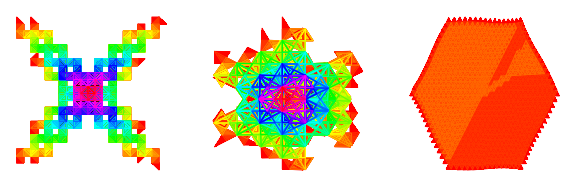

```mathematica
GraphicsRow[{showLengthIdeal[ST,30],showLengthIdeal[HT,30],showLengthIdeal[TT,30]},ImageSize->Large]
```

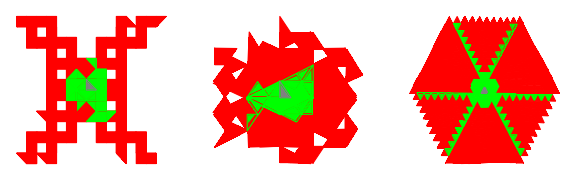

```mathematica
GraphicsRow[{showSmoothness[ST,20],showSmoothness[HT,20],showSmoothness[TT,20]},ImageSize->Large]
```

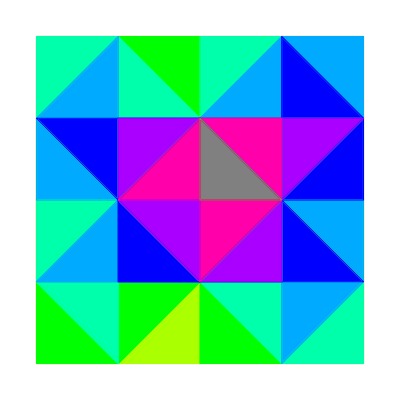
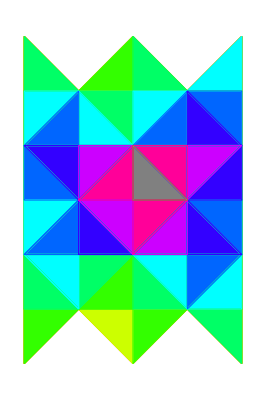
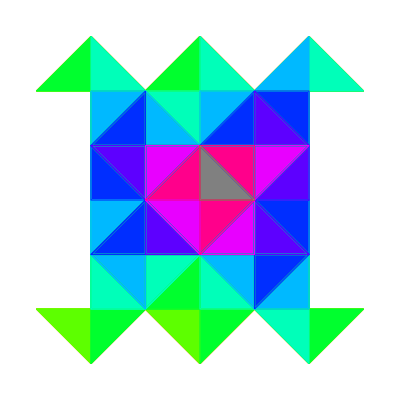
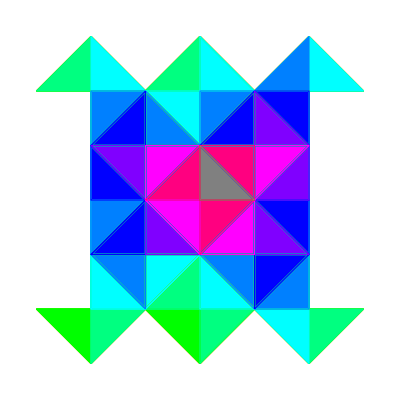
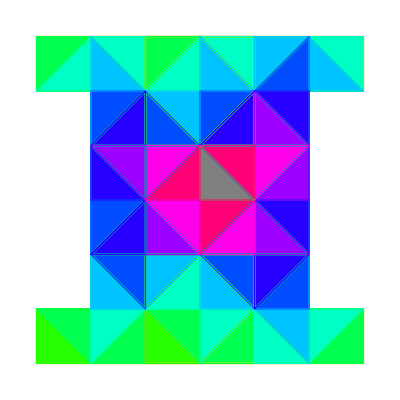
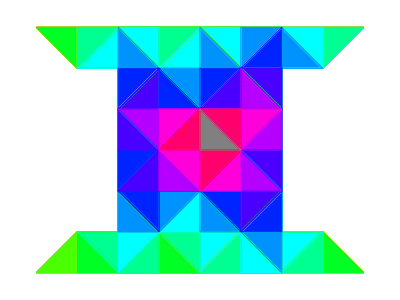
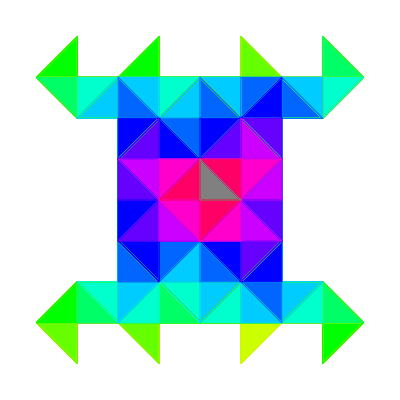
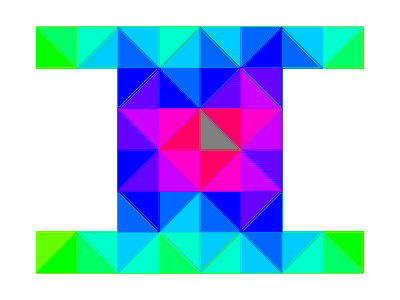

```mathematica
showNonSmoothBruhatIdeals[ST,15]
```

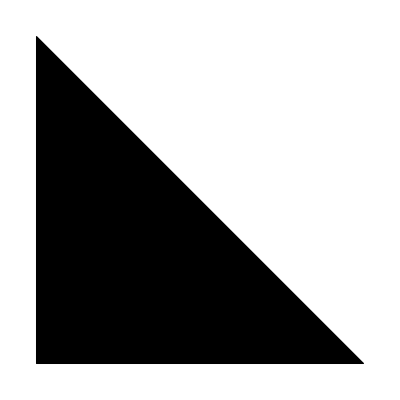
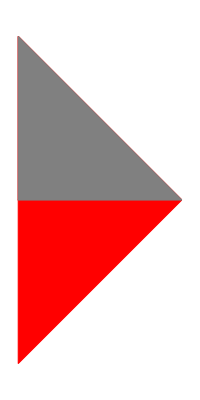
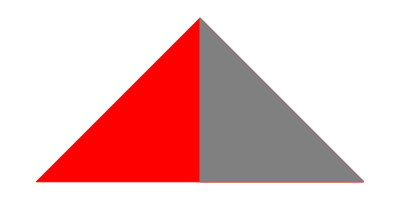
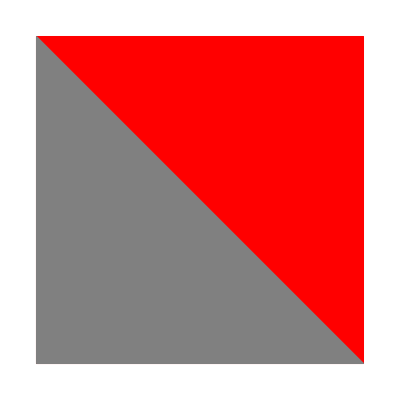
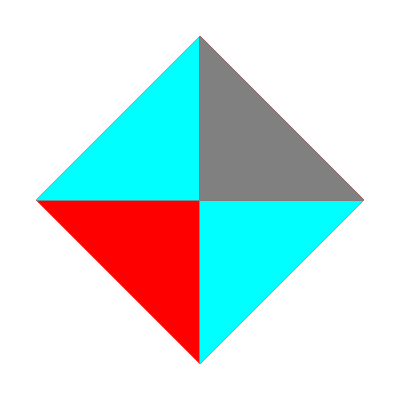
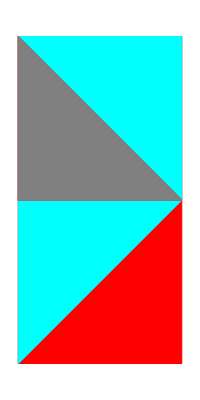
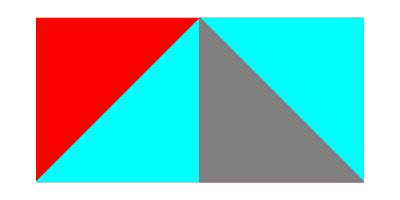
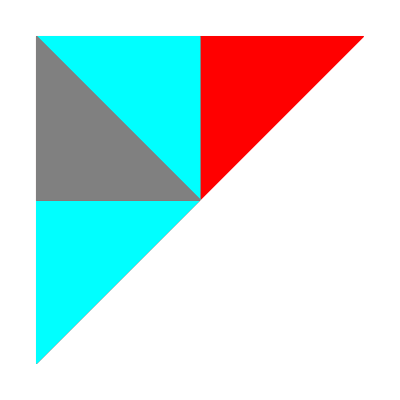
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
showSmoothBruhatIdeals[ST,15]
```

#### Hyperplane Arrangements

```mathematica
showHyperplanes[M_,k_]:=showHyperplanes[M,DeleteDuplicates[Flatten[inv[M,#]&/@Complement[lengthIdeal[M,k],lengthIdeal[M,k-1]]]]]
showInvArrangement[M_,""]:=showChambers[M,{""},Black]
showInvArrangement[M_,w_]:=Show[showHyperplanes[M,inv[M,w]],showChambers[M,{""},Black],showChambers[M,{w},Red]]
showInvArrangementBruhat[M_,w_]:=Show[showBruhatIdeal[M,w],showInvArrangement[M,w]]
showInvArrangementLeftBruhat[M_,w_]:=Show[showLeftBruhatIdeal[M,w],showInvArrangement[M,w]]
```

#### Hyperplane Arrangements Examples

```mathematica
GraphicsRow[{showInvArrangement[ST,"123123121"],showInvArrangementBruhat[ST,"123123121"],showInvArrangementLeftBruhat[ST,"123123121"]}]
```

-Graphics-

```mathematica
Show[showBruhatIdeal[TT,"123123123123123"],showHyperplanes[TT,inv[TT,"123123123123123"]]]
```

-Graphics-

## 2.5 Factorisation

### Polynomial Manipulation

```mathematica
zeroPolynomialQ[poly_,q_]:=CoefficientList[poly,q]=={}
polynomialDividesQ[poly1_,poly2_,q_]:=If[zeroPolynomialQ[PolynomialRemainder[poly1,poly2,q],q],True,False]
divideMult[m_,n_]:=Floor[m/n]
factorMults[factors1_,fac2_]:=divideMult[Select[factors1,#[[1]]==fac2[[1]]&][[1]][[2]],fac2[[2]]]
polynomialDividesMultiplicity[poly1_,poly2_,q_]:=0/;Not[polynomialDividesQ[poly1,poly2,q]]
polynomialDividesMultiplicity[poly1_,poly2_,q_]:=Module[{factors1,factors2,mult},
factors1=#&/@Complement[FactorList[poly1],{{1,1}}];
factors2=#&/@Complement[FactorList[poly2],{{1,1}}];
mult=factorMults[factors1,#]&/@factors2;
Min[mult]
]/;polynomialDividesQ[poly1,poly2,q]
removePolynomialFactors[poly1_,poly2_,q_]:=
Simplify[poly1/(poly2^polynomialDividesMultiplicity[poly1,poly2,q])]
removePolynomialFactors[poly1_,polyList_List,q_]:=
Simplify[poly1/Fold[Times,#^polynomialDividesMultiplicity[poly1,#,q]]&/@polyList]
```

### Quantum Factorisation

```mathematica
quantumPoly[k_,q_]:=Total[Table[( q)^i,{i,0,k}]]
quantumPolyQ[1,q_]:=True
quantumPolyQ[poly_,q_]:=CoefficientList[poly,q]==CoefficientList[quantumPoly[Max[1,Exponent[poly,q]],q],q]
quantumFactorQ[poly_,0,q_]:=True
quantumFactorQ[poly_,k_,q_]:=polynomialDividesQ[poly,quantumPoly[k,q],q]
quantumFactorsQ[poly_,q_]:=Fold[Or,Table[quantumFactorQ[poly,k,q],{k,1,Max[1,Exponent[poly,q]]}]]
removeQuantumFactors[poly_,q_]:=removePolynomialFactors[poly,Table[quantumFactorQ[poly,k,q],{k,1,Max[1,Exponent[poly,q]]}],q]
quantumFactorList[poly_,q_]:=Module[{d},
d=Max[1,Exponent[poly,q]];
Select[Table[{{k,q},polynomialDividesMultiplicity[poly,quantumPoly[k,q],q]},{k,1,d}],#[[2]]≥ 1&]
]
quantumFactorisation[poly_,q_]:=FactorList[poly]/;Not[quantumFactorsQ[poly,q]]
quantumFactorisation[poly_,q_]:=Module[{qfl,k,n,newP},
qfl=quantumFactorList[poly,q];
k=Max[#[[1]][[1]]&/@qfl];
n=polynomialDividesMultiplicity[poly,quantumPoly[k,q],q];
newP=removePolynomialFactors[poly,quantumPoly[k,q],q];
Join[quantumFactorisation[newP,q],{{quantumPoly[k,q],n}}]
]/;quantumFactorsQ[poly,q]
quantumFactorisationQ[poly_,q_]:=Fold[And,quantumPolyQ[#[[1]],q]&/@quantumFactorisation[poly,q]]
quantumFactorisationQ[M_List,w_String]:=quantumFactorisationQ[poincarePoly[M,w,q],q]
quantumFactorisationQ[M_List,wList_List]:=Fold[And,quantumFactorisationQ[poincarePoly[M,#,q],q]&/@wList]
quantumExponents[poly_,q_]:=If[quantumFactorisationQ[poly,q],Drop[Flatten[Table[Exponent[#[[1]],q],{i,1,#[[2]]}]&/@quantumFactorisation[poly,q]],1],{}]
quantumExponents[M_List,w_String]:=quantumExponents[poincarePoly[M,w,q],q]
quantumExponents[M_List,wList_List]:={#,quantumExponents[poincarePoly[M,#,q],q]}&/@wList
```

### q-Factorisation Property

```mathematica
qFactorisationProperty[M_,k_]:=
qFactorisationProperty[M,k]={#,quantumFactorisationQ[M,#]}&/@smoothElements[M,k]
qFactorisationPropertyQ[M_,k_]:=Fold[And,#[[2]]&/@qFactorisationProperty[M,k]]
qFactorisationPropertyQ[M_]:=qFactorisationPropertyQ[M,maxLength[M]]
```

H3

```mathematica
qFactorisationPropertyQ[H3]
```

True

H4

```mathematica
qFactorisationPropertyQ[H4,15]
```

$Aborted

F4

```mathematica
qFactorisationPropertyQ[F4,24]
```

True

### Visualisation

```mathematica
lexOrder[list1_,list2_]:=If[list1[[1]]<list2[[1]],True,If[list1[[1]]==list2[[1]],lexOrder[Drop[list1,1],Drop[list2,1]],False]]
lexOrder[{},list_]:=True
lexOrder[list_,{}]:=False/;Not[list=={}]
quantumExponentsVisualisation[M_,k_]:=Sort[{#,quantumExponents[poincarePoly[M,#,q],q],showInvArrangement[M,#]}&/@smoothElements[M,k],lexOrder[#1[[2]],#2[[2]]]&]
```

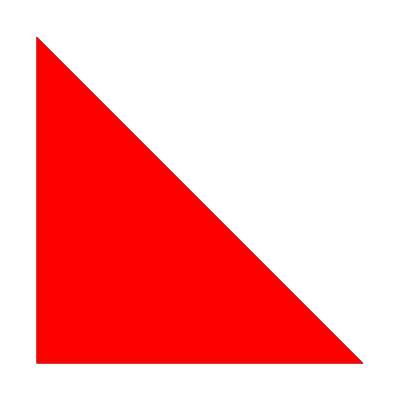
{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2123,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2312,{1,1,2},-Graphics-},{2313,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{3123,{1,1,2},-Graphics-},{12123,{1,1,3},-Graphics-},{13123,{1,1,3},-Graphics-},{21313,{1,1,3},-Graphics-},{23121,{1,1,3},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{212,{1,2},-Graphics-},{313,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{121231,{1,2,3},-Graphics-},{121313,{1,2,3},-Graphics-},{123121,{1,2,3},-Graphics-},{131231,{1,2,3},-Graphics-},{1212,{1,3},-Graphics-},{1313,{1,3},-Graphics-},{1212312,{1,3,3},-Graphics-},{1212313,{1,3,3},-Graphics-},{1312312,{1,3,3},-Graphics-},{1312313,{1,3,3},-Graphics-},{2123121,{1,3,3},-Graphics-},{3121313,{1,3,3},-Graphics-},{12123121,{1,3,4},-Graphics-},{13121313,{1,3,4},-Graphics-}}

```mathematica
quantumExponentsVisualisation[ST,15]
```

```mathematica
quantumExponentsVisualisation[HT,15]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2123,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2312,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{12123,{1,1,3},-Graphics-},{21213,{1,1,3},-Graphics-},{23121,{1,1,3},-Graphics-},{31212,{1,1,3},-Graphics-},{121213,{1,1,4},-Graphics-},{212123,{1,1,4},-Graphics-},{231212,{1,1,4},-Graphics-},{312121,{1,1,4},-Graphics-},{1212123,{1,1,5},-Graphics-},{2312121,{1,1,5},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{212,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{131212,{1,2,3},-Graphics-},{131213,{1,2,3},-Graphics-},{212131,{1,2,3},-Graphics-},{1212131,{1,2,4},-Graphics-},{1312121,{1,2,4},-Graphics-},{12121231,{1,2,5},-Graphics-},{12312121,{1,2,5},-Graphics-},{1212,{1,3},-Graphics-},{2121,{1,3},-Graphics-},{121212312,{1,3,5},-Graphics-},{212312121,{1,3,5},-Graphics-},{12121,{1,4},-Graphics-},{21212,{1,4},-Graphics-},{1212123121,{1,4,5},-Graphics-},{1212312121,{1,4,5},-Graphics-},{121212,{1,5},-Graphics-},{12121231212,{1,5,5},-Graphics-},{12121231213,{1,5,5},-Graphics-},{13121231212,{1,5,5},-Graphics-},{21212312121,{1,5,5},-Graphics-},{121212312121,{1,5,6},-Graphics-}}

```mathematica
quantumExponentsVisualisation[TT,15]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{32,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{132,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{321,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1232,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2321,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{232,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{12132,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{13123,{1,2,2},-Graphics-},{23121,{1,2,2},-Graphics-},{23213,{1,2,2},-Graphics-},{1213123,{2,2,3},-Graphics-},{1213213,{2,2,3},-Graphics-},{1312132,{2,2,3},-Graphics-},{1312312,{2,2,3},-Graphics-},{2312131,{2,2,3},-Graphics-},{2321321,{2,2,3},-Graphics-},{121312312,{2,3,4},-Graphics-},{121321321,{2,3,4},-Graphics-},{131213213,{2,3,4},-Graphics-},{131231231,{2,3,4},-Graphics-},{231213123,{2,3,4},-Graphics-},{232132132,{2,3,4},-Graphics-},{12131231231,{2,4,5},-Graphics-},{12132132132,{2,4,5},-Graphics-},{13121321321,{2,4,5},-Graphics-},{13123123123,{2,4,5},-Graphics-},{23121312312,{2,4,5},-Graphics-},{23213213213,{2,4,5},-Graphics-},{1213123123123,{2,5,6},-Graphics-},{1213213213213,{2,5,6},-Graphics-},{1312132132132,{2,5,6},-Graphics-},{1312312312312,{2,5,6},-Graphics-},{2312131231231,{2,5,6},-Graphics-},{2321321321321,{2,5,6},-Graphics-},{121312312312312,{2,6,7},-Graphics-},{121321321321321,{2,6,7},-Graphics-},{131213213213213,{2,6,7},-Graphics-},{131231231231231,{2,6,7},-Graphics-},{231213123123123,{2,6,7},-Graphics-},{232132132132132,{2,6,7},-Graphics-}}

```mathematica
quantumExponentsVisualisation[I2[12],12]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{12,{1,1},-Graphics-},{21,{1,1},-Graphics-},{121,{1,2},-Graphics-},{212,{1,2},-Graphics-},{1212,{1,3},-Graphics-},{2121,{1,3},-Graphics-},{12121,{1,4},-Graphics-},{21212,{1,4},-Graphics-},{121212,{1,5},-Graphics-},{212121,{1,5},-Graphics-},{1212121,{1,6},-Graphics-},{2121212,{1,6},-Graphics-},{12121212,{1,7},-Graphics-},{21212121,{1,7},-Graphics-},{121212121,{1,8},-Graphics-},{212121212,{1,8},-Graphics-},{1212121212,{1,9},-Graphics-},{2121212121,{1,9},-Graphics-},{12121212121,{1,10},-Graphics-},{21212121212,{1,10},-Graphics-},{121212121212,{1,11},-Graphics-}}

### Conjectures

```mathematica
letterCount[w_String]:=Sort[Union[makeList[w]]/.CharacterCounts[w]]
letterCounts[M_,w_String]:=DeleteDuplicates[letterCount[#]&/@reduce[M,w]]
centralGeneratorCount[M_,w_,s_]:=Length[Select[Sort[centralGenerator[#]&/@inv[M,w]],#==s&]]
centralGeneratorCounts[M_,w_]:=Sort[Select[Table[centralGeneratorCount[M,w,ToString[i]],{i,1,rank[M]}],Not[#==0]&]]
```

```mathematica
{#,letterCounts[TT,#][[1]]==quantumExponents[TT,#],centralGeneratorCounts[TT,#]==quantumExponents[TT,#]}&/@smoothElements[TT,15]
```

{{,True,True},{1,True,True},{12,True,True},{121,True,True},{1213,True,True},{12131,False,True},{1213123,True,False},{121312312,True,True},{12131231231,False,False},{1213123123123,False,False},{121312312312312,False,False},{12132,True,True},{1213213,True,True},{121321321,True,True},{12132132132,False,False},{1213213213213,False,False},{121321321321321,False,False},{123,True,True},{1232,True,True},{13,True,True},{131,True,True},{1312,True,True},{13121,False,True},{1312132,True,False},{131213213,True,True},{13121321321,False,False},{1312132132132,False,False},{131213213213213,False,False},{13123,True,True},{1312312,True,True},{131231231,True,True},{13123123123,False,False},{1312312312312,False,False},{131231231231231,False,False},{132,True,True},{2,True,True},{21,True,True},{213,True,True},{2131,True,True},{23,True,True},{231,True,True},{23121,True,True},{2312131,True,False},{231213123,False,False},{23121312312,False,False},{2312131231231,False,False},{231213123123123,False,False},{232,True,True},{2321,True,True},{23213,True,True},{2321321,True,True},{232132132,True,True},{23213213213,False,False},{2321321321321,False,False},{232132132132132,False,False},{3,True,True},{31,True,True},{312,True,True},{3121,True,True},{32,True,True},{321,True,True}}

```mathematica
centralGeneratorCounts[H3,#]&/@reduce[H3,"123123123123123"]
```

{{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8}}

## 2.6 Bruhat ideals

```mathematica
coxeterElement[M_]:=makeString[Table[i,{i,1,rank[M]}]]
w[M_,k_]:=makeString[Flatten[Fold[Join,Table[makeList[coxeterElement[M]],{i,1,k}]]]]
```

Type A[5]

```mathematica
bruhatIdeal[typeA[5],w[typeA[5],3]]={"","4","5","1","3","2","54","34","45","24","14","43","15","35","23","13","12","32","21","25","234","354","543","254","154","454","345","324","134","343","245","145","435","243","143","124","432","214","235","135","125","325","215","232","132","213","121","321","123","2354","2324","2134","2343","4354","3543","3254","1354","3454","2543","1543","2454","1454","2154","1254","4543","3245","1345","3435","3243","1343","1324","3432","3214","2435","1435","1245","2432","1432","2143","1243","1214","4325","2145","2325","1325","2135","1215","2321","1321","2132","1232","1213","3215","1235","24354","23254","21354","23543","23243","21343","21324","23432","23214","43543","43254","34354","14354","32543","13543","32454","13454","32154","13254","24543","14543","21543","12543","21454","12454","12154","34543","32435","13435","13245","32432","13432","32143","13243","13214","24325","14325","21435","12435","12145","21432","12432","12143","23215","13215","21325","12325","12135","21321","12321","12132","34325","32145","324354","243543","243254","214354","232543","213543","232154","213254","232432","213432","232143","213243","213214","432543","343543","143543","343254","143254","134354","324543","134543","321543","132543","321454","132454","132154","214543","124543","121543","121454","324325","134325","321435","132435","132145","321432","132432","132143","214325","124325","121435","121432","213215","123215","121325","121321","3243543","3243254","3214354","2432543","2143543","2143254","2321543","2132543","2132154","2321432","2132432","2132143","3432543","1432543","1343543","1343254","3214543","1324543","1321543","1321454","1214543","3214325","1324325","1321435","1321432","1214325","1213215","32432543","32143543","32143254","21432543","21321543","21321432","13432543","13214543","13214325","321432543"};
```

Type B[5]

```mathematica
bruhatIdeal[typeB[5],w[typeB[5],3]]={"","5","4","1","3","2","54","45","15","35","25","43","14","34","23","13","12","32","21","24","545","543","454","154","354","254","435","145","345","235","135","125","325","215","245","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","5435","4545","1545","3545","2545","4543","1543","3543","2543","4354","1454","3454","2354","1354","1254","3254","2154","2454","4325","1435","3435","2345","1345","1245","3245","2145","2325","1325","2135","1215","3215","1235","2435","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","54354","45435","15435","35435","25435","43545","14545","34545","23545","13545","12545","32545","21545","24545","43543","14543","34543","23543","13543","12543","32543","21543","24543","43254","14354","34354","23454","13454","12454","32454","21454","23254","13254","21354","12154","32154","12354","24354","14325","34325","23435","13435","12435","32435","21435","23245","13245","21345","12145","13215","21325","12325","12135","32145","12345","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","13214","21324","12324","12134","12321","12132","32143","21321","12343","24325","23215","543545","454354","154354","354354","254354","435435","145435","345435","235435","135435","125435","325435","215435","245435","432545","143545","343545","234545","134545","124545","324545","214545","232545","132545","213545","121545","321545","123545","243545","432543","143543","343543","234543","134543","124543","324543","214543","232543","132543","213543","121543","321543","123543","243543","143254","343254","234354","134354","124354","324354","214354","232454","132454","213454","121454","132154","213254","123254","121354","321454","123454","234325","134325","124325","324325","214325","232435","132435","213435","121435","232145","132145","213245","123245","121345","123215","121325","321435","213215","123435","232432","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243254","232154","4543545","1543545","3543545","2543545","4354354","1454354","3454354","2354354","1354354","1254354","3254354","2154354","2454354","4325435","1435435","3435435","2345435","1345435","1245435","3245435","2145435","2325435","1325435","2135435","1215435","3215435","1235435","2435435","1432545","3432545","2343545","1343545","1243545","3243545","2143545","2324545","1324545","2134545","1214545","1321545","2132545","1232545","1213545","3214545","1234545","2432545","2321545","1432543","3432543","2343543","1343543","1243543","3243543","2143543","2324543","1324543","2134543","1214543","1321543","2132543","1232543","1213543","3214543","1234543","2343254","1343254","1243254","3243254","2143254","2324354","1324354","2134354","1214354","2321454","1321454","2132454","1232454","1213454","1232154","1213254","3214354","2132154","1234354","2324325","1324325","2134325","1214325","2321435","1321435","2132435","1232435","1213435","2132145","1213245","1213215","1321432","2132432","1232432","1213432","2132143","1232143","1213243","1213214","3214325","1234325","1232145","2432543","2321543","2321432","43543545","14543545","34543545","23543545","13543545","12543545","32543545","21543545","24543545","43254354","14354354","34354354","23454354","13454354","12454354","32454354","21454354","23254354","13254354","21354354","12154354","32154354","12354354","24354354","14325435","34325435","23435435","13435435","12435435","32435435","21435435","23245435","13245435","21345435","12145435","13215435","21325435","12325435","12135435","32145435","12345435","23432545","13432545","12432545","32432545","21432545","23243545","13243545","21343545","12143545","23214545","13214545","21324545","12324545","12134545","12321545","12132545","32143545","21321545","12343545","24325435","23215435","23432543","13432543","12432543","32432543","21432543","23243543","13243543","21343543","12143543","23214543","13214543","21324543","12324543","12134543","12321543","12132543","32143543","21321543","12343543","23243254","13243254","21343254","12143254","23214354","13214354","21324354","12324354","12134354","21321454","12132454","12132154","23214325","21324325","12324325","12134325","21321435","12321435","12132435","12132145","12321432","12132432","12132143","32143254","21321432","12343254","12321454","13214325","432543545","143543545","343543545","234543545","134543545","124543545","324543545","214543545","232543545","132543545","213543545","121543545","321543545","123543545","243543545","143254354","343254354","234354354","134354354","124354354","324354354","214354354","232454354","132454354","213454354","121454354","132154354","213254354","123254354","121354354","321454354","123454354","234325435","134325435","124325435","324325435","214325435","232435435","132435435","213435435","121435435","232145435","132145435","213245435","123245435","121345435","123215435","121325435","321435435","213215435","123435435","232432545","132432545","213432545","121432545","232143545","132143545","213243545","123243545","121343545","213214545","121324545","121321545","321432545","123432545","123214545","243254354","232154354","232432543","132432543","213432543","121432543","232143543","132143543","213243543","123243543","121343543","213214543","121324543","121321543","232143254","132143254","213243254","123243254","121343254","213214354","123214354","121324354","121321454","213214325","121324325","121321435","121321432","321432543","123432543","123214543","123214325","1432543545","3432543545","2343543545","1343543545","1243543545","3243543545","2143543545","2324543545","1324543545","2134543545","1214543545","1321543545","2132543545","1232543545","1213543545","3214543545","1234543545","2343254354","1343254354","1243254354","3243254354","2143254354","2324354354","1324354354","2134354354","1214354354","2321454354","1321454354","2132454354","1232454354","1213454354","1232154354","1213254354","3214354354","2132154354","1234354354","2324325435","1324325435","2134325435","1214325435","2321435435","1321435435","2132435435","1232435435","1213435435","2132145435","1213245435","1213215435","1321432545","2132432545","1232432545","1213432545","2132143545","1232143545","1213243545","1213214545","3214325435","1234325435","1232145435","2321432543","1321432543","2132432543","1232432543","1213432543","2132143543","1232143543","1213243543","1213214543","1232143254","1213243254","1213214354","1213214325","2432543545","2321543545","2321432545","2132143254","23432543545","13432543545","12432543545","32432543545","21432543545","23243543545","13243543545","21343543545","12143543545","23214543545","13214543545","21324543545","12324543545","12134543545","12321543545","12132543545","32143543545","21321543545","12343543545","23243254354","13243254354","21343254354","12143254354","23214354354","13214354354","21324354354","12324354354","12134354354","21321454354","12132454354","12132154354","23214325435","13214325435","21324325435","12324325435","12134325435","21321435435","12321435435","12132435435","12132145435","12321432545","12132432545","12132143545","32143254354","21321432545","12343254354","12321454354","21321432543","12321432543","12132432543","12132143543","12132143254","232432543545","132432543545","213432543545","121432543545","232143543545","132143543545","213243543545","123243543545","121343543545","213214543545","121324543545","121321543545","232143254354","132143254354","213243254354","123243254354","121343254354","213214354354","123214354354","121324354354","121321454354","213214325435","121324325435","121321435435","121321432545","321432543545","123432543545","123214543545","123214325435","121321432543","2321432543545","1321432543545","2132432543545","1232432543545","1213432543545","2132143543545","1232143543545","1213243543545","1213214543545","2132143254354","1232143254354","1213243254354","1213214354354","1213214325435","21321432543545","12321432543545","12132432543545","12132143543545","12132143254354","121321432543545"};
```

Type D[5]

```mathematica
bruhatIdeal[typeD[5],w[typeD[5],3]]={"","5","4","1","3","2","53","45","15","35","25","43","14","34","23","13","12","32","21","24","534","532","453","153","353","253","435","145","345","235","135","125","325","215","245","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","5324","4534","1534","3534","2534","4532","1532","3532","2532","4353","1453","3453","2353","1353","1253","3253","2153","2453","4325","1435","3435","2345","1345","1245","3245","2145","2325","1325","2135","1215","3215","1235","2435","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","53243","45324","15324","35324","25324","43534","14534","34534","23534","13534","12534","32534","21534","24534","43532","14532","34532","23532","13532","12532","32532","21532","24532","43253","14353","34353","23453","13453","12453","32453","21453","23253","13253","21353","12153","32153","12353","24353","14325","34325","23435","13435","12435","32435","21435","23245","13245","21345","12145","13215","21325","12325","12135","32145","12345","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","21324","12324","12134","12321","12132","32143","21321","12343","24325","23215","13214","532435","453243","153243","353243","253243","435324","145324","345324","235324","135324","125324","325324","215324","245324","432534","143534","343534","234534","134534","124534","324534","214534","232534","132534","213534","121534","321534","123534","243534","432532","143532","343532","234532","134532","124532","324532","214532","232532","132532","213532","121532","321532","123532","243532","143253","343253","234353","134353","124353","324353","214353","232453","132453","213453","121453","132153","213253","123253","121353","321453","123453","234325","134325","124325","324325","214325","232435","132435","213435","121435","232145","213245","123245","121345","123215","121325","321435","213215","123435","232432","132432","213432","121432","232143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243253","232153","132143","132145","4532435","1532435","3532435","2532435","4353243","1453243","3453243","2353243","1353243","1253243","3253243","2153243","2453243","4325324","1435324","3435324","2345324","1345324","1245324","3245324","2145324","2325324","1325324","2135324","1215324","3215324","1235324","2435324","1432534","3432534","2343534","1343534","1243534","3243534","2143534","2324534","1324534","2134534","1214534","1321534","2132534","1232534","1213534","3214534","1234534","2432534","2321534","1432532","3432532","2343532","1343532","1243532","3243532","2143532","2324532","1324532","2134532","1214532","1321532","2132532","1232532","1213532","3214532","1234532","2343253","1343253","1243253","3243253","2143253","2324353","1324353","2134353","1214353","2321453","1321453","2132453","1232453","1213453","1232153","1213253","3214353","2132153","1234353","2324325","1324325","2134325","1214325","2321435","1321435","2132435","1232435","1213435","2132145","1213245","1213215","2321432","1321432","2132432","1232432","1213432","2132143","1213243","1213214","3214325","1234325","1232145","2432532","2321532","1232143","43532435","14532435","34532435","23532435","13532435","12532435","32532435","21532435","24532435","43253243","14353243","34353243","23453243","13453243","12453243","32453243","21453243","23253243","13253243","21353243","12153243","32153243","12353243","24353243","14325324","34325324","23435324","13435324","12435324","32435324","21435324","23245324","13245324","21345324","12145324","13215324","21325324","12325324","12135324","32145324","12345324","23432534","13432534","12432534","32432534","21432534","23243534","13243534","21343534","12143534","23214534","13214534","21324534","12324534","12134534","12321534","12132534","32143534","21321534","12343534","23432532","13432532","12432532","32432532","21432532","23243532","13243532","21343532","12143532","23214532","13214532","21324532","12324532","12134532","12321532","12132532","32143532","21321532","12343532","23243253","13243253","21343253","12143253","23214353","13214353","21324353","12324353","12134353","12132453","12132153","23214325","13214325","21324325","12324325","12134325","12321435","12132435","12132145","21321432","12132432","12132143","32143253","12343253","12321453","12321432","24325324","23215324","21321435","21321453","432532435","143532435","343532435","234532435","134532435","124532435","324532435","214532435","232532435","132532435","213532435","121532435","321532435","123532435","243532435","143253243","343253243","234353243","134353243","124353243","324353243","214353243","232453243","132453243","213453243","121453243","132153243","213253243","123253243","121353243","321453243","123453243","234325324","134325324","124325324","324325324","214325324","232435324","132435324","213435324","121435324","232145324","132145324","213245324","123245324","121345324","123215324","121325324","321435324","213215324","123435324","232432534","132432534","213432534","121432534","232143534","132143534","213243534","123243534","121343534","213214534","121324534","121321534","321432534","123432534","123214534","232432532","132432532","213432532","121432532","232143532","132143532","213243532","123243532","121343532","213214532","121324532","121321532","232143253","132143253","213243253","123243253","121343253","123214353","121324353","121321453","213214325","123214325","121324325","121321432","321432532","123432532","123214532","121321435","243253243","232153243","213214353","1432532435","3432532435","2343532435","1343532435","1243532435","3243532435","2143532435","2324532435","1324532435","2134532435","1214532435","1321532435","2132532435","1232532435","1213532435","3214532435","1234532435","2343253243","1343253243","1243253243","3243253243","2143253243","2324353243","1324353243","2134353243","1214353243","2321453243","1321453243","2132453243","1232453243","1213453243","1232153243","1213253243","3214353243","2132153243","1234353243","2324325324","1324325324","2134325324","1214325324","2321435324","1321435324","2132435324","1232435324","1213435324","2132145324","1213245324","1213215324","1321432534","2132432534","1232432534","1213432534","2132143534","1232143534","1213243534","1213214534","2321432532","1321432532","2132432532","1232432532","1213432532","2132143532","1232143532","1213243532","2132143253","1232143253","1213243253","1213214353","1213214325","3214325324","1234325324","1232145324","2432532435","2321532435","2321432534","1213214532","23432532435","13432532435","12432532435","32432532435","21432532435","23243532435","13243532435","21343532435","12143532435","23214532435","13214532435","21324532435","12324532435","12134532435","12321532435","12132532435","32143532435","21321532435","12343532435","23243253243","13243253243","21343253243","12143253243","23214353243","13214353243","21324353243","12324353243","12134353243","21321453243","12132453243","12132153243","23214325324","13214325324","21324325324","12324325324","12134325324","21321435324","12321435324","12132435324","12132145324","12321432534","12132432534","12132143534","21321432532","12321432532","12132432532","12132143253","32143253243","21321432534","12343253243","12321453243","12132143532","232432532435","132432532435","213432532435","121432532435","232143532435","132143532435","213243532435","123243532435","121343532435","213214532435","121324532435","121321532435","232143253243","132143253243","213243253243","123243253243","121343253243","213214353243","123214353243","121324353243","121321453243","213214325324","121324325324","121321435324","121321432534","121321432532","321432532435","123432532435","123214532435","123214325324","2321432532435","1321432532435","2132432532435","1232432532435","1213432532435","2132143532435","1232143532435","1213243532435","1213214532435","2132143253243","1232143253243","1213243253243","1213214353243","1213214325324","21321432532435","12321432532435","12132432532435","12132143532435","12132143253243","121321432532435"};
```

F4

```mathematica
bruhatIdeal[F4,w[F4,3]]={"","4","3","2","1","43","34","24","14","13","32","21","23","12","432","343","243","143","324","214","234","124","134","323","232","132","213","121","321","123","4323","1432","3432","2432","3243","2143","2343","1243","3234","1324","2134","1214","3214","1234","2324","1343","2323","1323","2321","1321","2132","1232","1213","3213","43234","14323","34323","24323","13432","32432","21432","23432","12432","32343","13243","21343","12143","32143","12343","23243","13234","23214","13214","12324","12134","32134","23234","21324","32132","23213","13213","21323","12323","21321","12321","12132","143234","343234","243234","134323","324323","214323","323432","232432","132432","213432","121432","321432","123432","234323","124323","132343","232143","132143","123243","121343","321343","232134","132134","123234","213214","121324","321324","213234","123214","321323","232132","132132","232343","213243","213213","123213","121323","121321","1343234","3243234","2143234","3234323","2324323","1324323","2134323","1214323","3214323","1234323","2323432","1323432","2321432","1321432","2132432","1232432","1213432","3213432","2321343","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2321324","1321324","2132134","1213234","2321323","1321323","3213234","1213214","2132132","1232132","2343234","1243234","1232134","1213213","32343234","23243234","13243234","21343234","12143234","32143234","12343234","23234323","13234323","23214323","13214323","21324323","12324323","12134323","23213432","13213432","21323432","12323432","21321432","12321432","12132432","32134323","23213243","13213243","21321343","12132343","23213234","13213234","21321324","12321324","12132134","21321323","12321323","32132343","12321343","12132143","12132132","232343234","132343234","232143234","132143234","213243234","123243234","121343234","232134323","132134323","213234323","123234323","213214323","123214323","121324323","213213432","123213432","121323432","232132343","132132343","213213243","123213243","121321343","213213234","123213234","121321324","121321323","321343234","121321432","2321343234","1321343234","2132343234","1232343234","2132143234","1232143234","1213243234","2132134323","1232134323","1213234323","1213214323","1213213432","2132132343","1232132343","1213213243","1213213234","21321343234","12321343234","12132343234","12132143234","12132134323","12132132343","121321343234"};
bruhatIdeal[F4,w[F4,4]]={"","4","1","3","2","43","34","24","14","23","13","12","32","21","432","343","243","143","324","214","234","124","323","134","232","132","213","121","321","123","4321","4323","3432","2432","1432","3243","2143","2343","1243","1343","3234","1324","2134","1214","3214","1234","2324","1323","3213","2323","2321","1321","2132","1232","1213","43234","43213","14321","34321","24321","34323","24323","14323","32432","21432","23432","12432","32343","21343","12143","32143","12343","23243","13432","13234","23214","13214","12324","12134","32134","23213","13213","12323","32132","21323","23234","21321","12321","12132","21324","13243","432134","343234","243234","143234","432132","143213","343213","243213","134321","324321","214321","234321","124321","324323","214323","234323","124323","323432","132432","213432","121432","321432","123432","232432","132343","232143","132143","123243","121343","321343","232343","213243","232134","132134","123234","213214","121324","321324","213234","123214","232132","132132","213213","121323","321323","123213","134323","121321","4321324","1432134","3432134","2432134","1343234","3243234","2143234","2343234","1243234","4321323","1432132","3432132","2432132","1343213","3243213","2143213","3234321","2324321","1324321","2134321","1214321","3214321","1234321","2343213","1243213","3234323","1324323","2134323","1214323","3214323","1234323","2324323","1323432","2321432","1321432","1232432","1213432","3213432","2321343","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2323432","2132432","2321324","1321324","2132134","1213234","2321323","1321323","2132132","1232132","1213213","3213234","1232134","1213214","43213243","43213234","14321324","34321324","24321324","13432134","32432134","21432134","23432134","12432134","32343234","13243234","21343234","12143234","32143234","12343234","23243234","14321323","34321323","24321323","13432132","32432132","21432132","32343213","23243213","13243213","21343213","12143213","32143213","12343213","23234321","13234321","23214321","13214321","21324321","12324321","12134321","32134321","23432132","12432132","13234323","23214323","13214323","12324323","12134323","32134323","23213432","13213432","12323432","21321432","12132432","32132432","21323432","12321432","23213243","13213243","21321343","12132343","32132343","12321343","12132143","23213234","13213234","21321324","12321324","12132134","21321323","12321323","12132132","23234323","21324323","432132343","143213243","343213243","243213243","143213234","343213234","243213234","134321324","324321324","214321324","323432134","232432134","132432134","213432134","121432134","321432134","123432134","232343234","132343234","232143234","132143234","213243234","123243234","121343234","321343234","234321324","124321324","134321323","324321323","214321323","234321323","124321323","323432132","232432132","132432132","213432132","121432132","321432132","123432132","232343213","132343213","232143213","132143213","213243213","123243213","121343213","232134321","132134321","213234321","123234321","213214321","123214321","121324321","321343213","232134323","132134323","123234323","213214323","121324323","321324323","213234323","123214323","232132432","132132432","213213432","121323432","232132343","132132343","213213243","123213243","121321343","321323432","123213432","121321432","213213234","123213234","121321324","121321323","1432132343","3432132343","2432132343","1343213243","3243213243","2143213243","2343213243","1243213243","1343213234","3243213234","2143213234","3234321324","2324321324","1324321324","2134321324","1214321324","3214321324","1234321324","2323432134","1323432134","2321432134","1321432134","2132432134","1232432134","1213432134","3213432134","2321343234","1321343234","1232343234","2132143234","1213243234","3213243234","2132343234","1232143234","3234321323","2324321323","1324321323","2134321323","1214321323","3214321323","1234321323","2343213234","1243213234","2323432132","1323432132","2321432132","1321432132","2132432132","1232432132","1213432132","2321343213","1321343213","2132343213","1232343213","2132143213","1232143213","1213243213","2132134321","1232134321","1213214321","3213432132","1213234321","2321324323","1321324323","2132134323","1213234323","2321323432","1321323432","2132132432","1232132432","1213213432","2132132343","1213213243","3213234323","1232134323","1232132343","1213214323","1213213234","13432132343","32432132343","21432132343","32343213243","23243213243","13243213243","21343213243","12143213243","32143213243","12343213243","32132343234","32343213234","23243213234","13243213234","21343213234","12143213234","32143213234","12343213234","23234321324","13234321324","23214321324","13214321324","21324321324","12324321324","12134321324","23213432134","13213432134","21323432134","12323432134","21321432134","12321432134","23213243234","13213243234","21321343234","12321343234","12132343234","12132143234","32134321324","23234321323","13234321323","23214321323","13214321323","21324321323","12324321323","12134321323","32134321323","23213432132","13213432132","21323432132","12323432132","21321432132","12321432132","12132432132","21321343213","12321343213","12132343213","12132134321","23213234323","13213234323","21321324323","12321324323","12132134323","21321323432","12321323432","12132132432","12132132343","23432132343","12432132343","12132432134","12132143213","323432132343","232432132343","132432132343","213432132343","121432132343","321432132343","123432132343","232343213243","132343213243","232143213243","132143213243","213243213243","123243213243","121343213243","232132343234","132132343234","321343213243","232343213234","132343213234","232143213234","132143213234","213243213234","123243213234","121343213234","232134321324","132134321324","213234321324","123234321324","213214321324","123214321324","121324321324","213213432134","123213432134","121321432134","123213243234","121321343234","232134321323","132134321323","213234321323","123234321323","213214321323","123214321323","121324321323","321343213234","213213243234","121323432134","213213432132","123213432132","121323432132","121321432132","121321343213","213213234323","123213234323","121321324323","121321323432","2323432132343","1323432132343","2321432132343","1321432132343","2132432132343","1232432132343","1213432132343","2321343213243","1321343213243","2132343213243","1232343213243","2132143213243","1232143213243","1213243213243","1232132343234","2321343213234","1321343213234","2132343213234","1232343213234","2132143213234","1232143213234","1213243213234","2132134321324","1232134321324","1213234321324","1213214321324","1213213432134","1213213243234","2132134321323","1232134321323","1213234321323","1213214321323","3213432132343","2132132343234","1213213432132","1213213234323","23213432132343","13213432132343","21323432132343","12323432132343","21321432132343","12321432132343","12132432132343","21321343213243","12321343213243","12132343213243","12132143213243","12132132343234","21321343213234","12321343213234","12132343213234","12132143213234","12132134321324","12132134321323","213213432132343","123213432132343","121323432132343","121321432132343","121321343213243","121321343213234","1213213432132343"};
bruhatIdeal[F4,w[F4,5]]={"","4","3","2","1","43","34","24","14","13","32","21","23","12","432","343","243","143","324","214","234","124","134","323","232","132","213","121","321","123","4323","4321","3432","2432","1432","3243","2143","2343","1243","3234","1324","2134","1214","3214","1234","2324","1343","2323","1323","2321","1321","2132","1232","1213","3213","43234","43213","34323","24323","14323","34321","24321","14321","32432","21432","23432","12432","32343","13243","21343","12143","32143","12343","23243","13234","23214","13214","12324","12134","32134","23234","21324","32132","23213","13213","21323","12323","21321","12321","12132","13432","432134","343234","243234","143234","432132","343213","243213","143213","324323","214323","234323","124323","134323","324321","214321","234321","124321","323432","132432","213432","121432","321432","123432","232432","132343","232143","132143","123243","121343","321343","232134","132134","123234","213214","121324","321324","213234","123214","321323","232132","132132","232343","213243","213213","123213","121321","134321","121323","4321324","3432134","2432134","1432134","3243234","2143234","2343234","1243234","1343234","4321323","3432132","2432132","1432132","3243213","2143213","2343213","1243213","3234323","1324323","2134323","3214323","1234323","2324323","1343213","3234321","1324321","2134321","1214321","3214321","1234321","2324321","1323432","2321432","1321432","1232432","1213432","3213432","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2321324","1321324","2132134","1213234","2321323","1321323","3213234","1232134","1213214","2132132","1232132","2323432","2132432","1213213","2321343","1214323","43213243","43213234","34321324","24321324","14321324","32432134","21432134","23432134","12432134","32343234","13243234","21343234","12143234","32143234","12343234","23243234","13432134","34321323","24321323","14321323","32432132","21432132","23432132","12432132","32343213","13243213","21343213","12143213","32143213","12343213","23243213","13234323","23214323","13214323","12324323","12134323","32134323","23234323","21324323","13432132","13234321","23214321","13214321","12324321","12134321","32134321","23213432","13213432","12323432","21321432","12132432","32132432","21323432","12321432","23213243","13213243","21321343","12132343","23213234","21321324","12321324","12132134","21321323","12321323","32132343","12321343","12132143","12132132","23234321","21324321","13213234","432132432","432132343","343213243","243213243","143213243","343213234","243213234","143213234","324321324","214321324","234321324","124321324","323432134","132432134","213432134","121432134","321432134","123432134","232432134","132343234","232143234","123243234","121343234","321343234","232343234","213243234","134321324","324321323","214321323","234321323","124321323","323432132","132432132","213432132","121432132","321432132","123432132","232432132","132343213","232143213","132143213","123243213","121343213","321343213","232134323","132134323","123234323","213214323","121324323","321324323","213234323","123214323","232343213","213243213","134321323","232134321","132134321","123234321","213214321","121324321","321324321","213234321","123214321","232132432","132132432","213213432","121323432","232132343","132132343","213213243","123213243","121321343","213213234","121321324","121321323","321323432","123213234","121321432","132143234","123213432","4321323432","3432132432","2432132432","1432132432","3432132343","2432132343","1432132343","3243213243","2143213243","2343213243","1243213243","1343213243","3243213234","2143213234","2343213234","1243213234","3234321324","1324321324","2134321324","1214321324","3214321324","1234321324","2324321324","1323432134","2321432134","1321432134","1232432134","1213432134","3213432134","2321343234","1321343234","1232343234","2132143234","1213243234","3213243234","2132343234","1232143234","2323432134","2132432134","3234321323","1324321323","2134321323","1214321323","3214321323","1234321323","2324321323","1323432132","2321432132","1321432132","1232432132","1213432132","3213432132","2321343213","1321343213","1232343213","2132143213","1213243213","3213243213","2132343213","1232143213","2321324323","1321324323","2132134323","1213234323","3213234323","1232134323","1213214323","2323432132","2132432132","1343213234","2321324321","1321324321","2132134321","1213234321","2321323432","1321323432","2132132432","1232132432","1213213432","1232132343","1213213243","1213213234","3213234321","2132132343","1232134321","1213214321","43213234323","34321323432","24321323432","14321323432","32432132432","21432132432","23432132432","12432132432","13432132432","32432132343","21432132343","23432132343","12432132343","32343213243","13243213243","21343213243","12143213243","32143213243","12343213243","23243213243","13432132343","32343213234","13243213234","21343213234","12143213234","32143213234","12343213234","23243213234","13234321324","23214321324","13214321324","12324321324","12134321324","32134321324","23213432134","13213432134","12323432134","21321432134","12132432134","32132432134","21323432134","12321432134","23213243234","13213243234","21321343234","12132343234","32132343234","12321343234","12132143234","23234321324","21324321324","13234321323","23214321323","13214321323","12324321323","12134321323","32134321323","23213432132","13213432132","12323432132","21321432132","12132432132","32132432132","21323432132","12321432132","23213243213","13213243213","21321343213","12132343213","23213234323","21321324323","12321324323","12132134323","32132343213","12321343213","12132143213","23234321323","21324321323","13213234323","23213234321","13213234321","21321324321","12321324321","12132134321","21321323432","12321323432","12132132432","12132132343","343213234323","243213234323","143213234323","324321323432","214321323432","234321323432","124321323432","323432132432","132432132432","213432132432","121432132432","321432132432","123432132432","232432132432","323432132343","132432132343","213432132343","121432132343","321432132343","123432132343","232432132343","132343213243","232143213243","132143213243","123243213243","121343213243","321343213243","232343213243","213243213243","134321323432","132343213234","232143213234","132143213234","123243213234","121343213234","321343213234","232134321324","132134321324","123234321324","213214321324","121324321324","321324321324","213234321324","123214321324","232132432134","132132432134","213213432134","121323432134","232132343234","213213243234","123213243234","121321343234","321323432134","123213432134","121321432134","232134321323","132134321323","123234321323","213214321323","121324321323","321324321323","213234321323","123214321323","232132432132","132132432132","213213432132","121323432132","232132343213","132132343213","213213243213","123213243213","121321343213","213213234323","121321324323","321323432132","123213432132","123213234323","121321432132","232343213234","213243213234","132132343234","213213234321","123213234321","121321324321","121321323432","3243213234323","2143213234323","2343213234323","1243213234323","3234321323432","1324321323432","2134321323432","1214321323432","3214321323432","1234321323432","2324321323432","1323432132432","2321432132432","1321432132432","1232432132432","1213432132432","3213432132432","2323432132432","2132432132432","1323432132343","2321432132343","1321432132343","1232432132343","1213432132343","3213432132343","2321343213243","1321343213243","1232343213243","2132143213243","1213243213243","3213243213243","2132343213243","1232143213243","2323432132343","2132432132343","2321343213234","1321343213234","1232343213234","2132143213234","1213243213234","3213243213234","2132343213234","1232143213234","2321324321324","1321324321324","2132134321324","1213234321324","2321323432134","1321323432134","2132132432134","1232132432134","1213213432134","2132132343234","1213213243234","3213234321324","1232134321324","1232132343234","1213214321324","2321324321323","1321324321323","2132134321323","1213234321323","2321323432132","1321323432132","2132132432132","1232132432132","1213213432132","1232132343213","1213213243213","1213213234323","3213234321323","2132132343213","1232134321323","1213214321323","1343213234323","1213213234321","32343213234323","13243213234323","21343213234323","12143213234323","32143213234323","12343213234323","23243213234323","13234321323432","23214321323432","13214321323432","12324321323432","12134321323432","32134321323432","23213432132432","13213432132432","12323432132432","21321432132432","12132432132432","32132432132432","21323432132432","12321432132432","23213432132343","13213432132343","12323432132343","21321432132343","12132432132343","32132432132343","21323432132343","12321432132343","23213243213243","13213243213243","21321343213243","12132343213243","32132343213243","12321343213243","12132143213243","23234321323432","21324321323432","23213243213234","13213243213234","21321343213234","12132343213234","23213234321324","13213234321324","21321324321324","12321324321324","12132134321324","12321323432134","12132132432134","12132132343234","23213234321323","13213234321323","21321324321323","12321324321323","12132134321323","21321323432132","12321323432132","12132132432132","12132132343213","32132343213234","21321323432134","12321343213234","12132143213234","132343213234323","232143213234323","132143213234323","123243213234323","121343213234323","321343213234323","232134321323432","132134321323432","123234321323432","213214321323432","121324321323432","321324321323432","213234321323432","123214321323432","232132432132432","132132432132432","213213432132432","121323432132432","321323432132432","123213432132432","121321432132432","232132432132343","132132432132343","213213432132343","121323432132343","232132343213243","132132343213243","123213243213243","121321343213243","321323432132343","123213432132343","121321432132343","232132343213234","132132343213234","213213243213234","123213243213234","121321343213234","213213234321324","123213234321324","121321324321324","121321323432134","213213234321323","123213234321323","121321323432132","232343213234323","213243213234323","213213243213243","121321324321323","2321343213234323","1321343213234323","1232343213234323","2132143213234323","1213243213234323","3213243213234323","2132343213234323","1232143213234323","2321324321323432","1321324321323432","2132134321323432","1213234321323432","2321323432132432","1321323432132432","2132132432132432","1232132432132432","1213213432132432","2321323432132343","1321323432132343","2132132432132343","1232132432132343","1213213432132343","2132132343213243","1232132343213243","1213213243213243","3213234321323432","1232134321323432","1213214321323432","2132132343213234","1232132343213234","1213213243213234","1213213234321324","1213213234321323","23213243213234323","13213243213234323","21321343213234323","12132343213234323","23213234321323432","13213234321323432","21321324321323432","12321324321323432","12132134321323432","21321323432132432","12321323432132432","12321323432132343","12132132432132343","12132132343213243","32132343213234323","21321323432132343","12321343213234323","12132143213234323","12132132432132432","12132132343213234","232132343213234323","132132343213234323","213213243213234323","123213243213234323","121321343213234323","213213234321323432","123213234321323432","121321324321323432","121321323432132432","121321323432132343","2132132343213234323","1232132343213234323","1213213243213234323","1213213234321323432","12132132343213234323"};
```

H3

```mathematica
bruhatIdealList[H3,w[H3,5]]={"","1","12","123","1232","12321","12323","2","21","23","232","2321","2323","3","32","321","323","3232","32321","121","123213","1232132","12321323","123213232","1232132321","13","132","1323","13232","132321","213","2132","21323","213232","2132321","23213","232132","2321323","23213232","232132321","23232","3213","32132","321323","3213232","32132321","1213","12132","121323","123232","1321","21321","232321","321321","121321","1213232","1232321","13213","132132","1321323","213213","2132132","21321323","2321321","3213213","32132132","321321323","1213213","12132132","121321323","12132321","12321321","1321321","13213232","21321321","213213232","23213213","232132132","321321321","1213213232","123213213","1232132132","132132321","2132132321","2321321321","12132132321","12321321321","13213213","132132132","1321321323","213213213","2132132132","21321321323","2321321323","3213213213","32132132132","321321321323","121321321","1213213213","12132132132","12321321323","1321321321","21321321321","23213213213","121321321321","123213213213","121321321323","13213213213","132132132132","213213213213","2132132132132","232132132132","1321321321323","2321321321323","1213213213213","1232132132132","21321321321323","12132132132132","12321321321323","121321321321323"};
```

H4

```mathematica
bruhatIdeal[H4,w[H4,3]]={"","4","1","3","2","43","14","34","23","13","12","32","21","24","434","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","4343","4324","1434","3434","2434","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","43243","14343","34343","24343","14324","34324","23434","13434","12434","32434","21434","24324","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","21324","12324","12134","12321","12132","32143","21321","12343","13214","432434","143243","343243","234343","134343","124343","324343","214343","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","243243","232432","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","1432434","3432434","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","1214343","3214343","1234343","2324324","1324324","2134324","1214324","1321434","2132434","1232434","1213434","3214324","1234324","2321432","1321432","2132432","1232432","1213432","2132143","1232143","1213243","1213214","2432434","2321434","23432434","13432434","12432434","32432434","21432434","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","23214324","13214324","21324324","12324324","12134324","21321434","12321434","12132434","32143243","12343243","21321432","12321432","12132432","12132143","232432434","132432434","213432434","121432434","232143243","132143243","213243243","123243243","121343243","123214343","121324343","213214324","121324324","121321434","321432434","213214343","123432434","123214324","121321432","2321432434","1321432434","2132432434","1232432434","1213432434","2132143243","1232143243","1213243243","1213214343","1213214324","21321432434","12321432434","12132432434","12132143243","121321432434"};
bruhatIdeal[H4,w[H4,4]]={"","4","1","3","2","43","14","34","23","12","32","21","24","13","434","432","143","343","234","134","124","324","214","213","121","321","123","243","232","132","4343","4324","1434","3434","2434","4321","1432","3432","2343","1343","1243","3243","2143","1324","2134","1214","1321","2132","1213","3214","1234","2432","2321","2324","1232","43432","43243","14343","34343","24343","43214","14324","34324","23434","12434","32434","21434","24324","14321","34321","23432","13432","12432","32432","21432","13243","21343","12143","23214","13214","21324","12134","12321","12132","32143","21321","12343","24321","12324","23243","13434","432434","432432","143432","343432","243432","432143","143243","343243","234343","134343","124343","324343","214343","243243","143214","343214","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","234321","134321","124321","324321","214321","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243214","232432","4324343","4324324","4321434","1432434","3432434","2432434","4321432","1432432","3432432","2343432","1343432","1243432","3243432","2143432","2432432","1432143","3432143","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","1214343","3214343","1234343","2343214","1343214","1243214","3243214","2143214","2324324","1324324","2134324","1214324","2321434","1321434","2132434","1232434","1213434","3214324","1234324","2324321","1324321","2134321","1214321","2321432","1321432","2132432","1232432","1213432","2132143","1232143","1213214","3214321","1234321","1213243","2432143","43243243","43214343","14324343","34324343","24324343","43214324","14324324","34324324","24324324","14321434","34321434","23432434","13432434","12432434","32432434","21432434","24321434","14321432","34321432","23432432","13432432","12432432","32432432","21432432","23243432","13243432","21343432","12143432","32143432","12343432","23432143","13432143","12432143","32432143","21432143","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","32143243","12343243","23243214","13243214","21343214","12143214","23214324","13214324","21324324","12324324","12134324","21321434","12321434","23214321","13214321","21324321","12134321","21321432","12321432","12132432","12132143","32143214","12343214","12132434","24321432","12324321","432432434","432143243","143243243","343243243","243243243","143214343","343214343","234324343","134324343","124324343","324324343","214324343","243214343","143214324","343214324","234324324","134324324","124324324","324324324","214324324","234321434","134321434","124321434","324321434","214321434","132432434","213432434","121432434","321432434","123432434","243214324","234321432","134321432","124321432","324321432","214321432","232432432","132432432","213432432","121432432","232143432","132143432","213243432","123243432","121343432","321432432","123432432","232432143","132432143","213432143","121432143","232143243","132143243","213243243","123243243","121343243","213214343","123214343","232143214","132143214","213243214","123243214","213214324","123214324","121324324","121321434","213214321","121324321","121321432","321432143","123432143","123214321","121324343","232432434","121343214","4321432434","1432432434","3432432434","2432432434","1432143243","3432143243","2343243243","1343243243","1243243243","3243243243","2143243243","2343214343","1343214343","1243214343","3243214343","2143214343","2324324343","1324324343","2134324343","1214324343","3214324343","1234324343","2343214324","1343214324","1243214324","3243214324","2143214324","2324324324","1324324324","2134324324","1214324324","3214324324","1234324324","2324321434","1324321434","2134321434","1214321434","2321432434","1321432434","2132432434","1232432434","1213432434","3214321434","1234321434","2432143243","2324321432","1324321432","2134321432","1214321432","2321432432","1321432432","2132432432","1232432432","1213432432","2132143432","1232143432","2321432143","1321432143","2132432143","1232432143","1213432143","2132143243","1232143243","1213243243","1213214343","2132143214","1232143214","1213214324","1213214321","3214321432","1234321432","1213243432","1213243214","14321432434","34321432434","23432432434","13432432434","12432432434","32432432434","21432432434","23432143243","13432143243","12432143243","32432143243","21432143243","23243243243","13243243243","21343243243","12143243243","32143243243","12343243243","23243214343","13243214343","21343214343","12143214343","23214324343","13214324343","21324324343","12324324343","12134324343","32143214343","12343214343","23243214324","13243214324","21343214324","12143214324","23214324324","13214324324","12324324324","12134324324","23214321434","13214321434","21324321434","12134321434","21321432434","12321432434","12132432434","32143214324","12343214324","23214321432","13214321432","21324321432","12324321432","12134321432","21321432432","12321432432","12132432432","12132143432","21321432143","12321432143","12132432143","12132143243","12132143214","24321432434","21324324324","12324321434","234321432434","134321432434","124321432434","324321432434","214321432434","232432432434","132432432434","213432432434","121432432434","321432432434","123432432434","232432143243","132432143243","213432143243","121432143243","232143243243","132143243243","213243243243","123243243243","121343243243","232143214343","132143214343","213243214343","123243214343","121343214343","213214324343","123214324343","121324324343","232143214324","132143214324","213243214324","123243214324","121343214324","213214324324","123214324324","121324324324","213214321434","123214321434","121324321434","121321432434","321432143243","123432143243","213214321432","123214321432","121324321432","121321432432","121321432143","2324321432434","1324321432434","2134321432434","1214321432434","2321432432434","1321432432434","2132432432434","1232432432434","1213432432434","2321432143243","1321432143243","2132432143243","1232432143243","1213432143243","2132143243243","1232143243243","1213243243243","2132143214343","1213243214343","1213214324343","2132143214324","1232143214324","1213214324324","1213214321434","3214321432434","1234321432434","1232143214343","1213243214324","1213214321432","23214321432434","13214321432434","21324321432434","12324321432434","12134321432434","21321432432434","12321432432434","12132432432434","21321432143243","12321432143243","12132432143243","12132143243243","12132143214343","12132143214324","213214321432434","123214321432434","121324321432434","121321432432434","121321432143243","1213214321432434"};
bruhatIdeal[H4,w[H4,5]]={"","4","1","2","3","43","14","23","12","32","21","24","13","34","434","432","143","234","134","124","324","214","213","121","321","123","243","232","132","343","4343","4324","1434","3434","2434","4321","1432","2343","1343","1243","3243","2143","1324","2134","1214","1321","2132","1213","3214","1234","2432","2321","2324","1232","3432","43432","43243","14343","34343","24343","43214","14324","34324","23434","13434","12434","32434","21434","24324","14321","34321","23432","13432","12432","32432","21432","13243","21343","12143","23214","13214","21324","12134","12321","12132","32143","21321","12343","24321","12324","23243","432434","434321","432432","143432","343432","243432","432143","143243","343243","234343","134343","124343","324343","214343","243243","143214","343214","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","234321","134321","124321","324321","214321","132432","213432","121432","232143","132143","213243","123243","213214","121324","121321","321432","123432","123214","243214","232432","121343","4324343","4324324","4321434","1432434","2432434","4324321","1434321","3434321","2434321","4321432","1432432","3432432","2343432","1343432","1243432","3243432","2143432","2432432","1432143","3432143","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","3214343","1234343","2343214","1343214","1243214","3243214","2143214","2324324","1324324","2134324","1214324","2321434","1321434","2132434","1232434","1213434","3214324","1234324","1324321","2134321","1214321","2321432","1321432","2132432","2132143","1232143","1213214","3214321","1234321","1213243","2432143","2324321","1232432","1213432","3432434","1214343","43243432","43243243","43214343","14324343","34324343","24324343","43243214","43214324","14324324","34324324","24324324","14321434","34321434","23432434","13432434","12432434","32432434","21432434","24321434","43214321","14324321","34324321","23434321","13434321","12434321","32434321","21434321","24324321","14321432","34321432","23432432","13432432","12432432","32432432","21432432","23243432","13243432","21343432","12143432","32143432","12343432","23432143","13432143","12432143","32432143","21432143","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","32143243","12343243","13243214","21343214","12143214","23214324","13214324","21324324","12134324","21321434","12321434","23214321","13214321","21324321","12134321","21321432","12321432","12132143","32143214","12343214","12132434","24321432","12324321","23243214","12324324","12132432","432432434","432432432","432143432","143243432","343243432","243243432","432432143","432143243","143243243","343243243","243243243","143214343","343214343","234324343","134324343","124324343","324324343","214324343","243214343","432143214","143243214","343243214","243243214","143214324","343214324","234324324","134324324","124324324","324324324","214324324","234321434","134321434","124321434","324321434","214321434","232432434","132432434","213432434","121432434","321432434","123432434","243214324","143214321","343214321","234324321","134324321","124324321","324324321","214324321","232434321","132434321","213434321","121434321","321434321","123434321","234321432","134321432","124321432","324321432","214321432","232432432","132432432","213432432","121432432","232143432","132143432","213243432","123243432","121343432","321432432","123432432","132432143","213432143","121432143","232143243","132143243","213243243","121343243","213214343","123214343","232143214","132143214","213243214","123243214","121343214","213214324","123214324","121321434","213214321","121324321","121321432","321432143","123432143","123214321","121324343","243214321","121324324","232432143","123243243","4324324324","4324321434","4321432434","1432432434","3432432434","2432432434","4324321432","4321432432","1432432432","3432432432","2432432432","1432143432","3432143432","2343243432","1343243432","1243243432","3243243432","2143243432","2432143432","4321432143","1432432143","3432432143","2432432143","1432143243","3432143243","2343243243","1343243243","1243243243","3243243243","2143243243","2343214343","1343214343","1243214343","3243214343","2143214343","2324324343","1324324343","2134324343","1214324343","3214324343","1234324343","2432143243","1432143214","3432143214","2343243214","1343243214","1243243214","3243243214","2143243214","2343214324","1343214324","1243214324","3243214324","2143214324","2324324324","1324324324","2134324324","1214324324","3214324324","1234324324","2324321434","1324321434","2134321434","1214321434","2321432434","1321432434","2132432434","1232432434","1213432434","3214321434","1234321434","2343214321","1343214321","1243214321","3243214321","2143214321","2324324321","1324324321","2134324321","1214324321","2321434321","1321434321","1232434321","1213434321","3214324321","1234324321","1324321432","2134321432","1214321432","2321432432","1321432432","2132432432","1213432432","2132143432","1232143432","2321432143","1321432143","2132432143","1232432143","1213432143","2132143243","1232143243","1213243243","1213214343","2132143214","1232143214","1213214324","1213214321","3214321432","1234321432","1213243432","1213243214","2432143214","2132434321","2324321432","1232432432","43243243243","43214324343","43243214324","43214324324","14324324324","34324324324","24324324324","43214321434","14324321434","34324321434","24324321434","14321432434","34321432434","23432432434","13432432434","12432432434","32432432434","21432432434","24321432434","43214321432","14324321432","34324321432","24324321432","14321432432","34321432432","23432432432","13432432432","12432432432","32432432432","21432432432","23432143432","13432143432","12432143432","32432143432","21432143432","23243243432","13243243432","21343243432","12143243432","32143243432","12343243432","24321432432","14321432143","34321432143","23432432143","13432432143","12432432143","32432432143","21432432143","23432143243","13432143243","12432143243","32432143243","21432143243","23243243243","13243243243","21343243243","12143243243","32143243243","12343243243","23243214343","13243214343","21343214343","12143214343","23214324343","13214324343","21324324343","12324324343","12134324343","32143214343","12343214343","23432143214","13432143214","12432143214","32432143214","21432143214","23243243214","13243243214","21343243214","12143243214","32143243214","12343243214","23243214324","13243214324","21343214324","12143214324","23214324324","13214324324","21324324324","12324324324","12134324324","23214321434","13214321434","21324321434","12324321434","12134321434","21321432434","12321432434","12132432434","32143214324","12343214324","23243214321","13243214321","21343214321","12143214321","23214324321","13214324321","12324324321","12134324321","12321434321","23214321432","13214321432","21324321432","12324321432","12134321432","21321432432","12321432432","12132432432","12132143432","21321432143","12321432143","12132432143","12132143214","32143214321","12343214321","12132434321","12132143243","24321432143","21324324321","21321434321","432432432434","432432143243","432143243243","143243243243","343243243243","243243243243","432143214343","143214324343","343214324343","243214324343","432143214324","143243214324","343243214324","243243214324","143214324324","343214324324","234324324324","134324324324","124324324324","324324324324","214324324324","243214324324","143214321434","343214321434","234324321434","134324321434","124324321434","324324321434","214324321434","234321432434","134321432434","124321432434","324321432434","214321432434","232432432434","132432432434","213432432434","121432432434","321432432434","123432432434","243214321434","143214321432","343214321432","234324321432","134324321432","124324321432","324324321432","214324321432","234321432432","134321432432","124321432432","324321432432","214321432432","232432432432","132432432432","213432432432","121432432432","321432432432","123432432432","232432143432","132432143432","213432143432","121432143432","232143243432","132143243432","213243243432","123243243432","121343243432","321432143432","123432143432","234321432143","134321432143","124321432143","324321432143","214321432143","232432432143","132432432143","213432432143","121432432143","321432432143","123432432143","232432143243","132432143243","213432143243","121432143243","232143243243","132143243243","213243243243","123243243243","121343243243","232143214343","132143214343","213243214343","123243214343","121343214343","213214324343","123214324343","121324324343","321432143243","123432143243","232432143214","132432143214","213432143214","121432143214","232143243214","132143243214","213243243214","123243243214","121343243214","232143214324","132143214324","213243214324","123243214324","121343214324","213214324324","123214324324","121324324324","213214321434","123214321434","121324321434","232143214321","132143214321","123243214321","121343214321","213214324321","123214324321","121321434321","213214321432","123214321432","121324321432","121321432432","121321432143","321432143214","123432143214","121321432434","243214321432","213243214321","121324324321","4324321432434","4321432432434","1432432432434","3432432432434","2432432432434","4321432143243","1432432143243","3432432143243","2432432143243","1432143243243","3432143243243","2343243243243","1343243243243","1243243243243","3243243243243","2143243243243","2432143243243","1432143214343","3432143214343","2343214324343","1343214324343","1243214324343","3243214324343","2143214324343","2432143214343","1432143214324","3432143214324","2343243214324","1343243214324","1243243214324","3243243214324","2143243214324","2343214324324","1343214324324","1243214324324","3243214324324","2143214324324","2324324324324","1324324324324","2134324324324","1214324324324","3214324324324","1234324324324","2343214321434","1343214321434","1243214321434","3243214321434","2143214321434","2324324321434","1324324321434","2134324321434","1214324321434","3214324321434","1234324321434","1324321432434","2134321432434","1214321432434","2321432432434","1321432432434","2132432432434","1213432432434","3214321432434","1234321432434","2432143214324","2343214321432","1343214321432","1243214321432","3243214321432","2143214321432","2324324321432","1324324321432","2134324321432","1214324321432","3214324321432","1234324321432","2324321432432","1324321432432","2134321432432","1214321432432","2321432432432","1321432432432","2132432432432","1232432432432","1213432432432","2321432143432","1321432143432","2132432143432","1232432143432","1213432143432","2132143243432","1232143243432","1213243243432","3214321432432","1234321432432","2324321432143","1324321432143","2134321432143","1214321432143","2321432432143","1321432432143","2132432432143","1232432432143","1213432432143","2321432143243","1321432143243","2132432143243","1232432143243","1213432143243","2132143243243","1232143243243","1213243243243","2132143214343","1232143214343","1213243214343","2321432143214","1321432143214","2132432143214","1232432143214","1213432143214","2132143243214","1232143243214","1213243243214","2132143214324","1232143214324","1213243214324","1213214324324","1213214321434","2132143214321","1232143214321","1213214324321","1213214321432","3214321432143","1234321432143","1213243214321","1213214324343","2324321432434","1232432432434","43214321432434","14324321432434","34324321432434","24324321432434","14321432432434","34321432432434","23432432432434","13432432432434","12432432432434","32432432432434","21432432432434","24321432432434","14321432143243","34321432143243","23432432143243","13432432143243","12432432143243","32432432143243","21432432143243","23432143243243","13432143243243","12432143243243","32432143243243","21432143243243","23243243243243","13243243243243","21343243243243","12143243243243","32143243243243","12343243243243","23432143214343","13432143214343","12432143214343","32432143214343","21432143214343","23243214324343","13243214324343","21343214324343","12143214324343","32143214324343","12343214324343","23432143214324","13432143214324","12432143214324","32432143214324","21432143214324","23243243214324","13243243214324","21343243214324","12143243214324","32143243214324","12343243214324","23243214324324","13243214324324","21343214324324","12143214324324","23214324324324","13214324324324","21324324324324","12324324324324","12134324324324","32143214324324","12343214324324","23243214321434","13243214321434","21343214321434","12143214321434","23214324321434","13214324321434","21324324321434","12324324321434","12134324321434","23214321432434","13214321432434","21324321432434","12324321432434","12134321432434","21321432432434","12321432432434","12132432432434","32143214321434","12343214321434","24321432143243","23243214321432","13243214321432","21343214321432","12143214321432","23214324321432","13214324321432","21324324321432","12324324321432","12134324321432","23214321432432","13214321432432","21324321432432","12324321432432","12134321432432","21321432432432","12321432432432","12132432432432","21321432143432","12321432143432","12132432143432","23214321432143","13214321432143","21324321432143","12324321432143","12134321432143","21321432432143","12321432432143","12132432432143","21321432143243","12321432143243","12132432143243","12132143243243","12132143214343","21321432143214","12321432143214","12132432143214","12132143214324","12132143214321","32143214321432","12343214321432","12132143243432","12132143243214","143214321432434","343214321432434","234324321432434","134324321432434","124324321432434","324324321432434","214324321432434","234321432432434","134321432432434","124321432432434","324321432432434","214321432432434","232432432432434","132432432432434","213432432432434","121432432432434","321432432432434","123432432432434","234321432143243","134321432143243","124321432143243","324321432143243","214321432143243","232432432143243","132432432143243","213432432143243","121432432143243","321432432143243","123432432143243","232432143243243","132432143243243","213432143243243","121432143243243","232143243243243","132143243243243","213243243243243","123243243243243","121343243243243","321432143243243","123432143243243","232432143214343","132432143214343","213432143214343","121432143214343","232143214324343","132143214324343","213243214324343","123243214324343","121343214324343","321432143214343","123432143214343","232432143214324","132432143214324","213432143214324","121432143214324","232143243214324","132143243214324","213243243214324","123243243214324","121343243214324","232143214324324","132143214324324","213243214324324","123243214324324","121343214324324","213214324324324","121324324324324","232143214321434","132143214321434","123243214321434","121343214321434","213214324321434","123214324321434","213214321432434","123214321432434","121324321432434","121321432432434","321432143214324","123432143214324","232143214321432","132143214321432","213243214321432","123243214321432","121343214321432","213214324321432","123214324321432","121324324321432","213214321432432","123214321432432","121324321432432","121321432432432","121321432143432","213214321432143","123214321432143","121324321432143","121321432432143","121321432143243","121321432143214","243214321432434","213243214321434","123214324324324","121324324321434","2343214321432434","1343214321432434","1243214321432434","3243214321432434","2143214321432434","2324324321432434","1324324321432434","2134324321432434","1214324321432434","3214324321432434","1234324321432434","2324321432432434","1324321432432434","2134321432432434","1214321432432434","2321432432432434","1321432432432434","2132432432432434","1232432432432434","1213432432432434","3214321432432434","1234321432432434","2324321432143243","1324321432143243","2134321432143243","1214321432143243","2321432432143243","1321432432143243","2132432432143243","1232432432143243","1213432432143243","2321432143243243","1321432143243243","2132432143243243","1232432143243243","1213432143243243","2132143243243243","1232143243243243","1213243243243243","2321432143214343","1321432143214343","2132432143214343","1232432143214343","1213432143214343","2132143214324343","1232143214324343","1213243214324343","2321432143214324","1321432143214324","2132432143214324","1232432143214324","1213432143214324","2132143243214324","1232143243214324","1213243243214324","2132143214324324","1232143214324324","1213243214324324","1213214324324324","2132143214321434","1232143214321434","1213243214321434","1213214324321434","1213214321432434","3214321432143243","1234321432143243","2132143214321432","1232143214321432","1213243214321432","1213214324321432","1213214321432432","1213214321432143","23243214321432434","13243214321432434","21343214321432434","12143214321432434","23214324321432434","13214324321432434","21324324321432434","12324324321432434","12134324321432434","23214321432432434","13214321432432434","21324321432432434","12324321432432434","12134321432432434","21321432432432434","12321432432432434","12132432432432434","23214321432143243","13214321432143243","21324321432143243","12324321432143243","12134321432143243","21321432432143243","12321432432143243","12132432432143243","21321432143243243","12321432143243243","12132432143243243","12132143243243243","21321432143214343","12321432143214343","12132143214324343","21321432143214324","12321432143214324","12132432143214324","12132143214324324","12132143214321434","32143214321432434","12343214321432434","12132432143214343","12132143243214324","12132143214321432","232143214321432434","132143214321432434","213243214321432434","123243214321432434","121343214321432434","213214324321432434","123214324321432434","121324324321432434","213214321432432434","123214321432432434","121324321432432434","121321432432432434","213214321432143243","123214321432143243","121324321432143243","121321432432143243","121321432143243243","121321432143214343","121321432143214324","2132143214321432434","1232143214321432434","1213243214321432434","1213214324321432434","1213214321432432434","1213214321432143243","12132143214321432434"};
```

# 3. Folding square complexes of RACGs

This notebook is designed to be compatible with the Coxeter groups notebook, ie a Coxeter group is specified by its Coxeter matrix, and elements of a Coxeter group are formatted as strings.We shall restrict to RACGs whose Davis complex is two dimensional, thus we will work only with square complexes.

## 3.1 Square Complexes

#### Implementation of square complexes

We will encode a square complex as an association

<|"vertices" -> "VertexList", "edges" -> "EdgeAssociation", "squares" -> "SquareAssociation"|>

where the first entry is a list of strings, each string being a vertex, eg

{"v0", "v1", "v2"}

The second entry is an association of edge names with edge data, each edge being specified by two pieces of data 1) a list containing two vertices; and 2) a string which should be a single generator of a Coxeter group, though of as the label of that edge. Thus an edge has the form

"e1" -> {{"v0", "v1"}, "a"}

We can naturally treat such an edge as being oriented from the vertex with smaller index to the one with larger index (where the edge is not a loop), so from “v0” to “v1” in this case. For the purpose of folding edges in the context of Coxeter groups, this orientation is ignored, however this can lead to ambiguity when folding an edge with an edge loop. In this implementation we always fold so that orientations match in this case. The place this becomes relevant is when computing the fundamental groups of square complexes, which are generated by the oriented edges.
The final part of the specification of a square complex is an association of square names with square data. Each square is specified by a list of the four edge names which bound the square. So a square looks like

"s1" -> {"e0", "e1", "e2", "e3"}

Note that cyclically permuting the edges listed in a square, or reversing their order should not represent different squares. Again, orientations of edges can cause ambiguity in the case that part of the boundary of a square is mapped to an edge loop. In this implementation we will treat parallel boundary edges of a square as being oriented in the same direction, ie consistent with the product structure of the square.
Thus as an example, a square complex consisting of a single square would look as follows

<|
 "vertices" -> {"v0", "v1", "v2", "v3"},
 "edges" -> <|"e1" -> {{"v0", "v1"}, "a"}, "e2" -> {{"v1", "v2"}, "b"}, "e3" -> {{"v2", "v3"}, "a"}, "e4" -> {{"v3", "v0"}, "b"}|>,
 "squares" -> <|"s1" -> {"e1", "e2", "e3", "e4"}|>
 |>

## 3.1.1 Basic square complex functions

### Square complex properties

```mathematica
maxVertexIndex[squareComplex_]:=Max[Append[ToExpression[StringDrop[#,1]]&/@squareComplex[["vertices"]],-1]]
maxEdgeIndex[squareComplex_]:=Max[ Append[ToExpression[StringDrop[#,1]]&/@Keys[ squareComplex[["edges"]] ],0] ]
maxSquareIndex[squareComplex_]:=Max[ Append[ToExpression[StringDrop[#,1]]&/@Keys[ squareComplex[["squares"]] ],0] ]
cubeCount[squareComplex_]:=AssociationThread[{"vertexCount","edgeCount","squareCount"},Length[squareComplex[[#]]]&/@{"vertices","edges","squares"}]
graphQ[squareComplex_]:=squareComplex[["squares"]]==<||>
sortKeys[keyList_]:=SortBy[keyList,StringDrop[#,1]&]
```

### Vertex properties

```mathematica
incidentEdges[squareComplex_,v1_]:=Select[Keys[squareComplex[["edges"]]],MemberQ[edgeVertices[squareComplex,#],v1]&]
incidentEdges[squareComplex_,v1_,edgelabel1_]:=Select[incidentEdges[squareComplex,v1],edgeLabel[squareComplex,#]==edgelabel1&]
incidentEdgeLabels[squareComplex_,v1_]:=edgeLabel[squareComplex,#]&/@incidentEdges[squareComplex,v1]
```

### Edge properties

```mathematica
edgeLabel[squareComplex_,e1_]:=squareComplex[["edges"]][[e1]][[2]]
edgeVertices[squareComplex_,e1_]:=squareComplex[["edges"]][[e1]][[1]]
initialVertex[squareComplex_,e1_]:="v"<>ToString[Min[ToExpression[StringDrop[#,1]]&/@edgeVertices[squareComplex,e1]]]
terminalVertex[squareComplex_,e1_]:="v"<>ToString[Max[ToExpression[StringDrop[#,1]]&/@edgeVertices[squareComplex,e1]]]
disjointEdgesQ[squareComplex_,{e1_,e2_}]:=Length[DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@{e1,e2}]]]==4
incidentSquares[squareComplex_,e1_]:=Select[Keys[ squareComplex[["squares"]] ],MemberQ[squareComplex[["squares"]][[#]],e1]&]
incidentSquareTypes[squareComplex_,e1_]:=DeleteDuplicates[squareType[squareComplex,#]&/@incidentSquares[squareComplex,e1]]
freeEdgeQ[squareComplex_,e1_]:=Length[incidentSquares[squareComplex,e1]]==0
freeFaceQ[squareComplex_,e1_]:=Length[incidentSquares[squareComplex,e1]]==1&&Length[Select[squareComplex[["squares"]][[incidentSquares[squareComplex,e1][[1]]]],#==e1&]]==1
edgeLoopQ[squareComplex_,e1_]:=edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e1][[2]]
```

### Square properties

```mathematica
squareType[squareComplex_,s1_]:=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@squareComplex[["squares"]][[s1]]]]
squaresAdjacentQ[squareComplex_,{s1_,s2_}]:=Not[Intersection[squareComplex[["squares"]][[s1]],squareComplex[["squares"]][[s2]]]=={}]
boundaryEqualQ[squareComplex_,{s1_,s2_}]:=Block[{permutations,boundaryPermutations},
permutations={Cycles[{}],Cycles[{{1,2,3,4}}],Cycles[{{1,3},{2,4}}],Cycles[{{1,4,3,2}}],Cycles[{{1,4},{2,3}}],Cycles[{{2,4}}],Cycles[{{1,2},{3,4}}],Cycles[{{1,3}}]};
boundaryPermutations=Permute[squareComplex[["squares"]][[s1]],#]&/@permutations;
MemberQ[boundaryPermutations,squareComplex[["squares"]][[s2]]]
]
squareVertices[squareComplex_,s1_]:=DeleteDuplicates[
Flatten[
edgeVertices[squareComplex,#]&/@squareComplex[["squares"]][[s1]]
]
]
```

### Walls

```mathematica
elementaryParallelEdges[squareComplex_,e1_String]:=Select[
DeleteDuplicates[Flatten[squareComplex[["squares"]][[#]]&/@incidentSquares[squareComplex,e1]]],
edgeLabel[squareComplex,e1]==edgeLabel[squareComplex,#]&&Not[e1==#]&
]
elementaryParallelEdges[squareComplex_,eList_List]:=DeleteDuplicates[Flatten[elementaryParallelEdges[squareComplex,#]&/@eList]]
parallelEdges[squareComplex_,eList_List]:=eList/;SubsetQ[eList,elementaryParallelEdges[squareComplex,eList]]
parallelEdges[squareComplex_,eList_List]:=parallelEdges[squareComplex,DeleteDuplicates[Join[eList,elementaryParallelEdges[squareComplex,eList]]]]
wall[squareComplex_,e1_]:=parallelEdges[squareComplex,{e1}]
wallSquares[squareComplex_,e1_]:=DeleteDuplicates[Flatten[incidentSquares[squareComplex,#]&/@wall[squareComplex,e1]]]
wallReps[squareComplex_]:=DeleteDuplicatesBy[Keys[ squareComplex[["edges"]] ],sortKeys[wall[squareComplex,#]]&]
```

### Functions on square complexes

```mathematica
deleteDuplicateVertices[vertexList_List]:=DeleteDuplicatesBy[vertexList,ToExpression[StringReplace[#,"v"->""]]&]
reindexToRelabel[reindex_List,label_]:=Normal[Map[label<>#&,KeyMap[label<>#&,Association[reindex]]]]
reindexVertices[squareComplex_,reindexing_]:=Block[{relabelledEdgeValues},
relabelledEdgeValues={Replace[#,reindexToRelabel[reindexing,"v"]]&/@#[[1]],#[[2]]}&/@Values[squareComplex[["edges"]]];
<|
"vertices"->DeleteDuplicates[Replace[#,reindexToRelabel[reindexing,"v"]]&/@squareComplex[["vertices"]]],
"edges"->AssociationThread[Keys[squareComplex[["edges"]]]-> relabelledEdgeValues],
"squares"->squareComplex[["squares"]]
|>
]
reindexEdges[squareComplex_,reindexing_]:=Block[{relabelledEdgeKeys,relabelledSquareValues},
relabelledEdgeKeys=Replace[#,reindexToRelabel[reindexing,"e"]]&/@Keys[squareComplex[["edges"]]];
relabelledSquareValues=Replace[#,reindexToRelabel[reindexing,"e"]]&/@#&/@Values[squareComplex[["squares"]]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->AssociationThread[relabelledEdgeKeys->Values[squareComplex[["edges"]]]],
"squares"->AssociationThread[Keys[squareComplex[["squares"]]]->relabelledSquareValues]
|>
]
reindexSquares[squareComplex_,reindexing_]:=Block[{relabelledSquareKeys},
relabelledSquareKeys=Replace[#,reindexToRelabel[reindexing,"s"]]&/@Keys[squareComplex[["squares"]]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->AssociationThread[relabelledSquareKeys->Values[squareComplex[["squares"]]]]
|>
]
relabelEdges[squareComplex_,relabelling_]:=Block[{newEdges},
newEdges={#[[1]],StringReplace[#[[2]],relabelling]}&/@squareComplex[["edges"]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->newEdges,
"squares"->squareComplex[["squares"]]
|>
]
complexUnion[squareComplex1_,squareComplex2_]:=<|
"vertices"->deleteDuplicateVertices[Union[squareComplex1[["vertices"]],squareComplex2[["vertices"]]]],
"edges"-> Join[squareComplex1[["edges"]],squareComplex2[["edges"]]],
"squares"->Join[squareComplex1[["squares"]],squareComplex2[["squares"]]]
|>(*gives the union of two square complexes with vertices, edges, and squares with the same names identified. Note this function will delete edges or squares which have duplicate names, regardless of whether their data is the same*)
complexUnion[cubeComplexList_List]:=Fold[complexUnion,cubeComplexList]
inducedSubcomplex[squareComplex_,vertexSet_List]:=Block[{edgeSet,squareSet},
edgeSet=Select[Keys[ squareComplex[["edges"]] ],SubsetQ[vertexSet,edgeVertices[squareComplex,#]]&];
squareSet=Select[Keys[ squareComplex[["squares"]] ],SubsetQ[ edgeSet,squareComplex[["squares"]][[#]] ]&];
<|
"vertices"->vertexSet,
"edges"->KeyTake[squareComplex[["edges"]],edgeSet],
"squares"->KeyTake[squareComplex[["squares"]],squareSet]
|>
]
wedge[squareComplex1_,squareComplex2_]:=Block[{vIndexShift,eIndexShift,sIndexShift,vIndexList,eIndexList,sIndexList,vReindexing,eReindexing,sReindexing,reindexedSquareComplex},
vIndexShift=Max[ToExpression[StringDrop[#,1]]&/@squareComplex1[["vertices"]]];
eIndexShift=Max[ToExpression[StringDrop[#,1]]&/@Keys[squareComplex1[["edges"]]]];
sIndexShift=Max[ToExpression[StringDrop[#,1]]&/@Keys[squareComplex1[["squares"]]]];
vIndexList=ToExpression[StringDrop[#,1]]&/@Complement[squareComplex2[["vertices"]],{"v0"}];
eIndexList=ToExpression[StringDrop[#,1]]&/@Keys[squareComplex2[["edges"]]];
sIndexList=ToExpression[StringDrop[#,1]]&/@Keys[squareComplex2[["squares"]]];
vReindexing=ToString[#]-> ToString[#+vIndexShift]&/@vIndexList;
eReindexing=ToString[#]->ToString[#+eIndexShift]&/@eIndexList;
sReindexing=ToString[#]->ToString[#+sIndexShift]&/@sIndexList;
reindexedSquareComplex=reindexSquares[reindexEdges[reindexVertices[squareComplex2,vReindexing],eReindexing],sReindexing];
complexUnion[squareComplex1,reindexedSquareComplex]
]
```

## 3.1.2 Constructing a rose graph

```mathematica
wordToLoop[w_String]:=<|
"vertices"->Table["v"<>ToString[i],{i,0,StringLength[w]-1}],
"edges"->Association[Table["e"<>ToString[i+1]->{{"v"<>ToString[i],"v"<>ToString[Mod[i+1,StringLength[w]]]},StringTake[w,{i+1}]},{i,0,StringLength[w]-1}]],
"squares"-><||>
|>
wordToLoop[w_String,vertexLabelShift_,edgeLabelShift_]:=reindexEdges[
reindexVertices[
wordToLoop[w],
Table[ToString[i]-> ToString[i+vertexLabelShift],{i,1,StringLength[w]-1}]
],
Table[ToString[i]-> ToString[i+edgeLabelShift],{i,1,StringLength[w]}]
]
setToRose[wList_List]:=complexUnion[
Table[
wordToLoop[
wList[[i]],
Total[
Table[
StringLength[wList[[j]]]-1,
{j,1,i-1}
](*each word shifts the index of vertices for subsiquent words by one less than their length*)
],(*this is the total off-set*)
Total[
Table[
StringLength[wList[[j]]],
{j,1,i-1}
](*each word shifts the index of edges for subsequent words by length*)
](*this is the total off-set*)
],(*This is the loop for the ith word based at v0 with other vertex labels correctly indexed*)
{i,1,Length[wList]}
](*The list of all loops corresponding to wList, disjoint except for their base vertices*)
]
```

## 3.1.3 Retractions of square complexes

### Deformation retractions of squares

```mathematica
squareRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[freeFaceQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleSquareDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&,1][[1]]
deformationRetractSquare[squareComplex_,e1_]:=Block[{sKey},
sKey=Select[Keys[ squareComplex[["squares"]] ],MemberQ[squareComplex[["squares"]][[#]],e1]&][[1]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],{e1}],
"squares"->KeyDrop[squareComplex[["squares"]],sKey]
|>
]
deformationRetractSquare[squareComplex_]:=deformationRetractSquare[squareComplex,possibleSquareDeformationRetraction[squareComplex]]
fullSquareDeformationRetraction[squareComplex_]:=squareComplex/;Not[squareRetractionPossibleQ[squareComplex]]
fullSquareDeformationRetraction[squareComplex_]:=fullSquareDeformationRetraction[deformationRetractSquare[squareComplex]]
```

### Deformation retraction of edges

```mathematica
edgeRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[Not[edgeLoopQ[squareComplex,#]]&&freeEdgeQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleEdgeDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],Not[edgeLoopQ[squareComplex,#]]&,1][[1]]
deformationRetractEdge[squareComplex_,e1_]:=Block[{v1,v2,minvIndex,maxvIndex,edgeDeleted},
v1=edgeVertices[squareComplex,e1][[1]];
v2=edgeVertices[squareComplex,e1][[2]];
minvIndex=ToString[Min[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
maxvIndex=ToString[Max[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
edgeDeleted=<|
"vertices"->squareComplex[["vertices"]],
"edges"-> KeyDrop[squareComplex[["edges"]],e1],
"squares"->squareComplex[["squares"]]
|>;
reindexVertices[edgeDeleted,{maxvIndex->minvIndex}]
]
deformationRetractEdge[squareComplex_]:=deformationRetractEdge[squareComplex,possibleEdgeDeformationRetraction[squareComplex]]
fullEdgeDeformationRetraction[squareComplex_]:=squareComplex/;Not[edgeRetractionPossibleQ[squareComplex]]
fullEdgeDeformationRetraction[squareComplex_]:=fullEdgeDeformationRetraction[deformationRetractEdge[squareComplex]]
```

### Deformation retraction of walls

```mathematica
wallRetractableQ[squareComplex_,e1_]:=Fold[And,Join[Not[edgeLoopQ[squareComplex,#]]&/@wall[squareComplex,e1],{True,True}]]
wallRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[wallRetractableQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleWallDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],wallRetractableQ[squareComplex,#]&,1][[1]]
deformationRetractWall[squareComplex_,e1_]:=Block[{wall1,wallSquares1,wallLabel,finalFolds,squaresDeleted,wallRetracted},
wall1=wall[squareComplex,e1];(*list of edges in  the wall containing e1*)
wallSquares1=wallSquares[squareComplex,e1];(*list of squares appearing in the wall*)
wallLabel=edgeLabel[squareComplex,e1];
squaresDeleted=<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->KeyDrop[squareComplex[["squares"]],wallSquares1]
|>;(*the result of deleting the interiors of all squares along the wall*)
wallRetracted=Fold[
deformationRetractEdge,
squaresDeleted,
wall1
];(*the resul of then retracting all edges along the wall*)
finalFolds=DeleteDuplicates[Select[squareComplex[["squares"]][[#]],Not[edgeLabel[squareComplex,#]==wallLabel]&]&/@wallSquares1];(*list of all type II folds which now have to be done*)
Fold[
edgeFold,
wallRetracted,
finalFolds
]
]/;Not[freeEdgeQ[squareComplex,e1]]
deformationRetractWall[squareComplex_,e1_]:=deformationRetractEdge[squareComplex,e1]
deformationRetractWall[squareComplex_]:=deformationRetractWall[squareComplex,possibleWallDeformationRetraction[squareComplex]]
fullWallDeformationRetraction[squareComplex_]:=squareComplex/;Not[wallRetractionPossibleQ[squareComplex]]
fullWallDeformationRetraction[squareComplex_]:=fullWallDeformationRetraction[deformationRetractWall[squareComplex]]
```

### Deformation retraction and pruning square complexes

```mathematica
fullDeformationRetraction[squareComplex_]:=fullWallDeformationRetraction[fullSquareDeformationRetraction[squareComplex]]
pruneEdgeLoops[squareComplex_]:=Block[{prunableEdges},
prunableEdges=Select[Keys[squareComplex[["edges"]]],edgeLoopQ[squareComplex,#]&&freeEdgeQ[squareComplex,#]&];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],prunableEdges],
"squares"->squareComplex[["squares"]]
|>
]
fullDeformationRetractionAndPruning[squareComplex_]:=pruneEdgeLoops[fullDeformationRetraction[squareComplex]]
```

## 3.1.4 Topology of square complexes

### Connectedness

```mathematica
neighbouringVertices[squareComplex_,v1_String]:=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@incidentEdges[squareComplex,v1]]]
neighbouringVertices[squareComplex_,vertexSet_List]:=DeleteDuplicates[Flatten[neighbouringVertices[squareComplex,#]&/@vertexSet]]
connectedComponent[squareComplex_,vertexSet_]:=inducedSubcomplex[squareComplex,vertexSet]/;ContainsExactly[neighbouringVertices[squareComplex,vertexSet],vertexSet]
connectedComponent[squareComplex_,vertexSet_]:=connectedComponent[squareComplex,neighbouringVertices[squareComplex,vertexSet]]
connectedQ[squareComplex_]:=ContainsExactly[connectedComponent[squareComplex,{squareComplex[["vertices"]][[1]]}][["vertices"]],squareComplex[["vertices"]]]/;Not[Length[squareComplex[["vertices"]] ]==0]
connectedQ[squareComplex_]:=False/;Length[squareComplex[["vertices"]] ]==0
numberComponents[squareComplex_,n_:0]:=0/;Length[squareComplex[["vertices"]] ]==0
numberComponents[squareComplex_,n_:0]:=n+1/;connectedQ[squareComplex]&&Not[Length[squareComplex[["vertices"]] ]==0]
numberComponents[squareComplex_,n_:0]:=Block[{component1,componentRemoved},
component1=connectedComponent[squareComplex,{squareComplex[["vertices"]][[1]]}];
componentRemoved=<|
"vertices"->Complement[squareComplex[["vertices"]],component1[["vertices"]] ],
"edges"->KeyComplement[squareComplex[["edges"]],component1[["edges"]]],
"squares"->KeyComplement[squareComplex[["squares"]],component1[["squares"]]]
|>;
numberComponents[componentRemoved,n+1]
]
```

### Cut vertices

```mathematica
cutVertexQ[squareComplex_,v1_]:=Not[connectedQ[
inducedSubcomplex[squareComplex,Complement[squareComplex[["vertices"]],{v1}]]
]]
cutVertices[squareComplex_]:=Select[squareComplex[["vertices"]],cutVertexQ[squareComplex,#]&]
containsCutVertexQ[squareComplex_]:=Length[cutVertices[squareComplex]]>0
```

### Cut walls

```mathematica
wallCarrier[squareComplex_,e1_]:=Block[{vertexSet,squareSet,edgeSet},
vertexSet=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@wall[squareComplex,e1]]];
squareSet=wallSquares[squareComplex,e1];
edgeSet=DeleteDuplicates[Join[{e1},Flatten[squareComplex[["squares"]][[#]]&/@squareSet]]];
<|
"vertices"->vertexSet,
"edges"->KeyTake[squareComplex[["edges"]],edgeSet],
"squares"->KeyTake[squareComplex[["squares"]],squareSet]
|>
]
wallCollapsableQ[squareComplex_,e1_]:=fundamentalGroupPresentation[wallCarrier[squareComplex,e1]]==<|"generators"->{},"relations"->{}|>
containsCollapableWallQ[squareComplex_]:=Fold[Or,Join[wallCollapsableQ[squareComplex,#]&/@wallReps[squareComplex],{False,False}]]
cutWallQ[squareComplex_,e1_]:=Not[connectedQ[
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],wall[squareComplex,e1]],
"squares"->KeyDrop[squareComplex[["squares"]],wallSquares[squareComplex,e1]]
|>
]]
cutWalls[squareComplex_]:=Select[wallReps[squareComplex],cutWallQ[squareComplex,#]&]
containsCutWallQ[squareComplex_]:=Length[cutWalls[squareComplex]]>0
wallTwoSidedQ[squareComplex_,e1_]:=cutWallQ[wallCarrier[squareComplex,e1],e1]
```

### Surface topology

```mathematica
surfaceQ[squareComplex_]:=Length[squareComplex[["edges"]] ]≥ 1&& Fold[And,Join[MemberQ[{1,2},Length[incidentSquares[squareComplex,#]]]&/@Keys[squareComplex[["edges"]] ],{True,True}] ]
eulerCharacteristic[squareComplex_]:=Length[squareComplex[["vertices"]] ]-Length[squareComplex[["edges"]] ]+Length[squareComplex[["squares"]] ]
surfaceClosedQ[squareComplex_]:=Length[Select[Keys[squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&]]==0/;surfaceQ[squareComplex]
surfaceBoundary[squareComplex_]:=Block[{edgeKeys,vertices},
edgeKeys=Select[Keys[squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&];
vertices=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@edgeKeys]];
<|
"vertices"->vertices,
"edges"->KeySelect[squareComplex[["edges"]],MemberQ[edgeKeys,#]&],
"squares"-><||>
|>
]/;Not[surfaceClosedQ[squareComplex]]&&surfaceQ[squareComplex]
surfaceBoundary[squareComplex_]:=<|"vertices"->{},"edges"-><||>,"squares"-><||>|>/;surfaceClosedQ[squareComplex]&&surfaceQ[squareComplex]
numberBoundaries[squareComplex_]:=numberBoundaries[squareComplex]=numberComponents[surfaceBoundary[squareComplex]]
orientableQ[squareComplex_]:=Fold[And,Join[wallTwoSidedQ[squareComplex,#]&/@wallReps[squareComplex],{True,True}]]
genus[squareComplex_]:=(2-eulerCharacteristic[squareComplex]-numberBoundaries[squareComplex])/2/;surfaceQ[squareComplex]&&orientableQ[squareComplex]
crossCaps[squareComplex_]:=2-eulerCharacteristic[squareComplex]-numberBoundaries[squareComplex]/;surfaceQ[squareComplex]&&Not[orientableQ[squareComplex]]
surfaceClassification[squareComplex_]:=If[
surfaceQ[squareComplex],
If[
orientableQ[squareComplex],
Print["Orientable surface with Euler characteristic "<>ToString[eulerCharacteristic[squareComplex]]<>", genus "<>ToString[genus[squareComplex]]<>", and "<>ToString[numberBoundaries[squareComplex]]<>" boundary component(s)"],
Print["Non-orientable surface with Euler characteristic "<>ToString[eulerCharacteristic[squareComplex]]<>", "<>ToString[crossCaps[squareComplex]]<>" cross-cap(s), and "<>ToString[numberBoundaries[squareComplex]]<>" boundary component(s)"]
],
Print["Not a surface"]
]
```

## 3.2 Free groups and fundamental groups

## 3.2.1 Basic functions in groups

We will represent elements of groups as strings whose characters are treated as the generators of the group. In the case of non-Coxeter groups where a generator may be distinct from its inverse, the generators will be lower case letters, and their inverses the corresponding upper case letters. We will be working a lot with automorphisms of free groups. An automorphism is determined by its effect on the generators of a group, and hence we will represent automorphisms by associations whose keys are the generators of the group, and whose values are the images of those generators under the automorphism:

<| “a”-> “aB”, “b”-> “Cbc”, “c”-> “Ac”|>

### Functions which apply to generators

```mathematica
inverse[generator_]:=If[LowerCaseQ[generator],ToUpperCase[generator],ToLowerCase[generator]]/;StringLength[generator]==1
gen[generator_,"0"]:=generator
gen[generator_,"1"]:=ToUpperCase[generator]
```

### Functions which apply to words

```mathematica
inverse[word_]:=StringReverse[StringJoin[inverse[#]&/@Table[StringTake[word,{i}],{i,1,StringLength[word]}]]]/;StringLength[word]>1
inverse[""]="";
freelyReducedQ[word_]:=Not[Fold[Or,Join[Table[StringTake[word,{i}]==inverse[StringTake[word,{i+1}]],{i,1,StringLength[word]-1}],{False,False}]]]
cyclicallyReducedQ[""]=True;
cyclicallyReducedQ[word_]:=freelyReducedQ[word]&&Not[StringTake[word,1]==inverse[StringTake[word,-1]]]
freelyReduce[word_]:=word/;freelyReducedQ[word]
freelyReduce[word_]:=Block[{position},
position=Select[Table[i,{i,1,StringLength[word]-1}],StringTake[word,{#}]==inverse[StringTake[word,{#+1}]]&,1][[1]];
freelyReduce[StringDrop[word,{position,position+1}]]
]
freelyReducedLength[word_]:=freelyReducedLength[word]=StringLength[freelyReduce[word]]
cyclicallyReduce[word_String]:=If[
cyclicallyReducedQ[word],
word,
If[
freelyReducedQ[word]&&Not[cyclicallyReducedQ[word]],
cyclicallyReduce[StringTake[word,{2,StringLength[word]-1}]],
cyclicallyReduce[freelyReduce[word]]
]
]
cyclicallyReducedLength[word_String]:=cyclicallyReducedLength[word]=StringLength[cyclicallyReduce[word]]
```

## 3.2.2 Whitehead automorphisms

### Whitehead automorphisms of type I

```mathematica
autI[generators_,permutation_, binary_]:=Association[
Table[
generators[[i]]->gen[ generators[[ PermutationReplace[i,permutation] ]],StringTake[binary,{i}]],
{i,1,Length[generators]}]
]
permutations[generators_]:=PermutationCycles[#]&/@Permutations[Table[i,{i,1,Length[generators]}]]
binaryNumbers[length_]:=Join[
{StringJoin[Fold[StringJoin,Table["0",{j,1,length}]]]},
Flatten[
Join[
Table[
Table[
StringJoin[Fold[StringJoin,Table["0",{j,1,length-n}]],StringTake[ToString[BaseForm[i,2]],n]],
{i,2^(n-1),2^n-1}],
{n,1,length-1}],
Table[StringTake[ToString[BaseForm[i,2]],length],{i,2^(length-1),2^length-1}]
]
]
]
autIParameters[generators_]:=AssociationThread[
{"permutation","binary"},#]&/@
Flatten[
Table[
Table[
{permutations[generators][[i]],binaryNumbers[Length[generators]][[j]]},{i,1,Length[permutations[generators]]}
],
{j,1,Length[binaryNumbers[Length[generators]]]}
],
1]
allAutI[generators_]:=allAutI[generators]=autI[generators,#[["permutation"]],#[["binary"]]]&/@autIParameters[generators]
allAutI[{}]={};
```

### Whitehead automorphisms of type II

```mathematica
preAutII[generators_,generator_,multiplier_,"0"]:=generator
preAutII[generators_,generator_,multiplier_,"1"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[inverse[multiplier],generator]
]
preAutII[generators_,generator_,multiplier_,"2"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[generator, multiplier]
]
preAutII[generators_,generator_,multiplier_,"3"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[inverse[multiplier],generator, multiplier]
]
autII[generators_,multiplier_, quaternary_]:=Association[
Table[
gen[generators[[i]],"0"]-> preAutII[generators,gen[generators[[i]],"0"],multiplier,StringTake[quaternary,{i}]],
{i,1,Length[generators]}]
]
multipliers[generators_]:=Join[generators,inverse[#]&/@generators]
quaternaryNumbers[length_]:=Join[
{StringJoin[Fold[StringJoin,Table["0",{j,1,length}]]]},
Flatten[
Join[
Table[
Table[
StringJoin[Fold[StringJoin,Table["0",{j,1,length-n}]],StringTake[ToString[BaseForm[i,4]],n]],
{i,4^(n-1),4^n-1}],
{n,1,length-1}],
Table[StringTake[ToString[BaseForm[i,4]],length],{i,4^(length-1),4^length-1}]
]
]
]
autIIParameters[generators_]:=AssociationThread[{"multiplier","quaternary"},#]&/@Flatten[
Table[
Table[
{multipliers[generators][[i]],quaternaryNumbers[Length[generators]][[j]]},{i,1,Length[multipliers[generators]]}
],
{j,1,Length[quaternaryNumbers[Length[generators]]]}
],
1]
allAutII[generators_]:=allAutII[generators]=DeleteDuplicates[autII[generators,#[["multiplier"]],#[["quaternary"]]]&/@autIIParameters[generators]]
allAutII[{}]={};
```

## 3.2.3 Whitehead’s minimisation algorithm

We need to keep track, not only of what happens to a particular element as we apply Whitehead automorphisms to reduce its length, but also what these automorphisms do to the generators of the free group. We will record this information as an association which we will refer to as a word automorphism, or wordAut for short

<| 
“word”-> “string”, 
“aut”-> <| “a”-> aut[“a”], “b”->aut[“b”]|>, 
“inverseAut”-> <| “a”-> inverseAut[“a”], “b”-> inverseAut[“b”]|>
|>

### Functions applying automorphisms

```mathematica
automorphismToRules[automorphism_]:=Join[Normal[automorphism],Normal[AssociationThread[inverse[#]&/@Keys[automorphism],inverse[#]&/@Values[automorphism]]]]
aut[word_String,automorphism_Association]:=freelyReduce[StringReplace[word,automorphismToRules[automorphism]]](*applies automorphism to the element represented by word*)
aut[automorphism1_Association,automorphism2_Association]:=AssociationThread[Keys[automorphism1],aut[#,automorphism2]&/@Values[automorphism1]]/;StringLength[Keys[automorphism1][[1]]]==1(*gives the automorphism which results from applying automorphism1 followed by automorphism2*)
aut[wordAut_Association,automorphism_Association]:=<|
"word"->aut[wordAut[["word"]],automorphism],
"aut"->aut[wordAut[["aut"]],automorphism],
"inverseAut"->aut[inverseAutomorphism[automorphism],wordAut[["inverseAut"]]]
|>/;MemberQ[Keys[wordAut],"word"](*gives the result of applying automorphism to wordAut*)
automorphismType[automorphism_]:=If[
Fold[Or,Join[StringLength[#]>1&/@Values[automorphism],{False,False}]],
"Type II",
"Type I"
]
inverseAutomorphism[automorphism_]:=KeySelect[
AssociationThread[Values[automorphismToRules[automorphism]],Keys[automorphismToRules[automorphism]]],
LowerCaseQ
]/;automorphismType[automorphism]=="Type I"
inverseAutomorphism[automorphism_]:=Block[{nonTrivValue,nonTrivKey,multiplier,quaternary},
nonTrivValue=Select[Values[automorphism],StringLength[#]>1&,1][[1]];
nonTrivKey=Select[Keys[automorphism],automorphism[[#]]==nonTrivValue&,1][[1]];
multiplier=If[
StringLength[nonTrivValue]==3,
StringTake[nonTrivValue,{3}],
If[
StringTake[nonTrivValue,1]==nonTrivKey,
StringTake[nonTrivValue,{2}],
inverse[StringTake[nonTrivValue,1]]
]
];
quaternary=StringJoin[
If[
StringLength[automorphism[[#]]]==1,
"0",
If[
StringLength[automorphism[[#]]]==3,
"3",
If[
StringTake[automorphism[[#]],{2}]==#,
"1",
"2"
]
]
]&/@Keys[automorphism]
];
autII[Keys[automorphism],inverse[multiplier],quaternary]
]/;automorphismType[automorphism]=="Type II"
cyclicallyReduce[wordAut_]:=If[
cyclicallyReducedQ[wordAut[["word"]]],
wordAut,
If[
freelyReducedQ[wordAut[["word"]]]&&Not[cyclicallyReducedQ[wordAut[["word"]]]],
cyclicallyReduce[
aut[wordAut,autII[Keys[wordAut[["aut"]]],StringTake[wordAut[["word"]],1],StringJoin[Table["3",{i,1,Length[wordAut[["aut"]]]}]]]]
],
cyclicallyReduce[<|"word"->freelyReduce[wordAut[["word"]]],"aut"->wordAut[["aut"]],"inverseAut"->wordAut[["inverseAut"]]|>]
]
]
```

### The algorithm

```mathematica
allAut[generators_]:=allAut[generators]=Join[allAutI[generators],allAutII[generators]]
reducedWhiteheadNeighbourQuick[wordAut_]:=reducedWhiteheadNeighbourQuick[wordAut]=aut[
wordAut,
Join[
Select[
allAutII[Keys[ wordAut[["aut"]] ]],
StringLength[aut[wordAut[["word"]],#]]<StringLength[wordAut[["word"]]]&,
1
],
{AssociationThread[ Keys[ wordAut[["aut"]] ],Keys[ wordAut[["aut"]] ]]}
][[1]]
](*This performs a Whitehead reduction if one can be found quickly*)
automorphismMinimalQuickQ[wordAut_]:=reducedWhiteheadNeighbourQuick[wordAut]==wordAut
(*whiteheadNeighbours[wordAut_]:=(*whiteheadNeighbours[wordAut]=*)DeleteDuplicates[
cyclicallyReduce[aut[wordAut,#]]&/@allAutII[Keys[ wordAut[["aut"]] ]]
]
minimumLengthOfNeighbour[wordAut_]:=(*minimumLengthOfNeighbour[wordAut]=*)Min[StringLength[#[["word"]]]&/@whiteheadNeighbours[wordAut]]
automorphismMinimalSlowQ[wordAut_]:=minimumLengthOfNeighbour[wordAut]≥cyclicallyReducedLength[ wordAut[["word"]] ]
reducedWhiteheadNeighbourSlow[wordAut_]:=Block[{freelyMinimalNeighbours,minimumFreeLength,list},
minimumFreeLength=Min[freelyReducedLength[#[["word"]]]&/@whiteheadNeighbours[wordAut]];
freelyMinimalNeighbours=Select[whiteheadNeighbours[wordAut],freelyReducedLength[#[["word"]]]==minimumFreeLength&];
list=whiteheadReduce[#]&/@Select[freelyMinimalNeighbours,cyclicallyReducedLength[#[["word"]]]==minimumLengthOfNeighbour[wordAut]&];
DeleteDuplicatesBy[Flatten[list],#[["word"]]&]
][[1]]*)(*These are an old slow version of the algoritm which I think is redundant*)
whiteheadReduce[wordAut_]:=whiteheadReduce[wordAut]=If[
Not[automorphismMinimalQuickQ[wordAut]],
whiteheadReduce[reducedWhiteheadNeighbourQuick[wordAut]],
(*If[
Not[automorphismMinimalSlowQ[wordAut]],
whiteheadReduce[reducedWhiteheadNeighbourSlow[wordAut]],(*If wordAut can be reduced, but not in an obvious way, we then perform the slow algorithm once before testing whether the fast algorithm can again be applied*)
wordAut(*If wordAut is Whitehead reduced we just return wordAut*)
]*)wordAut
]
whiteheadReduce[generators_List,word_String]:=Block[{automorphism},
automorphism=AssociationThread[generators,generators];
whiteheadReduce[<|"word"->word,"aut"->automorphism,"inverseAut"->automorphism|>]
]
primitiveElementQ[generators_, word_]:=StringLength[ whiteheadReduce[generators,word][["word"]] ]==1
```

## 3.2.4 Fundamental groups

### Maximal contractable sub-complexes

```mathematica
edgeFormsCycleQ[squareComplex_,subComplex_,e1_]:=SubsetQ[subComplex[["vertices"]],edgeVertices[squareComplex,e1] ]
maximalSubTreeQ[squareComplex_,subGraph_]:=ContainsExactly[squareComplex[["vertices"]],subGraph[["vertices"]] ](*this assumes subGraph is connected*)
extendTree[squareComplex_,subGraph_]:=subGraph/;maximalSubTreeQ[squareComplex,subGraph]
extendTree[squareComplex_,subGraph_]:=Block[{edgeAddition,vertexAddition,extendedTree},
edgeAddition=Select[
Keys[ squareComplex[["edges"]] ],
Not[MemberQ[Keys[ subGraph[["edges"]] ],#]]&&
Not[edgeFormsCycleQ[squareComplex,subGraph,#]]&&
IntersectingQ[edgeVertices[squareComplex,#],subGraph[["vertices"]] ]&,
1
][[1]];
vertexAddition=Select[edgeVertices[squareComplex,edgeAddition],Not[MemberQ[subGraph[["vertices"]] ,#]]&][[1]];
extendedTree=<|
"vertices"->Join[subGraph[["vertices"]],{vertexAddition}],
"edges"->Append[subGraph[["edges"]],edgeAddition->squareComplex[["edges"]][[edgeAddition]] ],
"squares"-><||>
|>;
extendTree[squareComplex,extendedTree]
]
maximalSubTree[squareComplex_]:=maximalSubTree[squareComplex]=extendTree[squareComplex,<|"vertices"->{squareComplex[["vertices"]][[1]]},"edges"-><||>,"squares"-><||>|>]
squareUnionContractableQ[squareComplex_,subComplex_,s1_]:=Length[Select[squareComplex[["squares"]][[s1]],MemberQ[Keys[ subComplex[["edges"]] ],#]&]]==3
maximalContractableSubcomplexQ[squareComplex_,subComplex_]:=Fold[And,Join[Not[squareUnionContractableQ[squareComplex,subComplex,#]]&/@Keys[ squareComplex[["squares"]] ],{True,True}]]
extendContractableSubComplex[squareComplex_,subComplex_]:=subComplex/;maximalContractableSubcomplexQ[squareComplex,subComplex]
extendContractableSubComplex[squareComplex_,subComplex_]:=Block[{squareAddition,edgeAddition,extendedSubComplex},
squareAddition=Select[Keys[ squareComplex[["squares"]] ],Not[MemberQ[Keys[ subComplex[["squares"]] ],#]]&&squareUnionContractableQ[squareComplex,subComplex,#]&,1][[1]];
edgeAddition=Select[squareComplex[["squares"]][[squareAddition]],Not[MemberQ[Keys[ subComplex[["edges"]] ],#]]&][[1]];
extendedSubComplex=<|
"vertices"->subComplex[["vertices"]],
"edges"->Append[subComplex[["edges"]],edgeAddition->squareComplex[["edges"]][[edgeAddition]] ],
"squares"->Append[subComplex[["squares"]],squareAddition->squareComplex[["squares"]][[squareAddition]] ]
|>;
extendContractableSubComplex[squareComplex,extendedSubComplex]
]
maximalContractableSubComplex[squareComplex_]:=extendContractableSubComplex[squareComplex,maximalSubTree[squareComplex]]
```

### From square complexes to group presentations

```mathematica
characters={"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"};
edgesToGenerators[squareComplex_,eList_]:=Block[{generatorsAssoc,eListComplement,nonGeneratorsAssoc},
generatorsAssoc=AssociationThread[eList,Take[characters,Length[eList]]];
eListComplement=Complement[Keys[ squareComplex[["edges"]] ],eList];
nonGeneratorsAssoc=AssociationThread[eListComplement,Table["",{i,1,Length[eListComplement]}]];
Join[generatorsAssoc,nonGeneratorsAssoc]
]/;Length[eList]≤Length[characters]
edgesToGenerators[squareComplex_,eList_]:=Block[{},
Print["Too few characters to act as generators"];
Abort
]/;Length[eList]>Length[characters]
squareBoundaryInverseQ[squareComplex_,s1_,sequence_]:=Block[{boundaryList,e1,eNext,eOpp},
boundaryList=squareComplex[["squares"]][[s1]];
e1=boundaryList[[sequence]];
eNext=boundaryList[[ Mod[sequence+1,4,1] ]];
eOpp=boundaryList[[ Mod[sequence+2,4,1] ]];
If[
edgeLoopQ[squareComplex,e1],(*orientations of opposite sides of squares should match to respect the product structure of the square in a side is an edge loop*)
If[
edgeLoopQ[squareComplex,eOpp],(*if both e1 and eOpp are loops we use the convention that the first and second edges in boundaryList are oriented cyclically wrt toe boundary of the square*)
MemberQ[{3,4},sequence],
Not[squareBoundaryInverseQ[squareComplex,s1,Mod[sequence+2,4,1]]](*otherwise we give e1 the opposit orientation to eOpp*)
],
MemberQ[edgeVertices[squareComplex,eNext],initialVertex[squareComplex,e1]](*if an edge is not a loop, it has the orientation induced by the ordering of its endpoints*)
]
]
squareBoundaryEdgeToGenerator[squareComplex_,s1_,sequence_,eList_]:=Block[{generatorsAssoc,boundaryList},
boundaryList=squareComplex[["squares"]][[s1]];
generatorsAssoc=edgesToGenerators[squareComplex,eList];
If[squareBoundaryInverseQ[squareComplex,s1,sequence],inverse[ generatorsAssoc[[ boundaryList[[sequence]] ]] ],generatorsAssoc[[ boundaryList[[sequence]] ]]]
]
squareToRelation[squareComplex_,eList_,s1_]:=
StringJoin[Table[squareBoundaryEdgeToGenerator[squareComplex,s1,i,eList],{i,1,4}]]
fundamentalGroupPresentation[squareComplex_]:=Block[{contractableSubComplex,nullEdges,edgeList,generatorsAssoc,generators,nullSquares,squareList,relations},
contractableSubComplex=maximalContractableSubComplex[squareComplex];
nullEdges=Keys[ contractableSubComplex[["edges"]] ];
edgeList=Complement[Keys[ squareComplex[["edges"]] ],nullEdges];
generatorsAssoc=edgesToGenerators[squareComplex,edgeList];
generators=generatorsAssoc[[#]]&/@edgeList;
nullSquares=Keys[ contractableSubComplex[["squares"]] ];
squareList=Complement[Keys[ squareComplex[["squares"]] ],nullSquares];
relations=Complement[squareToRelation[squareComplex,edgeList,#]&/@squareList,{""}];
<|"generators"->generators,"relations"->relations|>
]
```

### Removing obviously redundant generators and relations

```mathematica
cyclicallyPermute[word_,1]:=StringTake[word,-1]<>StringDrop[word,-1]
cyclicallyPermute[word_,n_]:=cyclicallyPermute[cyclicallyPermute[word,1],n-1]
relationADefinitionQ[word_,letter_]:=StringCount[word,{letter,inverse[letter]}]==1
relationADefinitionQ[word_]:=Fold[Or,Join[relationADefinitionQ[word,#]&/@DeleteDuplicates[Table[StringTake[word,{i}],{i,1,StringLength[word]}]],{False,False}]]
relationToDefinition[word_]:=Block[{generator,position,definition},
generator=Select[DeleteDuplicates[Table[StringTake[StringReverse[word],{i}],{i,1,StringLength[word]}]],relationADefinitionQ[word,#]&,1][[1]];
position=StringPosition[StringReverse[word],generator,1][[1]][[1]];
definition=freelyReduce[StringDrop[cyclicallyPermute[word,position],1]];
<|generator->inverse[definition],inverse[generator]->definition|>
]
containsRelationDefinitionQ[presentation_]:=Fold[Or,Join[relationADefinitionQ[#]&/@presentation[["relations"]],{False,False}]]
possibleDefinition[presentation_]:=relationToDefinition[Select[presentation[["relations"]],relationADefinitionQ[#]&,1][[1]]]
applyDefinition[presentation_,definition_]:=<|
"generators"->Complement[presentation[["generators"]],{ToLowerCase[ Keys[definition][[1]] ]}],
"relations"->Complement[freelyReduce[StringReplace[#,Normal[definition]]]&/@presentation[["relations"]],{""}]
|>
removeRedundantGenerators[presentation_]:=presentation/;Not[containsRelationDefinitionQ[presentation]]
removeRedundantGenerators[presentation_]:=removeRedundantGenerators[applyDefinition[presentation,possibleDefinition[presentation]]]
```

### Removing non-obviously redundant generators and relations

```mathematica
redundantRelation[presentation_]:=redundantRelation[presentation]=Select[presentation[["relations"]],primitiveElementQ[presentation[["generators"]],#]&,1]
containsRedundantRelationQ[presentation_]:=Not[redundantRelation[presentation]=={}]
rewrite[word_,inverseAut_]:=aut[word,inverseAut](*Let word be written in terms of X, we want to rewrite it in terms of Y=aut[X], for which we need only inverseAut. Note that the output looks like a word in X, but should be thought of as a word in Y, where we have replabelled aut[x] with x*)
removeARedunadantRelation[presentation_]:=Block[{redRel,wordAut,redGen,inverseAut,newRelations},
redRel=redundantRelation[presentation][[1]];
wordAut=whiteheadReduce[presentation[["generators"]],redRel];
redGen=ToLowerCase[wordAut[["word"]]];
inverseAut=wordAut[["inverseAut"]];
newRelations=freelyReduce[StringReplace[rewrite[#,inverseAut],{redGen->"",inverse[redGen]->""}]]&/@Complement[presentation[["relations"]],{redRel}];
<|
"generators"->Complement[presentation[["generators"]],{redGen}],
"relations"->newRelations
|>
](*NB this outputs a presentation with generators represented by the same symbols an the generators on the input presentation, however these do not represnet the same elements in isomorphic groups, they represent completely different group elements. What is true is that the input and output presentations define isomorphic groups useing different size generating sets*)
removeRedundantRelations[presentation_]:=presentation/;Not[containsRedundantRelationQ[presentation]]
removeRedundantRelations[presentation_]:=removeRedundantRelations[
removeARedunadantRelation[presentation]
]
simplifyPresentation[presentation_]:=
removeRedundantRelations[removeRedundantGenerators[presentation]]
freeGroupQ[presentation_]:=simplifyPresentation[presentation][["relations"]]=={}
freeComplexQ[squareComplex_]:=freeGroupQ[fundamentalGroupPresentation[squareComplex]]
```

### Geodesics in trees

```mathematica
edgeBetweenQ[tree_,v1_,v2_,e1_]:=Block[{forest,v1Component},
forest=<|
"vertices"->tree[["vertices"]],
"edges"->KeyDrop[tree[["edges"]],e1],
"squares"-><||>
|>;
v1Component=connectedComponent[forest,{v1}];
Not[MemberQ[v1Component[["vertices"]],v2]]
]
nextEdgeBetween[tree_,v1_,v2_]:=Select[incidentEdges[tree,v1],edgeBetweenQ[tree,v1,v2,#]&][[1]]
geodesicEdgeList[tree_,v1_,v2_]:={}/;v1==v2
geodesicEdgeList[tree_,v1_,v2_]:=Block[{nextEdge,nextVertex},
nextEdge=nextEdgeBetween[tree,v1,v2];
nextVertex=Complement[edgeVertices[tree,nextEdge],{v1}][[1]];
Join[{nextEdge},geodesicEdgeList[tree,nextVertex,v2]]
]
edgeToCycle[squareComplex_,e1_]:=Join[
geodesicEdgeList[maximalSubTree[squareComplex],"v0",initialVertex[squareComplex,e1]],
{e1},
geodesicEdgeList[maximalSubTree[squareComplex],terminalVertex[squareComplex,e1],"v0"]
]
edgeToWord[squareComplex_,e1_]:=StringJoin[squareComplex[["edges"]][[#]][[2]]&/@edgeToCycle[squareComplex,e1]]
generatorsToWords[squareComplex_]:=Block[{contractableSubComplex,nullEdges,edgeList,generatorsAssoc},
contractableSubComplex=maximalContractableSubComplex[squareComplex];
nullEdges=Keys[ contractableSubComplex[["edges"]] ];
edgeList=Complement[Keys[ squareComplex[["edges"]] ],nullEdges];
generatorsAssoc=edgesToGenerators[squareComplex,edgeList];
AssociationThread[Complement[Values[generatorsAssoc],{""}],edgeToWord[squareComplex,#]&/@edgeList]
]
```

### From presentations to subgroups of Coxeter groups

```mathematica
presentationToSubgroup[presentation_,generatorsToWords_]:=/;presentation[["relations"]]=={}||Not[containsRedundantRelationQ[presentation]]
```

```mathematica
removeRedundantGenerators[fundamentalGroupPresentation[example6]]
```

<|generators→{e,f,h,k},relations→{kFKfEheH}|>

```mathematica
example6=completion[raPentagon,{"13","24","5135","5245"}];
```

```mathematica
tree6=maximalSubTree[example6];
```

```mathematica
generatorsToWords[example6]
```

<|a→5425,b→1421,c→2321,d→2525,e→125415,f→512415,g→521415,h→31,i→523415,j→42,k→5315|>

## 3.3 Folding square complexes

## 3.3.1 Counting moves

Sometimes it is useful to know how many moves have been performed in a given completion sequence. To find this out, initialise these variables to 0, compute the completion, and then evaluate moveCount.

```mathematica
edgeFoldCount=0;
squareFoldCount=0;
squareAttachCount=0;
moveCount:=ToString[edgeFoldCount]<>" edges have been folded, "<>ToString[squareFoldCount]<>" squares have been folded, and "<>ToString[squareAttachCount]<>" squares have been attached.";
initialiseCounts:=Block[{},edgeFoldCount=0;squareFoldCount=0;squareAttachCount=0;]
```

## 3.3.2 Folding edges

### Possible edge folds

```mathematica
edgeFoldPossibleQ[squareComplex_,vertex_,edgeLabel_]:=If[Length[Select[incidentEdgeLabels[squareComplex,vertex],#==edgeLabel&]]≥2,True,False]
edgeFoldPossibleQ[squareComplex_,vertex_]:=Fold[Or,edgeFoldPossibleQ[squareComplex,vertex,#]&/@incidentEdgeLabels[squareComplex,vertex]]/;Length[incidentEdgeLabels[squareComplex,vertex]]≥2
edgeFoldPossibleQ[squareComplex_,vertex_]:=edgeFoldPossibleQ[squareComplex,vertex,incidentEdgeLabels[squareComplex,vertex][[1]]]/;Length[incidentEdgeLabels[squareComplex,vertex]]==1
edgeFoldPossibleQ[squareComplex_,vertex_]:=False/;Length[incidentEdgeLabels[squareComplex,vertex]]==0
edgeFoldPossibleQ[squareComplex_]:=Fold[ Or,edgeFoldPossibleQ[squareComplex,#]&/@squareComplex[["vertices"]] ]/;Length[squareComplex[["vertices"]]]≥2
edgeFoldPossibleQ[squareComplex_]:=edgeFoldPossibleQ[squareComplex,squareComplex[["vertices"]][[1]] ]/;Length[squareComplex[["vertices"]]]==1
edgeFoldPossibleQ[squareComplex_]:=False/;Length[squareComplex[["vertices"]]]==0
possibleEdgeFolds[squareComplex_,vertex_,edgeLabel_]:=Subsets[incidentEdges[squareComplex,vertex,edgeLabel],{2}]
possibleEdgeFolds[squareComplex_,vertex_]:=Fold[Join,possibleEdgeFolds[squareComplex,vertex,#]&/@DeleteDuplicates[incidentEdgeLabels[squareComplex,vertex]]]
possibleEdgeFolds[squareComplex_]:=DeleteDuplicates[Fold[Join,possibleEdgeFolds[squareComplex,#]&/@squareComplex[["vertices"]]]]
```

### Folding edges

```mathematica
foldType[squareComplex_,{e1_,e2_}]:=If[
Or[
edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e2][[1]]&&edgeVertices[squareComplex,e1][[2]]==edgeVertices[squareComplex,e2][[2]],
edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e2][[2]]&&edgeVertices[squareComplex,e1][[2]]==edgeVertices[squareComplex,e2][[1]]
],
"Type II",
"Type I"
]
edgeFold[squareComplex_,{e1_,e2_}]:=Block[{mineIndex,maxeIndex},
mineIndex=ToString[Min[{ToExpression[StringDrop[e1,1]],ToExpression[StringDrop[e2,1]]}]];
maxeIndex=ToString[Max[{ToExpression[StringDrop[e1,1]],ToExpression[StringDrop[e2,1]]}]];
reindexEdges[squareComplex,{maxeIndex->mineIndex}]
]/;foldType[squareComplex,{e1,e2}]=="Type II"
edgeFold[squareComplex_,{e1_,e2_}]:=Block[{v0,v1,v2,minvIndex,maxvIndex},
v0=If[MemberQ[edgeVertices[squareComplex,e2],edgeVertices[squareComplex,e1][[1]]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v1=If[v0==edgeVertices[squareComplex,e1][[2]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v2=If[v0==edgeVertices[squareComplex,e2][[2]],edgeVertices[squareComplex,e2][[1]],edgeVertices[squareComplex,e2][[2]]];
minvIndex=ToString[Min[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
maxvIndex=ToString[Max[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
edgeFold[reindexVertices[squareComplex,{maxvIndex->minvIndex}],{e1,e2}]
]
foldEdges[squareComplex_]:=edgeFold[ squareComplex,possibleEdgeFolds[squareComplex][[1]] ]
```

### Freely folding edges

Free edge folds are sorted into three types: those which obviously result in a free complex because they are type I or involve an edge without any incident edges; those which aren’t obviously free,but which nevertheless result in a square complex which deformation retracts onto a graph; and finally those which result in a complex with non-trivial second homology perhaps, but nevertheless have free fundamental group.

#### Obviously free folds

```mathematica
obviousFreeEdgeFoldQ[squareComplex_,{e1_,e2_}]:=If[
foldType[squareComplex,{e1,e2}]=="Type I",
True,
If[
freeEdgeQ[squareComplex,e1]||freeEdgeQ[squareComplex,e2],
True,
graphQ[fullSquareDeformationRetraction[edgeFold[squareComplex,{e1,e2}]]]
]
](*This is liable to false negatives, which we can eliminate with a much slower algorithm which we will apply separately when all of these free folds have been performed*)
possibleObviousFreeEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],obviousFreeEdgeFoldQ[squareComplex,#]&]
obviousFreeEdgeFoldPossibleQ[squareComplex_]:=Length[possibleObviousFreeEdgeFolds[squareComplex]]≥1
foldObviousEdgesFreely[squareComplex_]:=edgeFold[ squareComplex,possibleObviousFreeEdgeFolds[squareComplex][[1]] ]
```

#### Non-closing free folds

```mathematica
nonClosingEdgeFoldQ[squareComplex_,{e1_,e2_}]:=graphQ[fullSquareDeformationRetraction[edgeFold[squareComplex,{e1,e2}]]]
possibleNonClosingEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],nonClosingEdgeFoldQ[squareComplex,#]&]
nonClosingEdgeFoldPossibleQ[squareComplex_]:=Length[possibleNonClosingEdgeFolds[squareComplex]]≥1
foldNonClosingEdges[squareComplex_]:=edgeFold[ squareComplex,possibleNonClosingEdgeFolds[squareComplex][[1]] ]
```

#### Hidden free folds

```mathematica
hiddenFreeEdgeFoldQ[squareComplex_,{e1_,e2_}]:=freeComplexQ[edgeFold[squareComplex,{e1,e2}]]
possibleHiddenFreeEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],hiddenFreeEdgeFoldQ[squareComplex,#]&]
hiddenFreeEdgeFoldPossibleQ[squareComplex_]:=Length[possibleHiddenFreeEdgeFolds[squareComplex]]==1
foldHiddenEdgesFreely[squareComplex_]:=edgeFold[ squareComplex,possibleHiddenFreeEdgeFolds[squareComplex][[1]] ]
```

## 3.3.3 Folding squares

### Possible square folds

```mathematica
squareFoldPossibleQ[squareComplex_,e1_,type_]:=Length[Select[incidentSquares[squareComplex,e1],squareType[squareComplex,#]==type&]]≥2
squareFoldPossibleQ[squareComplex_,e1_String]:=Fold[Or,Join[squareFoldPossibleQ[squareComplex,e1,#]&/@incidentSquareTypes[squareComplex,e1],{False,False}]]
squareFoldPossibleQ[squareComplex_,{s1_,s2_}]:=squareType[squareComplex,s1]==squareType[squareComplex,s2]&&IntersectingQ[squareComplex[["squares"]][[s1]], squareComplex[["squares"]][[s2]]]&&Not[s1==s2]
squareFoldPossibleQ[squareComplex_]:=Fold[Or,Join[squareFoldPossibleQ[squareComplex,#]&/@DeleteDuplicates[Flatten[Values[squareComplex[["squares"]]]]],{False,False}]]
possibleSquareFolds[squareComplex_,e1_,type_]:=DeleteDuplicates[SortBy[#,StringDrop[#,1]&]&/@Subsets[Select[incidentSquares[squareComplex,e1],squareType[squareComplex,#]==type&],{2}]]
possibleSquareFolds[squareComplex_,e1_]:=Fold[Join,Join[possibleSquareFolds[squareComplex,e1,#]&/@incidentSquareTypes[squareComplex,e1],{{},{}}]]
possibleSquareFolds[squareComplex_]:=DeleteDuplicates[Fold[Join,Join[possibleSquareFolds[squareComplex,#]&/@Keys[squareComplex[["edges"]]],{{},{}}]]]
```

### Folding squares

```mathematica
squareEdgeIdentifications[squareComplex_,{s1_,s2_}]:=Block[{initialEdgeMatch,initialEdge1,secondEdge1,terminalVertexOfInitialEdge1,secondEdge2,increment},
initialEdgeMatch=Select[
Flatten[Table[Table[{i,j},{i,1,4}],{j,1,4}],1],
squareComplex[["squares"]][[s1]][[#[[1]]]]==squareComplex[["squares"]][[s2]][[ #[[2]] ]]&,
1
][[1]];
initialEdge1=squareComplex[["squares"]][[s1]][[ initialEdgeMatch[[1]] ]];
secondEdge1=squareComplex[["squares"]][[s1]][[ Mod[initialEdgeMatch[[1]]+1,4,1] ]];
terminalVertexOfInitialEdge1=Select[
edgeVertices[squareComplex,initialEdge1],
MemberQ[edgeVertices[squareComplex,secondEdge1],#]&,
1
][[1]];
secondEdge2=Select[
Drop[squareComplex[["squares"]][[s2]],Join[Sort[{initialEdgeMatch[[2]],Mod[initialEdgeMatch[[2]]+2,4,1]}],{2}]],
MemberQ[edgeVertices[squareComplex,#],terminalVertexOfInitialEdge1]&,
1
][[1]];
increment=Select[
{1,-1},
secondEdge2==squareComplex[["squares"]][[s2]][[ Mod[initialEdgeMatch[[2]]+#,4,1] ]]&
][[1]];
Table[
{squareComplex[["squares"]][[s1]][[Mod[initialEdgeMatch[[1]]+j,4,1]]],squareComplex[["squares"]][[s2]][[Mod[initialEdgeMatch[[2]]+j increment,4,1]]]}
,{j,0,3}
]
]
squareFold[squareComplex_,{s1_,s2_}]:=<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->Association[Complement[Normal[squareComplex[["squares"]]],{s2-> squareComplex[["squares"]][[s2]]}]]
|>/;boundaryEqualQ[squareComplex,{s1,s2}]
squareFold[squareComplex_,{s1_,s2_}]:=squareFold[
edgeFold[
squareComplex,
Select[squareEdgeIdentifications[squareComplex,{s1,s2}],Not[#[[1]]==#[[2]]]&,1][[1]]
],{s1,s2}
]
foldSquares[squareComplex_]:=squareFold[ squareComplex,possibleSquareFolds[squareComplex][[1]] ]
```

### Freely folding squares

```mathematica
freeSquareFoldQ[squareComplex_,{s1_,s2_}]:=Block[{commonEdges,commonEdgeLabels},
commonEdges=Intersection[squareComplex[["squares"]][[s1]],squareComplex[["squares"]][[s2]]];
commonEdgeLabels=DeleteDuplicates[edgeLabel[squareComplex,#]&/@commonEdges];
Length[commonEdges]==1||Length[commonEdgeLabels]==2
]
possibleFreeSquareFolds[squareComplex_]:=Select[possibleSquareFolds[squareComplex],freeSquareFoldQ[squareComplex,#]&]
freeSquareFoldPossibleQ[squareComplex_]:=Length[possibleFreeSquareFolds[squareComplex]]≥1
foldSquaresFreely[squareComplex_]:=squareFold[ squareComplex,possibleFreeSquareFolds[squareComplex][[1]] ]
```

### Folding non closing squares

```mathematica
nonClosingSquareFoldQ[squareComplex_,{s1_,s2_}]:=graphQ[fullSquareDeformationRetraction[squareFold[squareComplex,{s1,s2}]]]
possibleNonClosingSquareFolds[squareComplex_]:=Select[possibleSquareFolds[squareComplex],nonClosingSquareFoldQ[squareComplex,#]&]
nonClosingSquareFoldPossibleQ[squareComplex_]:=Length[possibleNonClosingSquareFolds[squareComplex]]≥1
foldNonClosingSquares[squareComplex_]:=squareFold[ squareComplex,possibleNonClosingSquareFolds[squareComplex][[1]] ]
```

## 3.3.4 Attaching squares

### Possible square attachments

```mathematica
squarePresentQ[squareComplex_,{e1_,e1_}]:=False
squarePresentQ[squareComplex_,{e1_,e2_}]:=Not[
Select[
Keys[ squareComplex[["squares"]] ],
Fold[
Or,
SubsetQ[#,{e1,e2}]&/@
Table[
 {squareComplex[["squares"]][[#]][[i]],squareComplex[["squares"]][[#]][[ Mod[i+1,4,1] ]]}
,{i,1,4}
]
]&
]=={}
]
squareAttachmentPossibleQ[M_,squareComplex_,{e1_,e2_}]:=False/;e1==e2||squarePresentQ[squareComplex,{e1,e2}]||disjointEdgesQ[squareComplex,{e1,e2}]
squareAttachmentPossibleQ[M_,squareComplex_,{e1_,e2_}]:=M[[ ToExpression[edgeLabel[squareComplex,e1]] ]][[ ToExpression[edgeLabel[squareComplex,e2]] ]]==2
squareAttachmentPossibleQ[M_,squareComplex_,v1_String]:=Fold[Or,squareAttachmentPossibleQ[M,squareComplex,#]&/@Subsets[incidentEdges[squareComplex,v1],{2}]]/;Length[incidentEdges[squareComplex,v1]]≥2
squareAttachmentPossibleQ[M_,squareComplex_,v1_String]:=False/;Length[incidentEdges[squareComplex,v1]]<2
squareAttachmentPossibleQ[M_,squareComplex_]:=Fold[ Or,Join[squareAttachmentPossibleQ[M,squareComplex,#]&/@squareComplex[["vertices"]] ,{False,False}]]
possibleSquareAttachments[M_,squareComplex_,v1_]:=Select[Subsets[incidentEdges[squareComplex,v1],2],squareAttachmentPossibleQ[M,squareComplex,#]&]
possibleSquareAttachments[M_,squareComplex_]:=Fold[ Join,possibleSquareAttachments[M,squareComplex,#]&/@squareComplex[["vertices"]] ]
```

### Attaching squares

```mathematica
squareAttachment[squareComplex_,{e1_,e2_}]:=Block[{v0,v1,v2,vKey,eKeys,sKey},
v0=If[MemberQ[edgeVertices[squareComplex,e2],edgeVertices[squareComplex,e1][[1]]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v1=If[v0==edgeVertices[squareComplex,e1][[2]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v2=If[v0==edgeVertices[squareComplex,e2][[2]],edgeVertices[squareComplex,e2][[1]],edgeVertices[squareComplex,e2][[2]]];
vKey=Select[Table["v"<>ToString[i],{i,0,maxVertexIndex[squareComplex]+1}],Not[MemberQ[squareComplex[["vertices"]],#]]&,1][[1]];
eKeys=Select[Table["e"<>ToString[i],{i,1,maxEdgeIndex[squareComplex]+2}],Not[MemberQ[Keys[ squareComplex[["edges"]] ],#]]&,2];
sKey=Select[Table["s"<>ToString[i],{i,1,maxSquareIndex[squareComplex]+1}],Not[MemberQ[Keys[ squareComplex[["squares"]] ],#]]&,1][[1]];
<|
"vertices"->Append[squareComplex[["vertices"]],vKey],
"edges"->Append[
squareComplex[["edges"]],
{
eKeys[[1]]-> {{v1,vKey},edgeLabel[squareComplex,e2]},
eKeys[[2]]-> {{v2,vKey},edgeLabel[squareComplex,e1]}
}
],
"squares"->Append[
squareComplex[["squares"]],
sKey->{e1,eKeys[[1]],eKeys[[2]],e2}
]
|>
]
attachSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleSquareAttachments[M,squareComplex][[1]]]
```

## 3.3.5 Folding sequences and completions

### 3.3.5.1 Standard completions

#### Folding

```mathematica
foldOnlyEdges[squareComplex_]:=squareComplex/;Not[ edgeFoldPossibleQ[squareComplex]]
foldOnlyEdges[squareComplex_]:=foldOnlyEdges[foldEdges[squareComplex]]
foldedQ[squareComplex_]:=Not[ edgeFoldPossibleQ[squareComplex]||squareFoldPossibleQ[squareComplex] ]
fold[squareComplex_]:=squareComplex/;foldedQ[squareComplex]
fold[squareComplex_]:=Block[{},++edgeFoldCount;fold[ foldEdges[squareComplex] ]]/;edgeFoldPossibleQ[squareComplex]
fold[squareComplex_]:=Block[{},++squareFoldCount;fold[foldSquares[squareComplex] ]/;squareFoldPossibleQ[squareComplex]]
```

#### Completion

```mathematica
completion[M_,squareComplex_Association]:=squareComplex/;foldedQ[squareComplex]&&Not[ squareAttachmentPossibleQ[M,squareComplex] ]
completion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;foldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
completion[M_,squareComplex_Association]:=completion[ M,fold[squareComplex] ]/;Not[ foldedQ[squareComplex] ]
completion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;completion[ M,attachSquare[M,squareComplex] ]]
completion[M_,wList_List]:=completion[M,wList]=completion[M,setToRose[wList]]
```

### 3.3.5.2 Free completions

#### Freely folding

```mathematica
freelyFoldedQ[squareComplex_]:=If[
obviousFreeEdgeFoldPossibleQ[squareComplex]||freeSquareFoldPossibleQ[squareComplex],
False,
Not[hiddenFreeEdgeFoldPossibleQ[squareComplex]]
]
freelyFold[squareComplex_]:=squareComplex/;freelyFoldedQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++edgeFoldCount;freelyFold[ foldObviousEdgesFreely[squareComplex] ]]/;obviousFreeEdgeFoldPossibleQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++squareFoldCount;freelyFold[ foldSquaresFreely[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]]&&freeSquareFoldPossibleQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++edgeFoldCount;freelyFold[ foldHiddenEdgesFreely[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]||freeSquareFoldPossibleQ[squareComplex]]
```

#### Free completion

```mathematica
squareAttachmentADoublingQ[squareComplex_,{e1_,e2_}]:=Block[{newSquareType,adjacentSquareTypes},
newSquareType=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@{e1,e2}]];
adjacentSquareTypes=DeleteDuplicates[Join[incidentSquareTypes[squareComplex,e1],incidentSquareTypes[squareComplex,e2]]];
MemberQ[adjacentSquareTypes,newSquareType]
]
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ Fold[And,squareAttachmentADoublingQ[squareComplex,#]&/@possibleSquareAttachments[M,squareComplex] ] ]/;Length[possibleSquareAttachments[M,squareComplex]]≥2
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ squareAttachmentADoublingQ[squareComplex,possibleSquareAttachments[M,squareComplex][[1]] ]  ]/;Length[possibleSquareAttachments[M,squareComplex]]==1
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=False/;Length[possibleSquareAttachments[M,squareComplex]]==0
possibleNonDoublingSquareAttachment[M_,squareComplex_]:=Select[ possibleSquareAttachments[M,squareComplex],Not[ squareAttachmentADoublingQ[squareComplex,#] ]&,1][[1]]
attachNonDoublingSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleNonDoublingSquareAttachment[M,squareComplex]]
freeCompletion[M_,squareComplex_Association]:=squareComplex/;freelyFoldedQ[squareComplex]&&Not[ nonDoublingSquareAttachmentPossibleQ[M,squareComplex] ]
freeCompletion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;freelyFoldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
freeCompletion[M_,squareComplex_Association]:=freeCompletion[ M,freelyFold[squareComplex] ]/;Not[ freelyFoldedQ[squareComplex] ]
freeCompletion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;freeCompletion[ M,attachNonDoublingSquare[M,squareComplex] ]]
freeCompletion[M_,wList_List]:=(*freeCompletion[M,wList]=*)freeCompletion[M,setToRose[wList]]
```

```mathematica
freeCompletion[raPentagon,{"525314252","253152315","15234153","452342452","2524153"}]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},5},e2→{{v0,v0},2},e4→{{v0,v0},3},e5→{{v0,v0},1},e6→{{v0,v0},4}|>,squares→<|s1→{e1,e5,e1,e5},s10→{e1,e6,e1,e6},s13→{e2,e4,e2,e4},s14→{e4,e6,e4,e6},s3→{e2,e5,e2,e5}|>|>

```mathematica
fullDeformationRetraction[%]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},5},e2→{{v0,v0},2},e4→{{v0,v0},3},e5→{{v0,v0},1},e6→{{v0,v0},4}|>,squares→<|s1→{e1,e5,e1,e5},s10→{e1,e6,e1,e6},s13→{e2,e4,e2,e4},s14→{e4,e6,e4,e6},s3→{e2,e5,e2,e5}|>|>

```mathematica
fundamentalGroupPresentation[<|"vertices"->{"v0"},"edges"-><|"e1"->{{"v0","v0"},"5"},"e2"->{{"v0","v0"},"2"},"e4"->{{"v0","v0"},"3"},"e5"->{{"v0","v0"},"1"},"e6"->{{"v0","v0"},"4"}|>,"squares"-><|"s1"->{"e1","e5","e1","e5"},"s10"->{"e1","e6","e1","e6"},"s13"->{"e2","e4","e2","e4"},"s14"->{"e4","e6","e4","e6"},"s3"->{"e2","e5","e2","e5"}|>|>]
```

<|generators→{a,b,c,d,e},relations→{adAD,aeAE,bcBC,bdBD,ceCE}|>

### 3.3.5.3 Non closing completions

#### Non closing folding

```mathematica
nonClosingFoldedQ[squareComplex_]:=If[
obviousFreeEdgeFoldPossibleQ[squareComplex]||nonClosingSquareFoldPossibleQ[squareComplex],
False,
Not[nonClosingEdgeFoldPossibleQ[squareComplex]]
]
nonClosingFold[squareComplex_]:=squareComplex/;nonClosingFoldedQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++edgeFoldCount;nonClosingFold[ foldObviousEdgesFreely[squareComplex] ]]/;obviousFreeEdgeFoldPossibleQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++squareFoldCount;nonClosingFold[ foldNonClosingSquares[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]]&&nonClosingSquareFoldPossibleQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++edgeFoldCount;nonClosingFold[ foldNonClosingEdges[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]||nonClosingSquareFoldPossibleQ[squareComplex]]
```

#### Non closing completions

```mathematica
squareAttachmentADoublingQ[squareComplex_,{e1_,e2_}]:=Block[{newSquareType,adjacentSquareTypes},
newSquareType=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@{e1,e2}]];
adjacentSquareTypes=DeleteDuplicates[Join[incidentSquareTypes[squareComplex,e1],incidentSquareTypes[squareComplex,e2]]];
MemberQ[adjacentSquareTypes,newSquareType]
]
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ Fold[And,squareAttachmentADoublingQ[squareComplex,#]&/@possibleSquareAttachments[M,squareComplex] ] ]/;Length[possibleSquareAttachments[M,squareComplex]]≥2
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ squareAttachmentADoublingQ[squareComplex,possibleSquareAttachments[M,squareComplex][[1]] ]  ]/;Length[possibleSquareAttachments[M,squareComplex]]==1
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=False/;Length[possibleSquareAttachments[M,squareComplex]]==0
possibleNonDoublingSquareAttachment[M_,squareComplex_]:=Select[ possibleSquareAttachments[M,squareComplex],Not[ squareAttachmentADoublingQ[squareComplex,#] ]&,1][[1]]
attachNonDoublingSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleNonDoublingSquareAttachment[M,squareComplex]]
nonClosingCompletion[M_,squareComplex_Association]:=squareComplex/;Or[Length[squareComplex[["vertices"]]]==1,nonClosingFoldedQ[squareComplex]&&Not[ nonDoublingSquareAttachmentPossibleQ[M,squareComplex] ]]
nonClosingCompletion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;nonClosingFoldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
nonClosingCompletion[M_,squareComplex_Association]:=nonClosingCompletion[ M,nonClosingFold[squareComplex] ]/;Not[ nonClosingFoldedQ[squareComplex] ]
nonClosingCompletion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;nonClosingCompletion[ M,attachNonDoublingSquare[M,squareComplex] ]]
nonClosingCompletion[M_,wList_List]:=(*freeCompletion[M,wList]=*)nonClosingCompletion[M,setToRose[wList]]
```

### 3.3.5.4 Generating sets

```mathematica
resolvedQ[M_,wList_]:=Length[DeleteDuplicates[Table[StringTake[StringJoin[wList],{i}],{i,1,StringLength[StringJoin[wList]]}]]]==rank[M]
fullGroupCompletionQ[M_,squareComplex_]:=cubeCount[squareComplex]==<|"vertexCount"->1,"edgeCount"->rank[M],"squareCount"->Length[Select[Flatten[M],#==2&]]/2|>(*simple test as to whether squareComplex is likely to be a completion for M, good test so long as we assume squareComplex is a completion for some subgroup of M*)
generatingSetQ[M_,wList_]:=If[resolvedQ[M,wList],fullGroupCompletionQ[M,completion[M,wList]],False]
```